# Second order metric perturbation of a Kerr black hole in hyperboloidal horizon penetrating coordinates

August 2020.
Notebook written in Mathematica 12
This notebook is supplementary material for the paper
 Numerical computation of second order gravitational wave perturbations of Kerr black holes
 by Justin L. Ripley, Nicholas Loutrel, Elena Giorgi, and Frans Pretorius
 
 If you use this notebook, please cite:

# General use functions

```mathematica
(*Clean expression: remove arguments in the function. this is taken from stackexchange*)
Clean[expr_]:=HoldForm[expr]/.(h:Except[HoldForm|Equal|Power|Times|Plus|Log|Subscript | Rational | Complex|List|Derivative|Rule|SeriesData])[args___]:>h
```

```mathematica
string$to$tex:={
"h$m†m†"->"h_{\\oline{m}\\oline{m}}",
"h$lm†"->"h_{l\\oline{m}}","h$m†l"->"h_{l\\oline{m}}",
"h$nm†"->"h_{n\\oline{m}}","h$m†n"->"h_{n\\oline{m}}",
"h$mm†"->"h_{m\\oline{m}}","h$m†m"->"h_{m\\oline{m}}",
"h$ll"->"h_{ll}","h$nn"->"h_{nn}","h$mm"->"h_{mm}",
"h$ln"->"h_{ln}","h$nl"->"h_{ln}",
"h$lm"->"h_{lm}","h$ml"->"h_{lm}",
"h$nm"->"h_{nm}","h_{mn}"->"h_{nm}",

"β†p"->"\\oline{\\beta}^{\\prime}","βp"->"\\beta^{\\prime}",
"ϵ†p"->"\\oline{\\epsilon}^{\\prime}","ϵp"->"\\epsilon^{\\prime}",
"τ†p"->"\\oline{\\tau}^{\\prime}","τp"->"\\tau^{\\prime}",
"ρ†p"->"\\oline{\\rho}^{\\prime}","ρp"->"\\rho^{\\prime}",
"σ†p"->"\\oline{\\sigma}^{\\prime}","σp"->"\\sigma^{\\prime}",
"κ†p"->"\\oline{\\kappa}^{\\prime}","κp"->"\\kappa^{\\prime}",

"þp"->"\\mathTH^{\\prime}",
"ðp"-> "\\mathdh^{\\prime}",
"þ"->"\\mathTH",
"ð"-> "\\mathdh",

"α†0"->"\\oline{\\alpha}","α0"->"\\alpha",
"β†0"->"\\oline{\\beta}","β0"->"\\beta",
"γ†0"->"\\oline{\\gamma}","γ0"->"\\gamma",
"ϵ†0"->"\\oline{\\epsilon}","ϵ0"->"\\epsilon",
"Π†0"->"\\oline{\\pi}","Π0"->"\\pi",
"τ†0"->"\\oline{\\tau}","τ0"->"\\tau",
"μ†0"->"\\oline{\\mu}","μ0"->"\\mu",
"ρ†0"->"\\oline{\\rho}","ρ0"->"\\rho",
"ν†0"->"\\oline{\\nu}","ν0"->"\\nu",
"λ†0"->"\\oline{\\lambda}","λ0"->"\\lambda",
"σ†0"->"\\oline{\\sigma}","σ0"->"\\sigma",
"κ†0"->"\\oline{\\kappa}","κ0"->"\\kappa",
"𝒟0"->"D","Δ0"->"\\Delta",
"δ†0"->"\\oline{\\delta}","δ0"->"\\delta",

"α†"->"\\oline{\\alpha}","α"->"\\alpha",
"β†"->"\\oline{\\beta}","β"->"\\beta",
"γ†"->"\\oline{\\gamma}","γ"->"\\gamma",
"ϵ†"->"\\oline{\\epsilon}","ϵ"->"\\epsilon",
"Π†"->"\\oline{\\pi}","Π"->"\\pi",
"τ†"->"\\oline{\\tau}","τ"->"\\tau",
"μ†"->"\\oline{\\mu}","μ"->"\\mu",
"ρ†"->"\\oline{\\rho}","ρ"->"\\rho",
"ν†"->"\\oline{\\nu}","ν"->"\\nu",
"λ†"->"\\oline{\\lambda}","λ"->"\\lambda",
"σ†"->"\\oline{\\sigma}","σ"->"\\sigma",
"κ†"->"\\oline{\\kappa}","κ"->"\\kappa",
"𝒟"->"D","Δ"->"\\Delta",
"δ†"->"\\oline{\\delta}","δ"->"\\delta",

"Ψ0"->"\\Psi_{0}",
"Ψ1"->"\\Psi_{1}",
"Ψ2"->"\\Psi_{2}",
"Ψ3"->"\\Psi_{3}",
"Ψ4"->"\\Psi_{4}",

"Φ00"->"\\Phi_{00}",
"Φ11"->"\\Phi_{11}",
"Φ22"->"\\Phi_{22}",
"Φ10"->"\\Phi_{10}",
"Φ01"->"\\Phi_{01}",
"Φ20"->"\\Phi_{20}",
"Φ02"->"\\Phi_{02}",
"Φ21"->"\\Phi_{21}",
"Φ12"->"\\Phi_{12}",
"Λ"->"\\Lambda",

"*"->"",
"{}"->"{*}",
"("->"\\left(",
")"->"\\right)",

"Complex(0,1)"->"i",
"Cos"->"\\mathrm{cos}",
"Sin"->"\\mathrm{sin}",
"ϑ"->"\\vartheta",
"$$0"->"",
"$$1"->"^{(1)}"
}
```

```mathematica
convert$to$tex[expr_]:=StringReplace[ToString[CForm[expr]],string$to$tex]
```

```mathematica
convert$pde$to$c[expr_]:=StringReplace[ToString[CForm[expr]],{"s"->"spin","Power"->"pow","M"->"bh_mass","m"->"m_ang","a"->"bh_spin","L"->"com_len","R"->"R(i)","Y"->"Y(j)","$"->"_"}]
```

```mathematica
convert$pde$to$fortran[expr_]:=
StringReplace[ToString[FortranForm[expr]],
{"a"->"bhs","L"->"cl","$"->"_","cc"->"cy","ss"->"sy","s"->"spin","M"->"bhm"}]
```

# Newman-Penrose formalism (Chptr #s, Eq #s, taken from Chandrasekhar: Mathematical Theory of Black Holes)

## Basic setup

vectors

```mathematica
basis={x1,x2,x3,x4};
```

```mathematica
η={
{0,1,0,0},
{1,0,0,0},
{0,0,0,-1},
{0,0,-1,0}
};
```

```mathematica
l$u={1,0,0,0};
n$u={0,1,0,0};
m$u={0,0,1,0};
m†$u={0,0,0,1};
```

```mathematica
l$l=Table[Sum[η[[ac,bc]]l$u[[bc]],{bc,1,4}],{ac,1,4}];
n$l=Table[Sum[η[[ac,bc]]n$u[[bc]],{bc,1,4}],{ac,1,4}];
m$l=Table[Sum[η[[ac,bc]]m$u[[bc]],{bc,1,4}],{ac,1,4}];
m†$l=Table[Sum[η[[ac,bc]]m†$u[[bc]],{bc,1,4}],{ac,1,4}];
```

## Checking all the rules

```mathematica
Sum[η[[ac,bc]]l$u[[ac]]l$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]n$u[[ac]]n$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]m$u[[ac]]m$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]m†$u[[ac]]m†$u[[bc]],{ac,1,4},{bc,1,4}]
```

0

0

0

«1 more identical outputs»

```mathematica
Sum[Inverse[η][[ac,bc]]l$l[[ac]]l$l[[bc]],{ac,1,4},{bc,1,4}]
Sum[Inverse[η][[ac,bc]]n$l[[ac]]n$l[[bc]],{ac,1,4},{bc,1,4}]
Sum[Inverse[η][[ac,bc]]m$l[[ac]]m$l[[bc]],{ac,1,4},{bc,1,4}]
Sum[Inverse[η][[ac,bc]]m†$l[[ac]]m†$l[[bc]],{ac,1,4},{bc,1,4}]
```

0

0

0

«1 more identical outputs»

```mathematica
Sum[η[[ac,bc]]l$u[[ac]]m$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]l$u[[ac]]m†$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]n$u[[ac]]m$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]n$u[[ac]]m†$u[[bc]],{ac,1,4},{bc,1,4}]
```

0

0

0

«1 more identical outputs»

```mathematica
Sum[η[[ac,bc]]l$u[[ac]]n$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]m$u[[ac]]m†$u[[bc]],{ac,1,4},{bc,1,4}]
```

1

-1

Derivative rules

```mathematica
should$be$zero$der={ℵ};
```

```mathematica
𝒟[a_?NumericQ]:=0
Δ[a_?NumericQ]:=0
δ[a_?NumericQ]:=0
δ†[a_?NumericQ]:=0

𝒟$$0[a_]:=0/;(a∈Reals||MemberQ[should$be$zero$der,a])
Δ$$0[a_]:=0/;(a∈Reals||MemberQ[should$be$zero$der,a])
δ$$0[a_]:=0/;(a∈Reals||MemberQ[should$be$zero$der,a])
δ†$$0[a_]:=0/;(a∈Reals||MemberQ[should$be$zero$der,a])

𝒟$$1[a_]:=0/;(a∈Reals||MemberQ[should$be$zero$der,a])
Δ$$1[a_]:=0/;(a∈Reals||MemberQ[should$be$zero$der,a])
δ$$1[a_]:=0/;(a∈Reals||MemberQ[should$be$zero$der,a])
δ†$$1[a_]:=0/;(a∈Reals||MemberQ[should$be$zero$der,a])
```

```mathematica
𝒟[a_+b_]:=𝒟[a]+𝒟[b]
Δ[a_+b_]:=Δ[a]+Δ[b]
δ[a_+b_]:=δ[a]+δ[b]
δ†[a_+b_]:=δ†[a]+δ†[b]

𝒟$$0[a_+b_]:=𝒟$$0[a]+𝒟$$0[b]
Δ$$0[a_+b_]:=Δ$$0[a]+Δ$$0[b]
δ$$0[a_+b_]:=δ$$0[a]+δ$$0[b]
δ†$$0[a_+b_]:=δ†$$0[a]+δ†$$0[b]

𝒟$$1[a_+b_]:=𝒟$$1[a]+𝒟$$1[b]
Δ$$1[a_+b_]:=Δ$$1[a]+Δ$$1[b]
δ$$1[a_+b_]:=δ$$1[a]+δ$$1[b]
δ†$$1[a_+b_]:=δ†$$1[a]+δ†$$1[b]
```

```mathematica
𝒟[a_ b_]:=a 𝒟[b]+𝒟[a] b 
Δ[a_ b_]:=a Δ[b]+Δ[a] b 
δ[a_ b_]:=a δ[b]+δ[a] b 
δ†[a_ b_]:=a δ†[b]+δ†[a] b
```

```mathematica
𝒟$$0[a_ b_]:=a 𝒟$$0[b]+𝒟$$0[a] b 
Δ$$0[a_ b_]:=a Δ$$0[b]+Δ$$0[a] b 
δ$$0[a_ b_]:=a δ$$0[b]+δ$$0[a] b 
δ†$$0[a_ b_]:=a δ†$$0[b]+δ†$$0[a] b 

𝒟$$1[a_ b_]:=a 𝒟$$1[b]+𝒟$$1[a] b 
Δ$$1[a_ b_]:=a Δ$$1[b]+Δ$$1[a] b 
δ$$1[a_ b_]:=a δ$$1[b]+δ$$1[a] b 
δ†$$1[a_ b_]:=a δ†$$1[b]+δ†$$1[a] b
```

```mathematica
𝒟[a_^n_]:=n a^(n-1)𝒟[a] 
Δ[a_^n_]:=n a^(n-1) Δ[a]
δ[a_^n_]:=n a^(n-1) δ[a]
δ†[a_^n_]:=n a^(n-1) δ†[a]

𝒟$$0[a_^n_]:=n a^(n-1)𝒟$$0[a] 
Δ$$0[a_^n_]:=n a^(n-1) Δ$$0[a]
δ$$0[a_^n_]:=n a^(n-1) δ$$0[a]
δ†$$0[a_^n_]:=n a^(n-1) δ†$$0[a]

𝒟$$1[a_^n_]:=n a^(n-1)𝒟$$1[a] 
Δ$$1[a_^n_]:=n a^(n-1) Δ$$1[a]
δ$$1[a_^n_]:=n a^(n-1) δ$$1[a]
δ†$$1[a_^n_]:=n a^(n-1) δ†$$1[a]
```

complex conjugation rules

```mathematica
conjugate$rule:={
Conjugate[a_+b_]:> Conjugate[a]+Conjugate[b],
Conjugate[a_ b_]:>Conjugate[a]Conjugate[b]
}
```

```mathematica
conjugate$der:={
Conjugate[𝒟[f_]]:>𝒟[Conjugate[f]],
Conjugate[Δ[f_]]:>Δ[Conjugate[f]],
Conjugate[δ[f_]]:>δ†[Conjugate[f]],
Conjugate[δ†[f_]]:>δ[Conjugate[f]]
}
```

```mathematica
conjugate$der$0:={
Conjugate[𝒟$$0[f_]]:>𝒟$$0[Conjugate[f]],
Conjugate[Δ$$0[f_]]:>Δ$$0[Conjugate[f]],
Conjugate[δ$$0[f_]]:>δ†$$0[Conjugate[f]],
Conjugate[δ†$$0[f_]]:>δ$$0[Conjugate[f]]
}
```

```mathematica
conjugate$der$1:={
Conjugate[𝒟$$1[f_]]:>𝒟$$1[Conjugate[f]],
Conjugate[Δ$$1[f_]]:>Δ$$1[Conjugate[f]],
Conjugate[δ$$1[f_]]:>δ†$$1[Conjugate[f]],
Conjugate[δ†$$1[f_]]:>δ$$1[Conjugate[f]]
}
```

```mathematica
conjugate$Ricci$rot:={
Conjugate[κ]:>κ†,Conjugate[κ†]:>κ,
Conjugate[σ]:>σ†,Conjugate[σ†]:>σ,
Conjugate[λ]:>λ†,Conjugate[λ†]:>λ,
Conjugate[ν]:>ν†,Conjugate[ν†]:>ν,
Conjugate[ρ]:>ρ†,Conjugate[ρ†]:>ρ,
Conjugate[μ]:>μ†,Conjugate[μ†]:>μ,
Conjugate[τ]:>τ†,Conjugate[τ†]:>τ,
Conjugate[Π]:>Π†,Conjugate[Π†]:>Π,
Conjugate[ϵ]:>ϵ†,Conjugate[ϵ†]:>ϵ,
Conjugate[γ]:>γ†,Conjugate[γ†]:>γ,
Conjugate[α]:>α†,Conjugate[α†]:>α,
Conjugate[β]:>β†,Conjugate[β†]:>β
}
```

```mathematica
conjugate$Ricci$rot$0:={
Conjugate[κ$$0]:>κ†$$0,Conjugate[κ†$$0]:>κ$$0,
Conjugate[σ$$0]:>σ†$$0,Conjugate[σ†$$0]:>σ$$0,
Conjugate[λ$$0]:>λ†$$0,Conjugate[λ†$$0]:>λ$$0,
Conjugate[ν$$0]:>ν†$$0,Conjugate[ν†$$0]:>ν$$0,
Conjugate[ρ$$0]:>ρ†$$0,Conjugate[ρ†$$0]:>ρ$$0,
Conjugate[μ$$0]:>μ†$$0,Conjugate[μ†$$0]:>μ$$0,
Conjugate[τ$$0]:>τ†$$0,Conjugate[τ†$$0]:>τ$$0,
Conjugate[Π$$0]:>Π†$$0,Conjugate[Π†$$0]:>Π$$0,
Conjugate[ϵ$$0]:>ϵ†$$0,Conjugate[ϵ†$$0]:>ϵ$$0,
Conjugate[γ$$0]:>γ†$$0,Conjugate[γ†$$0]:>γ$$0,
Conjugate[α$$0]:>α†$$0,Conjugate[α†$$0]:>α$$0,
Conjugate[β$$0]:>β†$$0,Conjugate[β†$$0]:>β$$0
}
```

```mathematica
conjugate$Ricci$rot$1:={
Conjugate[κ$$1]:>κ†$$1,Conjugate[κ†$$1]:>κ$$1,
Conjugate[σ$$1]:>σ†$$1,Conjugate[σ†$$1]:>σ$$1,
Conjugate[λ$$1]:>λ†$$1,Conjugate[λ†$$1]:>λ$$1,
Conjugate[ν$$1]:>ν†$$1,Conjugate[ν†$$1]:>ν$$1,
Conjugate[ρ$$1]:>ρ†$$1,Conjugate[ρ†$$1]:>ρ$$1,
Conjugate[μ$$1]:>μ†$$1,Conjugate[μ†$$1]:>μ$$1,
Conjugate[τ$$1]:>τ†$$1,Conjugate[τ†$$1]:>τ$$1,
Conjugate[Π$$1]:>Π†$$1,Conjugate[Π†$$1]:>Π$$1,
Conjugate[ϵ$$1]:>ϵ†$$1,Conjugate[ϵ†$$1]:>ϵ$$1,
Conjugate[γ$$1]:>γ†$$1,Conjugate[γ†$$1]:>γ$$1,
Conjugate[α$$1]:>α†$$1,Conjugate[α†$$1]:>α$$1,
Conjugate[β$$1]:>β†$$1,Conjugate[β†$$1]:>β$$1
}
```

```mathematica
conjugate$first$order$metric:={
Conjugate[h$ll]:> h$ll,
Conjugate[h$nn]:>h$nn,
Conjugate[h$mm]:>h$m†m†,
Conjugate[h$m†m†]:> h$mm,
Conjugate[h$ln]:>h$ln,Conjugate[h$nl]:>h$nl,
Conjugate[h$lm]:>h$lm†,Conjugate[h$ml]:>h$m†l,
Conjugate[h$lm†]:>h$lm,Conjugate[h$m†l]:>h$ml,
Conjugate[h$nm]:>h$nm†,Conjugate[h$mn]:>h$m†n,
Conjugate[h$nm†]:>h$nm,Conjugate[h$m†n]:>h$mn,
Conjugate[h$mm†]:>h$m†m,Conjugate[h$m†m]:>h$mm†
}
```

```mathematica
conjugate$expression[expr_]:=Conjugate[expr]/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$rule/.conjugate$der/.conjugate$der$0/.conjugate$der$1/.conjugate$Ricci$rot/.conjugate$Ricci$rot$0/.conjugate$Ricci$rot$1/.conjugate$first$order$metric
```

## Vacuum type D and perturbations

```mathematica
lin$perturb$type$D$vacuum[expr_]:=Block[{res,coefl,zeroeth,first,
Φ00,Φ01,Φ02,Φ10,Φ11,Φ12,Φ20,Φ21,Φ22,Λ,
Ψ0,Ψ1,Ψ2,Ψ3,Ψ4,
κ,σ,ν,λ,ϵ,ρ,τ,μ,Π,α,β,γ,
κ†,σ†,ν†,λ†,ϵ†,ρ†,τ†,μ†,Π†,α†,β†,γ†,
𝒟,Δ,δ,δ†
},
(*vacuum*)

Φ00=0;
Φ01=0;
Φ02=0;
Φ10=0;
Φ11=0;
Φ12=0;
Φ20=0;
Φ21=0;
Φ22=0;
Λ=0;

(*type D expansion*)

Ψ0=Ψ0$$1 ℵ;
Ψ1=Ψ1$$1 ℵ;
Ψ2=Ψ2$$0+Ψ2$$1 ℵ;
Ψ3=Ψ3$$1 ℵ;
Ψ4=Ψ4$$1 ℵ;

κ=κ$$1 ℵ;κ†=κ†$$1 ℵ;
σ=σ$$1 ℵ;σ†=σ†$$1 ℵ;
ν=ν$$1 ℵ;ν†=ν†$$1 ℵ;
λ=λ$$1 ℵ;λ†=λ†$$1 ℵ;
ϵ=ϵ$$0+ϵ$$1 ℵ;ϵ†=ϵ†$$0+ϵ†$$1 ℵ;
ρ=ρ$$0 +ρ$$1 ℵ;ρ†=ρ†$$0 +ρ†$$1 ℵ;
τ=τ$$0 +τ$$1 ℵ;τ†=τ†$$0 +τ†$$1 ℵ;
μ=μ$$0 +μ$$1 ℵ;μ†=μ†$$0 +μ†$$1 ℵ;
Π=Π$$0 +Π$$1 ℵ;Π†=Π†$$0 +Π†$$1 ℵ;
Π=Π$$0 +Π$$1 ℵ;Π†=Π†$$0 +Π†$$1 ℵ;
α=α$$0 +α$$1 ℵ;α†=α†$$0 +α†$$1 ℵ;
β=β$$0 +β$$1 ℵ;β†=β†$$0 +β†$$1 ℵ;
γ=γ$$0 +γ$$1 ℵ;γ†=γ†$$0 +γ†$$1 ℵ;
𝒟[x_]:=𝒟$$0[lin$perturb$type$D$vacuum[x]]+ℵ 𝒟$$1[lin$perturb$type$D$vacuum[x]];
Δ[x_]:=Δ$$0[lin$perturb$type$D$vacuum[x]]+ℵ Δ$$1[lin$perturb$type$D$vacuum[x]];
δ[x_]:=δ$$0[lin$perturb$type$D$vacuum[x]]+ℵ δ$$1[lin$perturb$type$D$vacuum[x]];
δ†[x_]:=δ†$$0[lin$perturb$type$D$vacuum[x]]+ℵ δ†$$1[lin$perturb$type$D$vacuum[x]];
coefl=CoefficientList[Expand[expr],ℵ];
zeroeth=If[Length[coefl]>0,coefl[[1]],0];
first=If[Length[coefl]>1,coefl[[2]],0];
res=zeroeth+ℵ first
]
```

```mathematica
outgoing$radiation[expr_]:=Block[{ν$$1,ν†$$1,γ$$1,γ†$$1,μ$$1,μ†$$1,Δ$$1},
ν$$1=0;
ν†$$1=0;
γ$$1=0;
γ†$$1=0;
μ$$1=0;
μ†$$1=0;
Δ$$1[x_]:=0;
FullSimplify[expr]
]
```

```mathematica
ingoing$radiation[expr_]:=Block[{κ$$1,κ†$$1,ϵ$$1,ϵ†$$1,ρ$$1,ρ†$$1,𝒟$$1},
κ$$1=0;
κ†$$1=0;
ϵ$$1=0;
ϵ†$$1=0;
ρ$$1=0;
ρ†$$1=0;
𝒟$$1[x_]:=0;
FullSimplify[expr]
]
```

```mathematica
outgoing$bondi[expr_]:=Block[{κ$$1,κ†$$1,ϵ$$1,ϵ†$$1,Π$$1,Π†$$1,𝒟$$1},
κ$$1=0;
κ†$$1=0;
ϵ$$1=0;
ϵ†$$1=0;
Π$$1=τ†$$1;
Π†$$1=τ$$1;
𝒟$$1[x_]:=0;
FullSimplify[expr]
]
```

```mathematica
ingoing$bondi[expr_]:=Block[{ν$$1,ν†$$1,γ$$1,γ†$$1,Π$$1,Π†$$1,Δ$$1},
ν$$1=0;
ν†$$1=0;
γ$$1=0;
γ†$$1=0;
Π$$1=τ†$$1;
Π†$$1=τ$$1;
Δ$$1[x_]:=0;
FullSimplify[expr]
]
```

```mathematica
typeD[expr_]:=Block[{Ψ0,Ψ1,Ψ3,Ψ4,κ,σ,ν,λ,κ†,σ†,ν†,λ†},
Ψ0=0;
Ψ1=0;
Ψ3=0;
Ψ4=0;
κ=0;κ†=0;
σ=0;σ†=0;
ν=0;ν†=0;
λ=0;λ†=0;
FullSimplify[Expand[expr]]
]
```

```mathematica
set$epsilon$zero[expr_]:=Block[{ϵ$$0,ϵ†$$0},
ϵ$$0=0;
ϵ†$$0=0;
FullSimplify[Expand[expr]]
]
```

```mathematica
set$gamma$zero[expr_]:=Block[{γ$$0,γ†$$0},
γ$$0=0;
γ†$$0=0;
FullSimplify[Expand[expr]]
]
```

```mathematica
vacuum[expr_]:=Block[{Φ00,Φ01,Φ02,Φ10,Φ11,Φ12,Φ20,Φ21,Φ22,Λ},
Φ00=0;
Φ01=0;
Φ02=0;
Φ10=0;
Φ11=0;
Φ12=0;
Φ20=0;
Φ21=0;
Φ22=0;
Λ=0;
FullSimplify[Expand[expr]]
]
```

## Ricci rotation coefficients (†="complex conjugate")

```mathematica
ricci$rot=SymmetrizedArray[{
{3,1,1}->κ[x1,x2,x3,x4],{4,1,1}->κ†[x1,x2,x3,x4],
{3,1,3}->σ[x1,x2,x3,x4],{4,1,4}->σ†[x1,x2,x3,x4],
{2,4,4}->λ[x1,x2,x3,x4],{2,3,3}->λ†[x1,x2,x3,x4],
{2,4,2}-> ν[x1,x2,x3,x4],{2,3,2}->ν†[x1,x2,x3,x4],
{3,1,4}->ρ[x1,x2,x3,x4],{4,1,3}->ρ†[x1,x2,x3,x4],
{2,4,3}->μ[x1,x2,x3,x4],{2,3,4}->μ†[x1,x2,x3,x4],
{3,1,2}->τ[x1,x2,x3,x4],{4,1,2}->τ†[x1,x2,x3,x4],
{2,4,1}->Π[x1,x2,x3,x4],{2,3,1}->Π†[x1,x2,x3,x4],
{2,1,1}->ϵ[x1,x2,x3,x4]+ϵ†[x1,x2,x3,x4],
{2,1,2}->γ[x1,x2,x3,x4]+γ†[x1,x2,x3,x4],
{2,1,4}->α[x1,x2,x3,x4]+β†[x1,x2,x3,x4],{2,1,3}->α†[x1,x2,x3,x4]+β[x1,x2,x3,x4],
{3,4,1}->ϵ[x1,x2,x3,x4]-ϵ†[x1,x2,x3,x4],
{3,4,2}->γ[x1,x2,x3,x4]-γ†[x1,x2,x3,x4],
{3,4,4}->α[x1,x2,x3,x4]-β†[x1,x2,x3,x4],{4,3,3}->α†[x1,x2,x3,x4]-β[x1,x2,x3,x4]
},{4,4,4},Antisymmetric[{1,2}]]
```

SymmetrizedArray[…]

## Rules of derivatives of Ricci rotation coefficients (we interpret x1, etc as the lowered basis indices)

```mathematica
Derivative[1,0,0,0][f_][x1,x2,x3,x4]:=Operate[𝒟,f[x1,x2,x3,x4]]
Derivative[0,1,0,0][f_][x1,x2,x3,x4]:=Operate[Δ,f[x1,x2,x3,x4]]
Derivative[0,0,1,0][f_][x1,x2,x3,x4]:=Operate[δ,f[x1,x2,x3,x4]]
Derivative[0,0,0,1][f_][x1,x2,x3,x4]:=Operate[δ†,f[x1,x2,x3,x4]]
```

## Components of the Ricci tensor (definitions, e.g. Chptr 1, Eq. 300)

```mathematica
tensor$Ricci=SymmetrizedArray[{
{1,1}->2Φ00[x1,x2,x3,x4],
{2,2}->2Φ22[x1,x2,x3,x4],
{3,3}->2Φ02[x1,x2,x3,x4],
{4,4}->2Φ20[x1,x2,x3,x4],
{1,3}->2Φ01[x1,x2,x3,x4],
{1,4}->2Φ10[x1,x2,x3,x4],
{2,3}->2Φ12[x1,x2,x3,x4],
{2,4}->2Φ21[x1,x2,x3,x4],
{1,2}->2Φ11[x1,x2,x3,x4]-6Λ[x1,x2,x3,x4],
{3,4}->2Φ11[x1,x2,x3,x4]+6Λ[x1,x2,x3,x4]
},{4,4},Symmetric[{1,2}]]
```

SymmetrizedArray[…]

```mathematica
back$to$stress$energy={
Φ00-> 1/2 t$11,
Φ11->1/4(t$12+t$34),
Φ22->1/2 t$22,
Φ02->1/2 t$33,
Φ20->1/2 t$44,
Φ01->1/2 t$13,
Φ10->1/2 t$14,
Φ12->1/2 t$23,
Φ21->1/2 t$24,
Λ->-1/24 t$trace
};
```

## Components of the Weyl tensor (definitions, e.g. Chptr 1, Eq. 294)

in terms of the symmetric product

```mathematica
symprod[w_,x_,y_,z_]:=(Outer[Times,w,x,y,z]-Outer[Times,w,x,z,y]-Outer[Times,x,w,y,z]+Outer[Times,x,w,z,y]+Outer[Times,y,z,w,x]-Outer[Times,y,z,x,w]-Outer[Times,z,y,w,x]+Outer[Times,z,y,x,w])
```

```mathematica
v1=l$l;v2=n$l;v3=m$l;v4=m†$l;
```

```mathematica
tensor$Weyl=(
Q1212 symprod[v1,v2,v1,v2]
+Q3434 symprod[v3,v4,v3,v4]
+Q1234 symprod[v1,v2,v3,v4]

+Q1314 symprod[v1,v3,v1,v4]
+Q1413 symprod[v1,v4,v1,v3]

+Q2324 symprod[v2,v3,v2,v4]
+Q2423 symprod[v2,v4,v2,v3]

+Q1313 symprod[v1,v3,v1,v3]
+Q1414 symprod[v1,v4,v1,v4]

+Q2323 symprod[v2,v3,v2,v3]
+Q2424 symprod[v2,v4,v2,v4]

+Q1213 symprod[v1,v2,v1,v3]
+Q1214 symprod[v1,v2,v1,v4]

+Q1223 symprod[v1,v2,v2,v3]
+Q1224 symprod[v1,v2,v2,v4]

+Q1323 symprod[v1,v3,v2,v3]
+Q1424 symprod[v1,v4,v2,v4]

+Q1324 symprod[v1,v3,v2,v4]
+Q1423 symprod[v1,v4,v2,v3]

+Q1334 symprod[v1,v3,v3,v4]
+Q1443 symprod[v1,v4,v4,v3]

+Q2334 symprod[v2,v3,v3,v4]
+Q2443 symprod[v2,v4,v4,v3]
);
```

Determine Q terms

## definitions

```mathematica
Sum[tensor$Weyl[[ac,bc,cc,dc]]l$u[[ac]]m$u[[bc]]l$u[[cc]]m$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
```

2 Q2424

```mathematica
Q2424=(-Ψ0[x1,x2,x3,x4])/2;
Q2323=(-Ψ0†[x1,x2,x3,x4])/2;
```

```mathematica
Sum[tensor$Weyl[[ac,bc,cc,dc]]l$u[[ac]]n$u[[bc]]l$u[[cc]]m$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
```

Q1224

```mathematica
Q1224=-Ψ1[x1,x2,x3,x4];
Q1223=-Ψ1†[x1,x2,x3,x4];
```

```mathematica
Sum[tensor$Weyl[[ac,bc,cc,dc]]l$u[[ac]]m$u[[bc]]m†$u[[cc]]n$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
```

-Q1324

```mathematica
Q1324=Ψ2[x1,x2,x3,x4];
Q1423=Ψ2†[x1,x2,x3,x4];
```

```mathematica
Sum[tensor$Weyl[[ac,bc,cc,dc]]l$u[[ac]]n$u[[bc]]m†$u[[cc]]n$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
```

-Q1213

```mathematica
Q1213=Ψ3[x1,x2,x3,x4];
Q1214=Ψ3†[x1,x2,x3,x4];
```

```mathematica
Sum[tensor$Weyl[[ac,bc,cc,dc]]n$u[[ac]]m†$u[[bc]]n$u[[cc]]m†$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
```

2 Q1313

```mathematica
Q1313=(-Ψ4[x1,x2,x3,x4])/2;
Q1414=(-Ψ4†[x1,x2,x3,x4])/2;
```

## tracefree condition

```mathematica
trace$Weyl=Table[Sum[Inverse[η][[ac,dc]]tensor$Weyl[[ac,bc,cc,dc]],{ac,1,4},{dc,1,4}],{bc,1,4},{cc,1,4}];
```

```mathematica
trace$Weyl[[1,1]]
```

2 Q2324+2 Q2423

```mathematica
Q2324=0;
Q2423=0;
```

```mathematica
trace$Weyl[[2,2]]
```

2 Q1314+2 Q1413

```mathematica
Q1314=0;
Q1413=0;
```

```mathematica
trace$Weyl[[3,3]]
```

-2 Q1424

```mathematica
Q1424=0;
```

```mathematica
trace$Weyl[[4,4]]
```

-2 Q1323

```mathematica
Q1323=0;
```

```mathematica
trace$Weyl[[1,2]]
```

2 Q1212+Ψ2[x1,x2,x3,x4]+Ψ2†[x1,x2,x3,x4]

```mathematica
Q1212=-1/2(Ψ2[x1,x2,x3,x4]+Ψ2†[x1,x2,x3,x4]);
```

```mathematica
trace$Weyl[[1,3]]
```

-Q2443-Ψ1[x1,x2,x3,x4]

```mathematica
Q2443=-Ψ1[x1,x2,x3,x4];
Q2334=-Ψ1†[x1,x2,x3,x4];
```

```mathematica
trace$Weyl[[1,4]]
```

0

```mathematica
trace$Weyl[[2,3]]
```

-Q1443-Ψ3†[x1,x2,x3,x4]

```mathematica
Q1443=-Ψ3†[x1,x2,x3,x4];
Q1334=-Ψ3[x1,x2,x3,x4];
```

```mathematica
trace$Weyl[[2,4]]
```

0

```mathematica
(*same condition as above*)
```

```mathematica
trace$Weyl[[3,4]]
```

-2 Q3434-Ψ2[x1,x2,x3,x4]-Ψ2†[x1,x2,x3,x4]

```mathematica
Q3434=-1/2(Ψ2[x1,x2,x3,x4]+Ψ2†[x1,x2,x3,x4]);
```

## symmetry condition

```mathematica
symmetry$condition=Table[tensor$Weyl[[ac,bc,cc,dc]]+tensor$Weyl[[ac,cc,dc,bc]]+tensor$Weyl[[ac,dc,bc,cc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}];
```

```mathematica
symmetry$condition[[1,2,3,4]]
```

Q1234-Ψ2[x1,x2,x3,x4]+Ψ2†[x1,x2,x3,x4]

```mathematica
Q1234=Ψ2[x1,x2,x3,x4]-Ψ2†[x1,x2,x3,x4];
Q1243=Ψ2†[x1,x2,x3,x4]-Ψ2[x1,x2,x3,x4];
```

```mathematica
symmetry$condition
```

{{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}},{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}}

test (compare with Chptr 1, Eq 294, 299)

```mathematica
tensor$Weyl[[1,3,1,3]]
tensor$Weyl[[1,2,1,3]]
tensor$Weyl[[1,3,4,2]]
tensor$Weyl[[1,2,4,2]]
tensor$Weyl[[2,4,2,4]]
```

-Ψ0[x1,x2,x3,x4]

-Ψ1[x1,x2,x3,x4]

-Ψ2[x1,x2,x3,x4]

-Ψ3[x1,x2,x3,x4]

-Ψ4[x1,x2,x3,x4]

```mathematica
tensor$Weyl[[1,3,3,4]]
tensor$Weyl[[2,4,4,3]]
tensor$Weyl[[1,2,1,2]]
tensor$Weyl[[3,4,3,4]]
tensor$Weyl[[1,2,3,4]]
```

Ψ1[x1,x2,x3,x4]

Ψ3[x1,x2,x3,x4]

-Ψ2[x1,x2,x3,x4]-Ψ2†[x1,x2,x3,x4]

-Ψ2[x1,x2,x3,x4]-Ψ2†[x1,x2,x3,x4]

Ψ2[x1,x2,x3,x4]-Ψ2†[x1,x2,x3,x4]

## Ricci identities and Weyl scalars (derivations, e.g. Chptr 1, Eq. 275)

Riemann tensor in terms of Ricci rotation coefficients

```mathematica
tensor$Riemann=
Simplify[
Table[
+D[ricci$rot[[ac,bc,dc]],basis[[cc]]]
-D[ricci$rot[[ac,bc,cc]],basis[[dc]]]
+Sum[
Inverse[η][[ic,jc]](
ricci$rot[[bc,ac,ic]]ricci$rot[[cc,jc,dc]]
-ricci$rot[[bc,ac,ic]]ricci$rot[[dc,jc,cc]]
+ricci$rot[[ic,ac,cc]]ricci$rot[[bc,jc,dc]]
-ricci$rot[[ic,ac,dc]]ricci$rot[[bc,jc,cc]]
),
{ic,1,4},{jc,1,4}]
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
];
```

Riemann tensor in terms of the Weyl and Ricci scalars

```mathematica
tensor$Riemann$scalars=Simplify[
Table[
tensor$Weyl[[ac,bc,cc,dc]]
+1/2(η[[ac,cc]]tensor$Ricci[[bc,dc]]-η[[bc,cc]]tensor$Ricci[[ac,dc]]-η[[ac,dc]]tensor$Ricci[[bc,cc]]+η[[bc,dc]]tensor$Ricci[[ac,cc]])
-1/6(η[[ac,cc]]η[[bc,dc]]-η[[ac,dc]]η[[bc,cc]])Sum[Inverse[η][[ic,jc]]tensor$Ricci[[ic,jc]],{ic,1,4},{jc,1,4}],
{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
];
```

Chptr 1, Eqs 310 (a)-(r)

## (a)

```mathematica
identity$Ricci$a=-tensor$Riemann$scalars[[1,3,1,4]]+tensor$Riemann[[1,3,1,4]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$a]
```

κ (-3 α-β†+Π)+ρ (ϵ+ϵ†+ρ)+σ σ†-κ† τ+Φ00-𝒟[ρ]+δ†[κ]

\kappa\left(-3\alpha - \oline{\beta} + \pi\right) + \rho\left(\epsilon + \oline{\epsilon} + \rho\right) + \sigma\oline{\sigma} - \oline{\kappa}\tau + \Phi_{00} - D\left(\rho\right) + \oline{\delta}\left(\kappa\right)

## (b)-provides definition for Ψ0

```mathematica
identity$Ricci$b=-tensor$Riemann$scalars[[1,3,1,3]]+tensor$Riemann[[1,3,1,3]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$b]
Ψ0$Ricci$rot=Solve[identity$Ricci$b==0,Ψ0][[1]][[1]][[2]]
convert$to$tex[Ψ0$Ricci$rot]
```

(3 ϵ-ϵ†+ρ+ρ†) σ-κ (α†+3 β-Π†+τ)+Ψ0-𝒟[σ]+δ[κ]

\left(3\epsilon - \oline{\epsilon} + \rho + \oline{\rho}\right)\sigma - \kappa\left(\oline{\alpha} + 3\beta - \oline{\pi} + \tau\right) + \Psi_{0} - D\left(\sigma\right) + \delta\left(\kappa\right)

α† κ+3 β κ-κ Π†-3 ϵ σ+ϵ† σ-ρ σ-ρ† σ+κ τ+𝒟[σ]-δ[κ]

\oline{\alpha}\kappa + 3\beta\kappa - \kappa\oline{\pi} - 3\epsilon\sigma + \oline{\epsilon}\sigma - \rho\sigma - \oline{\rho}\sigma + \kappa\tau + D\left(\sigma\right) - \delta\left(\kappa\right)

## (c)

```mathematica
identity$Ricci$c=-tensor$Riemann$scalars[[1,3,1,2]]+tensor$Riemann[[1,3,1,2]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$c]
```

-(3 γ+γ†) κ+Π† ρ+(ϵ-ϵ†+ρ) τ+σ (Π+τ†)+Φ01+Ψ1-𝒟[τ]+Δ[κ]

-\left(\left(3\gamma + \oline{\gamma}\right)\kappa\right) + \oline{\pi}\rho + \left(\epsilon - \oline{\epsilon} + \rho\right)\tau + \sigma\left(\pi + \oline{\tau}\right) + \Phi_{01} + \Psi_{1} - D\left(\tau\right) + \Delta\left(\kappa\right)

## (d)

```mathematica
identity$Ricci$d=Simplify[1/2(tensor$Riemann$scalars[[3,4,1,4]]-tensor$Riemann$scalars[[1,2,1,4]])-1/2(tensor$Riemann[[3,4,1,4]]-tensor$Riemann[[1,2,1,4]])]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$d]
```

-β† ϵ-γ κ†-κ λ+Π (ϵ+ρ)+α (-2 ϵ+ϵ†+ρ)+β σ†+Φ10-𝒟[α]+δ†[ϵ]

-\left(\oline{\beta}\epsilon\right) - \gamma\oline{\kappa} - \kappa\lambda + \pi\left(\epsilon + \rho\right) + \alpha\left(-2\epsilon + \oline{\epsilon} + \rho\right) + \beta\oline{\sigma} + \Phi_{10} - D\left(\alpha\right) + \oline{\delta}\left(\epsilon\right)

## (e)-provides definition for Ψ1

```mathematica
identity$Ricci$e=Simplify[1/2(tensor$Riemann$scalars[[1,2,1,3]]-tensor$Riemann$scalars[[3,4,1,3]])-1/2(tensor$Riemann[[1,2,1,3]]-tensor$Riemann[[3,4,1,3]])]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$e]
Ψ1$Ricci$rot=Solve[identity$Ricci$e==0,Ψ1][[1]][[1]][[2]]
convert$to$tex[Ψ1$Ricci$rot]
```

κ (γ+μ)+ϵ (α†-Π†)+β (ϵ†-ρ†)-(α+Π) σ-Ψ1+𝒟[β]-δ[ϵ]

\kappa\left(\gamma + \mu\right) + \epsilon\left(\oline{\alpha} - \oline{\pi}\right) + \beta\left(\oline{\epsilon} - \oline{\rho}\right) - \left(\alpha + \pi\right)\sigma - \Psi_{1} + D\left(\beta\right) - \delta\left(\epsilon\right)

α† ϵ+β ϵ†+γ κ+κ μ-ϵ Π†-β ρ†-α σ-Π σ+𝒟[β]-δ[ϵ]

\oline{\alpha}\epsilon + \beta\oline{\epsilon} + \gamma\kappa + \kappa\mu - \epsilon\oline{\pi} - \beta\oline{\rho} - \alpha\sigma - \pi\sigma + D\left(\beta\right) - \delta\left(\epsilon\right)

## (f)

```mathematica
identity$Ricci$f=Simplify[1/2(tensor$Riemann$scalars[[1,2,1,2]]-tensor$Riemann$scalars[[3,4,1,2]])-1/2(tensor$Riemann[[1,2,1,2]]-tensor$Riemann[[3,4,1,2]])]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$f]
```

2 γ ϵ+γ† ϵ+γ ϵ†+Λ+κ ν-Π (β+τ)-α (Π†+τ)-β τ†-Φ11-Ψ2+𝒟[γ]-Δ[ϵ]

2\gamma\epsilon + \oline{\gamma}\epsilon + \gamma\oline{\epsilon} + \Lambda + \kappa\nu - \pi\left(\beta + \tau\right) - \alpha\left(\oline{\pi} + \tau\right) - \beta\oline{\tau} - \Phi_{11} - \Psi_{2} + D\left(\gamma\right) - \Delta\left(\epsilon\right)

## (g)

```mathematica
identity$Ricci$g=tensor$Riemann$scalars[[2,4,4,1]]-tensor$Riemann[[2,4,4,1]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$g]
```

3 ϵ λ+κ† ν-Π (α-β†+Π)-λ (ϵ†+ρ)-μ σ†-Φ20+𝒟[λ]-δ†[Π]

3\epsilon\lambda + \oline{\kappa}\nu - \pi\left(\alpha - \oline{\beta} + \pi\right) - \lambda\left(\oline{\epsilon} + \rho\right) - \mu\oline{\sigma} - \Phi_{20} + D\left(\lambda\right) - \oline{\delta}\left(\pi\right)

## (h)-provides definition for ψ2 (with Ricci scalar component though)

```mathematica
identity$Ricci$h=tensor$Riemann$scalars[[2,4,3,1]]-tensor$Riemann[[2,4,3,1]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$h]
Ψ2$Ricci$rot=Solve[identity$Ricci$h==0,Ψ2][[1]][[1]][[2]]
convert$to$tex[Ψ2$Ricci$rot]
```

-2 Λ+κ ν+α† Π-Π (β+Π†)+μ (ϵ+ϵ†-ρ†)-λ σ-Ψ2+𝒟[μ]-δ[Π]

-2\Lambda + \kappa\nu + \oline{\alpha}\pi - \pi\left(\beta + \oline{\pi}\right) + \mu\left(\epsilon + \oline{\epsilon} - \oline{\rho}\right) - \lambda\sigma - \Psi_{2} + D\left(\mu\right) - \delta\left(\pi\right)

-2 Λ+ϵ μ+ϵ† μ+κ ν+α† Π-β Π-Π Π†-μ ρ†-λ σ+𝒟[μ]-δ[Π]

-2\Lambda + \epsilon\mu + \oline{\epsilon}\mu + \kappa\nu + \oline{\alpha}\pi - \beta\pi - \pi\oline{\pi} - \mu\oline{\rho} - \lambda\sigma + D\left(\mu\right) - \delta\left(\pi\right)

## (i)

```mathematica
identity$Ricci$i=tensor$Riemann$scalars[[2,4,2,1]]-tensor$Riemann[[2,4,2,1]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$i]
```

(3 ϵ+ϵ†) ν-γ Π+γ† Π-λ (Π†+τ)-μ (Π+τ†)-Φ21-Ψ3+𝒟[ν]-Δ[Π]

\left(3\epsilon + \oline{\epsilon}\right)\nu - \gamma\pi + \oline{\gamma}\pi - \lambda\left(\oline{\pi} + \tau\right) - \mu\left(\pi + \oline{\tau}\right) - \Phi_{21} - \Psi_{3} + D\left(\nu\right) - \Delta\left(\pi\right)

## (j)-provides formula for Ψ4

```mathematica
identity$Ricci$j=tensor$Riemann$scalars[[2,4,4,2]]-tensor$Riemann[[2,4,4,2]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$j]
Ψ4$Ricci$rot=Solve[identity$Ricci$j==0,Ψ4][[1]][[1]][[2]]
convert$to$tex[Ψ4$Ricci$rot]
```

λ (3 γ-γ†+μ+μ†)-ν (3 α+β†+Π-τ†)+Ψ4+Δ[λ]-δ†[ν]

\lambda\left(3\gamma - \oline{\gamma} + \mu + \oline{\mu}\right) - \nu\left(3\alpha + \oline{\beta} + \pi - \oline{\tau}\right) + \Psi_{4} + \Delta\left(\lambda\right) - \oline{\delta}\left(\nu\right)

-3 γ λ+γ† λ-λ μ-λ μ†+3 α ν+β† ν+ν Π-ν τ†-Δ[λ]+δ†[ν]

-3\gamma\lambda + \oline{\gamma}\lambda - \lambda\mu - \lambda\oline{\mu} + 3\alpha\nu + \oline{\beta}\nu + \nu\pi - \nu\oline{\tau} - \Delta\left(\lambda\right) + \oline{\delta}\left(\nu\right)

## (k)

```mathematica
identity$Ricci$k=tensor$Riemann$scalars[[3,1,4,3]]-tensor$Riemann[[3,1,4,3]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$k]
```

κ (-μ+μ†)-(α†+β) ρ+3 α σ-β† σ+(-ρ+ρ†) τ-Φ01+Ψ1+δ[ρ]-δ†[σ]

\kappa\left(-\mu + \oline{\mu}\right) - \left(\oline{\alpha} + \beta\right)\rho + 3\alpha\sigma - \oline{\beta}\sigma + \left(-\rho + \oline{\rho}\right)\tau - \Phi_{01} + \Psi_{1} + \delta\left(\rho\right) - \oline{\delta}\left(\sigma\right)

## (l)

```mathematica
identity$Ricci$l=Simplify[1/2(tensor$Riemann$scalars[[1,2,3,4]]-tensor$Riemann$scalars[[3,4,3,4]])-1/2(tensor$Riemann[[1,2,3,4]]-tensor$Riemann[[3,4,3,4]])]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$l]
```

-α α†+2 α β-β β†-Λ+ϵ (-μ+μ†)-(γ+μ) ρ+γ ρ†+λ σ-Φ11+Ψ2+δ[α]-δ†[β]

-\left(\alpha\oline{\alpha}\right) + 2\alpha\beta - \beta\oline{\beta} - \Lambda + \epsilon\left(-\mu + \oline{\mu}\right) - \left(\gamma + \mu\right)\rho + \gamma\oline{\rho} + \lambda\sigma - \Phi_{11} + \Psi_{2} + \delta\left(\alpha\right) - \oline{\delta}\left(\beta\right)

## (m)

```mathematica
identity$Ricci$m=tensor$Riemann$scalars[[2,4,4,3]]-tensor$Riemann[[2,4,4,3]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$m]
```

-α† λ+3 β λ-(α+β†) μ+(-μ+μ†) Π-ν ρ+ν ρ†-Φ21+Ψ3+δ[λ]-δ†[μ]

-\left(\oline{\alpha}\lambda\right) + 3\beta\lambda - \left(\alpha + \oline{\beta}\right)\mu + \left(-\mu + \oline{\mu}\right)\pi - \nu\rho + \nu\oline{\rho} - \Phi_{21} + \Psi_{3} + \delta\left(\lambda\right) - \oline{\delta}\left(\mu\right)

## (n)

```mathematica
identity$Ricci$n=tensor$Riemann$scalars[[2,4,2,3]]-tensor$Riemann[[2,4,2,3]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$n]
```

-λ λ†-μ (γ+γ†+μ)+ν† Π+ν (α†+3 β-τ)-Φ22+δ[ν]-Δ[μ]

-\left(\lambda\oline{\lambda}\right) - \mu\left(\gamma + \oline{\gamma} + \mu\right) + \oline{\nu}\pi + \nu\left(\oline{\alpha} + 3\beta - \tau\right) - \Phi_{22} + \delta\left(\nu\right) - \Delta\left(\mu\right)

## (o)

```mathematica
identity$Ricci$o=Simplify[1/2(tensor$Riemann$scalars[[1,2,3,2]]-tensor$Riemann$scalars[[3,4,3,2]])-1/2(tensor$Riemann[[1,2,3,2]]-tensor$Riemann[[3,4,3,2]])]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$o]
```

α† γ+2 β γ-β γ†-α λ†-β μ+ϵ ν†+ν σ-(γ+μ) τ-Φ12+δ[γ]-Δ[β]

\oline{\alpha}\gamma + 2\beta\gamma - \beta\oline{\gamma} - \alpha\oline{\lambda} - \beta\mu + \epsilon\oline{\nu} + \nu\sigma - \left(\gamma + \mu\right)\tau - \Phi_{12} + \delta\left(\gamma\right) - \Delta\left(\beta\right)

## (p)

```mathematica
identity$Ricci$p=tensor$Riemann$scalars[[1,3,3,2]]-tensor$Riemann[[1,3,3,2]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$p]
```

κ ν†-λ† ρ+3 γ σ-(γ†+μ) σ+α† τ-τ (β+τ)-Φ02+δ[τ]-Δ[σ]

\kappa\oline{\nu} - \oline{\lambda}\rho + 3\gamma\sigma - \left(\oline{\gamma} + \mu\right)\sigma + \oline{\alpha}\tau - \tau\left(\beta + \tau\right) - \Phi_{02} + \delta\left(\tau\right) - \Delta\left(\sigma\right)

## (q)

```mathematica
identity$Ricci$q=tensor$Riemann$scalars[[1,3,2,4]]-tensor$Riemann[[1,3,2,4]]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$q]
```

2 Λ-κ ν-(γ+γ†-μ†) ρ+λ σ+τ (α-β†+τ†)+Ψ2+Δ[ρ]-δ†[τ]

2\Lambda - \kappa\nu - \left(\gamma + \oline{\gamma} - \oline{\mu}\right)\rho + \lambda\sigma + \tau\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \Psi_{2} + \Delta\left(\rho\right) - \oline{\delta}\left(\tau\right)

## (r)-Provides formula for Ψ3

```mathematica
identity$Ricci$r=FullSimplify[1/2(tensor$Riemann$scalars[[1,2,4,2]]-tensor$Riemann$scalars[[3,4,4,2]])-1/2(tensor$Riemann[[1,2,4,2]]-tensor$Riemann[[3,4,4,2]])]/.{f_[x1,x2,x3,x4]->f}//FullSimplify
convert$to$tex[identity$Ricci$r]
Ψ3$Ricci$rot=Solve[identity$Ricci$r==0,Ψ3][[1]][[1]][[2]]
convert$to$tex[Ψ3$Ricci$rot]
```

α (γ†-μ†)+ν (ϵ+ρ)-λ (β+τ)+γ (β†-τ†)-Ψ3-Δ[α]+δ†[γ]

\alpha\left(\oline{\gamma} - \oline{\mu}\right) + \nu\left(\epsilon + \rho\right) - \lambda\left(\beta + \tau\right) + \gamma\left(\oline{\beta} - \oline{\tau}\right) - \Psi_{3} - \Delta\left(\alpha\right) + \oline{\delta}\left(\gamma\right)

β† γ+α γ†-β λ-α μ†+ϵ ν+ν ρ-λ τ-γ τ†-Δ[α]+δ†[γ]

\oline{\beta}\gamma + \alpha\oline{\gamma} - \beta\lambda - \alpha\oline{\mu} + \epsilon\nu + \nu\rho - \lambda\tau - \gamma\oline{\tau} - \Delta\left(\alpha\right) + \oline{\delta}\left(\gamma\right)

Perturbations in vacuum type D outgoing radiation gauge

## (a)

```mathematica
lin$pertrub$identity$Ricci$a=lin$perturb$type$D$vacuum[identity$Ricci$a]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$a,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$a,ℵ][[2]]]]
```

ρ$$0 (ϵ$$0+ϵ†$$0+ρ$$0)+(κ$$1 (-3 α$$0-β†$$0+Π$$0)+(ϵ$$0+ϵ†$$0) ρ$$1+ρ$$0 (ϵ$$1+ϵ†$$1+2 ρ$$1)-κ†$$1 τ$$0) ℵ-𝒟$$0[ρ$$0]-ℵ (𝒟$$0[ρ$$1]+𝒟$$1[ρ$$0]-δ†$$0[κ$$1])

\rho\left(\epsilon + \oline{\epsilon} + \rho\right) - D\left(\rho\right)

\kappa^{(1)}\left(-3\alpha - \oline{\beta} + \pi\right) + \left(\epsilon + \oline{\epsilon}\right)\rho^{(1)} + \rho\left(\epsilon^{(1)} + \oline{\epsilon}^{(1)} + 2\rho^{(1)}\right) - \oline{\kappa}^{(1)}\tau - D\left(\rho^{(1)}\right) - D^{(1)}\left(\rho\right) + \oline{\delta}\left(\kappa^{(1)}\right)

## (b)

```mathematica
lin$pertrub$identity$Ricci$b=lin$perturb$type$D$vacuum[identity$Ricci$b]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$b,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$b,ℵ][[2]]]]
```

ℵ ((3 ϵ$$0-ϵ†$$0+ρ$$0+ρ†$$0) σ$$1-κ$$1 (α†$$0+3 β$$0-Π†$$0+τ$$0)+Ψ0$$1-𝒟$$0[σ$$1]+δ$$0[κ$$1])

0

\left(3\epsilon - \oline{\epsilon} + \rho + \oline{\rho}\right)\sigma^{(1)} - \kappa^{(1)}\left(\oline{\alpha} + 3\beta - \oline{\pi} + \tau\right) + \Psi_{0}^{(1)} - D\left(\sigma^{(1)}\right) + \delta\left(\kappa^{(1)}\right)

## (c)

```mathematica
lin$pertrub$identity$Ricci$c=lin$perturb$type$D$vacuum[identity$Ricci$c]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$c,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$c,ℵ][[2]]]]
```

(ϵ$$0-ϵ†$$0+ρ$$0) τ$$0+(Π†$$1 ρ$$0+(ϵ$$1-ϵ†$$1+ρ$$1) τ$$0+(ϵ$$0-ϵ†$$0+ρ$$0) τ$$1+σ$$1 (Π$$0+τ†$$0)+Ψ1$$1) ℵ+Π†$$0 (ρ$$0+ρ$$1 ℵ)-𝒟$$0[τ$$0]-ℵ (𝒟$$0[τ$$1]+𝒟$$1[τ$$0]-Δ$$0[κ$$1])

\oline{\pi}\rho + \left(\epsilon - \oline{\epsilon} + \rho\right)\tau - D\left(\tau\right)

\oline{\pi}^{(1)}\rho + \oline{\pi}\rho^{(1)} + \left(\epsilon^{(1)} - \oline{\epsilon}^{(1)} + \rho^{(1)}\right)\tau + \left(\epsilon - \oline{\epsilon} + \rho\right)\tau^{(1)} + \sigma^{(1)}\left(\pi + \oline{\tau}\right) + \Psi_{1}^{(1)} - D\left(\tau^{(1)}\right) - D^{(1)}\left(\tau\right) + \Delta\left(\kappa^{(1)}\right)

## (d)

```mathematica
lin$pertrub$identity$Ricci$d=lin$perturb$type$D$vacuum[identity$Ricci$d]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$d,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$d,ℵ][[2]]]]
```

ϵ$$0 Π$$0+Π$$0 ρ$$0-2 α$$1 ϵ$$0 ℵ-β†$$1 ϵ$$0 ℵ+α$$1 ϵ†$$0 ℵ+ϵ$$1 Π$$0 ℵ+ϵ$$0 Π$$1 ℵ+α$$1 ρ$$0 ℵ+Π$$1 ρ$$0 ℵ+Π$$0 ρ$$1 ℵ+β$$0 σ†$$1 ℵ-β†$$0 (ϵ$$0+ϵ$$1 ℵ)+α$$0 (-2 ϵ$$0+ϵ†$$0+ρ$$0+(-2 ϵ$$1+ϵ†$$1+ρ$$1) ℵ)-𝒟$$0[α$$0]+δ†$$0[ϵ$$0]+ℵ (-𝒟$$0[α$$1]-𝒟$$1[α$$0]+δ†$$0[ϵ$$1]+δ†$$1[ϵ$$0])

-\left(\oline{\beta}\epsilon\right) + \pi\left(\epsilon + \rho\right) + \alpha\left(-2\epsilon + \oline{\epsilon} + \rho\right) - D\left(\alpha\right) + \oline{\delta}\left(\epsilon\right)

-\left(\oline{\beta}^{(1)}\epsilon\right) - \oline{\beta}\epsilon^{(1)} + \pi^{(1)}\left(\epsilon + \rho\right) + \alpha^{(1)}\left(-2\epsilon + \oline{\epsilon} + \rho\right) + \pi\left(\epsilon^{(1)} + \rho^{(1)}\right) + \alpha\left(-2\epsilon^{(1)} + \oline{\epsilon}^{(1)} + \rho^{(1)}\right) + \beta\oline{\sigma}^{(1)} - D\left(\alpha^{(1)}\right) - D^{(1)}\left(\alpha\right) + \oline{\delta}\left(\epsilon^{(1)}\right) + \oline{\delta}^{(1)}\left(\epsilon\right)

## (e)

```mathematica
lin$pertrub$identity$Ricci$e=lin$perturb$type$D$vacuum[identity$Ricci$e]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$e,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$e,ℵ][[2]]]]
```

α†$$0 ϵ$$0+β$$0 ϵ†$$0-ϵ$$0 Π†$$0-β$$0 ρ†$$0+(α†$$1 ϵ$$0+κ$$1 μ$$0+ϵ$$1 (α†$$0-Π†$$0)-ϵ$$0 Π†$$1+β$$1 (ϵ†$$0-ρ†$$0)+β$$0 (ϵ†$$1-ρ†$$1)-(α$$0+Π$$0) σ$$1-Ψ1$$1) ℵ+𝒟$$0[β$$0]-δ$$0[ϵ$$0]+ℵ (𝒟$$0[β$$1]+𝒟$$1[β$$0]-δ$$0[ϵ$$1]-δ$$1[ϵ$$0])

\oline{\alpha}\epsilon + \beta\oline{\epsilon} - \epsilon\oline{\pi} - \beta\oline{\rho} + D\left(\beta\right) - \delta\left(\epsilon\right)

\kappa^{(1)}\mu + \epsilon^{(1)}\left(\oline{\alpha} - \oline{\pi}\right) + \epsilon\left(\oline{\alpha}^{(1)} - \oline{\pi}^{(1)}\right) + \beta^{(1)}\left(\oline{\epsilon} - \oline{\rho}\right) + \beta\left(\oline{\epsilon}^{(1)} - \oline{\rho}^{(1)}\right) - \left(\alpha + \pi\right)\sigma^{(1)} - \Psi_{1}^{(1)} + D\left(\beta^{(1)}\right) + D^{(1)}\left(\beta\right) - \delta\left(\epsilon^{(1)}\right) - \delta^{(1)}\left(\epsilon\right)

## (f)

```mathematica
identity$Ricci$f
```

2 γ ϵ+γ† ϵ+γ ϵ†+Λ+κ ν-Π (β+τ)-α (Π†+τ)-β τ†-Φ11-Ψ2+𝒟[γ]-Δ[ϵ]

```mathematica
lin$pertrub$identity$Ricci$f=lin$perturb$type$D$vacuum[identity$Ricci$f]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$f,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$f,ℵ][[2]]]]
```

-Π$$0 τ$$0-α$$0 (Π†$$0+τ$$0)-Ψ2$$0+2 γ$$1 ϵ$$0 ℵ+γ†$$1 ϵ$$0 ℵ+γ$$1 ϵ†$$0 ℵ-(α$$1 Π†$$0+α$$0 Π†$$1+(α$$1+Π$$1) τ$$0+(α$$0+Π$$0) τ$$1+β$$1 (Π$$0+τ†$$0)+Ψ2$$1) ℵ-β$$0 (Π$$0+τ†$$0+(Π$$1+τ†$$1) ℵ)+ℵ 𝒟$$0[γ$$1]-Δ$$0[ϵ$$0]-ℵ (Δ$$0[ϵ$$1]+Δ$$1[ϵ$$0])

-\left(\alpha\oline{\pi}\right) - \left(\alpha + \pi\right)\tau - \beta\left(\pi + \oline{\tau}\right) - \Psi_{2} - \Delta\left(\epsilon\right)

-\left(\alpha\oline{\pi}^{(1)}\right) - \pi^{(1)}\left(\beta + \tau\right) - \alpha^{(1)}\left(\oline{\pi} + \tau\right) - \left(\alpha + \pi\right)\tau^{(1)} - \beta^{(1)}\left(\pi + \oline{\tau}\right) - \beta\oline{\tau}^{(1)} - \Psi_{2}^{(1)} - \Delta\left(\epsilon^{(1)}\right)

## (g)

```mathematica
lin$pertrub$identity$Ricci$g=lin$perturb$type$D$vacuum[identity$Ricci$g]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$g,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$g,ℵ][[2]]]]
```

-Π$$0 (α$$0-β†$$0+Π$$0)-(α$$0 Π$$1-β†$$0 Π$$1+Π$$0 (α$$1-β†$$1+2 Π$$1)+λ$$1 (-3 ϵ$$0+ϵ†$$0+ρ$$0)+μ$$0 σ†$$1) ℵ+ℵ 𝒟$$0[λ$$1]-δ†$$0[Π$$0]-ℵ (δ†$$0[Π$$1]+δ†$$1[Π$$0])

-\left(\pi\left(\alpha - \oline{\beta} + \pi\right)\right) - \oline{\delta}\left(\pi\right)

3\epsilon\lambda^{(1)} + \pi\left(-\alpha^{(1)} + \oline{\beta}^{(1)} - 2\pi^{(1)}\right) - \alpha\pi^{(1)} + \oline{\beta}\pi^{(1)} - \lambda^{(1)}\left(\oline{\epsilon} + \rho\right) - \mu\oline{\sigma}^{(1)} + D\left(\lambda^{(1)}\right) - \oline{\delta}\left(\pi^{(1)}\right) - \oline{\delta}^{(1)}\left(\pi\right)

## (h)

```mathematica
lin$pertrub$identity$Ricci$h=lin$perturb$type$D$vacuum[identity$Ricci$h]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$h,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$h,ℵ][[2]]]]
```

α†$$0 Π$$0-Π$$0 (β$$0+Π†$$0)+μ$$0 (ϵ$$0+ϵ†$$0-ρ†$$0)-Ψ2$$0+(α†$$1 Π$$0+α†$$0 Π$$1-Π$$1 (β$$0+Π†$$0)-Π$$0 (β$$1+Π†$$1)+μ$$1 (ϵ$$0+ϵ†$$0-ρ†$$0)+μ$$0 (ϵ$$1+ϵ†$$1-ρ†$$1)-Ψ2$$1) ℵ+𝒟$$0[μ$$0]-δ$$0[Π$$0]+ℵ (𝒟$$0[μ$$1]+𝒟$$1[μ$$0]-δ$$0[Π$$1]-δ$$1[Π$$0])

\oline{\alpha}\pi - \pi\left(\beta + \oline{\pi}\right) + \mu\left(\epsilon + \oline{\epsilon} - \oline{\rho}\right) - \Psi_{2} + D\left(\mu\right) - \delta\left(\pi\right)

\oline{\alpha}^{(1)}\pi + \oline{\alpha}\pi^{(1)} - \pi^{(1)}\left(\beta + \oline{\pi}\right) - \pi\left(\beta^{(1)} + \oline{\pi}^{(1)}\right) + \mu\left(\epsilon^{(1)} + \oline{\epsilon}^{(1)} - \oline{\rho}^{(1)}\right) - \Psi_{2}^{(1)} + D^{(1)}\left(\mu\right) - \delta\left(\pi^{(1)}\right) - \delta^{(1)}\left(\pi\right)

## (i)

```mathematica
lin$pertrub$identity$Ricci$i=lin$perturb$type$D$vacuum[identity$Ricci$i]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$i,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$i,ℵ][[2]]]]
```

-μ$$0 (Π$$0+τ†$$0)+(3 ϵ$$0+ϵ†$$0) ν$$1 ℵ-((γ$$1-γ†$$1+μ$$1) Π$$0+λ$$1 (Π†$$0+τ$$0)+μ$$1 τ†$$0+μ$$0 (Π$$1+τ†$$1)+Ψ3$$1) ℵ+ℵ 𝒟$$0[ν$$1]-Δ$$0[Π$$0]-ℵ (Δ$$0[Π$$1]+Δ$$1[Π$$0])

-\left(\mu\left(\pi + \oline{\tau}\right)\right) - \Delta\left(\pi\right)

-\left(\lambda^{(1)}\left(\oline{\pi} + \tau\right)\right) - \mu\left(\pi^{(1)} + \oline{\tau}^{(1)}\right) - \Psi_{3}^{(1)} - \Delta\left(\pi^{(1)}\right)

## (j)

```mathematica
lin$pertrub$identity$Ricci$j=lin$perturb$type$D$vacuum[identity$Ricci$j]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$j,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$j,ℵ][[2]]]]
```

ℵ (λ$$1 (μ$$0+μ†$$0)-ν$$1 (3 α$$0+β†$$0+Π$$0-τ†$$0)+Ψ4$$1+Δ$$0[λ$$1]-δ†$$0[ν$$1])

0

\lambda^{(1)}\left(\mu + \oline{\mu}\right) + \Psi_{4}^{(1)} + \Delta\left(\lambda^{(1)}\right)

## (k)

```mathematica
lin$pertrub$identity$Ricci$k=lin$perturb$type$D$vacuum[identity$Ricci$k]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$k,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$k,ℵ][[2]]]]
```

-α†$$0 ρ$$0-β$$0 ρ$$0-ρ$$0 τ$$0+ρ†$$0 τ$$0-(κ$$1 (μ$$0-μ†$$0)+(α†$$1+β$$1) ρ$$0+(α†$$0+β$$0) ρ$$1-3 α$$0 σ$$1+β†$$0 σ$$1+(ρ$$1-ρ†$$1) τ$$0+(ρ$$0-ρ†$$0) τ$$1-Ψ1$$1) ℵ+δ$$0[ρ$$0]+ℵ (δ$$0[ρ$$1]+δ$$1[ρ$$0]-δ†$$0[σ$$1])

-\left(\left(\oline{\alpha} + \beta\right)\rho\right) + \left(-\rho + \oline{\rho}\right)\tau + \delta\left(\rho\right)

\kappa^{(1)}\left(-\mu + \oline{\mu}\right) - \left(\oline{\alpha}^{(1)} + \beta^{(1)}\right)\rho - \left(\oline{\alpha} + \beta\right)\rho^{(1)} + 3\alpha\sigma^{(1)} - \oline{\beta}\sigma^{(1)} + \left(-\rho^{(1)} + \oline{\rho}^{(1)}\right)\tau + \left(-\rho + \oline{\rho}\right)\tau^{(1)} + \Psi_{1}^{(1)} + \delta\left(\rho^{(1)}\right) + \delta^{(1)}\left(\rho\right) - \oline{\delta}\left(\sigma^{(1)}\right)

## (l)

```mathematica
lin$pertrub$identity$Ricci$l=lin$perturb$type$D$vacuum[identity$Ricci$l]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$l,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$l,ℵ][[2]]]]
```

-α$$0 α†$$0+2 α$$0 β$$0-β$$0 β†$$0-ϵ$$0 μ$$0+ϵ$$0 μ†$$0-μ$$0 ρ$$0+Ψ2$$0-(α$$1 (α†$$0-2 β$$0)+α$$0 (α†$$1-2 β$$1)+β$$1 β†$$0+β$$0 β†$$1+ϵ$$1 (μ$$0-μ†$$0)+ϵ$$0 (μ$$1-μ†$$1)+(γ$$1+μ$$1) ρ$$0+μ$$0 ρ$$1-γ$$1 ρ†$$0-Ψ2$$1) ℵ+δ$$0[α$$0]-δ†$$0[β$$0]+ℵ (δ$$0[α$$1]+δ$$1[α$$0]-δ†$$0[β$$1]-δ†$$1[β$$0])

-\left(\alpha\oline{\alpha}\right) + 2\alpha\beta - \beta\oline{\beta} - \epsilon\mu + \epsilon\oline{\mu} - \mu\rho + \Psi_{2} + \delta\left(\alpha\right) - \oline{\delta}\left(\beta\right)

-\left(\alpha^{(1)}\oline{\alpha}\right) - \alpha\oline{\alpha}^{(1)} + 2\alpha^{(1)}\beta + 2\alpha\beta^{(1)} - \beta^{(1)}\oline{\beta} - \beta\oline{\beta}^{(1)} - \epsilon^{(1)}\mu + \epsilon^{(1)}\oline{\mu} - \mu\rho^{(1)} + \Psi_{2}^{(1)} + \delta\left(\alpha^{(1)}\right) + \delta^{(1)}\left(\alpha\right) - \oline{\delta}\left(\beta^{(1)}\right) - \oline{\delta}^{(1)}\left(\beta\right)

## (m)

```mathematica
lin$pertrub$identity$Ricci$m=lin$perturb$type$D$vacuum[identity$Ricci$m]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$m,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$m,ℵ][[2]]]]
```

-α$$0 μ$$0-β†$$0 μ$$0-μ$$0 Π$$0+μ†$$0 Π$$0-((α†$$0-3 β$$0) λ$$1+(α$$1+β†$$1) μ$$0+(α$$0+β†$$0) μ$$1+(μ$$1-μ†$$1) Π$$0+(μ$$0-μ†$$0) Π$$1+ν$$1 ρ$$0-ν$$1 ρ†$$0-Ψ3$$1) ℵ+ℵ δ$$0[λ$$1]-δ†$$0[μ$$0]-ℵ (δ†$$0[μ$$1]+δ†$$1[μ$$0])

-\left(\left(\alpha + \oline{\beta}\right)\mu\right) + \left(-\mu + \oline{\mu}\right)\pi - \oline{\delta}\left(\mu\right)

-\left(\oline{\alpha}\lambda^{(1)}\right) + 3\beta\lambda^{(1)} - \left(\alpha^{(1)} + \oline{\beta}^{(1)}\right)\mu + \left(-\mu + \oline{\mu}\right)\pi^{(1)} + \Psi_{3}^{(1)} + \delta\left(\lambda^{(1)}\right) - \oline{\delta}^{(1)}\left(\mu\right)

## (n)

```mathematica
lin$pertrub$identity$Ricci$n=lin$perturb$type$D$vacuum[identity$Ricci$n]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$n,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$n,ℵ][[2]]]]
```

-μ$$0^2-μ$$0 (γ$$1+γ†$$1+2 μ$$1) ℵ+ν†$$1 Π$$0 ℵ+ν$$1 (α†$$0+3 β$$0-τ$$0) ℵ+ℵ δ$$0[ν$$1]-Δ$$0[μ$$0]-ℵ (Δ$$0[μ$$1]+Δ$$1[μ$$0])

-Power\left(\mu,2\right) - \Delta\left(\mu\right)

0

## (o)

```mathematica
lin$pertrub$identity$Ricci$o=lin$perturb$type$D$vacuum[identity$Ricci$o]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$o,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$o,ℵ][[2]]]]
```

-μ$$0 (β$$0+τ$$0)+α†$$0 γ$$1 ℵ-(α$$0 λ†$$1+β$$0 (-2 γ$$1+γ†$$1+μ$$1)-ϵ$$0 ν†$$1+(γ$$1+μ$$1) τ$$0+μ$$0 (β$$1+τ$$1)) ℵ+ℵ δ$$0[γ$$1]-Δ$$0[β$$0]-ℵ (Δ$$0[β$$1]+Δ$$1[β$$0])

-\left(\mu\left(\beta + \tau\right)\right) - \Delta\left(\beta\right)

-\left(\alpha\oline{\lambda}^{(1)}\right) - \mu\left(\beta^{(1)} + \tau^{(1)}\right) - \Delta\left(\beta^{(1)}\right)

## (p)

```mathematica
lin$pertrub$identity$Ricci$p=lin$perturb$type$D$vacuum[identity$Ricci$p]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$p,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$p,ℵ][[2]]]]
```

-τ$$0 (β$$0+τ$$0)-(λ†$$1 ρ$$0+μ$$0 σ$$1+β$$0 τ$$1+τ$$0 (-α†$$1+β$$1+2 τ$$1)) ℵ+α†$$0 (τ$$0+τ$$1 ℵ)+δ$$0[τ$$0]+ℵ (δ$$0[τ$$1]-Δ$$0[σ$$1]+δ$$1[τ$$0])

\oline{\alpha}\tau - \tau\left(\beta + \tau\right) + \delta\left(\tau\right)

-\left(\oline{\lambda}^{(1)}\rho\right) - \mu\sigma^{(1)} + \tau\left(\oline{\alpha}^{(1)} - \beta^{(1)} - 2\tau^{(1)}\right) + \left(\oline{\alpha} - \beta\right)\tau^{(1)} + \delta\left(\tau^{(1)}\right) - \Delta\left(\sigma^{(1)}\right) + \delta^{(1)}\left(\tau\right)

## (q)

```mathematica
lin$pertrub$identity$Ricci$q=lin$perturb$type$D$vacuum[identity$Ricci$q]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$q,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$q,ℵ][[2]]]]
```

τ$$0 (α$$0-β†$$0+τ†$$0)+Ψ2$$0+(-(γ$$1+γ†$$1-μ†$$1) ρ$$0+τ$$1 (α$$0-β†$$0+τ†$$0)+τ$$0 (α$$1-β†$$1+τ†$$1)+Ψ2$$1) ℵ+μ†$$0 (ρ$$0+ρ$$1 ℵ)+Δ$$0[ρ$$0]-δ†$$0[τ$$0]+ℵ (Δ$$0[ρ$$1]+Δ$$1[ρ$$0]-δ†$$0[τ$$1]-δ†$$1[τ$$0])

\oline{\mu}\rho + \tau\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \Psi_{2} + \Delta\left(\rho\right) - \oline{\delta}\left(\tau\right)

\oline{\mu}\rho^{(1)} + \tau^{(1)}\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \tau\left(\alpha^{(1)} - \oline{\beta}^{(1)} + \oline{\tau}^{(1)}\right) + \Psi_{2}^{(1)} + \Delta\left(\rho^{(1)}\right) - \oline{\delta}\left(\tau^{(1)}\right) - \oline{\delta}^{(1)}\left(\tau\right)

## (r)

```mathematica
lin$pertrub$identity$Ricci$r=lin$perturb$type$D$vacuum[identity$Ricci$r]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$r,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$r,ℵ][[2]]]]
```

-α$$0 μ†$$0+β†$$0 γ$$1 ℵ-(α$$1 μ†$$0+α$$0 (-γ†$$1+μ†$$1)-ν$$1 (ϵ$$0+ρ$$0)+λ$$1 (β$$0+τ$$0)+γ$$1 τ†$$0+Ψ3$$1) ℵ-Δ$$0[α$$0]-ℵ (Δ$$0[α$$1]+Δ$$1[α$$0]-δ†$$0[γ$$1])

-\left(\alpha\oline{\mu}\right) - \Delta\left(\alpha\right)

-\left(\alpha^{(1)}\oline{\mu}\right) - \lambda^{(1)}\left(\beta + \tau\right) - \Psi_{3}^{(1)} - \Delta\left(\alpha^{(1)}\right)

Perturbations in vacuum type D ingoing radiation gauge

## (a)

```mathematica
lin$pertrub$identity$Ricci$a=lin$perturb$type$D$vacuum[identity$Ricci$a]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$a,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$a,ℵ][[2]]]]
```

ρ$$0^2+ρ$$0 (ϵ$$1+ϵ†$$1+2 ρ$$1) ℵ-(κ$$1 (3 α$$0+β†$$0-Π$$0)+κ†$$1 τ$$0) ℵ-𝒟$$0[ρ$$0]-ℵ (𝒟$$0[ρ$$1]+𝒟$$1[ρ$$0]-δ†$$0[κ$$1])

Power\left(\rho,2\right) - D\left(\rho\right)

0

## (b)

```mathematica
lin$pertrub$identity$Ricci$b=lin$perturb$type$D$vacuum[identity$Ricci$b]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$b,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$b,ℵ][[2]]]]
```

ℵ ((ρ$$0+ρ†$$0) σ$$1-κ$$1 (α†$$0+3 β$$0-Π†$$0+τ$$0)+Ψ0$$1-𝒟$$0[σ$$1]+δ$$0[κ$$1])

0

\left(\rho + \oline{\rho}\right)\sigma^{(1)} + \Psi_{0}^{(1)} - D\left(\sigma^{(1)}\right)

## (c)

```mathematica
lin$pertrub$identity$Ricci$c=lin$perturb$type$D$vacuum[identity$Ricci$c]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$c,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$c,ℵ][[2]]]]
```

ρ$$0 (Π†$$0+τ$$0)-(3 γ$$0+γ†$$0) κ$$1 ℵ+(Π†$$0 ρ$$1+(ϵ$$1-ϵ†$$1+ρ$$1) τ$$0+ρ$$0 (Π†$$1+τ$$1)+σ$$1 (Π$$0+τ†$$0)+Ψ1$$1) ℵ-𝒟$$0[τ$$0]-ℵ (𝒟$$0[τ$$1]+𝒟$$1[τ$$0]-Δ$$0[κ$$1])

\rho\left(\oline{\pi} + \tau\right) - D\left(\tau\right)

\rho\left(\oline{\pi}^{(1)} + \tau^{(1)}\right) + \sigma^{(1)}\left(\pi + \oline{\tau}\right) + \Psi_{1}^{(1)} - D\left(\tau^{(1)}\right)

## (d)

```mathematica
lin$pertrub$identity$Ricci$d=lin$perturb$type$D$vacuum[identity$Ricci$d]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$d,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$d,ℵ][[2]]]]
```

Π$$0 ρ$$0+(-β†$$0 ϵ$$1-γ$$0 κ†$$1+(α$$1+Π$$1) ρ$$0+Π$$0 (ϵ$$1+ρ$$1)+β$$0 σ†$$1) ℵ+α$$0 (ρ$$0+(-2 ϵ$$1+ϵ†$$1+ρ$$1) ℵ)-𝒟$$0[α$$0]-ℵ (𝒟$$0[α$$1]+𝒟$$1[α$$0]-δ†$$0[ϵ$$1])

\left(\alpha + \pi\right)\rho - D\left(\alpha\right)

\left(\alpha^{(1)} + \pi^{(1)}\right)\rho + \beta\oline{\sigma}^{(1)} - D\left(\alpha^{(1)}\right)

## (e)

```mathematica
lin$pertrub$identity$Ricci$e=lin$perturb$type$D$vacuum[identity$Ricci$e]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$e,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$e,ℵ][[2]]]]
```

-β$$0 ρ†$$0+(α†$$0 ϵ$$1+κ$$1 (γ$$0+μ$$0)-ϵ$$1 Π†$$0-β$$1 ρ†$$0+β$$0 (ϵ†$$1-ρ†$$1)-(α$$0+Π$$0) σ$$1-Ψ1$$1) ℵ+𝒟$$0[β$$0]+ℵ (𝒟$$0[β$$1]+𝒟$$1[β$$0]-δ$$0[ϵ$$1])

-\left(\beta\oline{\rho}\right) + D\left(\beta\right)

-\left(\beta^{(1)}\oline{\rho}\right) - \left(\alpha + \pi\right)\sigma^{(1)} - \Psi_{1}^{(1)} + D\left(\beta^{(1)}\right)

## (f)

```mathematica
identity$Ricci$f
```

2 γ ϵ+γ† ϵ+γ ϵ†+Λ+κ ν-Π (β+τ)-α (Π†+τ)-β τ†-Φ11-Ψ2+𝒟[γ]-Δ[ϵ]

```mathematica
lin$pertrub$identity$Ricci$f=lin$perturb$type$D$vacuum[identity$Ricci$f]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$f,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$f,ℵ][[2]]]]
```

-Π$$0 τ$$0-α$$0 (Π†$$0+τ$$0)-Ψ2$$0+γ†$$0 ϵ$$1 ℵ+γ$$0 (2 ϵ$$1+ϵ†$$1) ℵ-(α$$0 Π†$$1+Π$$1 τ$$0+α$$1 (Π†$$0+τ$$0)+(α$$0+Π$$0) τ$$1+β$$1 (Π$$0+τ†$$0)+Ψ2$$1) ℵ-β$$0 (Π$$0+τ†$$0+(Π$$1+τ†$$1) ℵ)+𝒟$$0[γ$$0]+ℵ (𝒟$$0[γ$$1]+𝒟$$1[γ$$0]-Δ$$0[ϵ$$1])

-\left(\alpha\oline{\pi}\right) - \left(\alpha + \pi\right)\tau - \beta\left(\pi + \oline{\tau}\right) - \Psi_{2} + D\left(\gamma\right)

-\left(\alpha\oline{\pi}^{(1)}\right) - \pi^{(1)}\left(\beta + \tau\right) - \alpha^{(1)}\left(\oline{\pi} + \tau\right) - \left(\alpha + \pi\right)\tau^{(1)} - \beta^{(1)}\left(\pi + \oline{\tau}\right) - \beta\oline{\tau}^{(1)} - \Psi_{2}^{(1)} + D\left(\gamma^{(1)}\right)

## (g)

```mathematica
lin$pertrub$identity$Ricci$g=lin$perturb$type$D$vacuum[identity$Ricci$g]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$g,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$g,ℵ][[2]]]]
```

-Π$$0 (α$$0-β†$$0+Π$$0)-(α$$0 Π$$1-β†$$0 Π$$1+Π$$0 (α$$1-β†$$1+2 Π$$1)+λ$$1 ρ$$0+μ$$0 σ†$$1) ℵ+ℵ 𝒟$$0[λ$$1]-δ†$$0[Π$$0]-ℵ (δ†$$0[Π$$1]+δ†$$1[Π$$0])

-\left(\pi\left(\alpha - \oline{\beta} + \pi\right)\right) - \oline{\delta}\left(\pi\right)

\pi\left(-\alpha^{(1)} + \oline{\beta}^{(1)} - 2\pi^{(1)}\right) - \alpha\pi^{(1)} + \oline{\beta}\pi^{(1)} - \lambda^{(1)}\rho - \mu\oline{\sigma}^{(1)} + D\left(\lambda^{(1)}\right) - \oline{\delta}\left(\pi^{(1)}\right) - \oline{\delta}^{(1)}\left(\pi\right)

## (h)

```mathematica
lin$pertrub$identity$Ricci$h=lin$perturb$type$D$vacuum[identity$Ricci$h]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$h,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$h,ℵ][[2]]]]
```

-Π$$0 (β$$0+Π†$$0)-μ$$0 ρ†$$0-Ψ2$$0+(ϵ$$1+ϵ†$$1) μ$$0 ℵ-(Π$$1 (β$$0+Π†$$0)+Π$$0 (-α†$$1+β$$1+Π†$$1)+μ$$1 ρ†$$0+μ$$0 ρ†$$1+Ψ2$$1) ℵ+α†$$0 (Π$$0+Π$$1 ℵ)+𝒟$$0[μ$$0]-δ$$0[Π$$0]+ℵ (𝒟$$0[μ$$1]+𝒟$$1[μ$$0]-δ$$0[Π$$1]-δ$$1[Π$$0])

\oline{\alpha}\pi - \pi\left(\beta + \oline{\pi}\right) - \mu\oline{\rho} - \Psi_{2} + D\left(\mu\right) - \delta\left(\pi\right)

\oline{\alpha}^{(1)}\pi + \oline{\alpha}\pi^{(1)} - \pi^{(1)}\left(\beta + \oline{\pi}\right) - \pi\left(\beta^{(1)} + \oline{\pi}^{(1)}\right) - \mu^{(1)}\oline{\rho} - \Psi_{2}^{(1)} + D\left(\mu^{(1)}\right) - \delta\left(\pi^{(1)}\right) - \delta^{(1)}\left(\pi\right)

## (i)

```mathematica
lin$pertrub$identity$Ricci$i=lin$perturb$type$D$vacuum[identity$Ricci$i]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$i,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$i,ℵ][[2]]]]
```

-γ$$0 Π$$0+γ†$$0 Π$$0-μ$$0 Π$$0-μ$$0 τ†$$0-((γ$$1-γ†$$1+μ$$1) Π$$0+(γ$$0-γ†$$0+μ$$0) Π$$1+λ$$1 (Π†$$0+τ$$0)+μ$$1 τ†$$0+μ$$0 τ†$$1+Ψ3$$1) ℵ+ℵ 𝒟$$0[ν$$1]-Δ$$0[Π$$0]-ℵ (Δ$$0[Π$$1]+Δ$$1[Π$$0])

-\left(\gamma\pi\right) + \oline{\gamma}\pi - \mu\left(\pi + \oline{\tau}\right) - \Delta\left(\pi\right)

-\left(\gamma^{(1)}\pi\right) + \oline{\gamma}^{(1)}\pi - \gamma\pi^{(1)} + \oline{\gamma}\pi^{(1)} - \lambda^{(1)}\left(\oline{\pi} + \tau\right) - \mu^{(1)}\left(\pi + \oline{\tau}\right) - \mu\left(\pi^{(1)} + \oline{\tau}^{(1)}\right) - \Psi_{3}^{(1)} + D\left(\nu^{(1)}\right) - \Delta\left(\pi^{(1)}\right) - \Delta^{(1)}\left(\pi\right)

## (j)

```mathematica
lin$pertrub$identity$Ricci$j=lin$perturb$type$D$vacuum[identity$Ricci$j]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$j,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$j,ℵ][[2]]]]
```

ℵ (λ$$1 (3 γ$$0-γ†$$0+μ$$0+μ†$$0)-ν$$1 (3 α$$0+β†$$0+Π$$0-τ†$$0)+Ψ4$$1+Δ$$0[λ$$1]-δ†$$0[ν$$1])

0

\lambda^{(1)}\left(3\gamma - \oline{\gamma} + \mu + \oline{\mu}\right) - \nu^{(1)}\left(3\alpha + \oline{\beta} + \pi - \oline{\tau}\right) + \Psi_{4}^{(1)} + \Delta\left(\lambda^{(1)}\right) - \oline{\delta}\left(\nu^{(1)}\right)

## (k)

```mathematica
lin$pertrub$identity$Ricci$k=lin$perturb$type$D$vacuum[identity$Ricci$k]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$k,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$k,ℵ][[2]]]]
```

-α†$$0 ρ$$0-β$$0 ρ$$0-ρ$$0 τ$$0+ρ†$$0 τ$$0-(κ$$1 (μ$$0-μ†$$0)+(α†$$1+β$$1) ρ$$0+(α†$$0+β$$0) ρ$$1-3 α$$0 σ$$1+β†$$0 σ$$1+(ρ$$1-ρ†$$1) τ$$0+(ρ$$0-ρ†$$0) τ$$1-Ψ1$$1) ℵ+δ$$0[ρ$$0]+ℵ (δ$$0[ρ$$1]+δ$$1[ρ$$0]-δ†$$0[σ$$1])

-\left(\left(\oline{\alpha} + \beta\right)\rho\right) + \left(-\rho + \oline{\rho}\right)\tau + \delta\left(\rho\right)

-\left(\left(\oline{\alpha}^{(1)} + \beta^{(1)}\right)\rho\right) + 3\alpha\sigma^{(1)} - \oline{\beta}\sigma^{(1)} + \left(-\rho + \oline{\rho}\right)\tau^{(1)} + \Psi_{1}^{(1)} + \delta^{(1)}\left(\rho\right) - \oline{\delta}\left(\sigma^{(1)}\right)

## (l)

```mathematica
lin$pertrub$identity$Ricci$l=lin$perturb$type$D$vacuum[identity$Ricci$l]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$l,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$l,ℵ][[2]]]]
```

-α$$0 α†$$0+2 α$$0 β$$0-β$$0 β†$$0-(γ$$0+μ$$0) ρ$$0+γ$$0 ρ†$$0+Ψ2$$0-(α$$1 (α†$$0-2 β$$0)+α$$0 (α†$$1-2 β$$1)+β$$1 β†$$0+β$$0 β†$$1+ϵ$$1 (μ$$0-μ†$$0)+(γ$$1+μ$$1) ρ$$0+(γ$$0+μ$$0) ρ$$1-γ$$1 ρ†$$0-γ$$0 ρ†$$1-Ψ2$$1) ℵ+δ$$0[α$$0]-δ†$$0[β$$0]+ℵ (δ$$0[α$$1]+δ$$1[α$$0]-δ†$$0[β$$1]-δ†$$1[β$$0])

-\left(\alpha\oline{\alpha}\right) + 2\alpha\beta - \beta\oline{\beta} - \left(\gamma + \mu\right)\rho + \gamma\oline{\rho} + \Psi_{2} + \delta\left(\alpha\right) - \oline{\delta}\left(\beta\right)

-\left(\alpha^{(1)}\oline{\alpha}\right) - \alpha\oline{\alpha}^{(1)} + 2\alpha^{(1)}\beta + 2\alpha\beta^{(1)} - \beta^{(1)}\oline{\beta} - \beta\oline{\beta}^{(1)} - \left(\gamma^{(1)} + \mu^{(1)}\right)\rho + \gamma^{(1)}\oline{\rho} + \Psi_{2}^{(1)} + \delta\left(\alpha^{(1)}\right) + \delta^{(1)}\left(\alpha\right) - \oline{\delta}\left(\beta^{(1)}\right) - \oline{\delta}^{(1)}\left(\beta\right)

## (m)

```mathematica
lin$pertrub$identity$Ricci$m=lin$perturb$type$D$vacuum[identity$Ricci$m]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$m,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$m,ℵ][[2]]]]
```

-α$$0 μ$$0-β†$$0 μ$$0-μ$$0 Π$$0+μ†$$0 Π$$0-((α†$$0-3 β$$0) λ$$1+(α$$1+β†$$1) μ$$0+(α$$0+β†$$0) μ$$1+(μ$$1-μ†$$1) Π$$0+(μ$$0-μ†$$0) Π$$1+ν$$1 ρ$$0-ν$$1 ρ†$$0-Ψ3$$1) ℵ+ℵ δ$$0[λ$$1]-δ†$$0[μ$$0]-ℵ (δ†$$0[μ$$1]+δ†$$1[μ$$0])

-\left(\left(\alpha + \oline{\beta}\right)\mu\right) + \left(-\mu + \oline{\mu}\right)\pi - \oline{\delta}\left(\mu\right)

-\left(\oline{\alpha}\lambda^{(1)}\right) + 3\beta\lambda^{(1)} - \left(\alpha^{(1)} + \oline{\beta}^{(1)}\right)\mu - \left(\alpha + \oline{\beta}\right)\mu^{(1)} + \left(-\mu^{(1)} + \oline{\mu}^{(1)}\right)\pi + \left(-\mu + \oline{\mu}\right)\pi^{(1)} - \nu^{(1)}\rho + \nu^{(1)}\oline{\rho} + \Psi_{3}^{(1)} + \delta\left(\lambda^{(1)}\right) - \oline{\delta}\left(\mu^{(1)}\right) - \oline{\delta}^{(1)}\left(\mu\right)

## (n)

```mathematica
lin$pertrub$identity$Ricci$n=lin$perturb$type$D$vacuum[identity$Ricci$n]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$n,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$n,ℵ][[2]]]]
```

-μ$$0 (γ$$0+γ†$$0+μ$$0)-((γ$$0+γ†$$0) μ$$1+μ$$0 (γ$$1+γ†$$1+2 μ$$1)-ν†$$1 Π$$0+ν$$1 (-α†$$0-3 β$$0+τ$$0)) ℵ+ℵ δ$$0[ν$$1]-Δ$$0[μ$$0]-ℵ (Δ$$0[μ$$1]+Δ$$1[μ$$0])

-\left(\mu\left(\gamma + \oline{\gamma} + \mu\right)\right) - \Delta\left(\mu\right)

-\left(\left(\gamma + \oline{\gamma}\right)\mu^{(1)}\right) - \mu\left(\gamma^{(1)} + \oline{\gamma}^{(1)} + 2\mu^{(1)}\right) + \oline{\nu}^{(1)}\pi + \nu^{(1)}\left(\oline{\alpha} + 3\beta - \tau\right) + \delta\left(\nu^{(1)}\right) - \Delta\left(\mu^{(1)}\right) - \Delta^{(1)}\left(\mu\right)

## (o)

```mathematica
lin$pertrub$identity$Ricci$o=lin$perturb$type$D$vacuum[identity$Ricci$o]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$o,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$o,ℵ][[2]]]]
```

-(γ$$0+μ$$0) τ$$0+(α†$$1 γ$$0-α$$0 λ†$$1+β$$1 (2 γ$$0-γ†$$0-μ$$0)-(γ$$1+μ$$1) τ$$0-(γ$$0+μ$$0) τ$$1) ℵ+α†$$0 (γ$$0+γ$$1 ℵ)+β$$0 (2 γ$$0-γ†$$0-μ$$0+2 γ$$1 ℵ-γ†$$1 ℵ-μ$$1 ℵ)+δ$$0[γ$$0]-Δ$$0[β$$0]+ℵ (δ$$0[γ$$1]-Δ$$0[β$$1]+δ$$1[γ$$0]-Δ$$1[β$$0])

\oline{\alpha}\gamma + 2\beta\gamma - \beta\oline{\gamma} - \beta\mu - \left(\gamma + \mu\right)\tau + \delta\left(\gamma\right) - \Delta\left(\beta\right)

\oline{\alpha}^{(1)}\gamma + 2\beta^{(1)}\gamma + \oline{\alpha}\gamma^{(1)} + 2\beta\gamma^{(1)} - \beta^{(1)}\oline{\gamma} - \beta\oline{\gamma}^{(1)} - \alpha\oline{\lambda}^{(1)} - \beta^{(1)}\mu - \beta\mu^{(1)} - \left(\gamma^{(1)} + \mu^{(1)}\right)\tau - \left(\gamma + \mu\right)\tau^{(1)} + \delta\left(\gamma^{(1)}\right) - \Delta\left(\beta^{(1)}\right) + \delta^{(1)}\left(\gamma\right) - \Delta^{(1)}\left(\beta\right)

## (p)

```mathematica
lin$pertrub$identity$Ricci$p=lin$perturb$type$D$vacuum[identity$Ricci$p]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$p,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$p,ℵ][[2]]]]
```

-τ$$0 (β$$0+τ$$0)-(λ†$$1 ρ$$0+(-3 γ$$0+γ†$$0+μ$$0) σ$$1+β$$0 τ$$1+τ$$0 (-α†$$1+β$$1+2 τ$$1)) ℵ+α†$$0 (τ$$0+τ$$1 ℵ)+δ$$0[τ$$0]+ℵ (δ$$0[τ$$1]-Δ$$0[σ$$1]+δ$$1[τ$$0])

\oline{\alpha}\tau - \tau\left(\beta + \tau\right) + \delta\left(\tau\right)

-\left(\oline{\lambda}^{(1)}\rho\right) + 3\gamma\sigma^{(1)} - \left(\oline{\gamma} + \mu\right)\sigma^{(1)} + \tau\left(\oline{\alpha}^{(1)} - \beta^{(1)} - 2\tau^{(1)}\right) + \left(\oline{\alpha} - \beta\right)\tau^{(1)} + \delta\left(\tau^{(1)}\right) - \Delta\left(\sigma^{(1)}\right) + \delta^{(1)}\left(\tau\right)

## (q)

```mathematica
lin$pertrub$identity$Ricci$q=lin$perturb$type$D$vacuum[identity$Ricci$q]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$q,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$q,ℵ][[2]]]]
```

-(γ$$0+γ†$$0-μ†$$0) ρ$$0+τ$$0 (α$$0-β†$$0+τ†$$0)+Ψ2$$0+(-(γ$$1+γ†$$1-μ†$$1) ρ$$0-(γ$$0+γ†$$0-μ†$$0) ρ$$1+τ$$1 (α$$0-β†$$0+τ†$$0)+τ$$0 (α$$1-β†$$1+τ†$$1)+Ψ2$$1) ℵ+Δ$$0[ρ$$0]-δ†$$0[τ$$0]+ℵ (Δ$$0[ρ$$1]+Δ$$1[ρ$$0]-δ†$$0[τ$$1]-δ†$$1[τ$$0])

-\left(\left(\gamma + \oline{\gamma} - \oline{\mu}\right)\rho\right) + \tau\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \Psi_{2} + \Delta\left(\rho\right) - \oline{\delta}\left(\tau\right)

-\left(\left(\gamma^{(1)} + \oline{\gamma}^{(1)} - \oline{\mu}^{(1)}\right)\rho\right) + \tau^{(1)}\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \tau\left(\alpha^{(1)} - \oline{\beta}^{(1)} + \oline{\tau}^{(1)}\right) + \Psi_{2}^{(1)} + \Delta^{(1)}\left(\rho\right) - \oline{\delta}\left(\tau^{(1)}\right) - \oline{\delta}^{(1)}\left(\tau\right)

## (r)

```mathematica
lin$pertrub$identity$Ricci$r=lin$perturb$type$D$vacuum[identity$Ricci$r]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$r,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$r,ℵ][[2]]]]
```

β†$$0 γ$$0+α$$0 γ†$$0-α$$0 μ†$$0-γ$$0 τ†$$0+(β†$$1 γ$$0+α$$1 (γ†$$0-μ†$$0)+α$$0 (γ†$$1-μ†$$1)+ν$$1 ρ$$0-λ$$1 (β$$0+τ$$0)+γ$$1 (β†$$0-τ†$$0)-γ$$0 τ†$$1-Ψ3$$1) ℵ-Δ$$0[α$$0]+δ†$$0[γ$$0]+ℵ (-Δ$$0[α$$1]-Δ$$1[α$$0]+δ†$$0[γ$$1]+δ†$$1[γ$$0])

\oline{\beta}\gamma + \alpha\oline{\gamma} - \alpha\oline{\mu} - \gamma\oline{\tau} - \Delta\left(\alpha\right) + \oline{\delta}\left(\gamma\right)

\alpha^{(1)}\left(\oline{\gamma} - \oline{\mu}\right) + \alpha\left(\oline{\gamma}^{(1)} - \oline{\mu}^{(1)}\right) + \nu^{(1)}\rho - \lambda^{(1)}\left(\beta + \tau\right) + \gamma^{(1)}\left(\oline{\beta} - \oline{\tau}\right) + \gamma\left(\oline{\beta}^{(1)} - \oline{\tau}^{(1)}\right) - \Psi_{3}^{(1)} - \Delta\left(\alpha^{(1)}\right) - \Delta^{(1)}\left(\alpha\right) + \oline{\delta}\left(\gamma^{(1)}\right) + \oline{\delta}^{(1)}\left(\gamma\right)

Perturbations in vacuum type D outgoing Bondi gauge

## (a)

```mathematica
lin$pertrub$identity$Ricci$a=lin$perturb$type$D$vacuum[identity$Ricci$a]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$a,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$a,ℵ][[2]]]]
```

ρ$$0^2+ρ$$0 (ϵ$$1+ϵ†$$1+2 ρ$$1) ℵ-(κ$$1 (3 α$$0+β†$$0-Π$$0)+κ†$$1 τ$$0) ℵ-𝒟$$0[ρ$$0]-ℵ (𝒟$$0[ρ$$1]+𝒟$$1[ρ$$0]-δ†$$0[κ$$1])

Power\left(\rho,2\right) - D\left(\rho\right)

2\rho\rho^{(1)} - D\left(\rho^{(1)}\right)

## (b)

```mathematica
lin$pertrub$identity$Ricci$b=lin$perturb$type$D$vacuum[identity$Ricci$b]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$b,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$b,ℵ][[2]]]]
```

ℵ ((ρ$$0+ρ†$$0) σ$$1-κ$$1 (α†$$0+3 β$$0-Π†$$0+τ$$0)+Ψ0$$1-𝒟$$0[σ$$1]+δ$$0[κ$$1])

0

\left(\rho + \oline{\rho}\right)\sigma^{(1)} + \Psi_{0}^{(1)} - D\left(\sigma^{(1)}\right)

## (c)

```mathematica
lin$pertrub$identity$Ricci$c=lin$perturb$type$D$vacuum[identity$Ricci$c]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$c,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$c,ℵ][[2]]]]
```

ρ$$0 (Π†$$0+τ$$0)-(3 γ$$0+γ†$$0) κ$$1 ℵ+(Π†$$0 ρ$$1+(ϵ$$1-ϵ†$$1+ρ$$1) τ$$0+ρ$$0 (Π†$$1+τ$$1)+σ$$1 (Π$$0+τ†$$0)+Ψ1$$1) ℵ-𝒟$$0[τ$$0]-ℵ (𝒟$$0[τ$$1]+𝒟$$1[τ$$0]-Δ$$0[κ$$1])

\rho\left(\oline{\pi} + \tau\right) - D\left(\tau\right)

\rho^{(1)}\left(\oline{\pi} + \tau\right) + 2\rho\tau^{(1)} + \sigma^{(1)}\left(\pi + \oline{\tau}\right) + \Psi_{1}^{(1)} - D\left(\tau^{(1)}\right)

## (d)

```mathematica
lin$pertrub$identity$Ricci$d=lin$perturb$type$D$vacuum[identity$Ricci$d]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$d,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$d,ℵ][[2]]]]
```

Π$$0 ρ$$0+(-β†$$0 ϵ$$1-γ$$0 κ†$$1+(α$$1+Π$$1) ρ$$0+Π$$0 (ϵ$$1+ρ$$1)+β$$0 σ†$$1) ℵ+α$$0 (ρ$$0+(-2 ϵ$$1+ϵ†$$1+ρ$$1) ℵ)-𝒟$$0[α$$0]-ℵ (𝒟$$0[α$$1]+𝒟$$1[α$$0]-δ†$$0[ϵ$$1])

\left(\alpha + \pi\right)\rho - D\left(\alpha\right)

\left(\alpha + \pi\right)\rho^{(1)} + \beta\oline{\sigma}^{(1)} + \rho\left(\alpha^{(1)} + \oline{\tau}^{(1)}\right) - D\left(\alpha^{(1)}\right)

## (e)

```mathematica
lin$pertrub$identity$Ricci$e=lin$perturb$type$D$vacuum[identity$Ricci$e]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$e,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$e,ℵ][[2]]]]
```

-β$$0 ρ†$$0+(α†$$0 ϵ$$1+κ$$1 (γ$$0+μ$$0)-ϵ$$1 Π†$$0-β$$1 ρ†$$0+β$$0 (ϵ†$$1-ρ†$$1)-(α$$0+Π$$0) σ$$1-Ψ1$$1) ℵ+𝒟$$0[β$$0]+ℵ (𝒟$$0[β$$1]+𝒟$$1[β$$0]-δ$$0[ϵ$$1])

-\left(\beta\oline{\rho}\right) + D\left(\beta\right)

-\left(\beta^{(1)}\oline{\rho}\right) - \beta\oline{\rho}^{(1)} - \left(\alpha + \pi\right)\sigma^{(1)} - \Psi_{1}^{(1)} + D\left(\beta^{(1)}\right)

## (f)

```mathematica
lin$pertrub$identity$Ricci$f=lin$perturb$type$D$vacuum[identity$Ricci$f]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$f,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$f,ℵ][[2]]]]
```

-Π$$0 τ$$0-α$$0 (Π†$$0+τ$$0)-Ψ2$$0+γ†$$0 ϵ$$1 ℵ+γ$$0 (2 ϵ$$1+ϵ†$$1) ℵ-(α$$0 Π†$$1+Π$$1 τ$$0+α$$1 (Π†$$0+τ$$0)+(α$$0+Π$$0) τ$$1+β$$1 (Π$$0+τ†$$0)+Ψ2$$1) ℵ-β$$0 (Π$$0+τ†$$0+(Π$$1+τ†$$1) ℵ)+𝒟$$0[γ$$0]+ℵ (𝒟$$0[γ$$1]+𝒟$$1[γ$$0]-Δ$$0[ϵ$$1])

-\left(\alpha\oline{\pi}\right) - \left(\alpha + \pi\right)\tau - \beta\left(\pi + \oline{\tau}\right) - \Psi_{2} + D\left(\gamma\right)

-\left(\alpha^{(1)}\left(\oline{\pi} + \tau\right)\right) - \left(2\alpha + \pi\right)\tau^{(1)} - \beta^{(1)}\left(\pi + \oline{\tau}\right) - \left(2\beta + \tau\right)\oline{\tau}^{(1)} - \Psi_{2}^{(1)} + D\left(\gamma^{(1)}\right)

## (g)

```mathematica
lin$pertrub$identity$Ricci$g=lin$perturb$type$D$vacuum[identity$Ricci$g]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$g,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$g,ℵ][[2]]]]
```

-Π$$0 (α$$0-β†$$0+Π$$0)-(α$$0 Π$$1-β†$$0 Π$$1+Π$$0 (α$$1-β†$$1+2 Π$$1)+λ$$1 ρ$$0+μ$$0 σ†$$1) ℵ+ℵ 𝒟$$0[λ$$1]-δ†$$0[Π$$0]-ℵ (δ†$$0[Π$$1]+δ†$$1[Π$$0])

-\left(\pi\left(\alpha - \oline{\beta} + \pi\right)\right) - \oline{\delta}\left(\pi\right)

-\left(\lambda^{(1)}\rho\right) - \mu\oline{\sigma}^{(1)} + \pi\left(-\alpha^{(1)} + \oline{\beta}^{(1)} - 2\oline{\tau}^{(1)}\right) - \alpha\oline{\tau}^{(1)} + \oline{\beta}\oline{\tau}^{(1)} + D\left(\lambda^{(1)}\right) - \oline{\delta}\left(\oline{\tau}^{(1)}\right) - \oline{\delta}^{(1)}\left(\pi\right)

## (h)

```mathematica
lin$pertrub$identity$Ricci$h=lin$perturb$type$D$vacuum[identity$Ricci$h]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$h,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$h,ℵ][[2]]]]
```

-Π$$0 (β$$0+Π†$$0)-μ$$0 ρ†$$0-Ψ2$$0+(ϵ$$1+ϵ†$$1) μ$$0 ℵ-(Π$$1 (β$$0+Π†$$0)+Π$$0 (-α†$$1+β$$1+Π†$$1)+μ$$1 ρ†$$0+μ$$0 ρ†$$1+Ψ2$$1) ℵ+α†$$0 (Π$$0+Π$$1 ℵ)+𝒟$$0[μ$$0]-δ$$0[Π$$0]+ℵ (𝒟$$0[μ$$1]+𝒟$$1[μ$$0]-δ$$0[Π$$1]-δ$$1[Π$$0])

\oline{\alpha}\pi - \pi\left(\beta + \oline{\pi}\right) - \mu\oline{\rho} - \Psi_{2} + D\left(\mu\right) - \delta\left(\pi\right)

\oline{\alpha}^{(1)}\pi - \mu^{(1)}\oline{\rho} - \mu\oline{\rho}^{(1)} - \pi\left(\beta^{(1)} + \tau^{(1)}\right) + \oline{\alpha}\oline{\tau}^{(1)} - \left(\beta + \oline{\pi}\right)\oline{\tau}^{(1)} - \Psi_{2}^{(1)} + D\left(\mu^{(1)}\right) - \delta\left(\oline{\tau}^{(1)}\right) - \delta^{(1)}\left(\pi\right)

## (i)

```mathematica
lin$pertrub$identity$Ricci$i=lin$perturb$type$D$vacuum[identity$Ricci$i]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$i,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$i,ℵ][[2]]]]
```

-γ$$0 Π$$0+γ†$$0 Π$$0-μ$$0 Π$$0-μ$$0 τ†$$0-((γ$$1-γ†$$1+μ$$1) Π$$0+(γ$$0-γ†$$0+μ$$0) Π$$1+λ$$1 (Π†$$0+τ$$0)+μ$$1 τ†$$0+μ$$0 τ†$$1+Ψ3$$1) ℵ+ℵ 𝒟$$0[ν$$1]-Δ$$0[Π$$0]-ℵ (Δ$$0[Π$$1]+Δ$$1[Π$$0])

-\left(\gamma\pi\right) + \oline{\gamma}\pi - \mu\left(\pi + \oline{\tau}\right) - \Delta\left(\pi\right)

-\left(\gamma^{(1)}\pi\right) + \oline{\gamma}^{(1)}\pi - \lambda^{(1)}\left(\oline{\pi} + \tau\right) - \mu^{(1)}\left(\pi + \oline{\tau}\right) + \left(-\gamma + \oline{\gamma} - 2\mu\right)\oline{\tau}^{(1)} - \Psi_{3}^{(1)} + D\left(\nu^{(1)}\right) - \Delta\left(\oline{\tau}^{(1)}\right) - \Delta^{(1)}\left(\pi\right)

## (j)

```mathematica
lin$pertrub$identity$Ricci$j=lin$perturb$type$D$vacuum[identity$Ricci$j]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$j,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$j,ℵ][[2]]]]
```

ℵ (λ$$1 (3 γ$$0-γ†$$0+μ$$0+μ†$$0)-ν$$1 (3 α$$0+β†$$0+Π$$0-τ†$$0)+Ψ4$$1+Δ$$0[λ$$1]-δ†$$0[ν$$1])

0

\lambda^{(1)}\left(3\gamma - \oline{\gamma} + \mu + \oline{\mu}\right) - \nu^{(1)}\left(3\alpha + \oline{\beta} + \pi - \oline{\tau}\right) + \Psi_{4}^{(1)} + \Delta\left(\lambda^{(1)}\right) - \oline{\delta}\left(\nu^{(1)}\right)

## (k)

```mathematica
lin$pertrub$identity$Ricci$k=lin$perturb$type$D$vacuum[identity$Ricci$k]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$k,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$k,ℵ][[2]]]]
```

-α†$$0 ρ$$0-β$$0 ρ$$0-ρ$$0 τ$$0+ρ†$$0 τ$$0-(κ$$1 (μ$$0-μ†$$0)+(α†$$1+β$$1) ρ$$0+(α†$$0+β$$0) ρ$$1-3 α$$0 σ$$1+β†$$0 σ$$1+(ρ$$1-ρ†$$1) τ$$0+(ρ$$0-ρ†$$0) τ$$1-Ψ1$$1) ℵ+δ$$0[ρ$$0]+ℵ (δ$$0[ρ$$1]+δ$$1[ρ$$0]-δ†$$0[σ$$1])

-\left(\left(\oline{\alpha} + \beta\right)\rho\right) + \left(-\rho + \oline{\rho}\right)\tau + \delta\left(\rho\right)

-\left(\left(\oline{\alpha}^{(1)} + \beta^{(1)}\right)\rho\right) - \left(\oline{\alpha} + \beta\right)\rho^{(1)} + 3\alpha\sigma^{(1)} - \oline{\beta}\sigma^{(1)} + \left(-\rho^{(1)} + \oline{\rho}^{(1)}\right)\tau + \left(-\rho + \oline{\rho}\right)\tau^{(1)} + \Psi_{1}^{(1)} + \delta\left(\rho^{(1)}\right) + \delta^{(1)}\left(\rho\right) - \oline{\delta}\left(\sigma^{(1)}\right)

## (l)

```mathematica
lin$pertrub$identity$Ricci$l=lin$perturb$type$D$vacuum[identity$Ricci$l]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$l,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$l,ℵ][[2]]]]
```

-α$$0 α†$$0+2 α$$0 β$$0-β$$0 β†$$0-(γ$$0+μ$$0) ρ$$0+γ$$0 ρ†$$0+Ψ2$$0-(α$$1 (α†$$0-2 β$$0)+α$$0 (α†$$1-2 β$$1)+β$$1 β†$$0+β$$0 β†$$1+ϵ$$1 (μ$$0-μ†$$0)+(γ$$1+μ$$1) ρ$$0+(γ$$0+μ$$0) ρ$$1-γ$$1 ρ†$$0-γ$$0 ρ†$$1-Ψ2$$1) ℵ+δ$$0[α$$0]-δ†$$0[β$$0]+ℵ (δ$$0[α$$1]+δ$$1[α$$0]-δ†$$0[β$$1]-δ†$$1[β$$0])

-\left(\alpha\oline{\alpha}\right) + 2\alpha\beta - \beta\oline{\beta} - \left(\gamma + \mu\right)\rho + \gamma\oline{\rho} + \Psi_{2} + \delta\left(\alpha\right) - \oline{\delta}\left(\beta\right)

-\left(\alpha^{(1)}\oline{\alpha}\right) - \alpha\oline{\alpha}^{(1)} + 2\alpha^{(1)}\beta + 2\alpha\beta^{(1)} - \beta^{(1)}\oline{\beta} - \beta\oline{\beta}^{(1)} - \left(\gamma^{(1)} + \mu^{(1)}\right)\rho - \left(\gamma + \mu\right)\rho^{(1)} + \gamma^{(1)}\oline{\rho} + \gamma\oline{\rho}^{(1)} + \Psi_{2}^{(1)} + \delta\left(\alpha^{(1)}\right) + \delta^{(1)}\left(\alpha\right) - \oline{\delta}\left(\beta^{(1)}\right) - \oline{\delta}^{(1)}\left(\beta\right)

## (m)

```mathematica
lin$pertrub$identity$Ricci$m=lin$perturb$type$D$vacuum[identity$Ricci$m]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$m,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$m,ℵ][[2]]]]
```

-α$$0 μ$$0-β†$$0 μ$$0-μ$$0 Π$$0+μ†$$0 Π$$0-((α†$$0-3 β$$0) λ$$1+(α$$1+β†$$1) μ$$0+(α$$0+β†$$0) μ$$1+(μ$$1-μ†$$1) Π$$0+(μ$$0-μ†$$0) Π$$1+ν$$1 ρ$$0-ν$$1 ρ†$$0-Ψ3$$1) ℵ+ℵ δ$$0[λ$$1]-δ†$$0[μ$$0]-ℵ (δ†$$0[μ$$1]+δ†$$1[μ$$0])

-\left(\left(\alpha + \oline{\beta}\right)\mu\right) + \left(-\mu + \oline{\mu}\right)\pi - \oline{\delta}\left(\mu\right)

-\left(\oline{\alpha}\lambda^{(1)}\right) + 3\beta\lambda^{(1)} - \left(\alpha^{(1)} + \oline{\beta}^{(1)}\right)\mu - \left(\alpha + \oline{\beta}\right)\mu^{(1)} + \left(-\mu^{(1)} + \oline{\mu}^{(1)}\right)\pi - \nu^{(1)}\rho + \nu^{(1)}\oline{\rho} + \left(-\mu + \oline{\mu}\right)\oline{\tau}^{(1)} + \Psi_{3}^{(1)} + \delta\left(\lambda^{(1)}\right) - \oline{\delta}\left(\mu^{(1)}\right) - \oline{\delta}^{(1)}\left(\mu\right)

## (n)

```mathematica
lin$pertrub$identity$Ricci$n=lin$perturb$type$D$vacuum[identity$Ricci$n]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$n,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$n,ℵ][[2]]]]
```

-μ$$0 (γ$$0+γ†$$0+μ$$0)-((γ$$0+γ†$$0) μ$$1+μ$$0 (γ$$1+γ†$$1+2 μ$$1)-ν†$$1 Π$$0+ν$$1 (-α†$$0-3 β$$0+τ$$0)) ℵ+ℵ δ$$0[ν$$1]-Δ$$0[μ$$0]-ℵ (Δ$$0[μ$$1]+Δ$$1[μ$$0])

-\left(\mu\left(\gamma + \oline{\gamma} + \mu\right)\right) - \Delta\left(\mu\right)

-\left(\left(\gamma + \oline{\gamma}\right)\mu^{(1)}\right) - \mu\left(\gamma^{(1)} + \oline{\gamma}^{(1)} + 2\mu^{(1)}\right) + \oline{\nu}^{(1)}\pi + \nu^{(1)}\left(\oline{\alpha} + 3\beta - \tau\right) + \delta\left(\nu^{(1)}\right) - \Delta\left(\mu^{(1)}\right) - \Delta^{(1)}\left(\mu\right)

## (o)

```mathematica
lin$pertrub$identity$Ricci$o=lin$perturb$type$D$vacuum[identity$Ricci$o]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$o,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$o,ℵ][[2]]]]
```

-(γ$$0+μ$$0) τ$$0+(α†$$1 γ$$0-α$$0 λ†$$1+β$$1 (2 γ$$0-γ†$$0-μ$$0)-(γ$$1+μ$$1) τ$$0-(γ$$0+μ$$0) τ$$1) ℵ+α†$$0 (γ$$0+γ$$1 ℵ)+β$$0 (2 γ$$0-γ†$$0-μ$$0+2 γ$$1 ℵ-γ†$$1 ℵ-μ$$1 ℵ)+δ$$0[γ$$0]-Δ$$0[β$$0]+ℵ (δ$$0[γ$$1]-Δ$$0[β$$1]+δ$$1[γ$$0]-Δ$$1[β$$0])

\oline{\alpha}\gamma + 2\beta\gamma - \beta\oline{\gamma} - \beta\mu - \left(\gamma + \mu\right)\tau + \delta\left(\gamma\right) - \Delta\left(\beta\right)

\oline{\alpha}^{(1)}\gamma + 2\beta^{(1)}\gamma + \oline{\alpha}\gamma^{(1)} + 2\beta\gamma^{(1)} - \beta^{(1)}\oline{\gamma} - \beta\oline{\gamma}^{(1)} - \alpha\oline{\lambda}^{(1)} - \beta^{(1)}\mu - \beta\mu^{(1)} - \left(\gamma^{(1)} + \mu^{(1)}\right)\tau - \left(\gamma + \mu\right)\tau^{(1)} + \delta\left(\gamma^{(1)}\right) - \Delta\left(\beta^{(1)}\right) + \delta^{(1)}\left(\gamma\right) - \Delta^{(1)}\left(\beta\right)

## (p)

```mathematica
lin$pertrub$identity$Ricci$p=lin$perturb$type$D$vacuum[identity$Ricci$p]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$p,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$p,ℵ][[2]]]]
```

-τ$$0 (β$$0+τ$$0)-(λ†$$1 ρ$$0+(-3 γ$$0+γ†$$0+μ$$0) σ$$1+β$$0 τ$$1+τ$$0 (-α†$$1+β$$1+2 τ$$1)) ℵ+α†$$0 (τ$$0+τ$$1 ℵ)+δ$$0[τ$$0]+ℵ (δ$$0[τ$$1]-Δ$$0[σ$$1]+δ$$1[τ$$0])

\oline{\alpha}\tau - \tau\left(\beta + \tau\right) + \delta\left(\tau\right)

-\left(\oline{\lambda}^{(1)}\rho\right) + 3\gamma\sigma^{(1)} - \left(\oline{\gamma} + \mu\right)\sigma^{(1)} + \tau\left(\oline{\alpha}^{(1)} - \beta^{(1)} - 2\tau^{(1)}\right) + \left(\oline{\alpha} - \beta\right)\tau^{(1)} + \delta\left(\tau^{(1)}\right) - \Delta\left(\sigma^{(1)}\right) + \delta^{(1)}\left(\tau\right)

## (q)

```mathematica
lin$pertrub$identity$Ricci$q=lin$perturb$type$D$vacuum[identity$Ricci$q]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$q,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$q,ℵ][[2]]]]
```

-(γ$$0+γ†$$0-μ†$$0) ρ$$0+τ$$0 (α$$0-β†$$0+τ†$$0)+Ψ2$$0+(-(γ$$1+γ†$$1-μ†$$1) ρ$$0-(γ$$0+γ†$$0-μ†$$0) ρ$$1+τ$$1 (α$$0-β†$$0+τ†$$0)+τ$$0 (α$$1-β†$$1+τ†$$1)+Ψ2$$1) ℵ+Δ$$0[ρ$$0]-δ†$$0[τ$$0]+ℵ (Δ$$0[ρ$$1]+Δ$$1[ρ$$0]-δ†$$0[τ$$1]-δ†$$1[τ$$0])

-\left(\left(\gamma + \oline{\gamma} - \oline{\mu}\right)\rho\right) + \tau\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \Psi_{2} + \Delta\left(\rho\right) - \oline{\delta}\left(\tau\right)

-\left(\left(\gamma^{(1)} + \oline{\gamma}^{(1)} - \oline{\mu}^{(1)}\right)\rho\right) - \left(\gamma + \oline{\gamma} - \oline{\mu}\right)\rho^{(1)} + \tau^{(1)}\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \tau\left(\alpha^{(1)} - \oline{\beta}^{(1)} + \oline{\tau}^{(1)}\right) + \Psi_{2}^{(1)} + \Delta\left(\rho^{(1)}\right) + \Delta^{(1)}\left(\rho\right) - \oline{\delta}\left(\tau^{(1)}\right) - \oline{\delta}^{(1)}\left(\tau\right)

## (r)

```mathematica
lin$pertrub$identity$Ricci$r=lin$perturb$type$D$vacuum[identity$Ricci$r]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$r,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$r,ℵ][[2]]]]
```

β†$$0 γ$$0+α$$0 γ†$$0-α$$0 μ†$$0-γ$$0 τ†$$0+(β†$$1 γ$$0+α$$1 (γ†$$0-μ†$$0)+α$$0 (γ†$$1-μ†$$1)+ν$$1 ρ$$0-λ$$1 (β$$0+τ$$0)+γ$$1 (β†$$0-τ†$$0)-γ$$0 τ†$$1-Ψ3$$1) ℵ-Δ$$0[α$$0]+δ†$$0[γ$$0]+ℵ (-Δ$$0[α$$1]-Δ$$1[α$$0]+δ†$$0[γ$$1]+δ†$$1[γ$$0])

\oline{\beta}\gamma + \alpha\oline{\gamma} - \alpha\oline{\mu} - \gamma\oline{\tau} - \Delta\left(\alpha\right) + \oline{\delta}\left(\gamma\right)

\alpha^{(1)}\left(\oline{\gamma} - \oline{\mu}\right) + \alpha\left(\oline{\gamma}^{(1)} - \oline{\mu}^{(1)}\right) + \nu^{(1)}\rho - \lambda^{(1)}\left(\beta + \tau\right) + \gamma^{(1)}\left(\oline{\beta} - \oline{\tau}\right) + \gamma\left(\oline{\beta}^{(1)} - \oline{\tau}^{(1)}\right) - \Psi_{3}^{(1)} - \Delta\left(\alpha^{(1)}\right) - \Delta^{(1)}\left(\alpha\right) + \oline{\delta}\left(\gamma^{(1)}\right) + \oline{\delta}^{(1)}\left(\gamma\right)

Perturbations in vacuum type D ingoing Bondi gauge

## (a)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$a,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$a,ℵ][[2]]]]
```

Power\left(\rho,2\right) - D\left(\rho\right)

\kappa^{(1)}\left(-3\alpha - \oline{\beta} + \pi\right) + \rho\left(\epsilon^{(1)} + \oline{\epsilon}^{(1)} + 2\rho^{(1)}\right) - \oline{\kappa}^{(1)}\tau - D\left(\rho^{(1)}\right) - D^{(1)}\left(\rho\right) + \oline{\delta}\left(\kappa^{(1)}\right)

## (b)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$b,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$b,ℵ][[2]]]]
```

0

\left(\rho + \oline{\rho}\right)\sigma^{(1)} - \kappa^{(1)}\left(\oline{\alpha} + 3\beta - \oline{\pi} + \tau\right) + \Psi_{0}^{(1)} - D\left(\sigma^{(1)}\right) + \delta\left(\kappa^{(1)}\right)

## (c)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$c,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$c,ℵ][[2]]]]
```

\rho\left(\oline{\pi} + \tau\right) - D\left(\tau\right)

-\left(\left(3\gamma + \oline{\gamma}\right)\kappa^{(1)}\right) + \oline{\pi}\rho^{(1)} + \left(\epsilon^{(1)} - \oline{\epsilon}^{(1)} + \rho^{(1)}\right)\tau + 2\rho\tau^{(1)} + \sigma^{(1)}\left(\pi + \oline{\tau}\right) + \Psi_{1}^{(1)} - D\left(\tau^{(1)}\right) - D^{(1)}\left(\tau\right) + \Delta\left(\kappa^{(1)}\right)

## (d)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$d,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$d,ℵ][[2]]]]
```

\left(\alpha + \pi\right)\rho - D\left(\alpha\right)

-\left(\oline{\beta}\epsilon^{(1)}\right) - \gamma\oline{\kappa}^{(1)} + \pi\left(\epsilon^{(1)} + \rho^{(1)}\right) + \alpha\left(-2\epsilon^{(1)} + \oline{\epsilon}^{(1)} + \rho^{(1)}\right) + \beta\oline{\sigma}^{(1)} + \rho\left(\alpha^{(1)} + \oline{\tau}^{(1)}\right) - D\left(\alpha^{(1)}\right) - D^{(1)}\left(\alpha\right) + \oline{\delta}\left(\epsilon^{(1)}\right)

## (e)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$e,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$e,ℵ][[2]]]]
```

-\left(\beta\oline{\rho}\right) + D\left(\beta\right)

\kappa^{(1)}\left(\gamma + \mu\right) + \epsilon^{(1)}\left(\oline{\alpha} - \oline{\pi}\right) - \beta^{(1)}\oline{\rho} + \beta\left(\oline{\epsilon}^{(1)} - \oline{\rho}^{(1)}\right) - \left(\alpha + \pi\right)\sigma^{(1)} - \Psi_{1}^{(1)} + D\left(\beta^{(1)}\right) + D^{(1)}\left(\beta\right) - \delta\left(\epsilon^{(1)}\right)

## (f)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$f,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$f,ℵ][[2]]]]
```

-\left(\alpha\oline{\pi}\right) - \left(\alpha + \pi\right)\tau - \beta\left(\pi + \oline{\tau}\right) - \Psi_{2} + D\left(\gamma\right)

\oline{\gamma}\epsilon^{(1)} + \gamma\left(2\epsilon^{(1)} + \oline{\epsilon}^{(1)}\right) - \alpha^{(1)}\left(\oline{\pi} + \tau\right) - \left(2\alpha + \pi\right)\tau^{(1)} - \beta^{(1)}\left(\pi + \oline{\tau}\right) - \left(2\beta + \tau\right)\oline{\tau}^{(1)} - \Psi_{2}^{(1)} + D^{(1)}\left(\gamma\right) - \Delta\left(\epsilon^{(1)}\right)

## (g)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$g,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$g,ℵ][[2]]]]
```

-\left(\pi\left(\alpha - \oline{\beta} + \pi\right)\right) - \oline{\delta}\left(\pi\right)

-\left(\lambda^{(1)}\rho\right) - \mu\oline{\sigma}^{(1)} + \pi\left(-\alpha^{(1)} + \oline{\beta}^{(1)} - 2\oline{\tau}^{(1)}\right) - \alpha\oline{\tau}^{(1)} + \oline{\beta}\oline{\tau}^{(1)} + D\left(\lambda^{(1)}\right) - \oline{\delta}\left(\oline{\tau}^{(1)}\right) - \oline{\delta}^{(1)}\left(\pi\right)

## (h)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$h,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$h,ℵ][[2]]]]
```

\oline{\alpha}\pi - \pi\left(\beta + \oline{\pi}\right) - \mu\oline{\rho} - \Psi_{2} + D\left(\mu\right) - \delta\left(\pi\right)

\oline{\alpha}^{(1)}\pi - \mu^{(1)}\oline{\rho} + \mu\left(\epsilon^{(1)} + \oline{\epsilon}^{(1)} - \oline{\rho}^{(1)}\right) - \pi\left(\beta^{(1)} + \tau^{(1)}\right) + \oline{\alpha}\oline{\tau}^{(1)} - \left(\beta + \oline{\pi}\right)\oline{\tau}^{(1)} - \Psi_{2}^{(1)} + D\left(\mu^{(1)}\right) + D^{(1)}\left(\mu\right) - \delta\left(\oline{\tau}^{(1)}\right) - \delta^{(1)}\left(\pi\right)

## (i)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$i,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$i,ℵ][[2]]]]
```

-\left(\gamma\pi\right) + \oline{\gamma}\pi - \mu\left(\pi + \oline{\tau}\right) - \Delta\left(\pi\right)

-\left(\lambda^{(1)}\left(\oline{\pi} + \tau\right)\right) - \mu^{(1)}\left(\pi + \oline{\tau}\right) + \left(-\gamma + \oline{\gamma} - 2\mu\right)\oline{\tau}^{(1)} - \Psi_{3}^{(1)} - \Delta\left(\oline{\tau}^{(1)}\right)

## (j)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$j,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$j,ℵ][[2]]]]
```

0

\lambda^{(1)}\left(3\gamma - \oline{\gamma} + \mu + \oline{\mu}\right) + \Psi_{4}^{(1)} + \Delta\left(\lambda^{(1)}\right)

## (k)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$k,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$k,ℵ][[2]]]]
```

-\left(\left(\oline{\alpha} + \beta\right)\rho\right) + \left(-\rho + \oline{\rho}\right)\tau + \delta\left(\rho\right)

\kappa^{(1)}\left(-\mu + \oline{\mu}\right) - \left(\oline{\alpha}^{(1)} + \beta^{(1)}\right)\rho - \left(\oline{\alpha} + \beta\right)\rho^{(1)} + 3\alpha\sigma^{(1)} - \oline{\beta}\sigma^{(1)} + \left(-\rho^{(1)} + \oline{\rho}^{(1)}\right)\tau + \left(-\rho + \oline{\rho}\right)\tau^{(1)} + \Psi_{1}^{(1)} + \delta\left(\rho^{(1)}\right) + \delta^{(1)}\left(\rho\right) - \oline{\delta}\left(\sigma^{(1)}\right)

## (l)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$l,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$l,ℵ][[2]]]]
```

-\left(\alpha\oline{\alpha}\right) + 2\alpha\beta - \beta\oline{\beta} - \left(\gamma + \mu\right)\rho + \gamma\oline{\rho} + \Psi_{2} + \delta\left(\alpha\right) - \oline{\delta}\left(\beta\right)

-\left(\alpha^{(1)}\oline{\alpha}\right) - \alpha\oline{\alpha}^{(1)} + 2\alpha^{(1)}\beta + 2\alpha\beta^{(1)} - \beta^{(1)}\oline{\beta} - \beta\oline{\beta}^{(1)} + \epsilon^{(1)}\left(-\mu + \oline{\mu}\right) - \mu^{(1)}\rho - \left(\gamma + \mu\right)\rho^{(1)} + \gamma\oline{\rho}^{(1)} + \Psi_{2}^{(1)} + \delta\left(\alpha^{(1)}\right) + \delta^{(1)}\left(\alpha\right) - \oline{\delta}\left(\beta^{(1)}\right) - \oline{\delta}^{(1)}\left(\beta\right)

## (m)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$m,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$m,ℵ][[2]]]]
```

-\left(\left(\alpha + \oline{\beta}\right)\mu\right) + \left(-\mu + \oline{\mu}\right)\pi - \oline{\delta}\left(\mu\right)

-\left(\oline{\alpha}\lambda^{(1)}\right) + 3\beta\lambda^{(1)} - \left(\alpha^{(1)} + \oline{\beta}^{(1)}\right)\mu - \left(\alpha + \oline{\beta}\right)\mu^{(1)} + \left(-\mu^{(1)} + \oline{\mu}^{(1)}\right)\pi + \left(-\mu + \oline{\mu}\right)\oline{\tau}^{(1)} + \Psi_{3}^{(1)} + \delta\left(\lambda^{(1)}\right) - \oline{\delta}\left(\mu^{(1)}\right) - \oline{\delta}^{(1)}\left(\mu\right)

## (n)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$n,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$n,ℵ][[2]]]]
```

-\left(\mu\left(\gamma + \oline{\gamma} + \mu\right)\right) - \Delta\left(\mu\right)

-\left(\left(\gamma + \oline{\gamma} + 2\mu\right)\mu^{(1)}\right) - \Delta\left(\mu^{(1)}\right)

## (o)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$o,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$o,ℵ][[2]]]]
```

\oline{\alpha}\gamma + 2\beta\gamma - \beta\oline{\gamma} - \beta\mu - \left(\gamma + \mu\right)\tau + \delta\left(\gamma\right) - \Delta\left(\beta\right)

\oline{\alpha}^{(1)}\gamma + 2\beta^{(1)}\gamma - \beta^{(1)}\oline{\gamma} - \alpha\oline{\lambda}^{(1)} - \beta^{(1)}\mu - \mu^{(1)}\left(\beta + \tau\right) - \left(\gamma + \mu\right)\tau^{(1)} - \Delta\left(\beta^{(1)}\right) + \delta^{(1)}\left(\gamma\right)

## (p)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$p,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$p,ℵ][[2]]]]
```

\oline{\alpha}\tau - \tau\left(\beta + \tau\right) + \delta\left(\tau\right)

-\left(\oline{\lambda}^{(1)}\rho\right) + 3\gamma\sigma^{(1)} - \left(\oline{\gamma} + \mu\right)\sigma^{(1)} + \tau\left(\oline{\alpha}^{(1)} - \beta^{(1)} - 2\tau^{(1)}\right) + \left(\oline{\alpha} - \beta\right)\tau^{(1)} + \delta\left(\tau^{(1)}\right) - \Delta\left(\sigma^{(1)}\right) + \delta^{(1)}\left(\tau\right)

## (q)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$q,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$q,ℵ][[2]]]]
```

-\left(\left(\gamma + \oline{\gamma} - \oline{\mu}\right)\rho\right) + \tau\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \Psi_{2} + \Delta\left(\rho\right) - \oline{\delta}\left(\tau\right)

\oline{\mu}^{(1)}\rho - \left(\gamma + \oline{\gamma} - \oline{\mu}\right)\rho^{(1)} + \tau^{(1)}\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \tau\left(\alpha^{(1)} - \oline{\beta}^{(1)} + \oline{\tau}^{(1)}\right) + \Psi_{2}^{(1)} + \Delta\left(\rho^{(1)}\right) - \oline{\delta}\left(\tau^{(1)}\right) - \oline{\delta}^{(1)}\left(\tau\right)

## (r)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$r,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Ricci$r,ℵ][[2]]]]
```

\oline{\beta}\gamma + \alpha\oline{\gamma} - \alpha\oline{\mu} - \gamma\oline{\tau} - \Delta\left(\alpha\right) + \oline{\delta}\left(\gamma\right)

\alpha^{(1)}\left(\oline{\gamma} - \oline{\mu}\right) - \alpha\oline{\mu}^{(1)} - \lambda^{(1)}\left(\beta + \tau\right) + \gamma\left(\oline{\beta}^{(1)} - \oline{\tau}^{(1)}\right) - \Psi_{3}^{(1)} - \Delta\left(\alpha^{(1)}\right) + \oline{\delta}^{(1)}\left(\gamma\right)

## Components of the Bianchi identities (derivations, e.g. Chptr 1, Eq. 276)

rule to set Ricci scalars to zero

```mathematica
set$Ricci$scalars$zero[expr_]:=expr/.{
Φ00->0,
Φ10->0,Φ01->0,Φ11->0,
Φ20->0,Φ02->0,Φ22->0,
Φ21->0,Φ12->0,Λ->0
};
```

derivatives and Bianchi identities

```mathematica
der$Riemann$scalars=
Simplify[
Table[
D[tensor$Riemann$scalars[[ac,bc,cc,dc]],basis[[fc]]]
-Sum[Inverse[η][[ic,jc]](
ricci$rot[[ic,ac,fc]]tensor$Riemann$scalars[[jc,bc,cc,dc]]
+ricci$rot[[ic,bc,fc]]tensor$Riemann$scalars[[ac,jc,cc,dc]]
+ricci$rot[[ic,cc,fc]]tensor$Riemann$scalars[[ac,bc,jc,dc]]
+ricci$rot[[ic,dc,fc]]tensor$Riemann$scalars[[ac,bc,cc,jc]]
),
{ic,1,4},{jc,1,4}],
{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4},{fc,1,4}]
];
```

```mathematica
tensor$Bianchi$identities=Simplify[
Table[
der$Riemann$scalars[[ac,bc,cc,dc,ec]]
+der$Riemann$scalars[[ac,bc,dc,ec,cc]]
+der$Riemann$scalars[[ac,bc,ec,cc,dc]]
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4},{ec,1,4}]
];
```

Chptr 1, Eq (321+322)

## (a)

```mathematica
bianchi$a=Collect[Simplify[tensor$Bianchi$identities[[1,3,1,3,4]]]/.{f_[x1,x2,x3,x4]->f},{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4}]
convert$to$tex[bianchi$a//set$Ricci$scalars$zero//FullSimplify]
bianchi$source$a=-bianchi$a+set$Ricci$scalars$zero[bianchi$a]//FullSimplify
convert$to$tex[-bianchi$source$a]
```

-2 α† Φ00-2 β Φ00+Π† Φ00+2 ϵ Φ01+2 ρ† Φ01-κ† Φ02+2 σ Φ10-2 κ Φ11+(4 α-Π) Ψ0+(-2 ϵ-4 ρ) Ψ1+3 κ Ψ2-𝒟[Φ01]+𝒟[Ψ1]+δ[Φ00]-δ†[Ψ0]

4\alpha\Psi_{0} - \pi\Psi_{0} - 2\left(\epsilon + 2\rho\right)\Psi_{1} + 3\kappa\Psi_{2} + D\left(\Psi_{1}\right) - \oline{\delta}\left(\Psi_{0}\right)

2 (α†+β) Φ00-Π† Φ00-2 (ϵ+ρ†) Φ01+κ† Φ02-2 σ Φ10+2 κ Φ11+𝒟[Φ01]-δ[Φ00]

-2\left(\oline{\alpha} + \beta\right)\Phi_{00} + \oline{\pi}\Phi_{00} + 2\left(\epsilon + \oline{\rho}\right)\Phi_{01} - \oline{\kappa}\Phi_{02} + 2\sigma\Phi_{10} - 2\kappa\Phi_{11} - D\left(\Phi_{01}\right) + \delta\left(\Phi_{00}\right)

## (b)

```mathematica
bianchi$b=Collect[Simplify[tensor$Bianchi$identities[[1,3,2,1,4]]]/.{f_[x1,x2,x3,x4]->f},{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4}]
convert$to$tex[bianchi$b//set$Ricci$scalars$zero//FullSimplify]
bianchi$source$b=-bianchi$b+set$Ricci$scalars$zero[bianchi$b]//FullSimplify
convert$to$tex[bianchi$source$b]
```

2 γ Φ00+2 γ† Φ00-μ† Φ00-2 α Φ01-2 τ† Φ01+σ† Φ02-2 τ Φ10+2 ρ Φ11-λ Ψ0+(-2 α+2 Π) Ψ1+3 ρ Ψ2-2 κ Ψ3-2 𝒟[Λ]-𝒟[Ψ2]-Δ[Φ00]+δ†[Φ01]+δ†[Ψ1]

-\left(\lambda\Psi_{0}\right) - 2\alpha\Psi_{1} + 2\pi\Psi_{1} + 3\rho\Psi_{2} - 2\kappa\Psi_{3} - D\left(\Psi_{2}\right) + \oline{\delta}\left(\Psi_{1}\right)

(-2 (γ+γ†)+μ†) Φ00+2 (α+τ†) Φ01-σ† Φ02+2 τ Φ10-2 ρ Φ11+2 𝒟[Λ]+Δ[Φ00]-δ†[Φ01]

\left(-2\left(\gamma + \oline{\gamma}\right) + \oline{\mu}\right)\Phi_{00} + 2\left(\alpha + \oline{\tau}\right)\Phi_{01} - \oline{\sigma}\Phi_{02} + 2\tau\Phi_{10} - 2\rho\Phi_{11} + 2D\left(\Lambda\right) + \Delta\left(\Phi_{00}\right) - \oline{\delta}\left(\Phi_{01}\right)

## (c)

```mathematica
bianchi$c=Collect[Simplify[tensor$Bianchi$identities[[4,2,1,3,4]]]/.{f_[x1,x2,x3,x4]->f},{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4}]
convert$to$tex[bianchi$c//set$Ricci$scalars$zero//FullSimplify]
bianchi$source$c=-bianchi$c+set$Ricci$scalars$zero[bianchi$c]//FullSimplify
convert$to$tex[bianchi$source$c]
```

-2 μ Φ10+2 Π Φ11-2 α† Φ20+2 β Φ20+Π† Φ20-2 ϵ Φ21+2 ρ† Φ21-κ† Φ22+2 λ Ψ1-3 Π Ψ2+(2 ϵ-2 ρ) Ψ3+κ Ψ4-𝒟[Φ21]+𝒟[Ψ3]+δ[Φ20]-2 δ†[Λ]-δ†[Ψ2]

2\lambda\Psi_{1} - 3\pi\Psi_{2} + 2\epsilon\Psi_{3} - 2\rho\Psi_{3} + \kappa\Psi_{4} + D\left(\Psi_{3}\right) - \oline{\delta}\left(\Psi_{2}\right)

2 μ Φ10-2 Π Φ11+2 α† Φ20-(2 β+Π†) Φ20+2 ϵ Φ21-2 ρ† Φ21+κ† Φ22+𝒟[Φ21]-δ[Φ20]+2 δ†[Λ]

2\mu\Phi_{10} - 2\pi\Phi_{11} + 2\oline{\alpha}\Phi_{20} - \left(2\beta + \oline{\pi}\right)\Phi_{20} + 2\epsilon\Phi_{21} - 2\oline{\rho}\Phi_{21} + \oline{\kappa}\Phi_{22} + D\left(\Phi_{21}\right) - \delta\left(\Phi_{20}\right) + 2\oline{\delta}\left(\Lambda\right)

## (d)

```mathematica
bianchi$d=Collect[Simplify[tensor$Bianchi$identities[[4,2,2,1,4]]]/.{f_[x1,x2,x3,x4]->f},{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4}]
convert$to$tex[bianchi$d//set$Ricci$scalars$zero//FullSimplify]
bianchi$source$d=-bianchi$d+set$Ricci$scalars$zero[bianchi$d]//FullSimplify
convert$to$tex[bianchi$source$d]
```

2 ν Φ10-2 λ Φ11-2 γ Φ20+2 γ† Φ20-μ† Φ20+2 α Φ21-2 τ† Φ21+σ† Φ22-3 λ Ψ2+(2 α+4 Π) Ψ3+(-4 ϵ+ρ) Ψ4-𝒟[Ψ4]-Δ[Φ20]+δ†[Φ21]+δ†[Ψ3]

-3\lambda\Psi_{2} + 2\alpha\Psi_{3} + 4\pi\Psi_{3} - 4\epsilon\Psi_{4} + \rho\Psi_{4} - D\left(\Psi_{4}\right) + \oline{\delta}\left(\Psi_{3}\right)

-2 ν Φ10+2 λ Φ11+(2 γ-2 γ†+μ†) Φ20-2 α Φ21+2 τ† Φ21-σ† Φ22+Δ[Φ20]-δ†[Φ21]

-2\nu\Phi_{10} + 2\lambda\Phi_{11} + \left(2\gamma - 2\oline{\gamma} + \oline{\mu}\right)\Phi_{20} - 2\alpha\Phi_{21} + 2\oline{\tau}\Phi_{21} - \oline{\sigma}\Phi_{22} + \Delta\left(\Phi_{20}\right) - \oline{\delta}\left(\Phi_{21}\right)

## (e)

```mathematica
bianchi$e=Collect[Simplify[tensor$Bianchi$identities[[1,3,1,3,2]]]/.{f_[x1,x2,x3,x4]->f},{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4}]
convert$to$tex[bianchi$e//set$Ricci$scalars$zero//FullSimplify]
bianchi$source$e=-bianchi$e+set$Ricci$scalars$zero[bianchi$e]//FullSimplify
convert$to$tex[bianchi$source$e]
```

-λ† Φ00-2 β Φ01+2 Π† Φ01+2 ϵ Φ02-2 ϵ† Φ02+ρ† Φ02+2 σ Φ11-2 κ Φ12+(4 γ-μ) Ψ0+(-2 β-4 τ) Ψ1+3 σ Ψ2-𝒟[Φ02]+δ[Φ01]+δ[Ψ1]-Δ[Ψ0]

4\gamma\Psi_{0} - \mu\Psi_{0} - 2\left(\beta + 2\tau\right)\Psi_{1} + 3\sigma\Psi_{2} + \delta\left(\Psi_{1}\right) - \Delta\left(\Psi_{0}\right)

λ† Φ00+2 (β-Π†) Φ01-(2 ϵ-2 ϵ†+ρ†) Φ02-2 σ Φ11+2 κ Φ12+𝒟[Φ02]-δ[Φ01]

\oline{\lambda}\Phi_{00} + 2\left(\beta - \oline{\pi}\right)\Phi_{01} - \left(2\epsilon - 2\oline{\epsilon} + \oline{\rho}\right)\Phi_{02} - 2\sigma\Phi_{11} + 2\kappa\Phi_{12} + D\left(\Phi_{02}\right) - \delta\left(\Phi_{01}\right)

## (f)

```mathematica
bianchi$f=Collect[Simplify[tensor$Bianchi$identities[[1,3,4,3,2]]]/.{f_[x1,x2,x3,x4]->f},{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4}]
convert$to$tex[bianchi$f//set$Ricci$scalars$zero//FullSimplify]
bianchi$source$f=-bianchi$f+set$Ricci$scalars$zero[bianchi$f]//FullSimplify
convert$to$tex[bianchi$source$f]
```

-ν† Φ00-2 γ Φ01+2 μ† Φ01+2 α Φ02-2 β† Φ02+τ† Φ02+2 τ Φ11-2 ρ Φ12+ν Ψ0+(2 γ-2 μ) Ψ1-3 τ Ψ2+2 σ Ψ3+2 δ[Λ]+δ[Ψ2]+Δ[Φ01]-Δ[Ψ1]-δ†[Φ02]

\nu\Psi_{0} + 2\gamma\Psi_{1} - 2\mu\Psi_{1} - 3\tau\Psi_{2} + 2\sigma\Psi_{3} + \delta\left(\Psi_{2}\right) - \Delta\left(\Psi_{1}\right)

ν† Φ00+2 (γ-μ†) Φ01-(2 α-2 β†+τ†) Φ02-2 τ Φ11+2 ρ Φ12-2 δ[Λ]-Δ[Φ01]+δ†[Φ02]

\oline{\nu}\Phi_{00} + 2\left(\gamma - \oline{\mu}\right)\Phi_{01} - \left(2\alpha - 2\oline{\beta} + \oline{\tau}\right)\Phi_{02} - 2\tau\Phi_{11} + 2\rho\Phi_{12} - 2\delta\left(\Lambda\right) - \Delta\left(\Phi_{01}\right) + \oline{\delta}\left(\Phi_{02}\right)

## (g)

```mathematica
bianchi$g=Collect[Simplify[tensor$Bianchi$identities[[4,2,1,3,2]]]/.{f_[x1,x2,x3,x4]->f},{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4}]
convert$to$tex[bianchi$g//set$Ricci$scalars$zero//FullSimplify]
bianchi$source$g=-bianchi$g+set$Ricci$scalars$zero[bianchi$g]//FullSimplify
convert$to$tex[bianchi$source$g]
```

-2 μ Φ11+2 Π Φ12-λ† Φ20+2 β Φ21+2 Π† Φ21-2 ϵ Φ22-2 ϵ† Φ22+ρ† Φ22+2 ν Ψ1-3 μ Ψ2+(2 β-2 τ) Ψ3+σ Ψ4-𝒟[Φ22]+δ[Φ21]+δ[Ψ3]-2 Δ[Λ]-Δ[Ψ2]

2\nu\Psi_{1} - 3\mu\Psi_{2} + 2\beta\Psi_{3} - 2\tau\Psi_{3} + \sigma\Psi_{4} + \delta\left(\Psi_{3}\right) - \Delta\left(\Psi_{2}\right)

2 μ Φ11-2 Π Φ12+λ† Φ20-2 (β+Π†) Φ21+2 (ϵ+ϵ†) Φ22-ρ† Φ22+𝒟[Φ22]-δ[Φ21]+2 Δ[Λ]

2\mu\Phi_{11} - 2\pi\Phi_{12} + \oline{\lambda}\Phi_{20} - 2\left(\beta + \oline{\pi}\right)\Phi_{21} + 2\left(\epsilon + \oline{\epsilon}\right)\Phi_{22} - \oline{\rho}\Phi_{22} + D\left(\Phi_{22}\right) - \delta\left(\Phi_{21}\right) + 2\Delta\left(\Lambda\right)

## (h)

```mathematica
bianchi$h=Collect[Simplify[tensor$Bianchi$identities[[4,2,4,3,2]]]/.{f_[x1,x2,x3,x4]->f},{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4}]
convert$to$tex[bianchi$h//set$Ricci$scalars$zero//FullSimplify]
bianchi$source$h=-bianchi$h+set$Ricci$scalars$zero[bianchi$h]//FullSimplify
convert$to$tex[bianchi$source$h]
```

-2 ν Φ11+2 λ Φ12-ν† Φ20+2 γ Φ21+2 μ† Φ21-2 α Φ22-2 β† Φ22+τ† Φ22+3 ν Ψ2+(-2 γ-4 μ) Ψ3+(4 β-τ) Ψ4+δ[Ψ4]+Δ[Φ21]-Δ[Ψ3]-δ†[Φ22]

3\nu\Psi_{2} - 2\gamma\Psi_{3} - 4\mu\Psi_{3} + 4\beta\Psi_{4} - \tau\Psi_{4} + \delta\left(\Psi_{4}\right) - \Delta\left(\Psi_{3}\right)

2 ν Φ11-2 λ Φ12+ν† Φ20-2 (γ+μ†) Φ21+2 (α+β†) Φ22-τ† Φ22-Δ[Φ21]+δ†[Φ22]

2\nu\Phi_{11} - 2\lambda\Phi_{12} + \oline{\nu}\Phi_{20} - 2\left(\gamma + \oline{\mu}\right)\Phi_{21} + 2\left(\alpha + \oline{\beta}\right)\Phi_{22} - \oline{\tau}\Phi_{22} - \Delta\left(\Phi_{21}\right) + \oline{\delta}\left(\Phi_{22}\right)

Perturbation in vacuum type D outgoing radiation gauge

## (a)

```mathematica
lin$pertrub$identity$Bianchi$a=lin$perturb$type$D$vacuum[bianchi$a//vacuum]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$a,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$a,ℵ][[2]]]]
```

ℵ (4 α$$0 Ψ0$$1-Π$$0 Ψ0$$1-2 (ϵ$$0+2 ρ$$0) Ψ1$$1+3 κ$$1 Ψ2$$0+𝒟$$0[Ψ1$$1]-δ†$$0[Ψ0$$1])

0

4\alpha\Psi_{0}^{(1)} - \pi\Psi_{0}^{(1)} - 2\left(\epsilon + 2\rho\right)\Psi_{1}^{(1)} + 3\kappa^{(1)}\Psi_{2} + D\left(\Psi_{1}^{(1)}\right) - \oline{\delta}\left(\Psi_{0}^{(1)}\right)

## (b)

```mathematica
lin$pertrub$identity$Bianchi$b=lin$perturb$type$D$vacuum[bianchi$b//vacuum]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$b,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$b,ℵ][[2]]]]
```

(-2 α$$0 Ψ1$$1+2 Π$$0 Ψ1$$1+3 ρ$$1 Ψ2$$0) ℵ+3 ρ$$0 (Ψ2$$0+Ψ2$$1 ℵ)-𝒟$$0[Ψ2$$0]-ℵ (𝒟$$0[Ψ2$$1]+𝒟$$1[Ψ2$$0]-δ†$$0[Ψ1$$1])

3\rho\Psi_{2} - D\left(\Psi_{2}\right)

-2\alpha\Psi_{1}^{(1)} + 2\pi\Psi_{1}^{(1)} + 3\rho^{(1)}\Psi_{2} + 3\rho\Psi_{2}^{(1)} - D\left(\Psi_{2}^{(1)}\right) - D^{(1)}\left(\Psi_{2}\right) + \oline{\delta}\left(\Psi_{1}^{(1)}\right)

## (c)

```mathematica
lin$pertrub$identity$Bianchi$c=lin$perturb$type$D$vacuum[bianchi$c//vacuum]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$c,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$c,ℵ][[2]]]]
```

-3 Π$$1 Ψ2$$0 ℵ+2 (ϵ$$0-ρ$$0) Ψ3$$1 ℵ-3 Π$$0 (Ψ2$$0+Ψ2$$1 ℵ)+ℵ 𝒟$$0[Ψ3$$1]-δ†$$0[Ψ2$$0]-ℵ (δ†$$0[Ψ2$$1]+δ†$$1[Ψ2$$0])

-3\pi\Psi_{2} - \oline{\delta}\left(\Psi_{2}\right)

-3\pi^{(1)}\Psi_{2} - 3\pi\Psi_{2}^{(1)} + 2\epsilon\Psi_{3}^{(1)} - 2\rho\Psi_{3}^{(1)} + D\left(\Psi_{3}^{(1)}\right) - \oline{\delta}\left(\Psi_{2}^{(1)}\right) - \oline{\delta}^{(1)}\left(\Psi_{2}\right)

## (d)

```mathematica
lin$pertrub$identity$Bianchi$d=lin$perturb$type$D$vacuum[bianchi$d//vacuum]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$d,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$d,ℵ][[2]]]]
```

ℵ (-3 λ$$1 Ψ2$$0+2 α$$0 Ψ3$$1+4 Π$$0 Ψ3$$1-4 ϵ$$0 Ψ4$$1+ρ$$0 Ψ4$$1-𝒟$$0[Ψ4$$1]+δ†$$0[Ψ3$$1])

0

-3\lambda^{(1)}\Psi_{2} + 2\alpha\Psi_{3}^{(1)} + 4\pi\Psi_{3}^{(1)} - 4\epsilon\Psi_{4}^{(1)} + \rho\Psi_{4}^{(1)} - D\left(\Psi_{4}^{(1)}\right) + \oline{\delta}\left(\Psi_{3}^{(1)}\right)

## (e)

```mathematica
lin$pertrub$identity$Bianchi$e=lin$perturb$type$D$vacuum[bianchi$e//vacuum]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$e,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$e,ℵ][[2]]]]
```

-ℵ (μ$$0 Ψ0$$1+2 β$$0 Ψ1$$1+4 τ$$0 Ψ1$$1-3 σ$$1 Ψ2$$0-δ$$0[Ψ1$$1]+Δ$$0[Ψ0$$1])

0

-\left(\mu\Psi_{0}^{(1)}\right) - 2\left(\beta + 2\tau\right)\Psi_{1}^{(1)} + 3\sigma^{(1)}\Psi_{2} + \delta\left(\Psi_{1}^{(1)}\right) - \Delta\left(\Psi_{0}^{(1)}\right)

## (f)

```mathematica
lin$pertrub$identity$Bianchi$f=lin$perturb$type$D$vacuum[bianchi$f//vacuum]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$f,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$f,ℵ][[2]]]]
```

-2 μ$$0 Ψ1$$1 ℵ-3 (τ$$1 Ψ2$$0 ℵ+τ$$0 (Ψ2$$0+Ψ2$$1 ℵ))+δ$$0[Ψ2$$0]+ℵ (δ$$0[Ψ2$$1]-Δ$$0[Ψ1$$1]+δ$$1[Ψ2$$0])

-3\tau\Psi_{2} + \delta\left(\Psi_{2}\right)

-2\mu\Psi_{1}^{(1)} - 3\tau^{(1)}\Psi_{2} - 3\tau\Psi_{2}^{(1)} + \delta\left(\Psi_{2}^{(1)}\right) - \Delta\left(\Psi_{1}^{(1)}\right) + \delta^{(1)}\left(\Psi_{2}\right)

## (g)

```mathematica
lin$pertrub$identity$Bianchi$g=lin$perturb$type$D$vacuum[bianchi$g//vacuum]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$g,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$g,ℵ][[2]]]]
```

-3 μ$$1 Ψ2$$0 ℵ+2 (β$$0-τ$$0) Ψ3$$1 ℵ-3 μ$$0 (Ψ2$$0+Ψ2$$1 ℵ)+ℵ δ$$0[Ψ3$$1]-Δ$$0[Ψ2$$0]-ℵ (Δ$$0[Ψ2$$1]+Δ$$1[Ψ2$$0])

-3\mu\Psi_{2} - \Delta\left(\Psi_{2}\right)

-3\mu\Psi_{2}^{(1)} + 2\beta\Psi_{3}^{(1)} - 2\tau\Psi_{3}^{(1)} + \delta\left(\Psi_{3}^{(1)}\right) - \Delta\left(\Psi_{2}^{(1)}\right)

## (h)

```mathematica
lin$pertrub$identity$Bianchi$h=lin$perturb$type$D$vacuum[bianchi$h//vacuum]//set$gamma$zero
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$h,ℵ][[1]]]]
convert$to$tex[outgoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$h,ℵ][[2]]]]
```

ℵ (3 ν$$1 Ψ2$$0-4 μ$$0 Ψ3$$1+4 β$$0 Ψ4$$1-τ$$0 Ψ4$$1+δ$$0[Ψ4$$1]-Δ$$0[Ψ3$$1])

0

-4\mu\Psi_{3}^{(1)} + 4\beta\Psi_{4}^{(1)} - \tau\Psi_{4}^{(1)} + \delta\left(\Psi_{4}^{(1)}\right) - \Delta\left(\Psi_{3}^{(1)}\right)

Perturbation in vacuum type D ingoing radiation gauge

## (a)

```mathematica
lin$pertrub$identity$Bianchi$a=lin$perturb$type$D$vacuum[bianchi$a//vacuum]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$a,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$a,ℵ][[2]]]]
```

ℵ (4 α$$0 Ψ0$$1-Π$$0 Ψ0$$1-4 ρ$$0 Ψ1$$1+3 κ$$1 Ψ2$$0+𝒟$$0[Ψ1$$1]-δ†$$0[Ψ0$$1])

0

4\alpha\Psi_{0}^{(1)} - \pi\Psi_{0}^{(1)} - 4\rho\Psi_{1}^{(1)} + D\left(\Psi_{1}^{(1)}\right) - \oline{\delta}\left(\Psi_{0}^{(1)}\right)

## (b)

```mathematica
lin$pertrub$identity$Bianchi$b=lin$perturb$type$D$vacuum[bianchi$b//vacuum]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$b,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$b,ℵ][[2]]]]
```

(-2 α$$0 Ψ1$$1+2 Π$$0 Ψ1$$1+3 ρ$$1 Ψ2$$0) ℵ+3 ρ$$0 (Ψ2$$0+Ψ2$$1 ℵ)-𝒟$$0[Ψ2$$0]-ℵ (𝒟$$0[Ψ2$$1]+𝒟$$1[Ψ2$$0]-δ†$$0[Ψ1$$1])

3\rho\Psi_{2} - D\left(\Psi_{2}\right)

-2\alpha\Psi_{1}^{(1)} + 2\pi\Psi_{1}^{(1)} + 3\rho\Psi_{2}^{(1)} - D\left(\Psi_{2}^{(1)}\right) + \oline{\delta}\left(\Psi_{1}^{(1)}\right)

## (c)

```mathematica
lin$pertrub$identity$Bianchi$c=lin$perturb$type$D$vacuum[bianchi$c//vacuum]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$c,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$c,ℵ][[2]]]]
```

-3 Π$$0 Ψ2$$0-(3 Π$$1 Ψ2$$0+3 Π$$0 Ψ2$$1+2 ρ$$0 Ψ3$$1) ℵ+ℵ 𝒟$$0[Ψ3$$1]-δ†$$0[Ψ2$$0]-ℵ (δ†$$0[Ψ2$$1]+δ†$$1[Ψ2$$0])

-3\pi\Psi_{2} - \oline{\delta}\left(\Psi_{2}\right)

-3\pi^{(1)}\Psi_{2} - 3\pi\Psi_{2}^{(1)} - 2\rho\Psi_{3}^{(1)} + D\left(\Psi_{3}^{(1)}\right) - \oline{\delta}\left(\Psi_{2}^{(1)}\right) - \oline{\delta}^{(1)}\left(\Psi_{2}\right)

## (d)

```mathematica
lin$pertrub$identity$Bianchi$d=lin$perturb$type$D$vacuum[bianchi$d//vacuum]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$d,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$d,ℵ][[2]]]]
```

ℵ (-3 λ$$1 Ψ2$$0+2 α$$0 Ψ3$$1+4 Π$$0 Ψ3$$1+ρ$$0 Ψ4$$1-𝒟$$0[Ψ4$$1]+δ†$$0[Ψ3$$1])

0

-3\lambda^{(1)}\Psi_{2} + 2\alpha\Psi_{3}^{(1)} + 4\pi\Psi_{3}^{(1)} + \rho\Psi_{4}^{(1)} - D\left(\Psi_{4}^{(1)}\right) + \oline{\delta}\left(\Psi_{3}^{(1)}\right)

## (e)

```mathematica
lin$pertrub$identity$Bianchi$e=lin$perturb$type$D$vacuum[bianchi$e//vacuum]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$e,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$e,ℵ][[2]]]]
```

ℵ (4 γ$$0 Ψ0$$1-μ$$0 Ψ0$$1-2 (β$$0+2 τ$$0) Ψ1$$1+3 σ$$1 Ψ2$$0+δ$$0[Ψ1$$1]-Δ$$0[Ψ0$$1])

0

4\gamma\Psi_{0}^{(1)} - \mu\Psi_{0}^{(1)} - 2\left(\beta + 2\tau\right)\Psi_{1}^{(1)} + 3\sigma^{(1)}\Psi_{2} + \delta\left(\Psi_{1}^{(1)}\right) - \Delta\left(\Psi_{0}^{(1)}\right)

## (f)

```mathematica
lin$pertrub$identity$Bianchi$f=lin$perturb$type$D$vacuum[bianchi$f//vacuum]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$f,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$f,ℵ][[2]]]]
```

2 (γ$$0-μ$$0) Ψ1$$1 ℵ-3 (τ$$1 Ψ2$$0 ℵ+τ$$0 (Ψ2$$0+Ψ2$$1 ℵ))+δ$$0[Ψ2$$0]+ℵ (δ$$0[Ψ2$$1]-Δ$$0[Ψ1$$1]+δ$$1[Ψ2$$0])

-3\tau\Psi_{2} + \delta\left(\Psi_{2}\right)

2\gamma\Psi_{1}^{(1)} - 2\mu\Psi_{1}^{(1)} - 3\tau^{(1)}\Psi_{2} - 3\tau\Psi_{2}^{(1)} + \delta\left(\Psi_{2}^{(1)}\right) - \Delta\left(\Psi_{1}^{(1)}\right) + \delta^{(1)}\left(\Psi_{2}\right)

## (g)

```mathematica
lin$pertrub$identity$Bianchi$g=lin$perturb$type$D$vacuum[bianchi$g//vacuum]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$g,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$g,ℵ][[2]]]]
```

-3 μ$$1 Ψ2$$0 ℵ+2 (β$$0-τ$$0) Ψ3$$1 ℵ-3 μ$$0 (Ψ2$$0+Ψ2$$1 ℵ)+ℵ δ$$0[Ψ3$$1]-Δ$$0[Ψ2$$0]-ℵ (Δ$$0[Ψ2$$1]+Δ$$1[Ψ2$$0])

-3\mu\Psi_{2} - \Delta\left(\Psi_{2}\right)

-3\mu^{(1)}\Psi_{2} - 3\mu\Psi_{2}^{(1)} + 2\beta\Psi_{3}^{(1)} - 2\tau\Psi_{3}^{(1)} + \delta\left(\Psi_{3}^{(1)}\right) - \Delta\left(\Psi_{2}^{(1)}\right) - \Delta^{(1)}\left(\Psi_{2}\right)

## (h)

```mathematica
lin$pertrub$identity$Bianchi$h=lin$perturb$type$D$vacuum[bianchi$h//vacuum]//set$epsilon$zero
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$h,ℵ][[1]]]]
convert$to$tex[ingoing$radiation[CoefficientList[lin$pertrub$identity$Bianchi$h,ℵ][[2]]]]
```

ℵ (3 ν$$1 Ψ2$$0-2 γ$$0 Ψ3$$1-4 μ$$0 Ψ3$$1+4 β$$0 Ψ4$$1-τ$$0 Ψ4$$1+δ$$0[Ψ4$$1]-Δ$$0[Ψ3$$1])

0

3\nu^{(1)}\Psi_{2} - 2\gamma\Psi_{3}^{(1)} - 4\mu\Psi_{3}^{(1)} + 4\beta\Psi_{4}^{(1)} - \tau\Psi_{4}^{(1)} + \delta\left(\Psi_{4}^{(1)}\right) - \Delta\left(\Psi_{3}^{(1)}\right)

Perturbation in vacuum type D outgoing Bondi gauge

## (a)

```mathematica
lin$pertrub$identity$Bianchi$a=lin$perturb$type$D$vacuum[bianchi$a//vacuum]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$a,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$a,ℵ][[2]]]]
```

ℵ (4 α$$0 Ψ0$$1-Π$$0 Ψ0$$1-4 ρ$$0 Ψ1$$1+3 κ$$1 Ψ2$$0+𝒟$$0[Ψ1$$1]-δ†$$0[Ψ0$$1])

0

4\alpha\Psi_{0}^{(1)} - \pi\Psi_{0}^{(1)} - 4\rho\Psi_{1}^{(1)} + D\left(\Psi_{1}^{(1)}\right) - \oline{\delta}\left(\Psi_{0}^{(1)}\right)

## (b)

```mathematica
lin$pertrub$identity$Bianchi$b=lin$perturb$type$D$vacuum[bianchi$b//vacuum]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$b,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$b,ℵ][[2]]]]
```

(-2 α$$0 Ψ1$$1+2 Π$$0 Ψ1$$1+3 ρ$$1 Ψ2$$0) ℵ+3 ρ$$0 (Ψ2$$0+Ψ2$$1 ℵ)-𝒟$$0[Ψ2$$0]-ℵ (𝒟$$0[Ψ2$$1]+𝒟$$1[Ψ2$$0]-δ†$$0[Ψ1$$1])

3\rho\Psi_{2} - D\left(\Psi_{2}\right)

-2\alpha\Psi_{1}^{(1)} + 2\pi\Psi_{1}^{(1)} + 3\rho^{(1)}\Psi_{2} + 3\rho\Psi_{2}^{(1)} - D\left(\Psi_{2}^{(1)}\right) + \oline{\delta}\left(\Psi_{1}^{(1)}\right)

## (c)

```mathematica
lin$pertrub$identity$Bianchi$c=lin$perturb$type$D$vacuum[bianchi$c//vacuum]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$c,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$c,ℵ][[2]]]]
```

-3 Π$$0 Ψ2$$0-(3 Π$$1 Ψ2$$0+3 Π$$0 Ψ2$$1+2 ρ$$0 Ψ3$$1) ℵ+ℵ 𝒟$$0[Ψ3$$1]-δ†$$0[Ψ2$$0]-ℵ (δ†$$0[Ψ2$$1]+δ†$$1[Ψ2$$0])

-3\pi\Psi_{2} - \oline{\delta}\left(\Psi_{2}\right)

-3\oline{\tau}^{(1)}\Psi_{2} - 3\pi\Psi_{2}^{(1)} - 2\rho\Psi_{3}^{(1)} + D\left(\Psi_{3}^{(1)}\right) - \oline{\delta}\left(\Psi_{2}^{(1)}\right) - \oline{\delta}^{(1)}\left(\Psi_{2}\right)

## (d)

```mathematica
lin$pertrub$identity$Bianchi$d=lin$perturb$type$D$vacuum[bianchi$d//vacuum]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$d,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$d,ℵ][[2]]]]
```

ℵ (-3 λ$$1 Ψ2$$0+2 α$$0 Ψ3$$1+4 Π$$0 Ψ3$$1+ρ$$0 Ψ4$$1-𝒟$$0[Ψ4$$1]+δ†$$0[Ψ3$$1])

0

-3\lambda^{(1)}\Psi_{2} + 2\alpha\Psi_{3}^{(1)} + 4\pi\Psi_{3}^{(1)} + \rho\Psi_{4}^{(1)} - D\left(\Psi_{4}^{(1)}\right) + \oline{\delta}\left(\Psi_{3}^{(1)}\right)

## (e)

```mathematica
lin$pertrub$identity$Bianchi$e=lin$perturb$type$D$vacuum[bianchi$e//vacuum]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$e,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$e,ℵ][[2]]]]
```

ℵ (4 γ$$0 Ψ0$$1-μ$$0 Ψ0$$1-2 (β$$0+2 τ$$0) Ψ1$$1+3 σ$$1 Ψ2$$0+δ$$0[Ψ1$$1]-Δ$$0[Ψ0$$1])

0

4\gamma\Psi_{0}^{(1)} - \mu\Psi_{0}^{(1)} - 2\left(\beta + 2\tau\right)\Psi_{1}^{(1)} + 3\sigma^{(1)}\Psi_{2} + \delta\left(\Psi_{1}^{(1)}\right) - \Delta\left(\Psi_{0}^{(1)}\right)

## (f)

```mathematica
lin$pertrub$identity$Bianchi$f=lin$perturb$type$D$vacuum[bianchi$f//vacuum]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$f,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$f,ℵ][[2]]]]
```

2 (γ$$0-μ$$0) Ψ1$$1 ℵ-3 (τ$$1 Ψ2$$0 ℵ+τ$$0 (Ψ2$$0+Ψ2$$1 ℵ))+δ$$0[Ψ2$$0]+ℵ (δ$$0[Ψ2$$1]-Δ$$0[Ψ1$$1]+δ$$1[Ψ2$$0])

-3\tau\Psi_{2} + \delta\left(\Psi_{2}\right)

2\gamma\Psi_{1}^{(1)} - 2\mu\Psi_{1}^{(1)} - 3\tau^{(1)}\Psi_{2} - 3\tau\Psi_{2}^{(1)} + \delta\left(\Psi_{2}^{(1)}\right) - \Delta\left(\Psi_{1}^{(1)}\right) + \delta^{(1)}\left(\Psi_{2}\right)

## (g)

```mathematica
lin$pertrub$identity$Bianchi$g=lin$perturb$type$D$vacuum[bianchi$g//vacuum]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$g,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$g,ℵ][[2]]]]
```

-3 μ$$1 Ψ2$$0 ℵ+2 (β$$0-τ$$0) Ψ3$$1 ℵ-3 μ$$0 (Ψ2$$0+Ψ2$$1 ℵ)+ℵ δ$$0[Ψ3$$1]-Δ$$0[Ψ2$$0]-ℵ (Δ$$0[Ψ2$$1]+Δ$$1[Ψ2$$0])

-3\mu\Psi_{2} - \Delta\left(\Psi_{2}\right)

-3\mu^{(1)}\Psi_{2} - 3\mu\Psi_{2}^{(1)} + 2\beta\Psi_{3}^{(1)} - 2\tau\Psi_{3}^{(1)} + \delta\left(\Psi_{3}^{(1)}\right) - \Delta\left(\Psi_{2}^{(1)}\right) - \Delta^{(1)}\left(\Psi_{2}\right)

## (h)

```mathematica
lin$pertrub$identity$Bianchi$h=lin$perturb$type$D$vacuum[bianchi$h//vacuum]//set$epsilon$zero
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$h,ℵ][[1]]]]
convert$to$tex[outgoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$h,ℵ][[2]]]]
```

ℵ (3 ν$$1 Ψ2$$0-2 γ$$0 Ψ3$$1-4 μ$$0 Ψ3$$1+4 β$$0 Ψ4$$1-τ$$0 Ψ4$$1+δ$$0[Ψ4$$1]-Δ$$0[Ψ3$$1])

0

3\nu^{(1)}\Psi_{2} - 2\gamma\Psi_{3}^{(1)} - 4\mu\Psi_{3}^{(1)} + 4\beta\Psi_{4}^{(1)} - \tau\Psi_{4}^{(1)} + \delta\left(\Psi_{4}^{(1)}\right) - \Delta\left(\Psi_{3}^{(1)}\right)

Perturbation in vacuum type D ingoing Bondi gauge

## (a)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$a,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$a,ℵ][[2]]]]
```

0

4\alpha\Psi_{0}^{(1)} - \pi\Psi_{0}^{(1)} - 4\rho\Psi_{1}^{(1)} + 3\kappa^{(1)}\Psi_{2} + D\left(\Psi_{1}^{(1)}\right) - \oline{\delta}\left(\Psi_{0}^{(1)}\right)

## (b)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$b,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$b,ℵ][[2]]]]
```

3\rho\Psi_{2} - D\left(\Psi_{2}\right)

-2\alpha\Psi_{1}^{(1)} + 2\pi\Psi_{1}^{(1)} + 3\rho^{(1)}\Psi_{2} + 3\rho\Psi_{2}^{(1)} - D\left(\Psi_{2}^{(1)}\right) - D^{(1)}\left(\Psi_{2}\right) + \oline{\delta}\left(\Psi_{1}^{(1)}\right)

## (c)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$c,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$c,ℵ][[2]]]]
```

-3\pi\Psi_{2} - \oline{\delta}\left(\Psi_{2}\right)

-3\oline{\tau}^{(1)}\Psi_{2} - 3\pi\Psi_{2}^{(1)} - 2\rho\Psi_{3}^{(1)} + D\left(\Psi_{3}^{(1)}\right) - \oline{\delta}\left(\Psi_{2}^{(1)}\right) - \oline{\delta}^{(1)}\left(\Psi_{2}\right)

## (d)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$d,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$d,ℵ][[2]]]]
```

0

-3\lambda^{(1)}\Psi_{2} + 2\alpha\Psi_{3}^{(1)} + 4\pi\Psi_{3}^{(1)} + \rho\Psi_{4}^{(1)} - D\left(\Psi_{4}^{(1)}\right) + \oline{\delta}\left(\Psi_{3}^{(1)}\right)

## (e)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$e,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$e,ℵ][[2]]]]
```

0

4\gamma\Psi_{0}^{(1)} - \mu\Psi_{0}^{(1)} - 2\left(\beta + 2\tau\right)\Psi_{1}^{(1)} + 3\sigma^{(1)}\Psi_{2} + \delta\left(\Psi_{1}^{(1)}\right) - \Delta\left(\Psi_{0}^{(1)}\right)

## (f)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$f,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$f,ℵ][[2]]]]
```

-3\tau\Psi_{2} + \delta\left(\Psi_{2}\right)

2\gamma\Psi_{1}^{(1)} - 2\mu\Psi_{1}^{(1)} - 3\tau^{(1)}\Psi_{2} - 3\tau\Psi_{2}^{(1)} + \delta\left(\Psi_{2}^{(1)}\right) - \Delta\left(\Psi_{1}^{(1)}\right) + \delta^{(1)}\left(\Psi_{2}\right)

## (g)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$g,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$g,ℵ][[2]]]]
```

-3\mu\Psi_{2} - \Delta\left(\Psi_{2}\right)

-3\mu^{(1)}\Psi_{2} - 3\mu\Psi_{2}^{(1)} + 2\beta\Psi_{3}^{(1)} - 2\tau\Psi_{3}^{(1)} + \delta\left(\Psi_{3}^{(1)}\right) - \Delta\left(\Psi_{2}^{(1)}\right)

## (h)

```mathematica
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$h,ℵ][[1]]]]
convert$to$tex[ingoing$bondi[CoefficientList[lin$pertrub$identity$Bianchi$h,ℵ][[2]]]]
```

0

-2\gamma\Psi_{3}^{(1)} - 4\mu\Psi_{3}^{(1)} + 4\beta\Psi_{4}^{(1)} - \tau\Psi_{4}^{(1)} + \delta\left(\Psi_{4}^{(1)}\right) - \Delta\left(\Psi_{3}^{(1)}\right)

## Transformation of scalars until null frame rotations

Weyl scalars

## class I

### Ψ0

```mathematica
Clean[
Simplify[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(l$u[[ac]])
(m$u[[bc]]+a l$u[[bc]])
(l$u[[cc]])
(m$u[[dc]]+a l$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

Ψ0

### Ψ1

```mathematica
Clean[
Simplify[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(l$u[[ac]])
(n$u[[bc]]+a† m$u[[bc]]+ a m†$u[[bc]]+ a a† l$u[[bc]])
(l$u[[cc]])
(m$u[[dc]]+a l$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

a† Ψ0+Ψ1

### Ψ2

```mathematica
Clean[
Simplify[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(l$u[[ac]])
(m$u[[bc]]+a l$u[[bc]])
(m†$u[[cc]]+a† l$u[[cc]])
(n$u[[dc]]+a† m$u[[dc]]+ a m†$u[[dc]]+ a a† l$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

(a†)^2 Ψ0+2 a† Ψ1+Ψ2

### Ψ3

```mathematica
Clean[
Simplify[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(l$u[[ac]])
(n$u[[bc]]+a† m$u[[bc]]+ a m†$u[[bc]]+ a a† l$u[[bc]])
(m†$u[[cc]]+a† l$u[[cc]])
(n$u[[dc]]+a† m$u[[dc]]+ a m†$u[[dc]]+ a a† l$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

(a†)^3 Ψ0+3 (a†)^2 Ψ1+3 a† Ψ2+Ψ3

### Ψ4

```mathematica
Clean[
Simplify[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(n$u[[ac]]+a† m$u[[ac]]+ a m†$u[[ac]]+ a a† l$u[[ac]])
(m†$u[[bc]]+a† l$u[[bc]])
(n$u[[cc]]+a† m$u[[cc]]+ a m†$u[[cc]]+ a a† l$u[[cc]])
(m†$u[[dc]]+a† l$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

(a†)^4 Ψ0+4 (a†)^3 Ψ1+6 (a†)^2 Ψ2+4 a† Ψ3+Ψ4

## class II

### Ψ0

```mathematica
Clean[
Expand[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(l$u[[ac]]+b† m$u[[ac]]+ b m†$u[[ac]]+ b b† n$u[[ac]])
(m$u[[bc]]+b n$u[[bc]])
(l$u[[cc]]+b† m$u[[cc]]+ b m†$u[[cc]]+ b b† n$u[[cc]])
(m$u[[dc]]+b n$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

Ψ0+4 b Ψ1+6 b^2 Ψ2+4 b^3 Ψ3+b^4 Ψ4

### Ψ1

```mathematica
Clean[
Expand[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(l$u[[ac]]+b† m$u[[ac]]+ b m†$u[[ac]]+ b b† n$u[[ac]])
(n$u[[bc]])
(l$u[[cc]]+b† m$u[[cc]]+ b m†$u[[cc]]+ b b† n$u[[cc]])
(m$u[[dc]]+b n$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

Ψ1+3 b Ψ2+3 b^2 Ψ3+b^3 Ψ4

### Ψ2

```mathematica
Clean[
Simplify[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(l$u[[ac]]+b† m$u[[ac]]+ b m†$u[[ac]]+ b b† n$u[[ac]])
(m$u[[bc]]+b n$u[[bc]])
(m†$u[[cc]]+b† n$u[[cc]])
(n$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

Ψ2+b (2 Ψ3+b Ψ4)

### Ψ3

```mathematica
Clean[
Simplify[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(l$u[[ac]]+b† m$u[[ac]]+ b m†$u[[ac]]+ b b† n$u[[ac]])
(n$u[[bc]])
(m†$u[[cc]]+b† n$u[[cc]])
(n$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

Ψ3+b Ψ4

### Ψ4

```mathematica
Clean[
Simplify[
Sum[
-tensor$Weyl[[ac,bc,cc,dc]]
(n$u[[ac]])
(m†$u[[bc]]+b† n$u[[bc]])
(n$u[[cc]])
(m†$u[[dc]]+b† n$u[[dc]])
,{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]
]
]
```

Ψ4

## Covariant derivatives of NP vectors

basic defs

```mathematica
vecs$i={n$i,l$i,-mbar$i,-m$i};
vecs$j={n$j,l$j,-mbar$j,-m$j};
```

Der l

```mathematica
l$der$eqn=Collect[Sum[ricci$rot[[cc,1,bc]]vecs$j[[cc]]vecs$i[[bc]],{cc,1,4},{bc,1,4}],{ni,li,mi,m†i},Simplify]//Clean
StringReplace[convert$to$tex[%],{"$"->"_","mbar"-> "\\bar{m}"}]
```

-l$j mbar$i (α†+β)-l$j m$i (α+β†)+l$i l$j (γ+γ†)+l$j n$i (ϵ+ϵ†)-mbar$j n$i κ-m$j n$i κ†+mbar$j m$i ρ+mbar$i m$j ρ†+mbar$i mbar$j σ+m$i m$j σ†-l$i mbar$j τ-l$i m$j τ†

-\left(l_j\bar{m}_i\left(\oline{\alpha} + \beta\right)\right) - l_jm_i\left(\alpha + \oline{\beta}\right) + l_il_j\left(\gamma + \oline{\gamma}\right) + l_jn_i\left(\epsilon + \oline{\epsilon}\right) - \bar{m}_jn_i\kappa - m_jn_i\oline{\kappa} + \bar{m}_jm_i\rho + \bar{m}_im_j\oline{\rho} + \bar{m}_i\bar{m}_j\sigma + m_im_j\oline{\sigma} - l_i\bar{m}_j\tau - l_im_j\oline{\tau}

Def n

```mathematica
l$der$eqn=Collect[Sum[ricci$rot[[cc,2,bc]]vecs$j[[cc]]vecs$i[[bc]],{cc,1,4},{bc,1,4}],{ni,li,mi,m†i},Simplify]//Clean
StringReplace[convert$to$tex[%],{"$"->"_","mbar"-> "\\bar{m}"}]
```

m$i n$j α+mbar$i n$j α†+mbar$i n$j β+m$i n$j β†-l$i n$j γ-l$i n$j γ†-n$i n$j ϵ-n$i n$j ϵ†-m$i m$j λ-mbar$i mbar$j λ†-mbar$i m$j μ-mbar$j m$i μ†+l$i m$j ν+l$i mbar$j ν†+m$j n$i Π+mbar$j n$i Π†

m_in_j\alpha + \bar{m}_in_j\oline{\alpha} + \bar{m}_in_j\beta + m_in_j\oline{\beta} - l_in_j\gamma - l_in_j\oline{\gamma} - n_in_j\epsilon - n_in_j\oline{\epsilon} - m_im_j\lambda - \bar{m}_i\bar{m}_j\oline{\lambda} - \bar{m}_im_j\mu - \bar{m}_jm_i\oline{\mu} + l_im_j\nu + l_i\bar{m}_j\oline{\nu} + m_jn_i\pi + \bar{m}_jn_i\oline{\pi}

Der m

```mathematica
l$der$eqn=Collect[Sum[ricci$rot[[cc,3,bc]]vecs$j[[cc]]vecs$i[[bc]],{cc,1,4},{bc,1,4}],{ni,li,mi,m†i},Simplify]//Clean
StringReplace[convert$to$tex[%],{"$"->"_","mbar"-> "\\bar{m}"}]
```

-m$i m$j α+mbar$i m$j α†-mbar$i m$j β+m$i m$j β†+l$i m$j γ-l$i m$j γ†+m$j n$i ϵ-m$j n$i ϵ†-n$i n$j κ-l$j mbar$i λ†-l$j m$i μ†+l$i l$j ν†+l$j n$i Π†+m$i n$j ρ+mbar$i n$j σ-l$i n$j τ

-\left(m_im_j\alpha\right) + \bar{m}_im_j\oline{\alpha} - \bar{m}_im_j\beta + m_im_j\oline{\beta} + l_im_j\gamma - l_im_j\oline{\gamma} + m_jn_i\epsilon - m_jn_i\oline{\epsilon} - n_in_j\kappa - l_j\bar{m}_i\oline{\lambda} - l_jm_i\oline{\mu} + l_il_j\oline{\nu} + l_jn_i\oline{\pi} + m_in_j\rho + \bar{m}_in_j\sigma - l_in_j\tau

Der m†

```mathematica
l$der$eqn=Collect[Sum[ricci$rot[[cc,4,bc]]vecs$j[[cc]]vecs$i[[bc]],{cc,1,4},{bc,1,4}],{ni,li,mi,m†i},Simplify]//Clean
StringReplace[convert$to$tex[%],{"$"->"_","mbar"-> "\\bar{m}"}]
```

mbar$j m$i α-mbar$i mbar$j α†+mbar$i mbar$j β-mbar$j m$i β†-l$i mbar$j γ+l$i mbar$j γ†-mbar$j n$i ϵ+mbar$j n$i ϵ†-n$i n$j κ†-l$j m$i λ-l$j mbar$i μ+l$i l$j ν+l$j n$i Π+mbar$i n$j ρ†+m$i n$j σ†-l$i n$j τ†

\bar{m}_jm_i\alpha - \bar{m}_i\bar{m}_j\oline{\alpha} + \bar{m}_i\bar{m}_j\beta - \bar{m}_jm_i\oline{\beta} - l_i\bar{m}_j\gamma + l_i\bar{m}_j\oline{\gamma} - \bar{m}_jn_i\epsilon + \bar{m}_jn_i\oline{\epsilon} - n_in_j\oline{\kappa} - l_jm_i\lambda - l_j\bar{m}_i\mu + l_il_j\nu + l_jn_i\pi + \bar{m}_in_j\oline{\rho} + m_in_j\oline{\sigma} - l_in_j\oline{\tau}

## Commutation relations

```mathematica
c$ull=SymmetrizedArray[{
{1,2,1}->γ+γ†,
{2,2,1}->ϵ+ϵ†,

{3,2,1}->-(τ†+Π),
{4,2,1}->-(τ+Π†),

{1,3,1}->α†+β-Π†,
{1,4,1}->α+β†-Π,

{2,3,1}->κ,
{2,4,1}->κ†,

{3,3,1}->-(ρ†+ϵ-ϵ†),
{4,4,1}->-(ρ+ϵ†-ϵ),

{4,3,1}->-σ,
{3,4,1}->-σ†,

{1,3,2}->-ν†,
{1,4,2}->-ν,

{2,3,2}->τ-α†-β,
{2,4,2}->τ†-α-β†,

{3,3,2}->μ-γ+γ†,
{4,4,2}->μ†-γ†+γ,

{4,3,2}->λ†,
{3,4,2}->λ,

{1,4,3}->μ†-μ,
{2,4,3}->ρ†-ρ,
{3,4,3}->α-β†,
{4,4,3}->β-α†
},{4,4,4},Antisymmetric[{2,3}]]
```

SymmetrizedArray[…]

```mathematica
c$luu=Table[
Sum[η[[ac,ic]]Inverse[η][[bc,jc]]Inverse[η][[cc,kc]]c$ull[[ic,jc,kc]],{ic,1,4},{jc,1,4},{kc,1,4}],
{ac,1,4},{bc,1,4},{cc,1,4}]//Simplify
```

{{{0,ϵ+ϵ†,-α-β†+τ†,-α†-β+τ},{-ϵ-ϵ†,0,κ†,κ},{α+β†-τ†,-κ†,0,-ρ+ρ†},{α†+β-τ,-κ,ρ-ρ†,0}},{{0,γ+γ†,-ν,-ν†},{-γ-γ†,0,α+β†-Π,α†+β-Π†},{ν,-α-β†+Π,0,-μ+μ†},{ν†,-α†-β+Π†,μ-μ†,0}},{{0,Π†+τ,-γ+γ†-μ†,-λ†},{-Π†-τ,0,-ϵ+ϵ†+ρ,σ},{γ-γ†+μ†,ϵ-ϵ†-ρ,0,α†-β},{λ†,-σ,-α†+β,0}},{{0,Π+τ†,-λ,γ-γ†-μ},{-Π-τ†,0,σ†,ϵ-ϵ†+ρ†},{λ,-σ†,0,-α+β†},{-γ+γ†+μ,-ϵ+ϵ†-ρ†,α-β†,0}}}

# Derivation of master (Teukolsky) equation

commutation rules

```mathematica
commutation$rules[expr_,f_]:=expr/.{
𝒟[Δ[f]]->Δ[r𝒟[f]]-(γ+γ†)𝒟[f]-(ϵ+ϵ†)Δ[f]+(Π+τ†)δ[f]+(Π†+τ)δ†[f],

𝒟[δ[f]]->δ[𝒟[f]]+(Π†-β-α†)𝒟[f]-κ Δ[f]+(ϵ-ϵ†+ρ†)δ[f]+σ δ†[f],
𝒟[δ†[f]]->δ†[𝒟[f]]+(Π-β†-α)𝒟[f]-κ† Δ[f]+(ϵ†-ϵ+ρ)δ†[f]+σ† δ[f],

Δ[δ[f]]->δ[Δ[f]]+ν† 𝒟[f]+(-τ+α†+β)Δ[f]+(γ-γ†-μ)δ[f]-λ† δ†[f],
Δ[δ†[f]]->δ†[Δ[f]]+ν 𝒟[f]+(-τ†+α+β†)Δ[f]+(γ†-γ-μ†)δ†[f]-λ δ[f],

δ[δ†[f]]-> δ†[δ[f]]+ (μ-μ†)𝒟[f]+(ρ-ρ†)Δ[f]+(-α+β†)δ[f]+(α†-β†)δ†[f]
}
```

Vacuum type D Ricci identities

```mathematica
identity$Ricci$a$vacuum$typeD=identity$Ricci$a//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

ρ (ϵ+ϵ†+ρ)-𝒟[ρ]

\rho\left(\epsilon + \oline{\epsilon} + \rho\right) - D\left(\rho\right)

```mathematica
identity$Ricci$b$vacuum$typeD=identity$Ricci$b//vacuum//typeD//FullSimplify
convert$pde$to$c[%]
```

0

0

```mathematica
identity$Ricci$c$vacuum$typeD=identity$Ricci$c//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

Π† ρ+(ϵ-ϵ†+ρ) τ-𝒟[τ]

\oline{\pi}\rho + \left(\epsilon - \oline{\epsilon} + \rho\right)\tau - D\left(\tau\right)

```mathematica
identity$Ricci$d$vacuum$typeD=identity$Ricci$d//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

-β† ϵ+Π (ϵ+ρ)+α (-2 ϵ+ϵ†+ρ)-𝒟[α]+δ†[ϵ]

-\left(\oline{\beta}\epsilon\right) + \pi\left(\epsilon + \rho\right) + \alpha\left(-2\epsilon + \oline{\epsilon} + \rho\right) - D\left(\alpha\right) + \oline{\delta}\left(\epsilon\right)

```mathematica
identity$Ricci$e$vacuum$typeD=identity$Ricci$e//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

α† ϵ+β ϵ†-ϵ Π†-β ρ†+𝒟[β]-δ[ϵ]

\oline{\alpha}\epsilon + \beta\oline{\epsilon} - \epsilon\oline{\pi} - \beta\oline{\rho} + D\left(\beta\right) - \delta\left(\epsilon\right)

```mathematica
identity$Ricci$f$vacuum$typeD=identity$Ricci$f//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

2 γ ϵ+γ† ϵ+γ ϵ†-Π (β+τ)-α (Π†+τ)-β τ†-Ψ2+𝒟[γ]-Δ[ϵ]

2\gamma\epsilon + \oline{\gamma}\epsilon + \gamma\oline{\epsilon} - \pi\left(\beta + \tau\right) - \alpha\left(\oline{\pi} + \tau\right) - \beta\oline{\tau} - \Psi_{2} + D\left(\gamma\right) - \Delta\left(\epsilon\right)

```mathematica
identity$Ricci$g$vacuum$typeD=identity$Ricci$g//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

-Π (α-β†+Π)-δ†[Π]

-\left(\pi\left(\alpha - \oline{\beta} + \pi\right)\right) - \oline{\delta}\left(\pi\right)

```mathematica
identity$Ricci$h$vacuum$typeD=identity$Ricci$h//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

α† Π-Π (β+Π†)+μ (ϵ+ϵ†-ρ†)-Ψ2+𝒟[μ]-δ[Π]

\oline{\alpha}\pi - \pi\left(\beta + \oline{\pi}\right) + \mu\left(\epsilon + \oline{\epsilon} - \oline{\rho}\right) - \Psi_{2} + D\left(\mu\right) - \delta\left(\pi\right)

```mathematica
identity$Ricci$i$vacuum$typeD=identity$Ricci$i//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

-γ Π+γ† Π-μ (Π+τ†)-Δ[Π]

-\left(\gamma\pi\right) + \oline{\gamma}\pi - \mu\left(\pi + \oline{\tau}\right) - \Delta\left(\pi\right)

```mathematica
identity$Ricci$j$vacuum$typeD=identity$Ricci$j//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

0

0

```mathematica
identity$Ricci$k$vacuum$typeD=identity$Ricci$k//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

-(α†+β) ρ+(-ρ+ρ†) τ+δ[ρ]

-\left(\left(\oline{\alpha} + \beta\right)\rho\right) + \left(-\rho + \oline{\rho}\right)\tau + \delta\left(\rho\right)

```mathematica
identity$Ricci$l$vacuum$typeD=identity$Ricci$l//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

-α α†+2 α β-β β†+ϵ (-μ+μ†)-(γ+μ) ρ+γ ρ†+Ψ2+δ[α]-δ†[β]

-\left(\alpha\oline{\alpha}\right) + 2\alpha\beta - \beta\oline{\beta} + \epsilon\left(-\mu + \oline{\mu}\right) - \left(\gamma + \mu\right)\rho + \gamma\oline{\rho} + \Psi_{2} + \delta\left(\alpha\right) - \oline{\delta}\left(\beta\right)

```mathematica
identity$Ricci$m$vacuum$typeD=identity$Ricci$m//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

-(α+β†) μ+(-μ+μ†) Π-δ†[μ]

-\left(\left(\alpha + \oline{\beta}\right)\mu\right) + \left(-\mu + \oline{\mu}\right)\pi - \oline{\delta}\left(\mu\right)

```mathematica
identity$Ricci$n$vacuum$typeD=identity$Ricci$n//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

-μ (γ+γ†+μ)-Δ[μ]

-\left(\mu\left(\gamma + \oline{\gamma} + \mu\right)\right) - \Delta\left(\mu\right)

```mathematica
identity$Ricci$o$vacuum$typeD=identity$Ricci$o//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

α† γ+2 β γ-β γ†-β μ-(γ+μ) τ+δ[γ]-Δ[β]

\oline{\alpha}\gamma + 2\beta\gamma - \beta\oline{\gamma} - \beta\mu - \left(\gamma + \mu\right)\tau + \delta\left(\gamma\right) - \Delta\left(\beta\right)

```mathematica
identity$Ricci$p$vacuum$typeD=identity$Ricci$p//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

(α†-β-τ) τ+δ[τ]

\left(\oline{\alpha} - \beta - \tau\right)\tau + \delta\left(\tau\right)

```mathematica
identity$Ricci$q$vacuum$typeD=identity$Ricci$q//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

-(γ+γ†-μ†) ρ+τ (α-β†+τ†)+Ψ2+Δ[ρ]-δ†[τ]

-\left(\left(\gamma + \oline{\gamma} - \oline{\mu}\right)\rho\right) + \tau\left(\alpha - \oline{\beta} + \oline{\tau}\right) + \Psi_{2} + \Delta\left(\rho\right) - \oline{\delta}\left(\tau\right)

```mathematica
identity$Ricci$r$vacuum$typeD=identity$Ricci$r//vacuum//typeD//FullSimplify
convert$to$tex[%]
```

β† γ+α γ†-α μ†-γ τ†-Δ[α]+δ†[γ]

\oline{\beta}\gamma + \alpha\oline{\gamma} - \alpha\oline{\mu} - \gamma\oline{\tau} - \Delta\left(\alpha\right) + \oline{\delta}\left(\gamma\right)

Vacuum type D Bianchi identities

```mathematica
bianchi$a$vacuum$typeD=Collect[bianchi$a//vacuum//typeD,{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4},Simplify]
convert$to$tex[%]
```

0

0

```mathematica
bianchi$b$vacuum$typeD=Collect[bianchi$b//vacuum//typeD,{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4},Simplify]
convert$to$tex[%]
```

3 ρ Ψ2-𝒟[Ψ2]

3\rho\Psi_{2} - D\left(\Psi_{2}\right)

```mathematica
bianchi$c$vacuum$typeD=Collect[bianchi$c//vacuum//typeD,{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4},Simplify]
convert$to$tex[%]
```

-3 Π Ψ2-δ†[Ψ2]

-3\pi\Psi_{2} - \oline{\delta}\left(\Psi_{2}\right)

```mathematica
bianchi$d$vacuum$typeD=Collect[bianchi$d//vacuum//typeD,{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4},Simplify]
convert$to$tex[%]
```

0

0

```mathematica
bianchi$e$vacuum$typeD=Collect[bianchi$e//vacuum//typeD,{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4},Simplify]
convert$to$tex[%]
```

0

0

```mathematica
bianchi$f$vacuum$typeD=Collect[bianchi$f//vacuum//typeD,{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4},Simplify]
convert$to$tex[%]
```

-3 τ Ψ2+δ[Ψ2]

-3\tau\Psi_{2} + \delta\left(\Psi_{2}\right)

```mathematica
bianchi$g$vacuum$typeD=Collect[bianchi$g//vacuum//typeD,{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4},Simplify]
convert$to$tex[%]
```

-3 μ Ψ2-Δ[Ψ2]

-3\mu\Psi_{2} - \Delta\left(\Psi_{2}\right)

```mathematica
bianchi$h$vacuum$typeD=Collect[bianchi$h//vacuum//typeD,{Ψ0,Ψ1,Ψ2,Ψ3,Ψ4},Simplify]
convert$to$tex[%]
```

0

0

Vacuum type D Weyl scalar relations

```mathematica
Ψ0$Ricci$rot//vacuum//typeD
convert$to$tex[%]
```

0

0

```mathematica
Ψ1$Ricci$rot//vacuum//typeD
convert$to$tex[%]
```

α† ϵ+β ϵ†-ϵ Π†-β ρ†+𝒟[β]-δ[ϵ]

\oline{\alpha}\epsilon + \beta\oline{\epsilon} - \epsilon\oline{\pi} - \beta\oline{\rho} + D\left(\beta\right) - \delta\left(\epsilon\right)

```mathematica
Ψ2$Ricci$rot//vacuum//typeD
convert$to$tex[%]
```

Π (α†-β-Π†)+μ (ϵ+ϵ†-ρ†)+𝒟[μ]-δ[Π]

\pi\left(\oline{\alpha} - \beta - \oline{\pi}\right) + \mu\left(\epsilon + \oline{\epsilon} - \oline{\rho}\right) + D\left(\mu\right) - \delta\left(\pi\right)

```mathematica
Ψ3$Ricci$rot//vacuum//typeD
convert$to$tex[%]
```

β† γ+α γ†-α μ†-γ τ†-Δ[α]+δ†[γ]

\oline{\beta}\gamma + \alpha\oline{\gamma} - \alpha\oline{\mu} - \gamma\oline{\tau} - \Delta\left(\alpha\right) + \oline{\delta}\left(\gamma\right)

```mathematica
Ψ4$Ricci$rot//vacuum//typeD
convert$to$tex[%]
```

0

0

```mathematica
typeD$weylrelations[expr_]:=expr/.{
Solve[typeD[tovacuum[Ψ1$Ricci$rot]]==0,𝒟[β]][[1]][[1]],
Solve[typeD[tovacuum[Ψ1$Ricci$rot]]==0,δ[ϵ]][[1]][[1]],
Solve[typeD[tovacuum[Ψ2$Ricci$rot]]==0,𝒟[μ]][[1]][[1]],
Solve[typeD[tovacuum[Ψ2$Ricci$rot]]==0,δ[Π]][[1]][[1]],
Solve[typeD[tovacuum[Ψ3$Ricci$rot]]==0,Δ[α]][[1]][[1]],
Solve[typeD[tovacuum[Ψ3$Ricci$rot]]==0,δ†[γ]][[1]][[1]]
}
```

master equation

## definitions of d3 and d4 (see Campanelli and Lousto PRD 59 124022, 1999)

```mathematica
d3[expr_]:=δ†[expr]+(3α+β†+4Π-τ†)expr
d4[expr_]:=Δ[expr]+(4μ+μ†+3γ-γ†)expr
```

## commutation relation (Eq 7 of Campanelli and Lousto)

```mathematica
Solve[identity$Ricci$m$vacuum$typeD==0,δ†[μ]][[1]]
Solve[identity$Ricci$r$vacuum$typeD==0,δ†[γ]][[1]]
Solve[identity$Ricci$i$vacuum$typeD==0,Δ[Π]][[1]]
```

{δ†[μ]→-α μ-β† μ-μ Π+μ† Π}

{δ†[γ]→-β† γ-α γ†+α μ†+γ τ†+Δ[α]}

{Δ[Π]→-γ Π+γ† Π-μ Π-μ τ†}

```mathematica
commute$1=commutation$rules[1/f(d3[Δ[f]+(4μ+2γ)f]-d4[δ†[f]+(4Π+2α)f]),f]//Expand//typeD//Simplify//Expand
```

2 β† γ+2 α γ†+4 α μ+4 β† μ-2 α μ†-4 γ Π+4 γ† Π-4 μ† Π-2 γ τ†-4 μ τ†-2 Δ[α]-4 Δ[Π]+2 δ†[γ]+4 δ†[μ]

```mathematica
commute$2=commute$1/.Solve[identity$Ricci$m$vacuum$typeD==0,δ†[μ]][[1]]//Simplify//Expand
```

2 β† γ+2 α γ†-2 α μ†-4 γ Π+4 γ† Π-4 μ Π-2 γ τ†-4 μ τ†-2 Δ[α]-4 Δ[Π]+2 δ†[γ]

```mathematica
commute$3=commute$2/.Solve[identity$Ricci$r$vacuum$typeD==0,δ†[γ]][[1]]//Simplify//Expand
```

-4 γ Π+4 γ† Π-4 μ Π-4 μ τ†-4 Δ[Π]

```mathematica
commute$4=commute$3/.Solve[identity$Ricci$i$vacuum$typeD==0,Δ[Π]][[1]]//Simplify//Expand
```

0

## Identity to remove derivatives on Ψ2 (for first order Teukolsky)

```mathematica
d4[λ f]-d3[ν f]//typeD//FullSimplify
```

0

```mathematica
d4[λ$$1 Ψ2]-d3[ν$$1 Ψ2]/.Solve[bianchi$c$vacuum$typeD==0,δ†[Ψ2]][[1]]/.Solve[bianchi$g$vacuum$typeD==0,Δ[Ψ2]][[1]]//typeD//FullSimplify
```

Ψ2 (λ$$1 (3 γ-γ†+μ+μ†)-ν$$1 (3 α+β†+Π-τ†)+Δ[λ$$1]-δ†[ν$$1])

```mathematica
-Ψ4$Ricci$rot//FullSimplify
```

λ (3 γ-γ†+μ+μ†)-ν (3 α+β†+Π-τ†)+Δ[λ]-δ†[ν]

```mathematica
lin$pertrub$identity$Ricci$j//typeD
```

ℵ (λ$$1 (3 γ$$0-γ†$$0+μ$$0+μ†$$0)-ν$$1 (3 α$$0+β†$$0+Π$$0-τ†$$0)+Ψ4$$1+Δ$$0[λ$$1]-δ†$$0[ν$$1])

## Identity to remove derivatives on Ψ2 (for second order Teukolsky)

```mathematica
(*this gives you the equations; do the second order perturbation by hand!*)
```

```mathematica
d4[λ$$2 Ψ2]-d3[ν$$2 Ψ2]/.Solve[bianchi$c$vacuum$typeD==0,δ†[Ψ2]][[1]]/.Solve[bianchi$g$vacuum$typeD==0,Δ[Ψ2]][[1]]//typeD//FullSimplify
```

Ψ2 (λ$$2 (3 γ-γ†+μ+μ†)-ν$$2 (3 α+β†+Π-τ†)+Δ[λ$$2]-δ†[ν$$2])

```mathematica
identity$Ricci$j
```

λ (3 γ-γ†+μ+μ†)-ν (3 α+β†+Π-τ†)+Ψ4+Δ[λ]-δ†[ν]

```mathematica
-Ψ4$Ricci$rot//FullSimplify
```

λ (3 γ-γ†+μ+μ†)-ν (3 α+β†+Π-τ†)+Δ[λ]-δ†[ν]

Teukolsky equation

```mathematica
vacuum$typeD$bianchi$der$Ψ2={Solve[bianchi$b$vacuum$typeD==0,𝒟[Ψ2]][[1]][[1]],Solve[bianchi$c$vacuum$typeD==0,δ†[Ψ2]][[1]][[1]],Solve[bianchi$f$vacuum$typeD==0,δ[Ψ2]][[1]][[1]],Solve[bianchi$g$vacuum$typeD==0,Δ[Ψ2]][[1]][[1]]}
```

{𝒟[Ψ2]→3 ρ Ψ2,δ†[Ψ2]→-3 Π Ψ2,δ[Ψ2]→3 τ Ψ2,Δ[Ψ2]→-3 μ Ψ2}

```mathematica
apply$vacuum$typdeD$bianchi[expr_]:=expr/.vacuum$typeD$bianchi$der$Ψ2/.vacuum$typeD$bianchi$der$Ψ2/.vacuum$typeD$bianchi$der$Ψ2//Expand
```

```mathematica
teuk1=Block[{f,ψ,res},
f:=Ψ2^(4/3)ψ;
res=(1/Ψ2^(4/3))(d4[𝒟[f]+(4ϵ-ρ)f]-d3[δ[f]+(4β-τ)f])//vacuum//typeD//apply$vacuum$typdeD$bianchi
]
```

-12 α β ψ-4 β β† ψ+12 γ ϵ ψ-4 γ† ϵ ψ+4 ϵ μ† ψ+9 γ ρ ψ-3 γ† ρ ψ+3 μ† ρ ψ-9 α τ ψ-3 β† τ ψ+4 β τ† ψ+3 τ τ† ψ+3 γ 𝒟[ψ]-γ† 𝒟[ψ]+μ† 𝒟[ψ]-3 α δ[ψ]-β† δ[ψ]+τ† δ[ψ]+4 ψ Δ[ϵ]+3 ψ Δ[ρ]+4 ϵ Δ[ψ]+3 ρ Δ[ψ]+Δ[𝒟[ψ]]-4 ψ δ†[β]-3 ψ δ†[τ]-4 β δ†[ψ]-3 τ δ†[ψ]-δ†[δ[ψ]]

```mathematica
teuk2=Block[{expr1,expr2,res},
expr1=𝒟[ψ]+(4ϵ+3ρ) ψ;
expr2=δ[ψ]+(3τ+4β)ψ;
res=(Δ[expr1]+(3γ-γ†+μ†)expr1)-(δ†[expr2]+(-τ†+β†+3α)expr2)
];
```

```mathematica
Simplify[teuk1-teuk2]
```

0

# Teukolsky equation and coordinates

## Metric functions

```mathematica
computeChristoffelSymbols$ULL[dim_,xx_,metric_]:=Block[{iMetric,res},
iMetric=Inverse[metric];
res=Table[1/2*Sum[
iMetric[[cc,dc]]*(D[metric[[dc,bc]],xx[[ac]]]+D[metric[[dc,ac]],xx[[bc]]]-D[metric[[ac,bc]],xx[[dc]]]),
{dc,1,dim}],
{cc,1,dim},{ac,1,dim},{bc,1,dim}];
Simplify[res]];
```

```mathematica
computeRiemannTensor$ULLL[dim_,xx_,metric_]:=Block[{iMetric,Chr$ULL,res},
iMetric=Inverse[metric];
Chr$ULL=computeChristoffelSymbols$ULL[dim,xx,metric];
res=Table[D[Chr$ULL[[ac,bc,dc]],xx[[cc]]]-D[Chr$ULL[[ac,bc,cc]],xx[[dc]]]
+Sum[Chr$ULL[[ac,cc,lc]]*Chr$ULL[[lc,bc,dc]]-Chr$ULL[[ac,dc,lc]]*Chr$ULL[[lc,bc,cc]],{lc,1,dim}],
{ac,1,dim},{bc,1,dim},{cc,1,dim},{dc,1,dim}];
Simplify[res]];
```

```mathematica
computeRiemannDoubleDual$UULL[dim_,xx_,metric_]:=Block[{iMetric,Riem$ULLL,Riem$UULL,etaT,res},
iMetric=Inverse[metric];
Riem$ULLL=computeRiemannTensor$ULLL[dim,xx,metric];
Riem$UULL=Table[Sum[iMetric[[bc,ic]]Riem$ULLL[[ac,ic,cc,dc]],
{ic,1,dim}],
{ac,1,dim},{bc,1,dim},{cc,1,dim},{dc,1,dim}];
etaT=LeviCivitaTensor[4];
res=-1/4 Table[Sum[etaT[[ac,bc,mc,nc]]*etaT[[cc,dc,kc,rc]]*Riem$UULL[[kc,rc,mc,nc]],
{mc,1,dim},{nc,1,dim},{kc,1,dim},{rc,1,dim}],
{ac,1,dim},{bc,1,dim},{cc,1,dim},{dc,1,dim}];
Simplify[res]];
```

```mathematica
computeRicciTensor$LL[dim_,xx_,metric_]:=Block[{Riem$ULLL,res},
Riem$ULLL=computeRiemannTensor$ULLL[dim,xx,metric];
res=Table[Sum[Riem$ULLL[[cc,ac,cc,bc]],{cc,1,dim}],
{ac,1,dim},{bc,1,dim}];
Simplify[res]];
```

```mathematica
computeRicciScalar[dim_,xx_,metric_]:=Block[{iMetric,RiccT$LL,res},
iMetric=Inverse[metric];
RiccT$LL=computeRicciTensor$LL[dim,xx,metric];
res=Sum[iMetric[[ac,bc]]*RiccT$LL[[ac,bc]],
{ac,1,dim},{bc,1,dim}];
Simplify[res]];
```

```mathematica
computeGaussBonnetScalar[dim_,xx_,metric_]:=Block[{iMetric,RiemannDoubleDual$UULL,Riemann$ULLL,res},
iMetric=Inverse[metric];
RiemannDoubleDual$UULL=computeRiemannDoubleDual$UULL[dim,xx,metric];
Riemann$ULLL=computeRiemannTensor$ULLL[dim,xx,metric];
res=(-1)Sum[metric[[ac,ic]]*iMetric[[cc,kc]]*iMetric[[dc,lc]]*RiemannDoubleDual$UULL[[ac,sc,cc,dc]]*Riemann$ULLL[[ic,sc,kc,lc]],
{ac,1,dim},{cc,1,dim},{dc,1,dim},{ic,1,dim},{kc,1,dim},{lc,1,dim},{sc,1,dim}];
Simplify[res]];
```

```mathematica
computeEinsteinTensor$LL[dim_,xx_,metric_]:=Block[{RiccT$LL,RiccS,res},
RiccT$LL=computeRicciTensor$LL[dim,xx,metric];
RiccS=computeRicciScalar[dim,xx,metric];
res=Table[RiccT$LL[[ac,bc]]-1/2 metric[[ac,bc]]*RiccS,
{ac,1,dim},{bc,1,dim}];
Simplify[res]];
```

```mathematica
rotation$coeff[coords_,metric_,eC_,eA_,eB_]:=Block[{chr,eA$l,res},
chr=computeChristoffelSymbols$ULL[4,coords,metric];
eA$l=Table[Sum[metric[[ac,bc]]eA[[bc]],{bc,1,4}],{ac,1,4}];
res=Simplify[
Sum[eC[[ac]]eB[[bc]]
(D[eA$l[[ac]],coords[[bc]]]-Sum[chr[[cc,ac,bc]]eA$l[[cc]],{cc,1,4}]),
{ac,1,4},{bc,1,4}]
]
]
```

## Teukolsky equations

Spin -2

```mathematica
teuk$m2$psi4[f_]:=Block[{expr1,expr2,expr11,expr22,res},
expr1=𝒟[f]+(4ϵ-ρ)f;
expr2=δ[f]+(4β-τ)f;
expr11=Δ[expr1]+(4μ+μ†+3γ-γ†)expr1;
expr22=δ†[expr2]+(3α+β†+4Π-τ†)expr2;
res=Expand[expr11-expr22-3Ψ2 f]
]
```

```mathematica
teuk$m2[f_]:=Block[{expr1,expr2,expr11,expr22,res},
expr1=𝒟[f]+(4ϵ+3ρ)f;
expr2=δ[f]+(3τ+4β)f;
expr11=Δ[expr1]+(3γ-γ†+μ†)expr1;
expr22=δ†[expr2]+(-τ†+β†+3α)expr2;
res=Expand[expr11-expr22-3Ψ2 f]
]
```

Spin +2

```mathematica
teuk$p2[f_]:=Block[{expr1,expr2,expr11,expr22,res},
expr1=Δ[f]+(-4γ+μ)f;
expr2=δ†[f]+(-4α+Π)f;
expr11=𝒟[expr1]+(-4ρ-ρ†-3ϵ+ϵ†)expr1;
expr22=δ[expr2]+(-3β-α†-4τ+Π†)expr2;
res=Expand[expr11-expr22-3Ψ2 f]
]
```

## Boyer-Lindquist coordinates and Kinnersly tetrads

Boyer-Lindquist metric: check satisfies vacuum Einstein equations

```mathematica
coords$BL={t,r,ϑ,φ};
```

```mathematica
sub$funcs$BL[expr_]:=Block[{Σ$BL,Δ$BL,res},
Σ$BL[r_,ϑ_]:=r^2+a^2 Cos[ϑ]^2;
Δ$BL[r_]:= r^2-2M r+a^2;
res=Expand[expr]
]
```

```mathematica
metric$BL=SymmetrizedArray[{
{1,1}-> 1-(2M r)/Σ$BL[r,ϑ],
{1,4}->2M a r Sin[ϑ]^2/Σ$BL[r,ϑ],
{2,2}->-Σ$BL[r,ϑ]/Δ$BL[r],
{3,3}->-Σ$BL[r,ϑ],
{4,4}->-Sin[ϑ]^2(r^2+a^2+2M a^2 r Sin[ϑ]^2/Σ$BL[r,ϑ])
},{4,4},Symmetric[{1,2}]]
```

SymmetrizedArray[…]

```mathematica
MatrixForm[metric$BL]
MatrixForm[metric$BL//sub$funcs$BL]
```

(1-(2 M r)/Σ$BL[r,ϑ] | 0 | 0 | (2 a M r Sin[ϑ]^2)/Σ$BL[r,ϑ]
0 | -Σ$BL[r,ϑ]/Δ$BL[r] | 0 | 0
0 | 0 | -Σ$BL[r,ϑ] | 0
(2 a M r Sin[ϑ]^2)/Σ$BL[r,ϑ] | 0 | 0 | -Sin[ϑ]^2 (a^2+r^2+(2 a^2 M r Sin[ϑ]^2)/Σ$BL[r,ϑ]))

(1-(2 M r)/(r^2+a^2 Cos[ϑ]^2) | 0 | 0 | (2 a M r Sin[ϑ]^2)/(r^2+a^2 Cos[ϑ]^2)
0 | -(r^2+a^2 Cos[ϑ]^2)/(a^2-2 M r+r^2) | 0 | 0
0 | 0 | -r^2-a^2 Cos[ϑ]^2 | 0
(2 a M r Sin[ϑ]^2)/(r^2+a^2 Cos[ϑ]^2) | 0 | 0 | -Sin[ϑ]^2 (a^2+r^2+(2 a^2 M r Sin[ϑ]^2)/(r^2+a^2 Cos[ϑ]^2)))

```mathematica
computeRicciTensor$LL[4,coords$BL,metric$BL//sub$funcs$BL]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Kinnersly tetrad

## Definition

```mathematica
l$Kin$u={(r^2+a^2)/Δ$BL[r],1,0,a/Δ$BL[r]}//sub$funcs$BL
n$Kin$u=1/(2Σ$BL[r,ϑ]){r^2+a^2,-Δ$BL[r],0,a}//sub$funcs$BL//FullSimplify
m$Kin$u=FullSimplify[1/(Sqrt[2](r+ⅈ a Cos[ϑ])){ⅈ a Sin[ϑ],0,1,ⅈ/Sin[ϑ]}//sub$funcs$BL]
m†$Kin$u=FullSimplify[ComplexExpand[Conjugate[1/(Sqrt[2](r+ⅈ a Cos[ϑ])){ⅈ a Sin[ϑ],0,1,ⅈ/Sin[ϑ]}//sub$funcs$BL]]]
```

{a^2/(a^2-2 M r+r^2)+r^2/(a^2-2 M r+r^2),1,0,a/(a^2-2 M r+r^2)}

{(a^2+r^2)/(2 r^2+2 a^2 Cos[ϑ]^2),-(a^2+r (-2 M+r))/(a^2+2 r^2+a^2 Cos[2 ϑ]),0,a/(2 (r^2+a^2 Cos[ϑ]^2))}

{(a Sin[ϑ])/(√2 (-ⅈ r+a Cos[ϑ])),0,1/(√2 (r+ⅈ a Cos[ϑ])),(ⅈ Csc[ϑ])/(√2 (r+ⅈ a Cos[ϑ]))}

{(a Sin[ϑ])/(√2 (ⅈ r+a Cos[ϑ])),0,1/(√2 (r-ⅈ a Cos[ϑ])),-(ⅈ Csc[ϑ])/(√2 (r-ⅈ a Cos[ϑ]))}

## Checking tetrad matches BL metric

```mathematica
l$Kin$l=Table[Sum[metric$BL[[ac,bc]]l$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//Expand//sub$funcs$BL//FullSimplify
n$Kin$l=Table[Sum[metric$BL[[ac,bc]]n$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//Expand//sub$funcs$BL//FullSimplify
m$Kin$l=Table[Sum[metric$BL[[ac,bc]]m$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//Expand//sub$funcs$BL//FullSimplify
m†$Kin$l=Table[Sum[metric$BL[[ac,bc]]m†$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//Expand//sub$funcs$BL//FullSimplify
```

{1,-(r^2+a^2 Cos[ϑ]^2)/(a^2-2 M r+r^2),0,-a Sin[ϑ]^2}

{(a^2+r (-2 M+r))/(a^2+2 r^2+a^2 Cos[2 ϑ]),1/2,0,-(a (a^2+r (-2 M+r)) Sin[ϑ]^2)/(a^2+2 r^2+a^2 Cos[2 ϑ])}

{(a Sin[ϑ])/(√2 (-ⅈ r+a Cos[ϑ])),0,-(r-ⅈ a Cos[ϑ])/(√2),-((a^2+r^2) Sin[ϑ])/(√2 (-ⅈ r+a Cos[ϑ]))}

{(a Sin[ϑ])/(√2 (ⅈ r+a Cos[ϑ])),0,-(r+ⅈ a Cos[ϑ])/(√2),-((a^2+r^2) Sin[ϑ])/(√2 (ⅈ r+a Cos[ϑ]))}

```mathematica
Simplify[Simplify[Table[l$Kin$l[[ac]]n$Kin$l[[bc]]+l$Kin$l[[bc]]n$Kin$l[[ac]]-m$Kin$l[[ac]]m†$Kin$l[[bc]]-m$Kin$l[[bc]]m†$Kin$l[[ac]],{ac,1,4},{bc,1,4}]]-metric$BL//sub$funcs$BL]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

## Calculation of NP spin coefficients

### definitions

```mathematica
e1=l$Kin$u//FullSimplify;
e2=n$Kin$u//FullSimplify;
e3=m$Kin$u//FullSimplify;
e4=m†$Kin$u//FullSimplify;
```

### Compute derivatives

```mathematica
𝒟$kin[f_]:=Sum[l$Kin$u[[ac]]D[f,coords$BL[[ac]]],{ac,1,4}]
Δ$kin[f_]:=Sum[n$Kin$u[[ac]]D[f,coords$BL[[ac]]],{ac,1,4}]
δ$kin[f_]:=Sum[m$Kin$u[[ac]]D[f,coords$BL[[ac]]],{ac,1,4}]
δ†$kin[f_]:=Sum[m†$Kin$u[[ac]]D[f,coords$BL[[ac]]],{ac,1,4}]
```

### compute spin coefficients

```mathematica
κ$BL=rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e3,e1,e1]
```

0

```mathematica
λ$BL=rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e2,e4,e4]
```

0

```mathematica
ρ$BL=rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e3,e1,e4]
convert$to$tex[%]
```

1/(-r+ⅈ a Cos[ϑ])

1/\left(-r + ia\mathrm{cos}\left(\vartheta\right)\right)

```mathematica
τ$BL=rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e3,e1,e2]
convert$to$tex[%]
```

-(ⅈ a Sin[ϑ])/(√2 (r^2+a^2 Cos[ϑ]^2))

\left(Complex\left(0,-1\right)a\mathrm{sin}\left(\vartheta\right)\right)/\left(Sqrt\left(2\right)\left(Power\left(r,2\right) + Power\left(a,2\right)Power\left(\mathrm{cos}\left(\vartheta\right),2\right)\right)\right)

```mathematica
σ$BL=rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e3,e1,e3]
```

0

```mathematica
ν$BL=rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e2,e4,e2]
```

0

```mathematica
μ$BL=rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e2,e4,e3]
convert$to$tex[%]
```

-(a^2+r (-2 M+r))/(2 (r-ⅈ a Cos[ϑ])^2 (r+ⅈ a Cos[ϑ]))

-\left(Power\left(a,2\right) + r\left(-2M + r\right)\right)/\left(2.Power\left(r - ia\mathrm{cos}\left(\vartheta\right),2\right)\left(r + ia\mathrm{cos}\left(\vartheta\right)\right)\right)

```mathematica
Π$BL=rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e2,e4,e1]
convert$to$tex[%]
```

(ⅈ a Sin[ϑ])/(√2 (r-ⅈ a Cos[ϑ])^2)

\left(ia\mathrm{sin}\left(\vartheta\right)\right)/\left(Sqrt\left(2\right)Power\left(r - ia\mathrm{cos}\left(\vartheta\right),2\right)\right)

```mathematica
ϵ$BL=Simplify[1/2(rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e2,e1,e1]+rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e3,e4,e1])]
```

0

```mathematica
γ$BL=Simplify[1/2(rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e2,e1,e2]+rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e3,e4,e2])]
convert$to$tex[%]
```

(-a^2+M r+ⅈ a (M-r) Cos[ϑ])/(2 (r-ⅈ a Cos[ϑ])^2 (r+ⅈ a Cos[ϑ]))

\left(-Power\left(a,2\right) + Mr + ia\left(M - r\right)\mathrm{cos}\left(\vartheta\right)\right)/\left(2.Power\left(r - ia\mathrm{cos}\left(\vartheta\right),2\right)\left(r + ia\mathrm{cos}\left(\vartheta\right)\right)\right)

```mathematica
α$BL=Simplify[1/2(rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e2,e1,e4]+rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e3,e4,e4])]
convert$to$tex[%]
```

(-r Cot[ϑ]+ⅈ a (1+Csc[ϑ]^2) Sin[ϑ])/(2 √2 (r-ⅈ a Cos[ϑ])^2)

\left(-\left(rCot\left(\vartheta\right)\right) + ia\left(1 + Power\left(Csc\left(\vartheta\right),2\right)\right)\mathrm{sin}\left(\vartheta\right)\right)/\left(2.Sqrt\left(2\right)Power\left(r - ia\mathrm{cos}\left(\vartheta\right),2\right)\right)

```mathematica
β$BL=Simplify[1/2(rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e2,e1,e3]+rotation$coeff[coords$BL,metric$BL//sub$funcs$BL,e3,e4,e3])]
convert$to$tex[%]
```

Cot[ϑ]/(√2 (2 r+2 ⅈ a Cos[ϑ]))

Cot\left(\vartheta\right)/\left(Sqrt\left(2\right)\left(2r + Complex\left(0,2\right)a\mathrm{cos}\left(\vartheta\right)\right)\right)

### compute Weyl tensor components (as this is vacuum we can just use Riemann tensor)

```mathematica
riemm0=computeRiemannTensor$ULLL[4,coords$BL,metric$BL//sub$funcs$BL];
riemm1=Table[Sum[metric$BL[[ac,ic]]riemm0[[ic,bc,cc,dc]],{ic,1,4}],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]//sub$funcs$BL;
```

```mathematica
Ψ0$Kin=-Simplify[Sum[riemm1[[ac,bc,cc,dc]]l$Kin$u[[ac]]m$Kin$u[[bc]]l$Kin$u[[cc]]m$Kin$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ1$Kin=-Simplify[Sum[riemm1[[ac,bc,cc,dc]]l$Kin$u[[ac]]n$Kin$u[[bc]]l$Kin$u[[cc]]m$Kin$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ2$Kin=-Simplify[Sum[riemm1[[ac,bc,cc,dc]]l$Kin$u[[ac]]m$Kin$u[[bc]]m†$Kin$u[[cc]]n$Kin$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

-M/(r-ⅈ a Cos[ϑ])^3

```mathematica
Ψ3$Kin=-Simplify[Sum[riemm1[[ac,bc,cc,dc]]l$Kin$u[[ac]]n$Kin$u[[bc]]m†$Kin$u[[cc]]n$Kin$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ4$Kin=-Simplify[Sum[riemm1[[ac,bc,cc,dc]]n$Kin$u[[ac]]m†$Kin$u[[bc]]n$Kin$u[[cc]]m†$Kin$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

### check against Teukolsky ApJ 185: 635-647 (Eq. 4.5,4.6)

```mathematica
ρ$BL
convert$to$tex[ρ$BL]
```

1/(-r+ⅈ a Cos[ϑ])

1/\left(-r + ia\mathrm{cos}\left(\vartheta\right)\right)

```mathematica
FullSimplify[β$BL+Conjugate[ρ$BL]/(2Sqrt[2])Cot[ϑ]//ComplexExpand]
```

0

```mathematica
FullSimplify[Π$BL-ⅈ a ρ$BL^2 Sin[ϑ]/Sqrt[2]//ComplexExpand]
```

0

```mathematica
FullSimplify[τ$BL+ⅈ a ρ$BL Conjugate[ρ$BL] Sin[ϑ]/Sqrt[2]//ComplexExpand]
```

0

```mathematica
FullSimplify[μ$BL-ρ$BL^2 Conjugate[ρ$BL] Δ$BL[r]/2//sub$funcs$BL//ComplexExpand]
```

0

```mathematica
FullSimplify[γ$BL-μ$BL-ρ$BL Conjugate[ρ$BL](r-M)/2//ComplexExpand]
```

0

```mathematica
FullSimplify[α$BL-Π$BL+Conjugate[β$BL]//ComplexExpand]
```

0

```mathematica
FullSimplify[Ψ2$Kin-M ρ$BL^3]
```

0

Rules

```mathematica
replace$with$Kin$tetrad={
α:> α$BL,α†:> ComplexExpand[Conjugate[α$BL]],
β:> β$BL,β†:> ComplexExpand[Conjugate[β$BL]],
γ:> γ$BL,γ†:> ComplexExpand[Conjugate[γ$BL]],
ϵ:> ϵ$BL,ϵ†:> ComplexExpand[Conjugate[ϵ$BL]],
Π:> Π$BL,Π†:> ComplexExpand[Conjugate[Π$BL]],
τ:> τ$BL,τ†:> ComplexExpand[Conjugate[τ$BL]],
μ:> μ$BL,μ†:> ComplexExpand[Conjugate[μ$BL]],
ρ:> ρ$BL,ρ†:> ComplexExpand[Conjugate[ρ$BL]],
ν:> ν$BL,ν†:> ComplexExpand[Conjugate[ν$BL]],
λ:> λ$BL,λ†:> ComplexExpand[Conjugate[λ$BL]],
σ:> σ$BL,σ†:> ComplexExpand[Conjugate[σ$BL]],
κ:> κ$BL,κ†:> ComplexExpand[Conjugate[κ$BL]],
Ψ0:> Ψ0$Kin,
Ψ1:> Ψ1$Kin,
Ψ2:> Ψ2$Kin,
Ψ3:> Ψ3$Kin,
Ψ4:>Ψ4$Kin
};
replace$with$Kin$tetrad$der={
𝒟:>𝒟$kin,
Δ:>Δ$kin,
δ:> δ$kin,
δ†:>δ†$kin
};
```

Teukolsky equations

```mathematica
Collect[2(r^2+ a^2 Cos[ϑ]^2) [ψ[t,r,ϑ,φ]]/.replace$with$Kin$tetrad/.replace$with$Kin$tetrad$der/.{ψ_[t,r,ϑ,φ]->ψ}//Expand//sub$funcs$BL,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

2 (r^2+a^2 Cos[ϑ]^2)[ψ]

```mathematica
Collect[2(r^2+ a^2 Cos[ϑ]^2) teuk$p2[ψ[t,r,ϑ,φ]]/.replace$with$Kin$tetrad/.replace$with$Kin$tetrad$der/.{ψ_[t,r,ϑ,φ]->ψ}//Expand//sub$funcs$BL,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

ψ (-6+4 Csc[ϑ]^2)+((4 a (M-r))/(a^2+r (-2 M+r))-4 ⅈ Cot[ϑ] Csc[ϑ]) ψ^(0,0,0,1)+(a^2/(a^2+r (-2 M+r))-Csc[ϑ]^2) ψ^(0,0,0,2)-Cot[ϑ] ψ^(0,0,1,0)-ψ^(0,0,2,0)+6 (M-r) ψ^(0,1,0,0)+(-a^2+(2 M-r) r) ψ^(0,2,0,0)+((4 (r^2 (-3 M+r)+a^2 (M+r)))/(a^2+r (-2 M+r))+4 ⅈ a Cos[ϑ]) ψ^(1,0,0,0)+(4 a M r ψ^(1,0,0,1))/(a^2-2 M r+r^2)+(((a^2+r^2)^2)/(a^2+r (-2 M+r))-a^2 Sin[ϑ]^2) ψ^(2,0,0,0)

matter source term

```mathematica
bianchi$source$d
```

-2 ν Φ10+2 λ Φ11+(2 γ-2 γ†+μ†) Φ20-2 α Φ21+2 τ† Φ21-σ† Φ22+Δ[Φ20]-δ†[Φ21]

```mathematica
Collect[
-bianchi$source$d/.back$to$stress$energy//typeD//Simplify//Expand,
{t$22,t$24,t$44,
f_[t$22],f_[t$24],f_[t$44]
},
FullSimplify
]
convert$to$tex[%]
```

t$44 (-γ+γ†-(μ†)/2)+t$24 (α-τ†)-Δ[t$44]/2+(δ†[t$24])/2

t$44\left(-\gamma + \oline{\gamma} - \oline{\mu}/2.\right) + t$24\left(\alpha - \oline{\tau}\right) - \Delta\left(t$44\right)/2. + \oline{\delta}\left(t$24\right)/2.

```mathematica
Collect[
-bianchi$source$h/.back$to$stress$energy//typeD//Simplify//Expand,
{t$22,t$24,t$44,
f_[t$22],f_[t$24],f_[t$44]
},
FullSimplify
]
convert$to$tex[%]
```

t$24 (γ+μ†)+1/2 t$22 (-2 (α+β†)+τ†)+Δ[t$24]/2-(δ†[t$22])/2

t$24\left(\gamma + \oline{\mu}\right) + \left(t$22\left(-2\left(\alpha + \oline{\beta}\right) + \oline{\tau}\right)\right)/2. + \Delta\left(t$24\right)/2. - \oline{\delta}\left(t$22\right)/2.

## Ingoing EF coordinates and Kinnersly tetrad

Ingoing/outgoing characteristics of Boyer-Lindquist

```mathematica
Solve[metric$BL[[1,1]]+2metric$BL[[1,2]]c+metric$BL[[2,2]] c^2==0,c]//FullSimplify
```

{{c→-(√(Δ$BL[r] (-2 M r+Σ$BL[r,ϑ])))/Σ$BL[r,ϑ]},{c→(√(Δ$BL[r] (-2 M r+Σ$BL[r,ϑ])))/Σ$BL[r,ϑ]}}

```mathematica
Solve[metric$BL[[1,1]]+2metric$BL[[1,2]]c+metric$BL[[2,2]] c^2==0,c]//sub$funcs$BL//FullSimplify
```

{{c→-(√((a^2+r (-2 M+r)) (r (-2 M+r)+a^2 Cos[ϑ]^2)))/(r^2+a^2 Cos[ϑ]^2)},{c→(√((a^2+r (-2 M+r)) (r (-2 M+r)+a^2 Cos[ϑ]^2)))/(r^2+a^2 Cos[ϑ]^2)}}

Ingoing EF coordinates

```mathematica
coords$IEF={v,r,ϑ,ϕ};
```

```mathematica
dx={dt,dr,dϑ,dφ};
```

```mathematica
ds$IEF=Collect[
Sum[metric$BL[[ac,bc]]dx[[ac]]dx[[bc]],{ac,1,4},{bc,1,4}]/.{dt->dv-(2M r)/Δ$BL[r] dr,dφ->dϕ-a/Δ$BL[r] dr}//sub$funcs$BL,
{dv,dr,dϑ,dϕ},FullSimplify
]
```

dϑ^2 (-r^2-a^2 Cos[ϑ]^2)+dv^2 (1-(2 M r)/(r^2+a^2 Cos[ϑ]^2))+dr^2 (-1-(4 M r)/(a^2+2 r^2+a^2 Cos[2 ϑ]))+(a dr dϕ (a^2+2 r (2 M+r)+a^2 Cos[2 ϑ]) Sin[ϑ]^2)/(r^2+a^2 Cos[ϑ]^2)+dv (-(4 dr M r)/(r^2+a^2 Cos[ϑ]^2)+(4 a dϕ M r Sin[ϑ]^2)/(r^2+a^2 Cos[ϑ]^2))+dϕ^2 (-(a^2+r^2) Sin[ϑ]^2-(2 a^2 M r Sin[ϑ]^4)/(r^2+a^2 Cos[ϑ]^2))

```mathematica
metric$IEF=SymmetrizedArray[{
{1,1}-> 1-(2M r)/Σ$BL[r,ϑ],
{1,2}->-(2M r)/Σ$BL[r,ϑ],
{1,4}->2M a r Sin[ϑ]^2/Σ$BL[r,ϑ],
{2,2}->-1-(2M r)/Σ$BL[r,ϑ],
{2,4}->a(1+(2M r)/Σ$BL[r,ϑ])Sin[ϑ]^2,
{3,3}->-Σ$BL[r,ϑ],
{4,4}->-Sin[ϑ]^2(r^2+a^2+2M a^2 r Sin[ϑ]^2/Σ$BL[r,ϑ])
},{4,4},Symmetric[{1,2}]]
```

SymmetrizedArray[…]

```mathematica
dp={dv,dr,dϑ,dϕ};
```

```mathematica
Collect[Sum[metric$IEF[[ac,bc]]dp[[ac]]dp[[bc]],{ac,1,4},{bc,1,4}],{dv,dr,dϑ,dϕ},FullSimplify]
```

dr^2 (-1-(2 M r)/Σ$BL[r,ϑ])+dv^2 (1-(2 M r)/Σ$BL[r,ϑ])+2 a dr dϕ Sin[ϑ]^2 (1+(2 M r)/Σ$BL[r,ϑ])-dϕ^2 Sin[ϑ]^2 (a^2+r^2+(2 a^2 M r Sin[ϑ]^2)/Σ$BL[r,ϑ])+dv (-(4 dr M r)/Σ$BL[r,ϑ]+(4 a dϕ M r Sin[ϑ]^2)/Σ$BL[r,ϑ])-dϑ^2 Σ$BL[r,ϑ]

```mathematica
Simplify[Collect[Sum[metric$IEF[[ac,bc]]dp[[ac]]dp[[bc]],{ac,1,4},{bc,1,4}]//sub$funcs$BL,{dv,dr,dϑ,dϕ},FullSimplify]-ds$IEF]
```

0

Ingoing EF Kinnersley tetrad

```mathematica
BL$to$IEF=SymmetrizedArray[{
{1,1}-> 1,
{1,2}-> (2M r)/Δ$BL[r],
{2,2}-> 1,
{3,3}->1,
{4,4}->1,
{4,2}->a/Δ$BL[r]
},{4,4},Symmetric[{}]]
```

SymmetrizedArray[…]

```mathematica
l$Kin$IEF$u=Table[Δ$BL[r]/(2 Σ$BL[r,ϑ])Sum[BL$to$IEF[[ac,bc]]l$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//sub$funcs$BL//FullSimplify
n$Kin$IEF$u=Table[(2Σ$BL[r,ϑ])/Δ$BL[r] Sum[BL$to$IEF[[ac,bc]]n$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//sub$funcs$BL//FullSimplify
m$Kin$IEF$u=Table[Exp[ⅈ (-2 ArcTan[(r Sec[ϑ])/a])]Sum[BL$to$IEF[[ac,bc]]m$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//sub$funcs$BL//FullSimplify
m†$Kin$IEF$u=Table[Exp[-ⅈ (-2 ArcTan[(r Sec[ϑ])/a])]Sum[BL$to$IEF[[ac,bc]]m†$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//sub$funcs$BL//FullSimplify
```

{(a^2+2 M r+r^2)/(2 r^2+2 a^2 Cos[ϑ]^2),(a^2-2 M r+r^2)/(2 r^2+2 a^2 Cos[ϑ]^2),0,a/(r^2+a^2 Cos[ϑ]^2)}

{1,-1,0,0}

{(a Sin[ϑ])/(√2 (ⅈ r+a Cos[ϑ])),0,-1/(√2 (r-ⅈ a Cos[ϑ])),-(ⅈ Csc[ϑ])/(√2 (r-ⅈ a Cos[ϑ]))}

{(a Sin[ϑ])/(√2 (-ⅈ r+a Cos[ϑ])),0,-1/(√2 (r+ⅈ a Cos[ϑ])),Csc[ϑ]/(√2 (-ⅈ r+a Cos[ϑ]))}

```mathematica
Simplify[
Table[
l$Kin$IEF$u[[ac]]n$Kin$IEF$u[[bc]]+
n$Kin$IEF$u[[ac]]l$Kin$IEF$u[[bc]]-
m$Kin$IEF$u[[ac]]m†$Kin$IEF$u[[bc]]-
m†$Kin$IEF$u[[ac]]m$Kin$IEF$u[[bc]],
{ac,1,4},{bc,1,4}]
-Inverse[metric$IEF]//sub$funcs$BL
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Ricci rotation coefficients

## Definitions

```mathematica
e1=l$Kin$IEF$u;
e2=n$Kin$IEF$u;
e3=m$Kin$IEF$u;
e4=m†$Kin$IEF$u;
```

## κ

```mathematica
κ$IEF=rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e3,e1,e1]//Simplify
```

0

## ρ

```mathematica
ρ$IEF=rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e3,e1,e4]//Simplify
```

-(a^2+r (-2 M+r))/(2 (r-ⅈ a Cos[ϑ])^2 (r+ⅈ a Cos[ϑ]))

## σ

```mathematica
σ$IEF=rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e3,e1,e3]//Simplify
```

0

## μ

```mathematica
μ$IEF=rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e2,e4,e3]//Simplify
```

1/(-r+ⅈ a Cos[ϑ])

## λ

```mathematica
λ$IEF=rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e2,e4,e4]//Simplify
```

0

## τ

```mathematica
τ$IEF=rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e3,e1,e2]//Simplify
```

(ⅈ a Sin[ϑ])/(√2 (r-ⅈ a Cos[ϑ])^2)

## ν

```mathematica
ν$IEF=rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e2,e4,e2]//Simplify
```

0

## Π

```mathematica
Π$IEF=rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e2,e4,e1]//Simplify
```

-(ⅈ a Sin[ϑ])/(√2 (r^2+a^2 Cos[ϑ]^2))

## ϵ

```mathematica
ϵ$IEF=1/2(
rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e2,e1,e1]+
rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e3,e4,e1]
)//Simplify
```

(-a^2+M r+ⅈ a (M-r) Cos[ϑ])/(2 (r-ⅈ a Cos[ϑ])^2 (r+ⅈ a Cos[ϑ]))

## γ

```mathematica
γ$IEF=1/2(
rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e2,e1,e2]+
rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e3,e4,e2]
)//Simplify
```

0

## α

```mathematica
α$IEF=1/2(
rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e2,e1,e4]+
rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e3,e4,e4]
)//Simplify
```

Cot[ϑ]/(√2 (2 r+2 ⅈ a Cos[ϑ]))

## β

```mathematica
β$IEF=1/2(
rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e2,e1,e3]+
rotation$coeff[coords$IEF,metric$IEF//sub$funcs$BL,e3,e4,e3]
)//Simplify
```

(-r Cot[ϑ]+ⅈ a (1+Csc[ϑ]^2) Sin[ϑ])/(2 √2 (r-ⅈ a Cos[ϑ])^2)

Weyl scalars

```mathematica
riemm0$IEF=computeRiemannTensor$ULLL[4,coords$IEF,metric$IEF//sub$funcs$BL];
riemm1$IEF=Table[Sum[metric$IEF[[ac,ic]]riemm0$IEF[[ic,bc,cc,dc]],{ic,1,4}],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]//sub$funcs$BL;
```

```mathematica
Ψ0$IEF=-Simplify[Sum[riemm1$IEF[[ac,bc,cc,dc]]l$Kin$IEF$u[[ac]]m$Kin$IEF$u[[bc]]l$Kin$IEF$u[[cc]]m$Kin$IEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ1$IEF=-Simplify[Sum[riemm1$IEF[[ac,bc,cc,dc]]l$Kin$IEF$u[[ac]]n$Kin$IEF$u[[bc]]l$Kin$IEF$u[[cc]]m$Kin$IEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ2$IEF=-Simplify[Sum[riemm1$IEF[[ac,bc,cc,dc]]l$Kin$IEF$u[[ac]]m$Kin$IEF$u[[bc]]m†$Kin$IEF$u[[cc]]n$Kin$IEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

-M/(r-ⅈ a Cos[ϑ])^3

```mathematica
Ψ3$IEF=-Simplify[Sum[riemm1$IEF[[ac,bc,cc,dc]]l$Kin$IEF$u[[ac]]n$Kin$IEF$u[[bc]]m†$Kin$IEF$u[[cc]]n$Kin$IEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ4$IEF=-Simplify[Sum[riemm1$IEF[[ac,bc,cc,dc]]n$Kin$IEF$u[[ac]]m†$Kin$IEF$u[[bc]]n$Kin$IEF$u[[cc]]m†$Kin$IEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

Rules

```mathematica
𝒟$IEF[expr_]:=Sum[l$Kin$IEF$u[[ac]]D[expr,coords$IEF[[ac]]],{ac,1,4}]
Δ$IEF[expr_]:=Sum[n$Kin$IEF$u[[ac]]D[expr,coords$IEF[[ac]]],{ac,1,4}]
δ$IEF[expr_]:=Sum[m$Kin$IEF$u[[ac]]D[expr,coords$IEF[[ac]]],{ac,1,4}]
δ†$IEF[expr_]:=Sum[m†$Kin$IEF$u[[ac]]D[expr,coords$IEF[[ac]]],{ac,1,4}]
```

```mathematica
replace$Ricci$rot$with$IEF={
α:> α$IEF,α†:> ComplexExpand[Conjugate[α$IEF]],
β:> β$IEF,β†:> ComplexExpand[Conjugate[β$IEF]],
γ:> γ$IEF,γ†:> ComplexExpand[Conjugate[γ$IEF]],
ϵ:> ϵ$IEF,ϵ†:> ComplexExpand[Conjugate[ϵ$IEF]],
Π:> Π$IEF,Π†:> ComplexExpand[Conjugate[Π$IEF]],
τ:> τ$IEF,τ†:> ComplexExpand[Conjugate[τ$IEF]],
μ:> μ$IEF,μ†:> ComplexExpand[Conjugate[μ$IEF]],
ρ:> ρ$IEF,ρ†:> ComplexExpand[Conjugate[ρ$IEF]],
ν:> ν$IEF,ν†:> ComplexExpand[Conjugate[ν$IEF]],
λ:> λ$IEF,λ†:> ComplexExpand[Conjugate[λ$IEF]],
σ:> σ$IEF,σ†:> ComplexExpand[Conjugate[σ$IEF]],
κ:> κ$IEF,κ†:> ComplexExpand[Conjugate[κ$IEF]],
Ψ0:> Ψ0$IEF,
Ψ1:> Ψ1$IEF,
Ψ2:> Ψ2$IEF,
Ψ3:> Ψ3$IEF,
Ψ4:>Ψ4$IEF
};
replace$der$with$IEF={
𝒟:>𝒟$IEF,
Δ:>Δ$IEF,
δ:> δ$IEF,
δ†:>δ†$IEF
};
```

Teukolsky equations

## spin -2

```mathematica
Collect[(2Σ$BL[r,ϑ])/(r^-1(r-ⅈ a Cos[ϑ])^4) teuk$m2[r^-1(r-ⅈ a Cos[ϑ])^4 ψ[v,r,ϑ,ϕ]]/.replace$Ricci$rot$with$IEF/.replace$der$with$IEF/.{ψ_[v,r,ϑ,ϕ]->ψ}//sub$funcs$BL//Expand,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

ψ (-(2 (a^2+r (M+r)))/r^2+4 Csc[ϑ]^2)+((2 a)/r+4 ⅈ Cot[ϑ] Csc[ϑ]) ψ^(0,0,0,1)-Csc[ϑ]^2 ψ^(0,0,0,2)-Cot[ϑ] ψ^(0,0,1,0)-ψ^(0,0,2,0)+2 (M+a^2/r-2 r) ψ^(0,1,0,0)-2 a ψ^(0,1,0,1)+(-a^2+(2 M-r) r) ψ^(0,2,0,0)-2 (M+2 r+2 ⅈ a Cos[ϑ]) ψ^(1,0,0,0)-4 M r ψ^(1,1,0,0)+(a^2+r (2 M+r)-a^2 Sin[ϑ]^2) ψ^(2,0,0,0)

## spin +2

```mathematica
Collect[(2Σ$BL[r,ϑ])/(r^-1(r-ⅈ a Cos[ϑ])^-4) teuk$p2[r^-1(r-ⅈ a Cos[ϑ])^-4 ψ[v,r,ϑ,ϕ]]/.replace$Ricci$rot$with$IEF/.replace$der$with$IEF/.{ψ_[v,r,ϑ,ϕ]->ψ}//sub$funcs$BL//Expand,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ],Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

ψ (-6-(2 (a^2-3 M r))/r^2+4 Csc[ϑ]^2)+((2 a)/r-4 ⅈ Cot[ϑ] Csc[ϑ]) ψ^(0,0,0,1)-Csc[ϑ]^2 ψ^(0,0,0,2)-Cot[ϑ] ψ^(0,0,1,0)-ψ^(0,0,2,0)+(-6 M+(2 a^2)/r+4 r) ψ^(0,1,0,0)-2 a ψ^(0,1,0,1)+(-a^2+(2 M-r) r) ψ^(0,2,0,0)+(6 M+4 r+4 ⅈ a Cos[ϑ]) ψ^(1,0,0,0)-4 M r ψ^(1,1,0,0)+(a^2+r (2 M+r)-a^2 Sin[ϑ]^2) ψ^(2,0,0,0)

## Outgoing EF coordinates and Kinnersly tetrad

Ingoing/outgoing characteristics of Boyer-Lindquist

```mathematica
Solve[metric$BL[[1,1]]+2metric$BL[[1,2]]c+metric$BL[[2,2]] c^2==0,c]//FullSimplify
```

{{c→-(√(Δ$BL[r] (-2 M r+Σ$BL[r,ϑ])))/Σ$BL[r,ϑ]},{c→(√(Δ$BL[r] (-2 M r+Σ$BL[r,ϑ])))/Σ$BL[r,ϑ]}}

```mathematica
Solve[metric$BL[[1,1]]+2metric$BL[[1,2]]c+metric$BL[[2,2]] c^2==0,c]//sub$funcs$BL//FullSimplify
```

{{c→-(√((a^2+r (-2 M+r)) (r (-2 M+r)+a^2 Cos[ϑ]^2)))/(r^2+a^2 Cos[ϑ]^2)},{c→(√((a^2+r (-2 M+r)) (r (-2 M+r)+a^2 Cos[ϑ]^2)))/(r^2+a^2 Cos[ϑ]^2)}}

Outgoing EF coordinates

```mathematica
coords$OEF={u,r,ϑ,ϕ};
```

```mathematica
dx={dt,dr,dϑ,dφ};
```

```mathematica
ds$OEF=Collect[
Sum[metric$BL[[ac,bc]]dx[[ac]]dx[[bc]],{ac,1,4},{bc,1,4}]/.{dt->du+(r^2+a^2)/Δ$BL[r] dr,dφ->dϕ+a/Δ$BL[r] dr}//sub$funcs$BL,
{du,dr,dϑ,dϕ},FullSimplify
]
```

dϑ^2 (-r^2-a^2 Cos[ϑ]^2)+du^2 (1-(2 M r)/(r^2+a^2 Cos[ϑ]^2))-2 a dr dϕ Sin[ϑ]^2+du (2 dr+(4 a dϕ M r Sin[ϑ]^2)/(r^2+a^2 Cos[ϑ]^2))+dϕ^2 (-(a^2+r^2) Sin[ϑ]^2-(2 a^2 M r Sin[ϑ]^4)/(r^2+a^2 Cos[ϑ]^2))

```mathematica
metric$OEF=SymmetrizedArray[{
{1,1}->Coefficient[ds$OEF,du^2],
{1,2}->1/2 Coefficient[ds$OEF,du dr],
{1,3}->1/2 Coefficient[ds$OEF,du dϑ],
{1,4}->1/2 Coefficient[ds$OEF,du dϕ],
{2,2}->Coefficient[ds$OEF,dr^2],
{2,3}->1/2 Coefficient[ds$OEF,dr dϑ],
{2,4}->1/2 Coefficient[ds$OEF,dr dϕ],
{3,3}->Coefficient[ds$OEF,dϑ^2],
{3,4}->1/2 Coefficient[ds$OEF,dϑ dϕ],
{4,4}->Coefficient[ds$OEF,dϕ^2]

},{4,4},Symmetric[{1,2}]]
```

SymmetrizedArray[…]

```mathematica
MatrixForm[metric$OEF]
```

(1-(2 M r)/(r^2+a^2 Cos[ϑ]^2) | 1 | 0 | (2 a M r Sin[ϑ]^2)/(r^2+a^2 Cos[ϑ]^2)
1 | 0 | 0 | -a Sin[ϑ]^2
0 | 0 | -r^2-a^2 Cos[ϑ]^2 | 0
(2 a M r Sin[ϑ]^2)/(r^2+a^2 Cos[ϑ]^2) | -a Sin[ϑ]^2 | 0 | -a^2 Sin[ϑ]^2-r^2 Sin[ϑ]^2-(2 a^2 M r Sin[ϑ]^4)/(r^2+a^2 Cos[ϑ]^2))

```mathematica
dp={du,dr,dϑ,dϕ};
```

```mathematica
computeRicciTensor$LL[4,coords$OEF,metric$OEF]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Outgoing EF Kinnersley tetrad

```mathematica
BL$to$OEF=SymmetrizedArray[{
{1,1}-> 1,
{1,2}->- (a^2+r^2)/Δ$BL[r],
{2,2}-> 1,
{3,3}->1,
{4,4}->1,
{4,2}->-a/Δ$BL[r]
},{4,4},Symmetric[{}]]
```

SymmetrizedArray[…]

```mathematica
l$Kin$OEF$u=Table[Sum[BL$to$OEF[[ac,bc]]l$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//sub$funcs$BL//FullSimplify
n$Kin$OEF$u=Table[Sum[BL$to$OEF[[ac,bc]]n$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//sub$funcs$BL//FullSimplify
m$Kin$OEF$u=Table[Sum[BL$to$OEF[[ac,bc]]m$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//sub$funcs$BL//FullSimplify
m†$Kin$OEF$u=Table[Sum[BL$to$OEF[[ac,bc]]m†$Kin$u[[bc]],{bc,1,4}],{ac,1,4}]//sub$funcs$BL//FullSimplify
```

{0,1,0,0}

{(2 (a^2+r^2))/(a^2+2 r^2+a^2 Cos[2 ϑ]),-(a^2+r (-2 M+r))/(a^2+2 r^2+a^2 Cos[2 ϑ]),0,(2 a)/(a^2+2 r^2+a^2 Cos[2 ϑ])}

{(a Sin[ϑ])/(√2 (-ⅈ r+a Cos[ϑ])),0,1/(√2 (r+ⅈ a Cos[ϑ])),(ⅈ Csc[ϑ])/(√2 (r+ⅈ a Cos[ϑ]))}

{(a Sin[ϑ])/(√2 (ⅈ r+a Cos[ϑ])),0,1/(√2 (r-ⅈ a Cos[ϑ])),-(ⅈ Csc[ϑ])/(√2 (r-ⅈ a Cos[ϑ]))}

```mathematica
Simplify[
Table[
l$Kin$OEF$u[[ac]]n$Kin$OEF$u[[bc]]+
n$Kin$OEF$u[[ac]]l$Kin$OEF$u[[bc]]-
m$Kin$OEF$u[[ac]]m†$Kin$OEF$u[[bc]]-
m†$Kin$OEF$u[[ac]]m$Kin$OEF$u[[bc]],
{ac,1,4},{bc,1,4}]
-Inverse[metric$OEF]//sub$funcs$BL
]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

Ricci rotation coefficients

## Definitions

```mathematica
e1=l$Kin$OEF$u;
e2=n$Kin$OEF$u;
e3=m$Kin$OEF$u;
e4=m†$Kin$OEF$u;
```

## κ

```mathematica
κ$OEF=rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e3,e1,e1]//Simplify
```

0

## ρ

```mathematica
ρ$OEF=rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e3,e1,e4]//Simplify
```

1/(-r+ⅈ a Cos[ϑ])

## σ

```mathematica
σ$OEF=rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e3,e1,e3]//Simplify
```

0

## μ

```mathematica
μ$OEF=rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e2,e4,e3]//Simplify
```

-(a^2+r (-2 M+r))/(2 (r-ⅈ a Cos[ϑ])^2 (r+ⅈ a Cos[ϑ]))

## λ

```mathematica
λ$OEF=rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e2,e4,e4]//Simplify
```

0

## τ

```mathematica
τ$OEF=rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e3,e1,e2]//Simplify
```

-(ⅈ a Sin[ϑ])/(√2 (r^2+a^2 Cos[ϑ]^2))

## ν

```mathematica
ν$OEF=rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e2,e4,e2]//Simplify
```

0

## Π

```mathematica
Π$OEF=rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e2,e4,e1]//Simplify
```

(ⅈ a Sin[ϑ])/(√2 (r-ⅈ a Cos[ϑ])^2)

## ϵ

```mathematica
ϵ$OEF=1/2(
rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e2,e1,e1]+
rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e3,e4,e1]
)//Simplify
```

0

## γ

```mathematica
γ$OEF=1/2(
rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e2,e1,e2]+
rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e3,e4,e2]
)//Simplify
```

(-a^2+M r+ⅈ a (M-r) Cos[ϑ])/(2 (r-ⅈ a Cos[ϑ])^2 (r+ⅈ a Cos[ϑ]))

## α

```mathematica
α$OEF=1/2(
rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e2,e1,e4]+
rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e3,e4,e4]
)//Simplify
```

(-r Cot[ϑ]+ⅈ a (1+Csc[ϑ]^2) Sin[ϑ])/(2 √2 (r-ⅈ a Cos[ϑ])^2)

## β

```mathematica
β$OEF=1/2(
rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e2,e1,e3]+
rotation$coeff[coords$OEF,metric$OEF//sub$funcs$BL,e3,e4,e3]
)//Simplify
```

Cot[ϑ]/(√2 (2 r+2 ⅈ a Cos[ϑ]))

Weyl scalars

```mathematica
riemm0$OEF=computeRiemannTensor$ULLL[4,coords$OEF,metric$OEF//sub$funcs$BL];
riemm1$OEF=Table[Sum[metric$OEF[[ac,ic]]riemm0$OEF[[ic,bc,cc,dc]],{ic,1,4}],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]//sub$funcs$BL;
```

```mathematica
Ψ0$OEF=-Simplify[Sum[riemm1$OEF[[ac,bc,cc,dc]]l$Kin$OEF$u[[ac]]m$Kin$OEF$u[[bc]]l$Kin$OEF$u[[cc]]m$Kin$OEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ1$OEF=-Simplify[Sum[riemm1$OEF[[ac,bc,cc,dc]]l$Kin$OEF$u[[ac]]n$Kin$OEF$u[[bc]]l$Kin$OEF$u[[cc]]m$Kin$OEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ2$OEF=-Simplify[Sum[riemm1$OEF[[ac,bc,cc,dc]]l$Kin$OEF$u[[ac]]m$Kin$OEF$u[[bc]]m†$Kin$OEF$u[[cc]]n$Kin$OEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

-M/(r-ⅈ a Cos[ϑ])^3

```mathematica
Ψ3$OEF=-Simplify[Sum[riemm1$OEF[[ac,bc,cc,dc]]l$Kin$OEF$u[[ac]]n$Kin$OEF$u[[bc]]m†$Kin$OEF$u[[cc]]n$Kin$OEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ4$OEF=-Simplify[Sum[riemm1$OEF[[ac,bc,cc,dc]]n$Kin$OEF$u[[ac]]m†$Kin$OEF$u[[bc]]n$Kin$OEF$u[[cc]]m†$Kin$OEF$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

Rules

```mathematica
𝒟$OEF[expr_]:=Sum[l$Kin$OEF$u[[ac]]D[expr,coords$OEF[[ac]]],{ac,1,4}]
Δ$OEF[expr_]:=Sum[n$Kin$OEF$u[[ac]]D[expr,coords$OEF[[ac]]],{ac,1,4}]
δ$OEF[expr_]:=Sum[m$Kin$OEF$u[[ac]]D[expr,coords$OEF[[ac]]],{ac,1,4}]
δ†$OEF[expr_]:=Sum[m†$Kin$OEF$u[[ac]]D[expr,coords$OEF[[ac]]],{ac,1,4}]
```

```mathematica
replace$Ricci$rot$with$OEF={
α:> α$OEF,α†:> ComplexExpand[Conjugate[α$OEF]],
β:> β$OEF,β†:> ComplexExpand[Conjugate[β$OEF]],
γ:> γ$OEF,γ†:> ComplexExpand[Conjugate[γ$OEF]],
ϵ:> ϵ$OEF,ϵ†:> ComplexExpand[Conjugate[ϵ$OEF]],
Π:> Π$OEF,Π†:> ComplexExpand[Conjugate[Π$OEF]],
τ:> τ$OEF,τ†:> ComplexExpand[Conjugate[τ$OEF]],
μ:> μ$OEF,μ†:> ComplexExpand[Conjugate[μ$OEF]],
ρ:> ρ$OEF,ρ†:> ComplexExpand[Conjugate[ρ$OEF]],
ν:> ν$OEF,ν†:> ComplexExpand[Conjugate[ν$OEF]],
λ:> λ$OEF,λ†:> ComplexExpand[Conjugate[λ$OEF]],
σ:> σ$OEF,σ†:> ComplexExpand[Conjugate[σ$OEF]],
κ:> κ$OEF,κ†:> ComplexExpand[Conjugate[κ$OEF]],
Ψ0:> Ψ0$OEF,
Ψ1:> Ψ1$OEF,
Ψ2:> Ψ2$OEF,
Ψ3:> Ψ3$OEF,
Ψ4:>Ψ4$OEF
};
replace$der$with$OEF={
𝒟:>𝒟$OEF,
Δ:>Δ$OEF,
δ:> δ$OEF,
δ†:>δ†$OEF
};
```

Teukolsky equations

## spin -2

```mathematica
spin$m2$OEF=Collect[Σ$BL[r,ϑ]/(r r^2) teuk$m2[r ψ[u,r,ϑ,ϕ]]/.replace$Ricci$rot$with$OEF/.replace$der$with$OEF/.{ψ_[u,r,ϑ,ϕ]->ψ}//sub$funcs$BL//Expand,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

-(ψ (M-2 r Csc[ϑ]^2))/r^3+((a+2 ⅈ r Cot[ϑ] Csc[ϑ]) ψ^(0,0,0,1))/r^3-(Csc[ϑ]^2 ψ^(0,0,0,2))/(2 r^2)-(Cot[ϑ] ψ^(0,0,1,0))/(2 r^2)-ψ^(0,0,2,0)/(2 r^2)+((-a^2+M r) ψ^(0,1,0,0))/r^3+(a ψ^(0,1,0,1))/r^2-((a^2-2 M r+r^2) ψ^(0,2,0,0))/(2 r^2)+((a^2-2 r^2-2 ⅈ a r Cos[ϑ]) ψ^(1,0,0,0))/r^3-(a ψ^(1,0,0,1))/r^2+(1+a^2/r^2) ψ^(1,1,0,0)-(a^2 Sin[ϑ]^2 ψ^(2,0,0,0))/(2 r^2)

```mathematica
Collect[
spin$m2$OEF+1/(2 r^2)(Derivative[0,0,2,0][ψ]+Cot[ϑ] Derivative[0,0,1,0][ψ]+1/Sin[ϑ]^2 Derivative[0,0,0,2][ψ]+2ⅈ (-2)Cos[ϑ]/Sin[ϑ]^2 Derivative[0,0,0,1][ψ]+((-2)-(-2)^2 Cot[ϑ]^2)ψ),
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ],Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

((-M+r) ψ)/r^3+(a ψ^(0,0,0,1))/r^3+((-a^2+M r) ψ^(0,1,0,0))/r^3+(a ψ^(0,1,0,1))/r^2-((a^2-2 M r+r^2) ψ^(0,2,0,0))/(2 r^2)+((a^2-2 r^2-2 ⅈ a r Cos[ϑ]) ψ^(1,0,0,0))/r^3-(a ψ^(1,0,0,1))/r^2+(1+a^2/r^2) ψ^(1,1,0,0)-(a^2 Sin[ϑ]^2 ψ^(2,0,0,0))/(2 r^2)

## spin +2

```mathematica
spin$p2$OEF=Collect[(Σ$BL[r,ϑ]/(r^-5 r^2) teuk$p2[r^-5 ψ[u,r,ϑ,ϕ]]/.replace$Ricci$rot$with$OEF/.replace$der$with$OEF/.{ψ_[u,r,ϑ,ϕ]->ψ}//sub$funcs$BL//Expand),
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ],Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

ψ (-(3 (5 a^2+r (-5 M+r)))/r^4+(2 Csc[ϑ]^2)/r^2)-((5 a+2 ⅈ r Cot[ϑ] Csc[ϑ]) ψ^(0,0,0,1))/r^3-(Csc[ϑ]^2 ψ^(0,0,0,2))/(2 r^2)-(Cot[ϑ] ψ^(0,0,1,0))/(2 r^2)-ψ^(0,0,2,0)/(2 r^2)+((5 a^2-7 M r+2 r^2) ψ^(0,1,0,0))/r^3+(a ψ^(0,1,0,1))/r^2-((a^2-2 M r+r^2) ψ^(0,2,0,0))/(2 r^2)+(a (-5 a+2 ⅈ r Cos[ϑ]) ψ^(1,0,0,0))/r^3-(a ψ^(1,0,0,1))/r^2+(1+a^2/r^2) ψ^(1,1,0,0)-(a^2 Sin[ϑ]^2 ψ^(2,0,0,0))/(2 r^2)

```mathematica
Collect[
spin$p2$OEF+1/(2 r^2)(Derivative[0,0,2,0][ψ]+Cot[ϑ] Derivative[0,0,1,0][ψ]+1/Sin[ϑ]^2 Derivative[0,0,0,2][ψ]+2ⅈ (2)Cos[ϑ]/Sin[ϑ]^2 Derivative[0,0,0,1][ψ]+((2)-(2)^2 Cot[ϑ]^2)ψ),
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ],Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

-(15 (a^2-M r) ψ)/r^4-(5 a ψ^(0,0,0,1))/r^3+((5 a^2-7 M r+2 r^2) ψ^(0,1,0,0))/r^3+(a ψ^(0,1,0,1))/r^2-((a^2-2 M r+r^2) ψ^(0,2,0,0))/(2 r^2)+(a (-5 a+2 ⅈ r Cos[ϑ]) ψ^(1,0,0,0))/r^3-(a ψ^(1,0,0,1))/r^2+(1+a^2/r^2) ψ^(1,1,0,0)-(a^2 Sin[ϑ]^2 ψ^(2,0,0,0))/(2 r^2)

## Hyperboloidal compactification of ingoing EF coordinates

Convert to k and convert to C form

```mathematica
convert$to$k[expr_,var_]:=expr/.{Δ$$0[var]->0}/.{D[f_[T,R,ϑ],ϑ]->Dth[f[T,R,Y]],D[f_[R,ϑ],ϑ]->Dth[f[R,Y]],f_[T,R,ϑ]->f[T,R,Y],f_[R,ϑ]->f[R,Y]}
```

```mathematica
convert$trig[expr_]:=Collect[
TrigExpand[expr]/.{
Cos[ϑ]->cc,
Sin[ϑ]->ss,
Tan[ϑ]->ss/cc,
Sec[ϑ]->1/cc,
Csc[ϑ]->1/ss,
Cot[ϑ]->cc/ss
},
pert$ders,Simplify]
```

```mathematica
convert$metric$recon$to$C[expr_,inter$re_,inter$im_]:=StringReplace[
StringReplace[
StringReplace[
ToString[
CForm[expr]
],{
ToString[inter$re]->"inter_re(i,j)",ToString[inter$im]->"inter_im(i,j)",
"l$ang"->"lm",
"m$ang"->"mm",
"M"->"bhm","a"->"bhs",
"R"->"R(i)",
"Y"->"Y(j)"
}
],{
"δ$$0(inter_re(i,j))"->"inter_delta_re(i,j)","δ†$$0(inter_re(i,j))"->"inter_deltacc_re(i,j)",
"δ$$0(inter_im(i,j))"->"inter_delta_im(i,j)","δ†$$0(inter_im(i,j))"->"inter_deltacc_im(i,j)",
"𝒟$$0(inter_re(i,j))"->"inter_D_re(i,j)","Δ$$0(inter_re(i,j))"->"inter_cDelta_re(i,j)",
"𝒟$$0(inter_im(i,j))"->"inter_D_im(i,j)","Δ$$0(inter_im(i,j))"->"inter_cDelta_im(i,j)",

"δ$$0(Ψ0re$$1)"->"psi0_delta_re(i,j)","δ†$$0(Ψ0re$$1)"->"psi0_deltacc_re(i,j)",
"δ$$0(Ψ0im$$1)"->"psi0_delta_im(i,j)","δ†$$0(Ψ0im$$1)"->"psi0_deltacc_im(i,j)",
"𝒟$$0(Ψ0re$$1)"->"psi0_D_re(i,j)","Δ$$0(Ψ0re$$1)"->"psi0_cDelta_re(i,j)",
"𝒟$$0(Ψ0im$$1)"->"psi0_D_im(i,j)","Δ$$0(Ψ0im$$1)"->"psi0_cDelta_im(i,j)",

"δ$$0(Ψ1re$$1)"->"psi1_delta_re(i,j)","δ†$$0(Ψ1re$$1)"->"psi1_deltacc_re(i,j)",
"δ$$0(Ψ1im$$1)"->"psi1_delta_im(i,j)","δ†$$0(Ψ1im$$1)"->"psi1_deltacc_im(i,j)",
"𝒟$$0(Ψ1re$$1)"->"psi1_D_re(i,j)","Δ$$0(Ψ1re$$1)"->"psi1_cDelta_re(i,j)",
"𝒟$$0(Ψ1im$$1)"->"psi1_D_im(i,j)","Δ$$0(Ψ1im$$1)"->"psi1_cDelta_im(i,j)",

"δ$$0(Ψ2re$$1)"->"psi2_delta_re(i,j)","δ†$$0(Ψ2re$$1)"->"psi2_deltacc_re(i,j)",
"δ$$0(Ψ2im$$1)"->"psi2_delta_im(i,j)","δ†$$0(Ψ2im$$1)"->"psi2_deltacc_im(i,j)",
"𝒟$$0(Ψ2re$$1)"->"psi2_D_re(i,j)","Δ$$0(Ψ2re$$1)"->"psi2_cDelta_re(i,j)",
"𝒟$$0(Ψ2im$$1)"->"psi2_D_im(i,j)","Δ$$0(Ψ2im$$1)"->"psi2_cDelta_im(i,j)",

"δ$$0(Ψ2re$$0)"->"psi2_0_delta_re(i,j)","δ†$$0(Ψ2re$$0)"->"psi2_0_deltacc_re(i,j)",
"δ$$0(Ψ2im$$0)"->"psi2_0_delta_im(i,j)","δ†$$0(Ψ2im$$0)"->"psi2_0_deltacc_im(i,j)",
"𝒟$$0(Ψ2re$$0)"->"psi2_0_D_re(i,j)","Δ$$0(Ψ2re$$0)"->"psi2_0_cDelta_re(i,j)",
"𝒟$$0(Ψ2im$$0)"->"psi2_0_D_im(i,j)","Δ$$0(Ψ2im$$0)"->"psi2_0_cDelta_im(i,j)",

"δ$$0(Ψ3re$$1)"->"psi3_delta_re(i,j)","δ†$$0(Ψ3re$$1)"->"psi3_deltacc_re(i,j)",
"δ$$0(Ψ3im$$1)"->"psi3_delta_im(i,j)","δ†$$0(Ψ3im$$1)"->"psi3_deltacc_im(i,j)",
"𝒟$$0(Ψ3re$$1)"->"psi3_D_re(i,j)","Δ$$0(Ψ3re$$1)"->"psi3_cDelta_re(i,j)",
"𝒟$$0(Ψ3im$$1)"->"psi3_D_im(i,j)","Δ$$0(Ψ3im$$1)"->"psi3_cDelta_im(i,j)",

"δ$$0(Ψ4re$$1)"->"psi4_delta_re(i,j)","δ†$$0(Ψ4re$$1)"->"psi4_deltacc_re(i,j)",
"δ$$0(Ψ4im$$1)"->"psi4_delta_im(i,j)","δ†$$0(Ψ4im$$1)"->"psi4_deltacc_im(i,j)",
"𝒟$$0(Ψ4re$$1)"->"psi4_D_re(i,j)","Δ$$0(Ψ4re$$1)"->"psi4_cDelta_re(i,j)",
"𝒟$$0(Ψ4im$$1)"->"psi4_D_im(i,j)","Δ$$0(Ψ4im$$1)"->"psi4_cDelta_im(i,j)",

"δ$$0(τre$$1)"->"ta_delta_re(i,j)","δ†$$0(τre$$1)"->"ta_deltacc_re(i,j)",
"δ$$0(τim$$1)"->"ta_delta_im(i,j)","δ†$$0(τim$$1)"->"ta_deltacc_im(i,j)",
"𝒟$$0(τre$$1)"->"ta_D_re(i,j)","Δ$$0(τre$$1)"->"ta_cDelta_re(i,j)",
"𝒟$$0(τim$$1)"->"ta_D_im(i,j)","Δ$$0(τim$$1)"->"ta_cDelta_im(i,j)",

"δ$$0(τre$$0)"->"ta_0_delta_re(i,j)","δ†$$0(τre$$0)"->"ta_0_deltacc_re(i,j)",
"δ$$0(τim$$0)"->"ta_0_delta_im(i,j)","δ†$$0(τim$$0)"->"ta_0_deltacc_im(i,j)",
"𝒟$$0(τre$$0)"->"ta_0_D_re(i,j)","Δ$$0(τre$$0)"->"ta_0_cDelta_re(i,j)",
"𝒟$$0(τim$$0)"->"ta_0_D_im(i,j)","Δ$$0(τim$$0)"->"ta_0_cDelta_im(i,j)"
}
],{
"Ψ0im$$1"->"psi0_im(i,j)","Ψ0re$$1"->"psi0_re(i,j)",
"Ψ1im$$1"->"psi1_im(i,j)","Ψ1re$$1"->"psi1_re(i,j)",
"Ψ2im$$1"->"psi2_im(i,j)","Ψ2re$$1"->"psi2_re(i,j)",
"Ψ3im$$1"->"psi3_im(i,j)","Ψ3re$$1"->"psi3_re(i,j)",
"Ψ4im$$1"->"psi4_im(i,j)","Ψ4re$$1"->"psi4_re(i,j)",
"αim$$1"->"al_im(i,j)","αre$$1"->"al_re(i,j)",
"βim$$1"->"be_im(i,j)","βre$$1"->"be_re(i,j)",
"γim$$1"->"ga_im(i,j)","γre$$1"->"ga_re(i,j)",
"ϵim$$1"->"ep_im(i,j)","ϵre$$1"->"ep_re(i,j)",
"μim$$1"->"mu_im(i,j)","μre$$1"->"mu_re(i,j)",
"νim$$1"->"nu_im(i,j)","νre$$1"->"nu_re(i,j)",
"τim$$1"->"ta_im(i,j)","τre$$1"->"ta_re(i,j)",
"ρim$$1"->"rh_im(i,j)","ρre$$1"->"rh_re(i,j)",
"σim$$1"->"si_im(i,j)","σre$$1"->"si_re(i,j)",
"λim$$1"->"la_im(i,j)","λre$$1"->"la_re(i,j)",
"A$11"->"A_11_re(i,j)","A$12"->"A_12_re(i,j)",

"Ψ0im$$0"->"psi0_0_im(i,j)","Ψ0re$$0"->"psi0_0_re(i,j)",
"Ψ1im$$0"->"psi1_0_im(i,j)","Ψ1re$$0"->"psi1_0_re(i,j)",
"Ψ2im$$0"->"psi2_0_im(i,j)","Ψ2re$$0"->"psi2_0_re(i,j)",
"Ψ3im$$0"->"psi3_0_im(i,j)","Ψ3re$$0"->"psi3_0_re(i,j)",
"Ψ4im$$0"->"psi4_0_im(i,j)","Ψ4re$$0"->"psi4_0_re(i,j)",
"αim$$0"->"al_0_im(i,j)","αre$$0"->"al_0_re(i,j)",
"βim$$0"->"be_0_im(i,j)","βre$$0"->"be_0_re(i,j)",
"γim$$0"->"ga_0_im(i,j)","γre$$0"->"ga_0_re(i,j)",
"ϵim$$0"->"ep_0_im(i,j)","ϵre$$0"->"ep_0_re(i,j)",
"μim$$0"->"mu_0_im(i,j)","μre$$0"->"mu_0_re(i,j)",
"νim$$0"->"nu_0_im(i,j)","νre$$0"->"nu_0_re(i,j)",
"Πim$$0"->"pi_0_im(i,j)","Πre$$0"->"pi_0_re(i,j)",
"τim$$0"->"ta_0_im(i,j)","τre$$0"->"ta_0_re(i,j)",
"ρim$$0"->"rh_0_im(i,j)","ρre$$0"->"rh_0_re(i,j)",
"σim$$0"->"si_0_im(i,j)","σre$$0"->"si_0_re(i,j)",
"λim$$0"->"la_0_im(i,j)","λre$$0"->"la_0_re(i,j)",

"A$13$re"->"A_13_re(i,j)","A$13$im"->"A_13_im(i,j)",
"A$31$re"->"A_31_re(i,j)","A$32$re"->"A_32_re(i,j)","A$33$re"->"A_33_re(i,j)","A$34$re"->"A_34_re(i,j)",
"A$31$im"->"A_31_im(i,j)","A$32$im"->"A_32_im(i,j)","A$33$im"->"A_33_im(i,j)","A$34$im"->"A_34_im(i,j)",
"Power"->"pow","Sqrt"->"sqrt","L"-> "cl","$"->"_",
"cc"->"cc(j)","ss"->"ss(j)"
}
]
```

Hyperboloidal compactified coordinates

```mathematica
coords$HC={T,R,ϑ,ϕ};
```

Hyperboloidal compactified tetrad

```mathematica
IEF$to$HC=SymmetrizedArray[{
{1,1}-> 1,
{1,2}->-1-(4M)/r,
{2,2}-> -L^2/r^2,
{3,3}->1,
{4,4}->1
},{4,4},Symmetric[{}]]
```

SymmetrizedArray[…]

```mathematica
l$Kin$HC$u=Table[Sum[IEF$to$HC[[ac,bc]]l$Kin$IEF$u[[bc]],{bc,1,4}],{ac,1,4}]/.r->L^2/R//FullSimplify
n$Kin$HC$u=Table[Sum[IEF$to$HC[[ac,bc]]n$Kin$IEF$u[[bc]],{bc,1,4}],{ac,1,4}]/.r->L^2/R//FullSimplify
m$Kin$HC$u=Table[Sum[IEF$to$HC[[ac,bc]]m$Kin$IEF$u[[bc]],{bc,1,4}],{ac,1,4}]/.r->L^2/R//FullSimplify
m†$Kin$HC$u=Table[Sum[IEF$to$HC[[ac,bc]]m†$Kin$IEF$u[[bc]],{bc,1,4}],{ac,1,4}]/.r->L^2/R//FullSimplify
```

{(2 M R^2 (2 L^2 M-a^2 R))/(L^6+a^2 L^2 R^2 Cos[ϑ]^2),-(R^2 (L^4-2 L^2 M R+a^2 R^2))/(2 L^2 (L^4+a^2 R^2 Cos[ϑ]^2)),0,a/(L^4/R^2+a^2 Cos[ϑ]^2)}

{2+(4 M R)/L^2,R^2/L^2,0,0}

{(a R Sin[ϑ])/(√2 (ⅈ L^2+a R Cos[ϑ])),0,-R/(√2 (L^2-ⅈ a R Cos[ϑ])),(R Csc[ϑ])/(√2 (ⅈ L^2+a R Cos[ϑ]))}

{(a R Sin[ϑ])/(√2 (-ⅈ L^2+a R Cos[ϑ])),0,-R/(√2 (L^2+ⅈ a R Cos[ϑ])),(R Csc[ϑ])/(√2 (-ⅈ L^2+a R Cos[ϑ]))}

```mathematica
l$Kin$HC$u-R^2/(L^4+a^2 R^2 Cos[ϑ]^2){2M(2M-a^2/L^2 R),-1/2(L^2-2M R+a^2/L^2 R^2),0,a}//FullSimplify
```

{0,0,0,0}

```mathematica
m$Kin$HC$u-(R/(Sqrt[2](L^2-ⅈ a R Cos[ϑ])){-ⅈ a Sin[ϑ],0,-1,-ⅈ/Sin[ϑ]})//FullSimplify
```

{0,0,0,0}

```mathematica
metric$uu$HC=Table[
l$Kin$HC$u[[ac]]n$Kin$HC$u[[bc]]+
n$Kin$HC$u[[ac]]l$Kin$HC$u[[bc]]-
m$Kin$HC$u[[ac]]m†$Kin$HC$u[[bc]]-
m†$Kin$HC$u[[ac]]m$Kin$HC$u[[bc]],
{ac,1,4},{bc,1,4}]//Simplify;
```

```mathematica
metric$ll$HC=Inverse[metric$uu$HC]//Simplify;
```

```mathematica
Sum[metric$ll$HC[[ac,bc]]l$Kin$HC$u[[ac]]l$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
Sum[metric$ll$HC[[ac,bc]]n$Kin$HC$u[[ac]]n$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
Sum[metric$ll$HC[[ac,bc]]m$Kin$HC$u[[ac]]m$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
Sum[metric$ll$HC[[ac,bc]]m†$Kin$HC$u[[ac]]m†$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
```

0

0

0

«1 more identical outputs»

```mathematica
Sum[metric$ll$HC[[ac,bc]]l$Kin$HC$u[[ac]]n$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
Sum[metric$ll$HC[[ac,bc]]l$Kin$HC$u[[ac]]m$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
Sum[metric$ll$HC[[ac,bc]]l$Kin$HC$u[[ac]]m†$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
```

1

0

0

```mathematica
Sum[metric$ll$HC[[ac,bc]]n$Kin$HC$u[[ac]]m$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
Sum[metric$ll$HC[[ac,bc]]n$Kin$HC$u[[ac]]m†$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
```

0

0

```mathematica
Sum[metric$ll$HC[[ac,bc]]m$Kin$HC$u[[ac]]m†$Kin$HC$u[[bc]],{ac,1,4},{bc,1,4}]//Simplify
```

-1

Rules for derivatives

```mathematica
𝒟$HC[expr_]:=Sum[l$Kin$HC$u[[ac]]D[expr,coords$HC[[ac]]],{ac,1,4}]
Δ$HC[expr_]:=Sum[n$Kin$HC$u[[ac]]D[expr,coords$HC[[ac]]],{ac,1,4}]
δ$HC[expr_]:=Sum[m$Kin$HC$u[[ac]]D[expr,coords$HC[[ac]]],{ac,1,4}]
δ†$HC[expr_]:=Sum[m†$Kin$HC$u[[ac]]D[expr,coords$HC[[ac]]],{ac,1,4}]
```

Ricci rotation coefficients

## Basis vectors

```mathematica
e1=l$Kin$HC$u;
e2=n$Kin$HC$u;
e3=m$Kin$HC$u;
e4=m†$Kin$HC$u;
```

## κ

```mathematica
κ$HC=rotation$coeff[coords$HC,metric$ll$HC,e3,e1,e1]//Simplify
TeXForm[%]
```

0

0

## ρ

```mathematica
ρ$HC=rotation$coeff[coords$HC,metric$ll$HC,e3,e1,e4]//Simplify
TeXForm[ρ$HC]
```

-(R (L^4-2 L^2 M R+a^2 R^2))/(2 (L^2-ⅈ a R Cos[ϑ])^2 (L^2+ⅈ a R Cos[ϑ]))

-\frac{R \left(a^2 R^2-2 L^2 M R+L^4\right)}{2 \left(L^2-i a R \cos (\vartheta )\right)^2 \left(L^2+i a R \cos (\vartheta
   )\right)}

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[Re[ρ$HC/R]]], null,null]
convert$metric$recon$to$C[convert$trig[ComplexExpand[Im[ρ$HC/R]]], null,null]
```

(-2*(pow(cl,6) - 2*pow(cl,4)*bhm*R(i) + pow(bhs,2)*pow(cl,2)*pow(R(i),2)))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),2)

(-2*bhs*cc(j)*R(i)*(pow(cl,4) - 2*pow(cl,2)*bhm*R(i) + pow(bhs,2)*pow(R(i),2)))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),2)

```mathematica
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R Re[ρ$HC]]]]
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R Im[ρ$HC]]]]
```

(-2*(cl**6 - 2*cl**4*bhm*R + bhs**2*cl**2*R**2))/(2*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2))**2

(-2*bhs*cy*R*(cl**4 - 2*cl**2*bhm*R + bhs**2*R**2))/(2*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2))**2

## σ

```mathematica
σ$HC=rotation$coeff[coords$HC,metric$ll$HC,e3,e1,e3]//Simplify
TeXForm[%]
```

0

0

## μ

```mathematica
μ$HC=rotation$coeff[coords$HC,metric$ll$HC,e2,e4,e3]//FullSimplify
TeXForm[%]
```

R/(-L^2+ⅈ a R Cos[ϑ])

\frac{R}{-L^2+i a R \cos (\vartheta )}

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[Re[μ$HC/R]]], null,null]
convert$metric$recon$to$C[convert$trig[ComplexExpand[Im[μ$HC/R]]], null,null]
```

-(pow(cl,2)/(pow(cl,4) + pow(bhs,2)*pow(cc(j),2)*pow(R(i),2)))

-((bhs*cc(j)*R(i))/(pow(cl,4) + pow(bhs,2)*pow(cc(j),2)*pow(R(i),2)))

```mathematica
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R Re[μ$HC]]]]
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R Im[μ$HC]]]]
```

-(cl**2/(cl**4 + bhs**2*cy**2*R**2))

-((bhs*cy*R)/(cl**4 + bhs**2*cy**2*R**2))

## λ

```mathematica
λ$HC=rotation$coeff[coords$HC,metric$ll$HC,e2,e4,e4]//Simplify
TeXForm[%]
```

0

0

## τ

```mathematica
τ$HC=rotation$coeff[coords$HC,metric$ll$HC,e3,e1,e2]//Simplify
TeXForm[%]
```

(ⅈ a R^2 Sin[ϑ])/(√2 (L^2-ⅈ a R Cos[ϑ])^2)

\frac{i a R^2 \sin (\vartheta )}{\sqrt{2} \left(L^2-i a R \cos (\vartheta )\right)^2}

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[Re[τ$HC/R^2]]], null,null]
convert$metric$recon$to$C[convert$trig[ComplexExpand[Im[τ$HC/R^2]]], null,null]
```

-((sqrt(2)*pow(bhs,2)*cc(j)*pow(cl,2)*R(i)*ss(j))/pow(pow(cl,4) + pow(bhs,2)*pow(cc(j),2)*pow(R(i),2),2))

(bhs*ss(j)*(4*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(-1 - 3*pow(cc(j),2) + pow(ss(j),2))))/(sqrt(2)*pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),2))

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[Re[1/R^3 Δ$HC[τ$HC]]]], null,null]
convert$metric$recon$to$C[convert$trig[ComplexExpand[Im[1/R^3 Δ$HC[τ$HC]]]], null,null]
```

(4*sqrt(2)*pow(bhs,2)*cc(j)*R(i)*ss(j)*(-6*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2))))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),3)

(2*sqrt(2)*bhs*pow(cl,2)*ss(j)*(4*pow(cl,4) + 3*pow(bhs,2)*pow(R(i),2)*(-1 - 3*pow(cc(j),2) + pow(ss(j),2))))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),3)

```mathematica
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R^2 Re[τ$HC]]]]
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R^2 Im[τ$HC]]]]
```

-((Sqrt(2)*bhs**2*cy*cl**2*R*sy)/(cl**4 + bhs**2*cy**2*R**2)**2)

(bhs*sy*(4*cl**4 + bhs**2*R**2*(-1 - 3*cy**2 + sy**2)))/(Sqrt(2)*(2*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2))**2)

```mathematica
convert$pde$to$fortran[convert$trig[ComplexExpand[Re[1/R^3 Δ$HC[τ$HC]]]]]
convert$pde$to$fortran[convert$trig[ComplexExpand[Im[1/R^3 Δ$HC[τ$HC]]]]]
```

(4*Sqrt(2)*bhs**2*cy*R*sy*(-6*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2)))/(2*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2))**3

(2*Sqrt(2)*bhs*cl**2*sy*(4*cl**4 + 3*bhs**2*R**2*(-1 - 3*cy**2 + sy**2)))/(2*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2))**3

## ν

```mathematica
ν$HC=rotation$coeff[coords$HC,metric$ll$HC,e2,e4,e2]//Simplify
TeXForm[%]
```

0

0

## Π

```mathematica
Π$HC=rotation$coeff[coords$HC,metric$ll$HC,e2,e4,e1]//Simplify
TeXForm[%]
```

-(ⅈ a R^2 Sin[ϑ])/(√2 (L^4+a^2 R^2 Cos[ϑ]^2))

-\frac{i a R^2 \sin (\vartheta )}{\sqrt{2} \left(a^2 R^2 \cos ^2(\vartheta )+L^4\right)}

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[1/R^2 Re[Π$HC]]], null,null]
convert$metric$recon$to$C[convert$trig[ComplexExpand[1/R^2 Im[Π$HC]]], null,null]
```

0

-((bhs*ss(j))/(sqrt(2)*(pow(cl,4) + pow(bhs,2)*pow(cc(j),2)*pow(R(i),2))))

```mathematica
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R^2 Re[Π$HC]]]]
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R^2 Im[Π$HC]]]]
```

0

-((bhs*sy)/(Sqrt(2)*(cl**4 + bhs**2*cy**2*R**2)))

## ϵ

```mathematica
ϵ$HC=1/2(rotation$coeff[coords$HC,metric$ll$HC,e2,e1,e1]+rotation$coeff[coords$HC,metric$ll$HC,e3,e4,e1])//Simplify
TeXForm[%]
```

(R^2 (L^2 M-a^2 R-ⅈ a (L^2-M R) Cos[ϑ]))/(2 (L^2-ⅈ a R Cos[ϑ])^2 (L^2+ⅈ a R Cos[ϑ]))

\frac{R^2 \left(a^2 (-R)-i a \cos (\vartheta ) \left(L^2-M R\right)+L^2 M\right)}{2 \left(L^2-i a R \cos (\vartheta )\right)^2
   \left(L^2+i a R \cos (\vartheta )\right)}

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[1/R^2 Re[ϵ$HC]]], null,null]
convert$metric$recon$to$C[convert$trig[ComplexExpand[1/R^2 Im[ϵ$HC]]], null,null]
```

(2*pow(cl,4)*bhm + pow(bhs,2)*pow(cl,2)*R(i)*(-1 + pow(cc(j),2) - pow(ss(j),2)) + pow(bhs,2)*bhm*pow(R(i),2)*(-1 - pow(cc(j),2) + pow(ss(j),2)))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),2)

(-2*bhs*cc(j)*(pow(cl,4) - 2*pow(cl,2)*bhm*R(i) + pow(bhs,2)*pow(R(i),2)))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),2)

```mathematica
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R^2 Re[ϵ$HC]]]]
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R^2 Im[ϵ$HC]]]]
```

(2*cl**4*bhm + bhs**2*cl**2*R*(-1 + cy**2 - sy**2) + bhs**2*bhm*R**2*(-1 - cy**2 + sy**2))/(2*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2))**2

(-2*bhs*cy*(cl**4 - 2*cl**2*bhm*R + bhs**2*R**2))/(2*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2))**2

## γ

```mathematica
γ$HC=1/2(rotation$coeff[coords$HC,metric$ll$HC,e2,e1,e2]+rotation$coeff[coords$HC,metric$ll$HC,e3,e4,e2])//Simplify
TeXForm[%]
```

0

0

## α

```mathematica
α$HC=1/2(rotation$coeff[coords$HC,metric$ll$HC,e2,e1,e4]+rotation$coeff[coords$HC,metric$ll$HC,e3,e4,e4])//Simplify
TeXForm[%]
```

(R Cot[ϑ])/(√2 (2 L^2+2 ⅈ a R Cos[ϑ]))

\frac{R \cot (\vartheta )}{\sqrt{2} \left(2 L^2+2 i a R \cos (\vartheta )\right)}

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[1/R Re[α$HC]]], null,null]
convert$metric$recon$to$C[convert$trig[ComplexExpand[1/R Im[α$HC]]], null,null]
```

-((cc(j)*pow(cl,2))/(sqrt(2)*ss(j)*(-2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(-1 - pow(cc(j),2) + pow(ss(j),2)))))

(bhs*R(i)*(1 + pow(cc(j),2) - pow(ss(j),2)))/(2.*sqrt(2)*ss(j)*(-2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(-1 - pow(cc(j),2) + pow(ss(j),2))))

## β

```mathematica
β$HC=1/2(rotation$coeff[coords$HC,metric$ll$HC,e2,e1,e3]+rotation$coeff[coords$HC,metric$ll$HC,e3,e4,e3])//Simplify
TeXForm[%]
```

(R (-L^2 Cot[ϑ]+ⅈ a R (1+Csc[ϑ]^2) Sin[ϑ]))/(2 √2 (L^2-ⅈ a R Cos[ϑ])^2)

\frac{R \left(-L^2 \cot (\vartheta )+i a R \sin (\vartheta ) \left(\csc ^2(\vartheta )+1\right)\right)}{2 \sqrt{2} \left(L^2-i a
   R \cos (\vartheta )\right)^2}

## for edth derivatives

### edth

```mathematica
edth$term=Collect[R/Sqrt[2]((L^2+ⅈ a R Cos[ϑ])/(L^4+a^2 R^2 Cos[ϑ]^2))(-1/2(p-q)Cot[ϑ])-p β$HC-q Conjugate[α$HC]//ComplexExpand,{p,q},FullSimplify]
```

(ⅈ a p R^2 Sin[ϑ])/(√2 (ⅈ L^2+a R Cos[ϑ])^2)

```mathematica
pre$edth$term=(a p R^2 Sin[ϑ])/((L^4+a^2 R^2 Cos[ϑ]^2)^2);
```

```mathematica
edth$term/pre$edth$term//Re//ComplexExpand//FullSimplify
edth$term/pre$edth$term//Im//ComplexExpand//FullSimplify
```

√2 a L^2 R Cos[ϑ]

(-L^4+a^2 R^2 Cos[ϑ]^2)/(√2)

### edth prime

```mathematica
edth$prime$term=Collect[R/Sqrt[2]((L^2-ⅈ a R Cos[ϑ])/(L^4+a^2 R^2 Cos[ϑ]^2))(1/2(p-q)Cot[ϑ])-p α$HC-q Conjugate[β$HC]//ComplexExpand,{p,q},FullSimplify]
```

(ⅈ a q R^2 Sin[ϑ])/(√2 (L^2+ⅈ a R Cos[ϑ])^2)

```mathematica
pre$edth$prime$term=(a q R^2 Sin[ϑ])/((L^4+a^2 R^2 Cos[ϑ]^2)^2);
```

```mathematica
edth$prime$term/pre$edth$prime$term//Re//ComplexExpand//FullSimplify
edth$prime$term/pre$edth$prime$term//Im//ComplexExpand//FullSimplify
```

√2 a L^2 R Cos[ϑ]

(L^4-a^2 R^2 Cos[ϑ]^2)/(√2)

Weyl scalars

```mathematica
riemm0$HC=computeRiemannTensor$ULLL[4,coords$HC,metric$ll$HC];
riemm1$HC=Table[Sum[metric$ll$HC[[ac,ic]]riemm0$HC[[ic,bc,cc,dc]],{ic,1,4}],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}];
```

```mathematica
Ψ0$HC=-Simplify[Sum[riemm1$HC[[ac,bc,cc,dc]]l$Kin$HC$u[[ac]]m$Kin$HC$u[[bc]]l$Kin$HC$u[[cc]]m$Kin$HC$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ1$HC=-Simplify[Sum[riemm1$HC[[ac,bc,cc,dc]]l$Kin$HC$u[[ac]]n$Kin$HC$u[[bc]]l$Kin$HC$u[[cc]]m$Kin$HC$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ2$HC=-Simplify[Sum[riemm1$HC[[ac,bc,cc,dc]]l$Kin$HC$u[[ac]]m$Kin$HC$u[[bc]]m†$Kin$HC$u[[cc]]n$Kin$HC$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
TeXForm[Ψ2$HC]
```

-(M R^3)/((L^2-ⅈ a R Cos[ϑ])^3)

-\frac{M R^3}{\left(L^2-i a R \cos (\vartheta )\right)^3}

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[1/R^3 Re[Ψ2$HC]]], null,null]
convert$metric$recon$to$C[convert$trig[ComplexExpand[1/R^3 Im[Ψ2$HC]]], null,null]
```

(4*pow(cl,2)*bhm*(-2*pow(cl,4) + 3*pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2))))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),3)

(2*bhs*cc(j)*bhm*R(i)*(-12*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(3 + pow(cc(j),2) - 3*pow(ss(j),2))))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),3)

```mathematica
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R^3 Re[Ψ2$HC]]]]
convert$pde$to$fortran[convert$trig[ComplexExpand[1/R^3 Im[Ψ2$HC]]]]
```

(4*cl**2*bhm*(-2*cl**4 + 3*bhs**2*R**2*(1 + cy**2 - sy**2)))/(2*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2))**3

(2*bhs*cy*bhm*R*(-12*cl**4 + bhs**2*R**2*(3 + cy**2 - 3*sy**2)))/(2*cl**4 + bhs**2*R**2*(1 + cy**2 - sy**2))**3

```mathematica
Ψ3$HC=-Simplify[Sum[riemm1$HC[[ac,bc,cc,dc]]l$Kin$HC$u[[ac]]n$Kin$HC$u[[bc]]m†$Kin$HC$u[[cc]]n$Kin$HC$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

```mathematica
Ψ4$HC=-Simplify[Sum[riemm1$HC[[ac,bc,cc,dc]]n$Kin$HC$u[[ac]]m†$Kin$HC$u[[bc]]n$Kin$HC$u[[cc]]m†$Kin$HC$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

0

Rules for Ricci rotation coefficients and Weyl scalars

```mathematica
replace$Ricci$rot$with$HC={
α:> α$HC,α†:> ComplexExpand[Conjugate[α$HC]],
β:> β$HC,β†:> ComplexExpand[Conjugate[β$HC]],
γ:> γ$HC,γ†:> ComplexExpand[Conjugate[γ$HC]],
ϵ:> ϵ$HC,ϵ†:> ComplexExpand[Conjugate[ϵ$HC]],
Π:> Π$HC,Π†:> ComplexExpand[Conjugate[Π$HC]],
τ:> τ$HC,τ†:> ComplexExpand[Conjugate[τ$HC]],
μ:> μ$HC,μ†:> ComplexExpand[Conjugate[μ$HC]],
ρ:> ρ$HC,ρ†:> ComplexExpand[Conjugate[ρ$HC]],
ν:> ν$HC,ν†:> ComplexExpand[Conjugate[ν$HC]],
λ:> λ$HC,λ†:> ComplexExpand[Conjugate[λ$HC]],
σ:> σ$HC,σ†:> ComplexExpand[Conjugate[σ$HC]],
κ:> κ$HC,κ†:> ComplexExpand[Conjugate[κ$HC]],
Ψ0:> Ψ0$HC,
Ψ1:> Ψ1$HC,
Ψ2:> Ψ2$HC,
Ψ3:> Ψ3$HC,
Ψ4:>Ψ4$HC
};
replace$der$with$HC={
𝒟:>𝒟$HC,
Δ:>Δ$HC,
δ:> δ$HC,
δ†:>δ†$HC
};
```

Teukolsky equations

## spin -2

```mathematica
teuk$m2$HC=Collect[2 Σ$BL[L^2/R,ϑ]/R teuk$m2$psi4[R ψ[T,R,ϑ,ϕ]]/.replace$Ricci$rot$with$HC/.replace$der$with$HC/.{ψ_[T,R,ϑ,ϕ]->ψ}//Expand//sub$funcs$BL//Expand,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

ψ (-(2 (L^4+L^2 M R+a^2 R^2))/L^4+4 Csc[ϑ]^2)+((2 a R)/L^2+4 ⅈ Cot[ϑ] Csc[ϑ]) ψ^(0,0,0,1)-Csc[ϑ]^2 ψ^(0,0,0,2)-Cot[ϑ] ψ^(0,0,1,0)-ψ^(0,0,2,0)+(2 R (L^4+L^2 M R-2 a^2 R^2) ψ^(0,1,0,0))/L^4+(2 a R^2 ψ^(0,1,0,1))/L^2-(R^2 (L^4-2 L^2 M R+a^2 R^2) ψ^(0,2,0,0))/L^4+(-(2 a^2 R)/L^2+M (8-(12 a^2 R^2)/L^4)-4 ⅈ a Cos[ϑ]) ψ^(1,0,0,0)+a (2+(8 M R)/L^2) ψ^(1,0,0,1)-(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3) ψ^(1,1,0,0))/L^4+((8 M (2 L^2 M-a^2 R) (L^2+2 M R))/L^4-a^2 Sin[ϑ]^2) ψ^(2,0,0,0)

```mathematica
teuk$m2$HC=Collect[2 Σ$BL[L^2/R,ϑ]/(R(L^2/R-ⅈ a Cos[ϑ])^4)teuk$m2[R(L^2/R-ⅈ a Cos[ϑ])^4 ψ[T,R,ϑ,ϕ]]/.replace$Ricci$rot$with$HC/.replace$der$with$HC/.{ψ_[T,R,ϑ,ϕ]->ψ}//Expand//sub$funcs$BL//Expand,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

ψ (-(2 (L^4+L^2 M R+a^2 R^2))/L^4+4 Csc[ϑ]^2)+((2 a R)/L^2+4 ⅈ Cot[ϑ] Csc[ϑ]) ψ^(0,0,0,1)-Csc[ϑ]^2 ψ^(0,0,0,2)-Cot[ϑ] ψ^(0,0,1,0)-ψ^(0,0,2,0)+(2 R (L^4+L^2 M R-2 a^2 R^2) ψ^(0,1,0,0))/L^4+(2 a R^2 ψ^(0,1,0,1))/L^2-(R^2 (L^4-2 L^2 M R+a^2 R^2) ψ^(0,2,0,0))/L^4+(-(2 a^2 R)/L^2+M (8-(12 a^2 R^2)/L^4)-4 ⅈ a Cos[ϑ]) ψ^(1,0,0,0)+a (2+(8 M R)/L^2) ψ^(1,0,0,1)-(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3) ψ^(1,1,0,0))/L^4+((8 M (2 L^2 M-a^2 R) (L^2+2 M R))/L^4-a^2 Sin[ϑ]^2) ψ^(2,0,0,0)

```mathematica
Collect[
teuk$m2$HC+(Derivative[0,0,2,0][ψ]+Cot[ϑ] Derivative[0,0,1,0][ψ]+1/Sin[ϑ]^2 Derivative[0,0,0,2][ψ]+2ⅈ (-2)Cos[ϑ]/Sin[ϑ]^2 Derivative[0,0,0,1][ψ]+((-2)-(-2)^2 Cot[ϑ]^2)ψ),{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

-(2 R (L^2 M+a^2 R) ψ)/L^4+(2 a R ψ^(0,0,0,1))/L^2+(2 R (L^4+L^2 M R-2 a^2 R^2) ψ^(0,1,0,0))/L^4+(2 a R^2 ψ^(0,1,0,1))/L^2-(R^2 (L^4-2 L^2 M R+a^2 R^2) ψ^(0,2,0,0))/L^4+(-(2 a^2 R)/L^2+M (8-(12 a^2 R^2)/L^4)-4 ⅈ a Cos[ϑ]) ψ^(1,0,0,0)+a (2+(8 M R)/L^2) ψ^(1,0,0,1)-(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3) ψ^(1,1,0,0))/L^4+((8 M (2 L^2 M-a^2 R) (L^2+2 M R))/L^4-a^2 Sin[ϑ]^2) ψ^(2,0,0,0)

## spin +2

```mathematica
teuk$p2$HC=Collect[2 Σ$BL[L^2/R,ϑ]/(R(L^2/R-ⅈ a Cos[ϑ])^-4)teuk$p2[R(L^2/R-ⅈ a Cos[ϑ])^-4 ψ[T,R,ϑ,ϕ]]/.replace$Ricci$rot$with$HC/.replace$der$with$HC/.{ψ_[T,R,ϑ,ϕ]->ψ}//Expand//sub$funcs$BL,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,0,0,0][ψ],Derivative[1,1,0,0][ψ],Derivative[1,0,0,1][ψ],Derivative[0,1,0,1][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

ψ (-6+(6 M R)/L^2-(2 a^2 R^2)/L^4+4 Csc[ϑ]^2)+((2 a R)/L^2-4 ⅈ Cot[ϑ] Csc[ϑ]) ψ^(0,0,0,1)-Csc[ϑ]^2 ψ^(0,0,0,2)-Cot[ϑ] ψ^(0,0,1,0)-ψ^(0,0,2,0)+2 R (-3+(R (5 L^2 M-2 a^2 R))/L^4) ψ^(0,1,0,0)+(2 a R^2 ψ^(0,1,0,1))/L^2-(R^2 (L^4-2 L^2 M R+a^2 R^2) ψ^(0,2,0,0))/L^4+(-8 M-(2 (a^2-16 M^2) R)/L^2-(12 a^2 M R^2)/L^4+4 ⅈ a Cos[ϑ]) ψ^(1,0,0,0)+a (2+(8 M R)/L^2) ψ^(1,0,0,1)-(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3) ψ^(1,1,0,0))/L^4+((8 M (2 L^2 M-a^2 R) (L^2+2 M R))/L^4-a^2 Sin[ϑ]^2) ψ^(2,0,0,0)

```mathematica
Collect[
teuk$p2$HC+(Derivative[0,0,2,0][ψ]+Cot[ϑ] Derivative[0,0,1,0][ψ]+1/Sin[ϑ]^2 Derivative[0,0,0,2][ψ]+2ⅈ (2)Cos[ϑ]/Sin[ϑ]^2 Derivative[0,0,0,1][ψ]+((2)-(2)^2 Cot[ϑ]^2)ψ),{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,1,0,0][ψ], Derivative[1,0,0,1][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},FullSimplify
]
```

(2 R (3 L^2 M-a^2 R) ψ)/L^4+(2 a R ψ^(0,0,0,1))/L^2+2 R (-3+(R (5 L^2 M-2 a^2 R))/L^4) ψ^(0,1,0,0)+(2 a R^2 ψ^(0,1,0,1))/L^2-(R^2 (L^4-2 L^2 M R+a^2 R^2) ψ^(0,2,0,0))/L^4+(-8 M-(2 (a^2-16 M^2) R)/L^2-(12 a^2 M R^2)/L^4+4 ⅈ a Cos[ϑ]) ψ^(1,0,0,0)+a (2+(8 M R)/L^2) ψ^(1,0,0,1)-(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3) ψ^(1,1,0,0))/L^4+((8 M (2 L^2 M-a^2 R) (L^2+2 M R))/L^4-a^2 Sin[ϑ]^2) ψ^(2,0,0,0)

## spin +/- 2

```mathematica
teuk$pm2$HC[s_]:=(
(16 M^2(1+(2M R)/L^2)-(8 a^2)/L^2(M R+(2 M^2 R^2)/L^2)-a^2 Sin[ϑ]^2)D[ψ[T,R,ϑ,ϕ],{T,2}]
-2(L^2-(8 M^2-a^2)R^2/L^2+(4 a^2 M R^3)/L^4)D[ψ[T,R,ϑ,ϕ],T,R]
-(L^2-2M R+a^2 R^2/L^2)R^2/L^2 D[ψ[T,R,ϑ,ϕ],{R,2}]
+2a(1+(4M R)/L^2)D[ψ[T,R,ϑ,ϕ],T,ϕ]
+2a R^2/L^2 D[ψ[T,R,ϑ,ϕ],R,ϕ]
-spinlaplace[s,ψ[T,r,ϑ,ϕ]]
+2(2M(-s+(2+s)(2M R)/L^2-(3 a^2 R^2)/L^4)-(a^2 R)/L^2+ⅈ s a Cos[ϑ])D[ψ[T,R,ϑ,ϕ],T]
+2R(-(1+s)+(3+s)(M R)/L^2-(2 a^2 R^2)/L^4)D[ψ[T,R,ϑ,ϕ],R]
+2(a R)/L^2 D[ψ[T,R,ϑ,ϕ],ϕ]
+2((1+s)(M R)/L^2-(a^2 R^2)/L^4)ψ[T,R,ϑ,ϕ]
)
```

### check that the +2 and -2 spin Teukolsky equations match the general one

```mathematica
Collect[-teuk$m2$HC+teuk$pm2$HC[-2]/.{ψ_[T,R,ϑ,ϕ]->ψ}//Expand//sub$funcs$BL,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},Simplify
]
```

ψ (2-4 Csc[ϑ]^2)-spinlaplace[-2,ψ[T,r,ϑ,ϕ]]-4 ⅈ Cot[ϑ] Csc[ϑ] ψ^(0,0,0,1)+Csc[ϑ]^2 ψ^(0,0,0,2)+Cot[ϑ] ψ^(0,0,1,0)+ψ^(0,0,2,0)

```mathematica
Collect[-teuk$p2$HC+teuk$pm2$HC[+2]/.{ψ_[T,R,ϑ,ϕ]->ψ}//Expand//sub$funcs$BL,
{ Derivative[2,0,0,0][ψ], Derivative[0,2,0,0][ψ], Derivative[0,0,2,0][ψ], Derivative[0,0,0,2][ψ], Derivative[1,0,0,0][ψ], Derivative[0,1,0,0][ψ], Derivative[0,0,1,0][ψ], Derivative[0,0,0,1][ψ],ψ},Simplify
]
```

ψ (6-4 Csc[ϑ]^2)-spinlaplace[2,ψ[T,r,ϑ,ϕ]]+4 ⅈ Cot[ϑ] Csc[ϑ] ψ^(0,0,0,1)+Csc[ϑ]^2 ψ^(0,0,0,2)+Cot[ϑ] ψ^(0,0,1,0)+ψ^(0,0,2,0)

### Reduce the Teukolsky equation in the ϕ direction

```mathematica
teuk$pm2$HC$reduced=Block[{ψ,ψr,res},
ψ[T_,R_,ϑ_,ϕ_]:=Exp[ⅈ m ϕ]ψr[T,R,ϑ];
res=Collect[Expand[Exp[-ⅈ m ϕ]teuk$pm2$HC[s]],{
D[ψr[T,R,ϑ],{T,2}],D[ψr[T,R,ϑ],T,R],D[ψr[T,R,ϑ],T,ϑ],D[ψr[T,R,ϑ],{R,2}],
D[ψr[T,R,ϑ],T],D[ψr[T,R,ϑ],R],D[ψr[T,R,ϑ],ϑ],
ψr[T,R,ϑ]}
,FullSimplify
]
]
```

-ⅇ^(-ⅈ m ϕ) spinlaplace[s,ⅇ^(ⅈ m ϕ) ψr[T,r,ϑ]]+(2 R (ⅈ a L^2 m-a^2 R+L^2 M (1+s)) ψr[T,R,ϑ])/L^4-(2 R (2 a^2 R^2+L^4 (1+s)+L^2 R (-ⅈ a m-M (3+s))) ψr^(0,1,0)[T,R,ϑ])/L^4-(R^2 (L^4-2 L^2 M R+a^2 R^2) ψr^(0,2,0)[T,R,ϑ])/L^4+((2 ⅈ a m (L^2+4 M R))/L^2-(2 a^2 R (L^2+6 M R))/L^4-4 M s+(8 M^2 R (2+s))/L^2+2 ⅈ a s Cos[ϑ]) ψr^(1,0,0)[T,R,ϑ]-(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3) ψr^(1,1,0)[T,R,ϑ])/L^4+((8 M (2 L^2 M-a^2 R) (L^2+2 M R))/L^4-a^2 Sin[ϑ]^2) ψr^(2,0,0)[T,R,ϑ]

## evolution matrices for \pm 2 Teukolsky equation

### Basic equations

```mathematica
teuk$pm2$HC$reduced$forP=(
D[P[T,R,Y],T]
-(L^2-2M R+a^2 R^2/L^2)R^2/L^2 D[Q[T,R,Y],R]
+(2ⅈ a m R^2/L^2+2R(-(1+s)+(3+s)(M R)/L^2-(2 a^2 R^2)/L^4))Q[T,R,Y]
+(2ⅈ m (a R)/L^2+2(1+s)(M R)/L^2-2(a^2 R^2)/L^4)ψr[T,R,Y]
);
```

```mathematica
solve$for$dtψ$HC=Solve[P[T,R,Y]==
(8M(2M-(a^2 R)/L^2)(1+(2M R)/L^2)-a^2(1-Y^2))D[ψr[T,R,Y],T]
-2(L^2-(8 M^2-a^2)R^2/L^2+(4 a^2 M R^3)/L^4)Q[T,R,Y]
+2ⅈ m a (1+(4M R)/L^2)ψr[T,R,Y]
+2(2M(-s+(2+s)(2M R)/L^2-(3 a^2 R^2)/L^4)-(a^2 R)/L^2+ⅈ s a (-Y))ψr[T,R,Y]
,D[ψr[T,R,Y],T]][[1]][[1]][[2]]//FullSimplify
```

(L^4 P[T,R,Y]+2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3) Q[T,R,Y]+2 (a^2 R (L^2+6 M R)+2 L^2 M (L^2 s-2 M R (2+s))-ⅈ a (4 L^2 m M R+L^4 (m-s Y))) ψr[T,R,Y])/(16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))

```mathematica
teuk$pm2$HC$reduced$forQ=Collect[
D[Q[T,R,Y],T]
-D[solve$for$dtψ$HC
,R]/.{D[ψr[T,R,Y],R]->Q[T,R,Y]},
{
D[Q[T,R,Y],T],D[P[T,R,Y],R],D[Q[T,R,Y],R],Q[T,R,Y],ψr[T,R,Y]
},FullSimplify];
```

```mathematica
teuk$pm2$HC$reduced$forψ=Collect[
D[ψr[T,R,Y],T]-
solve$for$dtψ$HC,
{
D[ψr[T,R,Y],T],D[P[T,R,Y],R],D[Q[T,R,Y],R],Q[T,R,Y],ψr[T,R,Y]
},FullSimplify];
```

### A matrix

```mathematica
a$re$teuk$11=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forP,D[P[T,R,y],R]]]]]
a$re$teuk$12=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forP,D[Q[T,R,Y],R]]]]]
a$re$teuk$12//convert$pde$to$c
a$re$teuk$12//convert$pde$to$fortran
a$re$teuk$13=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forP,D[ψr[T,R,Y],R]]]]]
```

0

(R^2 (L^4-2 L^2 M R+a^2 R^2))/L^4

(pow(R(i),2)*(pow(com_len,4) - 2*pow(com_len,2)*bh_mass*R(i) + pow(bh_spin,2)*pow(R(i),2)))/pow(com_len,4)

(R**2*(cl**4 - 2*cl**2*bhm*R + bhs**2*R**2))/cl**4

0

```mathematica
a$im$teuk$11=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forP,D[P[T,R,Y],R]]]]]
a$im$teuk$12=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forP,D[Q[T,R,Y],R]]]]]
a$im$teuk$13=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forP,D[ψr[T,R,Y],R]]]]]
```

0

0

0

```mathematica
a$re$teuk$21=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forQ,D[P[T,R,Y],R]]]]]
a$re$teuk$21//convert$pde$to$c
a$re$teuk$21//convert$pde$to$fortran
a$re$teuk$22=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forQ,D[Q[T,R,Y],R]]]]]
a$re$teuk$22//convert$pde$to$c
a$re$teuk$22//convert$pde$to$fortran
a$re$teuk$23=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forQ,D[ψr[T,R,Y],R]]]]]
```

L^4/(16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))

pow(com_len,4)/(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)))

cl**4/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))

(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3))/(16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))

(2*(pow(com_len,6) + pow(com_len,2)*(pow(bh_spin,2) - 8*pow(bh_mass,2))*pow(R(i),2) + 4*pow(bh_spin,2)*bh_mass*pow(R(i),3)))/(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)))

(2*(cl**6 + cl**2*(bhs**2 - 8*bhm**2)*R**2 + 4*bhs**2*bhm*R**3))/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))

0

```mathematica
a$im$teuk$21=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forQ,D[P[T,R,Y],R]]]]]
a$im$teuk$22=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forQ,D[Q[T,R,Y],R]]]]]
a$im$teuk$23=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forQ,D[ψr[T,R,Y],R]]]]]
```

0

0

0

```mathematica
a$re$teuk$31=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forψ,D[P[T,R,Y],R]]]]]
a$re$teuk$32=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forψ,D[Q[T,R,Y],R]]]]]
a$re$teuk$33=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forψ,D[ψr[T,R,Y],R]]]]]
```

0

0

0

```mathematica
a$im$teuk$31=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forψ,D[P[T,R,Y],R]]]]]
a$im$teuk$32=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forψ,D[Q[T,R,Y],R]]]]]
a$im$teuk$33=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forψ,D[ψr[T,R,Y],R]]]]]
```

0

0

0

### C matrix

```mathematica
c$re$teuk$11=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forP,P[T,R,Y]]]]]
c$re$teuk$12=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forP,Q[T,R,Y]]]]]
c$re$teuk$12//convert$pde$to$c
c$re$teuk$12//convert$pde$to$fortran
c$re$teuk$13=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forP,ψr[T,R,Y]]]]]
c$re$teuk$13//convert$pde$to$c
c$re$teuk$13//convert$pde$to$fortran
```

0

-2 R (-1-s+(R (-2 a^2 R+L^2 M (3+s)))/L^4)

-2*R(i)*(-1 - spin + (R(i)*(-2*pow(bh_spin,2)*R(i) + pow(com_len,2)*bh_mass*(3 + spin)))/pow(com_len,4))

-2*R*(-1 - spin + (R*(-2*bhs**2*R + cl**2*bhm*(3 + spin)))/cl**4)

-(2 R (-a^2 R+L^2 M (1+s)))/L^4

(-2*R(i)*(-(pow(bh_spin,2)*R(i)) + pow(com_len,2)*bh_mass*(1 + spin)))/pow(com_len,4)

(-2*R*(-(bhs**2*R) + cl**2*bhm*(1 + spin)))/cl**4

```mathematica
c$im$teuk$11=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forP,P[T,R,Y]]]]]
c$im$teuk$12=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forP,Q[T,R,Y]]]]]
c$im$teuk$12//convert$pde$to$c
c$im$teuk$12//convert$pde$to$fortran
c$im$teuk$13=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forP,ψr[T,R,Y]]]]]
c$im$teuk$13//convert$pde$to$c
c$im$teuk$13//convert$pde$to$fortran
```

0

-(2 a m R^2)/L^2

(-2*bh_spin*m_ang*pow(R(i),2))/pow(com_len,2)

(-2*bhs*m*R**2)/cl**2

-(2 a m R)/L^2

(-2*bh_spin*m_ang*R(i))/pow(com_len,2)

(-2*bhs*m*R)/cl**2

```mathematica
c$re$teuk$21=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forQ,P[T,R,Y]]]]]
c$re$teuk$21//convert$pde$to$c
c$re$teuk$21//convert$pde$to$fortran
c$re$teuk$22=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forQ,Q[T,R,Y]]]]]
c$re$teuk$22//convert$pde$to$c
c$re$teuk$22//convert$pde$to$fortran
c$re$teuk$23=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forQ,ψr[T,R,Y]]]]]
c$re$teuk$23//convert$pde$to$c
c$re$teuk$23//convert$pde$to$fortran
```

-(32 L^6 M^3-8 a^2 L^4 M (L^2+4 M R))/((16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))^2)

-((32*pow(com_len,6)*pow(bh_mass,3) - 8*pow(bh_spin,2)*pow(com_len,4)*bh_mass*(pow(com_len,2) + 4*bh_mass*R(i)))/pow(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)),2))

-((32*cl**6*bhm**3 - 8*bhs**2*cl**4*bhm*(cl**2 + 4*bhm*R))/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))**2)

-((64 L^4 M^3 (12 L^2 M R-L^4 (-1+s)+4 M^2 R^2 (4+s))+2 a^4 R ((L^2+4 M R)^2 (3 L^2+10 M R)-3 L^4 (L^2+6 M R) Y^2)-4 a^2 L^2 M (240 L^2 M^2 R^2+32 M^3 R^3 (9+s)-2 L^4 M R (-26+3 s+(6+s) Y^2)+L^6 (4+s (-1+Y^2))))/(16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))^2)

-((64*pow(com_len,4)*pow(bh_mass,3)*(12*pow(com_len,2)*bh_mass*R(i) - pow(com_len,4)*(-1 + spin) + 4*pow(bh_mass,2)*pow(R(i),2)*(4 + spin)) + 2*pow(bh_spin,4)*R(i)*(pow(pow(com_len,2) + 4*bh_mass*R(i),2)*(3*pow(com_len,2) + 10*bh_mass*R(i)) - 3*pow(com_len,4)*(pow(com_len,2) + 6*bh_mass*R(i))*pow(Y(j),2)) - 4*pow(bh_spin,2)*pow(com_len,2)*bh_mass*(240*pow(com_len,2)*pow(bh_mass,2)*pow(R(i),2) + 32*pow(bh_mass,3)*pow(R(i),3)*(9 + spin) - 2*pow(com_len,4)*bh_mass*R(i)*(-26 + 3*spin + (6 + spin)*pow(Y(j),2)) + pow(com_len,6)*(4 + spin*(-1 + pow(Y(j),2)))))/pow(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)),2))

-((64*cl**4*bhm**3*(12*cl**2*bhm*R - cl**4*(-1 + spin) + 4*bhm**2*R**2*(4 + spin)) + 2*bhs**4*R*((cl**2 + 4*bhm*R)**2*(3*cl**2 + 10*bhm*R) - 3*cl**4*(cl**2 + 6*bhm*R)*Y**2) - 4*bhs**2*cl**2*bhm*(240*cl**2*bhm**2*R**2 + 32*bhm**3*R**3*(9 + spin) - 2*cl**4*bhm*R*(-26 + 3*spin + (6 + spin)*Y**2) + cl**6*(4 + spin*(-1 + Y**2))))/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))**2)

-(2 L^2 (128 L^4 M^4 (1+s)+a^4 (32 M^2 R^2-L^4 (-1+Y^2)-12 L^2 M R (-1+Y^2))+4 a^2 M^2 (16 M^2 R^2 (-1+s)-16 L^2 M R (3+s)+L^4 (-6-5 s+(2+s) Y^2))))/((16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))^2)

(-2*pow(com_len,2)*(128*pow(com_len,4)*pow(bh_mass,4)*(1 + spin) + pow(bh_spin,4)*(32*pow(bh_mass,2)*pow(R(i),2) - pow(com_len,4)*(-1 + pow(Y(j),2)) - 12*pow(com_len,2)*bh_mass*R(i)*(-1 + pow(Y(j),2))) + 4*pow(bh_spin,2)*pow(bh_mass,2)*(16*pow(bh_mass,2)*pow(R(i),2)*(-1 + spin) - 16*pow(com_len,2)*bh_mass*R(i)*(3 + spin) + pow(com_len,4)*(-6 - 5*spin + (2 + spin)*pow(Y(j),2)))))/pow(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)),2)

(-2*cl**2*(128*cl**4*bhm**4*(1 + spin) + bhs**4*(32*bhm**2*R**2 - cl**4*(-1 + Y**2) - 12*cl**2*bhm*R*(-1 + Y**2)) + 4*bhs**2*bhm**2*(16*bhm**2*R**2*(-1 + spin) - 16*cl**2*bhm*R*(3 + spin) + cl**4*(-6 - 5*spin + (2 + spin)*Y**2))))/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))**2

```mathematica
c$im$teuk$21=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forQ,P[T,R,Y]]]]]
c$im$teuk$22=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forQ,Q[T,R,Y]]]]]
c$im$teuk$22//convert$pde$to$c
c$im$teuk$22//convert$pde$to$fortran
c$im$teuk$23=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forQ,ψr[T,R,Y]]]]]
c$im$teuk$23//convert$pde$to$c
c$im$teuk$23//convert$pde$to$fortran
```

0

-(2 a L^2 (4 m M R+L^2 (m-s Y)))/(16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))

(-2*bh_spin*pow(com_len,2)*(4*m_ang*bh_mass*R(i) + pow(com_len,2)*(m_ang - spin*Y(j))))/(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)))

(-2*bhs*cl**2*(4*m*bhm*R + cl**2*(m - spin*Y)))/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))

-(8 a L^2 M (8 L^4 M^2 (m+s Y)+a^2 (m (L^2+4 M R)^2-2 L^2 (L^2+4 M R) s Y+L^4 m Y^2)))/((16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))^2)

(-8*bh_spin*pow(com_len,2)*bh_mass*(8*pow(com_len,4)*pow(bh_mass,2)*(m_ang + spin*Y(j)) + pow(bh_spin,2)*(m_ang*pow(pow(com_len,2) + 4*bh_mass*R(i),2) - 2*pow(com_len,2)*(pow(com_len,2) + 4*bh_mass*R(i))*spin*Y(j) + pow(com_len,4)*m_ang*pow(Y(j),2))))/pow(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)),2)

(-8*bhs*cl**2*bhm*(8*cl**4*bhm**2*(m + spin*Y) + bhs**2*(m*(cl**2 + 4*bhm*R)**2 - 2*cl**2*(cl**2 + 4*bhm*R)*spin*Y + cl**4*m*Y**2)))/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))**2

```mathematica
c$re$teuk$31=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forψ,P[T,R,Y]]]]]
c$re$teuk$31//convert$pde$to$c
c$re$teuk$31//convert$pde$to$fortran
c$re$teuk$32=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forψ,Q[T,R,Y]]]]]
c$re$teuk$32//convert$pde$to$c
c$re$teuk$32//convert$pde$to$fortran
c$re$teuk$33=-FullSimplify[ComplexExpand[Re[Coefficient[teuk$pm2$HC$reduced$forψ,ψr[T,R,Y]]]]]
c$re$teuk$33//convert$pde$to$c
c$re$teuk$33//convert$pde$to$fortran
```

L^4/(16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))

pow(com_len,4)/(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)))

cl**4/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))

(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3))/(16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))

(2*(pow(com_len,6) + pow(com_len,2)*(pow(bh_spin,2) - 8*pow(bh_mass,2))*pow(R(i),2) + 4*pow(bh_spin,2)*bh_mass*pow(R(i),3)))/(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)))

(2*(cl**6 + cl**2*(bhs**2 - 8*bhm**2)*R**2 + 4*bhs**2*bhm*R**3))/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))

-(2 a^2 R (L^2+6 M R)+4 L^2 M (L^2 s-2 M R (2+s)))/(-16 L^2 M^2 (L^2+2 M R)+a^2 ((L^2+4 M R)^2-L^4 Y^2))

-((2*pow(bh_spin,2)*R(i)*(pow(com_len,2) + 6*bh_mass*R(i)) + 4*pow(com_len,2)*bh_mass*(pow(com_len,2)*spin - 2*bh_mass*R(i)*(2 + spin)))/(-16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(pow(pow(com_len,2) + 4*bh_mass*R(i),2) - pow(com_len,4)*pow(Y(j),2))))

-((2*bhs**2*R*(cl**2 + 6*bhm*R) + 4*cl**2*bhm*(cl**2*spin - 2*bhm*R*(2 + spin)))/(-16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*((cl**2 + 4*bhm*R)**2 - cl**4*Y**2)))

```mathematica
c$im$teuk$31=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forψ,P[T,R,Y]]]]]
c$im$teuk$32=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forψ,Q[T,R,Y]]]]]
c$im$teuk$33=-FullSimplify[ComplexExpand[Im[Coefficient[teuk$pm2$HC$reduced$forψ,ψr[T,R,Y]]]]]
c$im$teuk$33//convert$pde$to$c
c$im$teuk$33//convert$pde$to$fortran
```

0

0

-(2 a L^2 (4 m M R+L^2 (m-s Y)))/(16 L^2 M^2 (L^2+2 M R)+a^2 (-(L^2+4 M R)^2+L^4 Y^2))

(-2*bh_spin*pow(com_len,2)*(4*m_ang*bh_mass*R(i) + pow(com_len,2)*(m_ang - spin*Y(j))))/(16*pow(com_len,2)*pow(bh_mass,2)*(pow(com_len,2) + 2*bh_mass*R(i)) + pow(bh_spin,2)*(-pow(pow(com_len,2) + 4*bh_mass*R(i),2) + pow(com_len,4)*pow(Y(j),2)))

(-2*bhs*cl**2*(4*m*bhm*R + cl**2*(m - spin*Y)))/(16*cl**2*bhm**2*(cl**2 + 2*bhm*R) + bhs**2*(-(cl**2 + 4*bhm*R)**2 + cl**4*Y**2))

## multiplication factor

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[Re[2 Σ$BL[L^2/R,ϑ]/(R(L^2/R-ⅈ a Cos[ϑ])^4)//sub$funcs$BL]]], null,null]
```

(2*(8*pow(cl,8)*R(i) - 24*pow(bhs,2)*pow(cl,4)*pow(R(i),3)*(1 + pow(cc(j),2) - pow(ss(j),2)) + pow(bhs,4)*pow(R(i),5)*(3 + pow(cc(j),4) - 4*pow(ss(j),2) + pow(ss(j),4) + pow(cc(j),2)*(4 - 6*pow(ss(j),2)))))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),3)

```mathematica
convert$metric$recon$to$C[convert$trig[ComplexExpand[Im[2 Σ$BL[L^2/R,ϑ]/(R(L^2/R-ⅈ a Cos[ϑ])^4)//sub$funcs$BL]]], null,null]
```

(-16*bhs*cc(j)*pow(cl,2)*pow(R(i),2)*(-4*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(3 + pow(cc(j),2) - 3*pow(ss(j),2))))/pow(2*pow(cl,4) + pow(bhs,2)*pow(R(i),2)*(1 + pow(cc(j),2) - pow(ss(j),2)),3)

## Ingoing/outgoing radial characteristics for spin +/- 2 Teukolsky equation

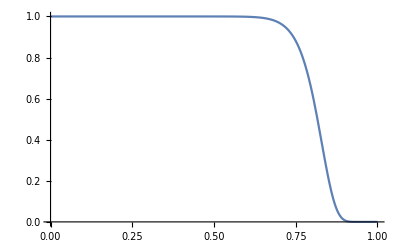

```mathematica
Plot[Exp[-40*(x^20)],{x,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
N[Exp[-40*(0.5)^12]]
```

0.990282

### Radial characteristics: general case first (notice there is no spin dependence for +/-2 cases)

```mathematica
teuk$HC$symbol=(
Coefficient[teuk$pm2$HC[s], Derivative[2,0,0,0][ψ][T,R,ϑ,ϕ]] ξt^2
+Coefficient[teuk$pm2$HC[s], Derivative[1,1,0,0][ψ][T,R,ϑ,ϕ]]ξt ξr
+Coefficient[teuk$pm2$HC[s], Derivative[0,2,0,0][ψ][T,R,ϑ,ϕ]] ξr^2
+Coefficient[teuk$pm2$HC[s], Derivative[0,0,2,0][ψ][T,R,ϑ,ϕ]] ξϑ^2
+Coefficient[teuk$pm2$HC[s], Derivative[1,0,1,0][ψ][T,R,ϑ,ϕ]]ξt ξϑ
+Coefficient[teuk$pm2$HC[s], Derivative[0,1,1,0][ψ][T,R,ϑ,ϕ]]ξr ξϑ
)
```

-(R^2 (L^2-2 M R+(a^2 R^2)/L^2) ξr^2)/L^2-2 (L^2-((-a^2+8 M^2) R^2)/L^2+(4 a^2 M R^3)/L^4) ξr ξt+ξt^2 (16 M^2 (1+(2 M R)/L^2)-(8 a^2 (M R+(2 M^2 R^2)/L^2))/L^2-a^2 Sin[ϑ]^2)

```mathematica
radial$speeds=Block[{ξt,ξr},
ξt=-c;
ξr=1;
Simplify[Solve[teuk$HC$symbol==0,c]]
]
```

{{c→(2 L^6+8 a^2 M R^3+L^2 (2 a^2 R^2-16 M^2 R^2+√2 √(2 L^8+3 a^2 L^4 R^2+2 a^2 L^2 M R^3+a^4 R^4+a^2 R^2 (L^4-2 L^2 M R+a^2 R^2) Cos[2 ϑ])))/(2 (8 M (-2 L^4 M+L^2 (a^2-4 M^2) R+2 a^2 M R^2)+a^2 L^4 Sin[ϑ]^2))},{c→(2 L^6+8 a^2 M R^3-L^2 (-2 a^2 R^2+16 M^2 R^2+√2 √(2 L^8+3 a^2 L^4 R^2+2 a^2 L^2 M R^3+a^4 R^4+a^2 R^2 (L^4-2 L^2 M R+a^2 R^2) Cos[2 ϑ])))/(2 (8 M (-2 L^4 M+L^2 (a^2-4 M^2) R+2 a^2 M R^2)+a^2 L^4 Sin[ϑ]^2))}}

### Comparing characteristics for a=0 and a=1. There appears to be not much of a difference

```mathematica
Simplify[radial$speeds/.{a->M,L->2M}/.M->1,Assumptions->{L>0,R>0,M>0}]
```

{{c→(32-14 R^2+2 R^3+√2 √(512+48 R^2+8 R^3+R^4+(-4+R)^2 R^2 Cos[2 ϑ]))/(8 (-16-6 R+R^2+Sin[ϑ]^2))},{c→(32-14 R^2+2 R^3-√2 √(512+48 R^2+8 R^3+R^4+(-4+R)^2 R^2 Cos[2 ϑ]))/(8 (-16-6 R+R^2+Sin[ϑ]^2))}}

```mathematica
Simplify[radial$speeds/.{a->0,L->2M}/.M->1,Assumptions->{L>0,R>0,M>0}]
```

{{c→1/4 (-2+R)},{c→R^2/(8+4 R)}}

```mathematica
FindMaximum[{Abs[1/4 (-2+R)],0≤R≤2&&0≤ϑ≤π},{R,ϑ}]
FindMaximum[{Abs[(32-14 R^2+2 R^3+√2 √(512+48 R^2+8 R^3+R^4+(-4+R)^2 R^2 Cos[2 ϑ]))/(8 (-16-6 R+R^2+Sin[ϑ]^2))],0≤R≤2&&0≤ϑ≤π},{R,ϑ}]
```

{0.5,{R→3.53661×10^-7,ϑ→0.733019}}

{0.533333,{R→4.16161×10^-7,ϑ→1.5708}}

```mathematica
Plot3D[{1/4 (-2+R),(32-14 R^2+2 R^3+√2 √(512+48 R^2+8 R^3+R^4+(-4+R)^2 R^2 Cos[2 ϑ]))/(8 (-16-6 R+R^2+Sin[ϑ]^2))},{R,0,2},{ϑ,0,π}]
```

-Graphics3D-

```mathematica
FindMaximum[{R^2/(8+4 R),0≤R≤2&&0≤ϑ≤π},{R,ϑ}]
FindMaximum[{(32-14 R^2+2 R^3-√2 √(512+48 R^2+8 R^3+R^4+(-4+R)^2 R^2 Cos[2 ϑ]))/(8 (-16-6 R+R^2+Sin[ϑ]^2)),0≤R≤2&&0≤ϑ≤π},{R,ϑ}]
```

{0.25,{R→2.,ϑ→0.513928}}

{0.256477,{R→2.,ϑ→1.5708}}

```mathematica
Plot3D[{R^2/(8+4 R),(32-14 R^2+2 R^3-√2 √(512+48 R^2+8 R^3+R^4+(-4+R)^2 R^2 Cos[2 ϑ]))/(8 (-16-6 R+R^2+Sin[ϑ]^2))},{R,0,2},{ϑ,0,π}]
```

-Graphics3D-

metric reconstruction equations (“p” means “perturbation of”)

## general formula

```mathematica
A$ul=IdentityMatrix[{4,4}];
A$ul[[1,1]]=A$11[T,R,ϑ,ϕ];
A$ul[[1,2]]=A$12[T,R,ϑ,ϕ];
A$ul[[1,3]]=A$13$re[T,R,ϑ,ϕ]+ⅈ A$13$im[T,R,ϑ,ϕ];
A$ul[[1,4]]=A$13$re[T,R,ϑ,ϕ]-ⅈ A$13$im[T,R,ϑ,ϕ];
A$ul[[2,1]]=0;
A$ul[[2,2]]=0;
A$ul[[2,3]]=0;
A$ul[[2,4]]=0;
A$ul[[3,1]]=A$31$re[T,R,ϑ,ϕ]+ⅈ A$31$im[T,R,ϑ,ϕ];
A$ul[[3,2]]=A$32$re[T,R,ϑ,ϕ]+ⅈ A$32$im[T,R,ϑ,ϕ];
A$ul[[3,3]]=A$33$re[T,R,ϑ,ϕ]+ⅈ A$33$im[T,R,ϑ,ϕ];
A$ul[[3,4]]=A$34$re[T,R,ϑ,ϕ]+ⅈ A$34$im[T,R,ϑ,ϕ];
A$ul[[4,1]]=A$31$re[T,R,ϑ,ϕ]-ⅈ A$31$im[T,R,ϑ,ϕ];
A$ul[[4,2]]=A$32$re[T,R,ϑ,ϕ]-ⅈ A$32$im[T,R,ϑ,ϕ];
A$ul[[4,3]]=A$34$re[T,R,ϑ,ϕ]-ⅈ A$34$im[T,R,ϑ,ϕ];(*think about it! conmplex conjugate of this*)
A$ul[[4,4]]=A$33$re[T,R,ϑ,ϕ]-ⅈ A$33$im[T,R,ϑ,ϕ];
```

```mathematica
A$lu=Table[Sum[η[[ac,ic]]Inverse[η][[bc,jc]]A$ul[[ic,jc]],{ic,1,4},{jc,1,4}],{ac,1,4},{bc,1,4}];
```

```mathematica
lin$der$expand[expr_]:=Block[{𝒟$$1,Δ$$1,δ$$1,δ†$$1,ders},
ders={𝒟$$0,Δ$$0,δ$$0,δ†$$0};
𝒟$$1[x_]:=Sum[A$ul[[1,ac]]ders[[ac]][x],{ac,1,4}];
Δ$$1[x_]:=Sum[A$ul[[2,ac]]ders[[ac]][x],{ac,1,4}];
δ$$1[x_]:=Sum[A$ul[[3,ac]]ders[[ac]][x],{ac,1,4}];
δ†$$1[x_]:=Sum[A$ul[[4,ac]]ders[[ac]][x],{ac,1,4}];
Expand[expr]
]
```

```mathematica
to$HC[expr_]:=expr/.{
ρ$$0:> ρre$$0[R,ϑ]+ⅈ ρim$$0[R,ϑ],ρ†$$0:> ρre$$0[R,ϑ]-ⅈ ρim$$0[R,ϑ],
μ$$0:> μre$$0[R,ϑ]+ⅈ μim$$0[R,ϑ],μ†$$0:> μre$$0[R,ϑ]-ⅈ μim$$0[R,ϑ],
τ$$0:> τre$$0[R,ϑ]+ⅈ τim$$0[R,ϑ],τ†$$0:> τre$$0[R,ϑ]-ⅈ τim$$0[R,ϑ],
Π$$0:> Πre$$0[R,ϑ]+ⅈ Πim$$0[R,ϑ],Π†$$0:> Πre$$0[R,ϑ]-ⅈ Πim$$0[R,ϑ],
ϵ$$0:> ϵre$$0[R,ϑ]+ⅈ ϵim$$0[R,ϑ],ϵ†$$0:> ϵre$$0[R,ϑ]-ⅈ ϵim$$0[R,ϑ],
α$$0:> αre$$0[R,ϑ]+ⅈ αim$$0[R,ϑ],α†$$0:> αre$$0[R,ϑ]-ⅈ αim$$0[R,ϑ],
β$$0:> βre$$0[R,ϑ]+ⅈ βim$$0[R,ϑ],β†$$0:> βre$$0[R,ϑ]-ⅈ βim$$0[R,ϑ],
γ$$0:> 0,γ†$$0:> 0,
ν$$0:> 0,ν†$$0:> 0,
λ$$0:> 0,λ†$$0:> 0,
σ$$0:> 0,σ†$$0:> 0,
κ$$0:>0,κ†$$0:> 0,

Ψ0$$0:> 0,
Ψ1$$0:> 0,
Ψ2$$0:> Ψ2re$$0[R,ϑ]+ⅈ Ψ2im$$0[R,ϑ],
Ψ3$$0:> 0,
Ψ4$$0:>0
}
```

```mathematica
pert$to$funcs[expr_]:=expr/.{
ν$$1->0,ν†$$1->0,
γ$$1->0,γ†$$1->0,
Π†$$1->(τre$$1[T,R,ϑ,ϕ]+ⅈ τim$$1[T,R,ϑ,ϕ]),
Π$$1->(τre$$1[T,R,ϑ,ϕ]-ⅈ τim$$1[T,R,ϑ,ϕ]),

α$$1->(αre$$1[T,R,ϑ,ϕ]+ⅈ αim$$1[T,R,ϑ,ϕ]),α†$$1->(αre$$1[T,R,ϑ,ϕ]-ⅈ αim$$1[T,R,ϑ,ϕ]),
β$$1->(βre$$1[T,R,ϑ,ϕ]+ⅈ βim$$1[T,R,ϑ,ϕ]),β†$$1->(βre$$1[T,R,ϑ,ϕ]-ⅈ βim$$1[T,R,ϑ,ϕ]),
ϵ$$1->(ϵre$$1[T,R,ϑ,ϕ]+ⅈ ϵim$$1[T,R,ϑ,ϕ]),ϵ†$$1->(ϵre$$1[T,R,ϑ,ϕ]-ⅈ ϵim$$1[T,R,ϑ,ϕ]),
τ$$1->(τre$$1[T,R,ϑ,ϕ]+ⅈ τim$$1[T,R,ϑ,ϕ]),τ†$$1->(τre$$1[T,R,ϑ,ϕ]-ⅈ τim$$1[T,R,ϑ,ϕ]),
μ$$1->(μre$$1[T,R,ϑ,ϕ]+ⅈ μim$$1[T,R,ϑ,ϕ]),μ†$$1->(μre$$1[T,R,ϑ,ϕ]-ⅈ μim$$1[T,R,ϑ,ϕ]),
ρ$$1->(ρre$$1[T,R,ϑ,ϕ]+ⅈ ρim$$1[T,R,ϑ,ϕ]),ρ†$$1->(ρre$$1[T,R,ϑ,ϕ]-ⅈ ρim$$1[T,R,ϑ,ϕ]),
λ$$1->(λre$$1[T,R,ϑ,ϕ]+ⅈ λim$$1[T,R,ϑ,ϕ]),λ†$$1->(λre$$1[T,R,ϑ,ϕ]-ⅈ λim$$1[T,R,ϑ,ϕ]),
σ$$1->(σre$$1[T,R,ϑ,ϕ]+ⅈ σim$$1[T,R,ϑ,ϕ]),σ†$$1->(σre$$1[T,R,ϑ,ϕ]-ⅈ σim$$1[T,R,ϑ,ϕ]),
κ$$1->(κre$$1[T,R,ϑ,ϕ]+ⅈ κim$$1[T,R,ϑ,ϕ]),κ†$$1->(κre$$1[T,R,ϑ,ϕ]-ⅈ κim$$1[T,R,ϑ,ϕ]),
Ψ0$$1->(Ψ0re$$1[T,R,ϑ,ϕ]+ⅈ Ψ0im$$1[T,R,ϑ,ϕ]),Ψ0†$$1->(Ψ0re$$1[T,R,ϑ,ϕ]-ⅈ Ψ0im$$1[T,R,ϑ,ϕ]),
Ψ1$$1->(Ψ1re$$1[T,R,ϑ,ϕ]+ⅈ Ψ1im$$1[T,R,ϑ,ϕ]),Ψ1†$$1->(Ψ1re$$1[T,R,ϑ,ϕ]-ⅈ Ψ1im$$1[T,R,ϑ,ϕ]),
Ψ2$$1->(Ψ2re$$1[T,R,ϑ,ϕ]+ⅈ Ψ2im$$1[T,R,ϑ,ϕ]),Ψ2†$$1->(Ψ2re$$1[T,R,ϑ,ϕ]-ⅈ Ψ2im$$1[T,R,ϑ,ϕ]),
Ψ3$$1->(Ψ3re$$1[T,R,ϑ,ϕ]+ⅈ Ψ3im$$1[T,R,ϑ,ϕ]),Ψ3†$$1->(Ψ3re$$1[T,R,ϑ,ϕ]-ⅈ Ψ3im$$1[T,R,ϑ,ϕ]),
Ψ4$$1->(Ψ4re$$1[T,R,ϑ,ϕ]+ⅈ Ψ4im$$1[T,R,ϑ,ϕ]),Ψ4†$$1->(Ψ4re$$1[T,R,ϑ,ϕ]-ⅈ Ψ4im$$1[T,R,ϑ,ϕ])
}
```

```mathematica
find$var$re[expr_]:=Block[{e0,e1,e2,e3,e4,e5},
e0=lin$der$expand[expr];
e1=Coefficient[e0,ℵ];
e2=e1//pert$to$funcs;
e3=e2//sub$funcs$BL;
e4=e3//to$HC;
e5=e4/.{f_[T,R,ϑ,ϕ]->f,f_[R,ϑ]->f};
Collect[Apart[ComplexExpand[Re[e5]]],pert$ders,
FullSimplify]
]
```

```mathematica
find$var$im[expr_]:=Block[{e0,e1,e2,e3,e4,e5},
e0=lin$der$expand[expr];
e1=Coefficient[e0,ℵ];
e2=e1//pert$to$funcs;
e3= e2//sub$funcs$BL;
e4=e3//to$HC;
e5=e4/.{f_[T,R,ϑ,ϕ]->f,f_[R,ϑ]->f};
Collect[Apart[ComplexExpand[Im[e5]]],pert$ders,
FullSimplify]
]
```

## compute pμ

```mathematica
find$pμ$re=find$var$re[-lin$pertrub$identity$Ricci$n]
find$pμ$im=find$var$im[-lin$pertrub$identity$Ricci$n]
```

-2 μim$$0 μim$$1+2 μre$$0 μre$$1+μim$$1 Δ$$0[ⅈ]+Δ$$0[μre$$1]

2 μim$$1 μre$$0+2 μim$$0 μre$$1+Δ$$0[μim$$1]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pμ$re,μre$$1],μre$$1,μim$$1]
convert$metric$recon$to$C[convert$to$k[find$pμ$im,μim$$1],μre$$1,μim$$1]
```

-2*mu_0_im(i,j)*inter_im(i,j) + 2*mu_0_re(i,j)*inter_re(i,j) + inter_im(i,j)*Δ__0(Complex(0,1))

2*inter_im(i,j)*mu_0_re(i,j) + 2*mu_0_im(i,j)*inter_re(i,j)

## compute pλ

```mathematica
find$pλ$re=find$var$re[lin$pertrub$identity$Ricci$j]
find$pλ$im=find$var$im[lin$pertrub$identity$Ricci$j]
```

2 λre$$1 μre$$0+Ψ4re$$1+λim$$1 Δ$$0[ⅈ]+Δ$$0[λre$$1]

2 λim$$1 μre$$0+Ψ4im$$1+Δ$$0[λim$$1]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pλ$re,λre$$1],λre$$1,λim$$1]
convert$metric$recon$to$C[convert$to$k[find$pλ$im,λim$$1],λre$$1,λim$$1]
```

2*inter_re(i,j)*mu_0_re(i,j) + psi4_re(i,j) + inter_im(i,j)*Δ__0(Complex(0,1))

2*inter_im(i,j)*mu_0_re(i,j) + psi4_im(i,j)

## compute pψ3

```mathematica
find$pψ3$re=find$var$re[ -lin$pertrub$identity$Bianchi$h]
find$pψ3$im=find$var$im[ -lin$pertrub$identity$Bianchi$h]
```

4 μre$$0 Ψ3re$$1+4 βim$$0 Ψ4im$$1+(-4 βre$$0+τre$$0) Ψ4re$$1-Ψ4im$$1 (τim$$0+δ$$0[ⅈ])-δ$$0[Ψ4re$$1]+Ψ3im$$1 (-4 μim$$0+Δ$$0[ⅈ])+Δ$$0[Ψ3re$$1]

4 μre$$0 Ψ3im$$1+4 μim$$0 Ψ3re$$1-4 βre$$0 Ψ4im$$1+τre$$0 Ψ4im$$1-4 βim$$0 Ψ4re$$1+τim$$0 Ψ4re$$1-δ$$0[Ψ4im$$1]+Δ$$0[Ψ3im$$1]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pψ3$re,Ψ3re$$1],Ψ3re$$1,Ψ3im$$1]
convert$metric$recon$to$C[convert$to$k[find$pψ3$im,Ψ3im$$1],Ψ3re$$1,Ψ3im$$1]
```

4*mu_0_re(i,j)*inter_re(i,j) + 4*be_0_im(i,j)*psi4_im(i,j) + (-4*be_0_re(i,j) + ta_0_re(i,j))*psi4_re(i,j) - psi4_im(i,j)*(ta_0_im(i,j) + δ__0(Complex(0,1))) - psi4_delta_re(i,j) + inter_im(i,j)*(-4*mu_0_im(i,j) + Δ__0(Complex(0,1)))

4*mu_0_re(i,j)*inter_im(i,j) + 4*mu_0_im(i,j)*inter_re(i,j) - 4*be_0_re(i,j)*psi4_im(i,j) + ta_0_re(i,j)*psi4_im(i,j) - 4*be_0_im(i,j)*psi4_re(i,j) + ta_0_im(i,j)*psi4_re(i,j) - psi4_delta_im(i,j)

## compute pψ2

```mathematica
find$pΨ2$re=find$var$re[-lin$pertrub$identity$Bianchi$g]
find$pΨ2$im=find$var$im[-lin$pertrub$identity$Bianchi$g]
```

-3 μim$$1 Ψ2im$$0+3 μre$$1 Ψ2re$$0+3 μre$$0 Ψ2re$$1+2 βim$$0 Ψ3im$$1+2 (-βre$$0+τre$$0) Ψ3re$$1-Ψ3im$$1 (2 τim$$0+δ$$0[ⅈ])-δ$$0[Ψ3re$$1]+Ψ2im$$1 (-3 μim$$0+Δ$$0[ⅈ])+Δ$$0[Ψ2re$$1]

3 μre$$1 Ψ2im$$0+3 μre$$0 Ψ2im$$1+3 μim$$1 Ψ2re$$0+3 μim$$0 Ψ2re$$1-2 βre$$0 Ψ3im$$1+2 τre$$0 Ψ3im$$1-2 βim$$0 Ψ3re$$1+2 τim$$0 Ψ3re$$1-δ$$0[Ψ3im$$1]+Δ$$0[Ψ2im$$1]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pΨ2$re,Ψ2re$$1],Ψ2re$$1,Ψ2im$$1]
convert$metric$recon$to$C[convert$to$k[find$pΨ2$im,Ψ2im$$1],Ψ2re$$1,Ψ2im$$1]
```

-3*mu_im(i,j)*psi2_0_im(i,j) + 3*mu_re(i,j)*psi2_0_re(i,j) + 3*mu_0_re(i,j)*inter_re(i,j) + 2*be_0_im(i,j)*psi3_im(i,j) + 2*(-be_0_re(i,j) + ta_0_re(i,j))*psi3_re(i,j) - psi3_im(i,j)*(2*ta_0_im(i,j) + δ__0(Complex(0,1))) - psi3_delta_re(i,j) + inter_im(i,j)*(-3*mu_0_im(i,j) + Δ__0(Complex(0,1)))

3*mu_re(i,j)*psi2_0_im(i,j) + 3*mu_0_re(i,j)*inter_im(i,j) + 3*mu_im(i,j)*psi2_0_re(i,j) + 3*mu_0_im(i,j)*inter_re(i,j) - 2*be_0_re(i,j)*psi3_im(i,j) + 2*ta_0_re(i,j)*psi3_im(i,j) - 2*be_0_im(i,j)*psi3_re(i,j) + 2*ta_0_im(i,j)*psi3_re(i,j) - psi3_delta_im(i,j)

## compute pτ (through pΠ)

```mathematica
find$pτ$re=find$var$re[-lin$pertrub$identity$Ricci$i]
find$pτ$im=find$var$im[lin$pertrub$identity$Ricci$i]
```

(λim$$1-μim$$1) (Πim$$0-τim$$0)+2 μim$$0 τim$$1+(λre$$1+μre$$1) (Πre$$0+τre$$0)+2 μre$$0 τre$$1+Ψ3re$$1+τim$$1 Δ$$0[-ⅈ]+Δ$$0[τre$$1]

(λre$$1-μre$$1) (Πim$$0-τim$$0)+2 μre$$0 τim$$1-(λim$$1+μim$$1) (Πre$$0+τre$$0)-2 μim$$0 τre$$1-Ψ3im$$1+Δ$$0[τim$$1]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pτ$re,τre$$1],τre$$1,τim$$1]
convert$metric$recon$to$C[convert$to$k[find$pτ$im,τim$$1],τre$$1,τim$$1]
```

(la_im(i,j) - mu_im(i,j))*(pi_0_im(i,j) - ta_0_im(i,j)) + 2*mu_0_im(i,j)*inter_im(i,j) + (la_re(i,j) + mu_re(i,j))*(pi_0_re(i,j) + ta_0_re(i,j)) + 2*mu_0_re(i,j)*inter_re(i,j) + psi3_re(i,j) + inter_im(i,j)*Δ__0(Complex(0,-1))

(la_re(i,j) - mu_re(i,j))*(pi_0_im(i,j) - ta_0_im(i,j)) + 2*mu_0_re(i,j)*inter_im(i,j) - (la_im(i,j) + mu_im(i,j))*(pi_0_re(i,j) + ta_0_re(i,j)) - 2*mu_0_im(i,j)*inter_re(i,j) - psi3_im(i,j)

## compute pβ

```mathematica
find$pβ$re=find$var$re[-lin$pertrub$identity$Ricci$o]
find$pβ$im=find$var$im[-lin$pertrub$identity$Ricci$o]
```

αim$$0 λim$$1+αre$$0 λre$$1-μim$$1 (βim$$0+τim$$0)-μim$$0 (βim$$1+τim$$1)+μre$$1 (βre$$0+τre$$0)+μre$$0 (βre$$1+τre$$1)+βim$$1 Δ$$0[ⅈ]+Δ$$0[βre$$1]

-αre$$0 λim$$1+αim$$0 λre$$1+μre$$1 (βim$$0+τim$$0)+μre$$0 (βim$$1+τim$$1)+μim$$1 (βre$$0+τre$$0)+μim$$0 (βre$$1+τre$$1)+Δ$$0[βim$$1]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pβ$re,βre$$1],βre$$1,βim$$1]
convert$metric$recon$to$C[convert$to$k[find$pβ$im,βim$$1],βre$$1,βim$$1]
```

al_0_im(i,j)*la_im(i,j) + al_0_re(i,j)*la_re(i,j) - mu_im(i,j)*(be_0_im(i,j) + ta_0_im(i,j)) - mu_0_im(i,j)*(inter_im(i,j) + ta_im(i,j)) + mu_re(i,j)*(be_0_re(i,j) + ta_0_re(i,j)) + mu_0_re(i,j)*(inter_re(i,j) + ta_re(i,j)) + inter_im(i,j)*Δ__0(Complex(0,1))

-(al_0_re(i,j)*la_im(i,j)) + al_0_im(i,j)*la_re(i,j) + mu_re(i,j)*(be_0_im(i,j) + ta_0_im(i,j)) + mu_0_re(i,j)*(inter_im(i,j) + ta_im(i,j)) + mu_im(i,j)*(be_0_re(i,j) + ta_0_re(i,j)) + mu_0_im(i,j)*(inter_re(i,j) + ta_re(i,j))

## compute pα

```mathematica
find$pα$re=find$var$re[-lin$pertrub$identity$Ricci$r]
find$pα$im=find$var$im[-lin$pertrub$identity$Ricci$r]
```

αim$$0 μim$$1+αre$$1 μre$$0+αre$$0 μre$$1-λim$$1 (βim$$0+τim$$0)+λre$$1 (βre$$0+τre$$0)+Ψ3re$$1+αim$$1 (μim$$0+Δ$$0[ⅈ])+Δ$$0[αre$$1]

-αre$$1 μim$$0-αre$$0 μim$$1+αim$$1 μre$$0+αim$$0 μre$$1+λre$$1 (βim$$0+τim$$0)+λim$$1 (βre$$0+τre$$0)+Ψ3im$$1+Δ$$0[αim$$1]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pα$re,αre$$1],αre$$1,αim$$1]
convert$metric$recon$to$C[convert$to$k[find$pα$im,αim$$1],αre$$1,αim$$1]
```

al_0_im(i,j)*mu_im(i,j) + inter_re(i,j)*mu_0_re(i,j) + al_0_re(i,j)*mu_re(i,j) - la_im(i,j)*(be_0_im(i,j) + ta_0_im(i,j)) + la_re(i,j)*(be_0_re(i,j) + ta_0_re(i,j)) + psi3_re(i,j) + inter_im(i,j)*(mu_0_im(i,j) + Δ__0(Complex(0,1)))

-(inter_re(i,j)*mu_0_im(i,j)) - al_0_re(i,j)*mu_im(i,j) + inter_im(i,j)*mu_0_re(i,j) + al_0_im(i,j)*mu_re(i,j) + la_re(i,j)*(be_0_im(i,j) + ta_0_im(i,j)) + la_im(i,j)*(be_0_re(i,j) + ta_0_re(i,j)) + psi3_im(i,j)

## compute pϵ

```mathematica
find$pϵ$re=find$var$re[-lin$pertrub$identity$Ricci$f]
find$pϵ$im=find$var$im[-lin$pertrub$identity$Ricci$f]
```

(Πim$$0-τim$$0) (αim$$1-βim$$1-τim$$1)-2 αim$$0 τim$$1+2 βim$$0 τim$$1+2 (αre$$0+βre$$0) τre$$1+(Πre$$0+τre$$0) (αre$$1+βre$$1+τre$$1)+Ψ2re$$1+ϵim$$1 Δ$$0[ⅈ]+Δ$$0[ϵre$$1]

-(αre$$1-βre$$1) (Πim$$0-τim$$0)+2 αre$$0 τim$$1-2 βre$$0 τim$$1+Πre$$0 (αim$$1+βim$$1+τim$$1)+(αim$$1+βim$$1-τim$$1) τre$$0+2 (αim$$0+βim$$0) τre$$1+(Πim$$0+τim$$0) τre$$1+Ψ2im$$1+Δ$$0[ϵim$$1]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pϵ$re,ϵre$$1],ϵre$$1,ϵim$$1]
convert$metric$recon$to$C[convert$to$k[find$pϵ$im,ϵim$$1],ϵre$$1,ϵim$$1]
```

(pi_0_im(i,j) - ta_0_im(i,j))*(al_im(i,j) - be_im(i,j) - ta_im(i,j)) - 2*al_0_im(i,j)*ta_im(i,j) + 2*be_0_im(i,j)*ta_im(i,j) + 2*(al_0_re(i,j) + be_0_re(i,j))*ta_re(i,j) + (pi_0_re(i,j) + ta_0_re(i,j))*(al_re(i,j) + be_re(i,j) + ta_re(i,j)) + psi2_re(i,j) + inter_im(i,j)*Δ__0(Complex(0,1))

-((al_re(i,j) - be_re(i,j))*(pi_0_im(i,j) - ta_0_im(i,j))) + 2*al_0_re(i,j)*ta_im(i,j) - 2*be_0_re(i,j)*ta_im(i,j) + pi_0_re(i,j)*(al_im(i,j) + be_im(i,j) + ta_im(i,j)) + (al_im(i,j) + be_im(i,j) - ta_im(i,j))*ta_0_re(i,j) + 2*(al_0_im(i,j) + be_0_im(i,j))*ta_re(i,j) + (pi_0_im(i,j) + ta_0_im(i,j))*ta_re(i,j) + psi2_im(i,j)

## compute derivatives

### General formulas

```mathematica
lin$ingoing$Bondi$cluu=Table[
ingoing$bondi[lin$perturb$type$D$vacuum[c$luu[[ac,bc,cc]]]],{ac,1,4},{bc,1,4},{cc,1,4}];
```

```mathematica
zeroeth$ingoing$Bondi$cluu=Block[{ℵ},
ℵ=0;
lin$ingoing$Bondi$cluu
];
```

```mathematica
first$ingoing$Bondi$cluu=Block[{ℵ,\[Shah]},
ℵ=1/(\[Shah]);
Expand[\[Shah] lin$ingoing$Bondi$cluu]/.\[Shah]->0
];
```

```mathematica
first$ingoing$Bondi$cluu[[1,2,3]]
```

κ†$$1

```mathematica
evolution$A=Table[
Sum[
Δ$$0[A$ul[[n,m]]]+A$ul[[n,c]]zeroeth$ingoing$Bondi$cluu[[m,2,c]]-zeroeth$ingoing$Bondi$cluu[[c,2,n]]A$ul[[c,m]]
,{c,1,4}]
-first$ingoing$Bondi$cluu[[m,2,n]]
,{n,1,4},{m,1,4}
];
```

```mathematica
find$A$ul=Block[{e1,e2,e3,e4,e5},
e1=evolution$A;
e2=e1//pert$to$funcs;
e3= e2//sub$funcs$BL;
e4=e3//to$HC;
e5=e4/.{f_[T,R,ϑ,ϕ]->f,f_[R,ϑ]->f};
Collect[e5,pert$ders,
Simplify]
];
```

### a$1i components

```mathematica
find$a11=1/4 find$A$ul[[1,1]]//Expand
convert$metric$recon$to$C[convert$to$k[find$a11,A$11],A$11,A$11]
```

ϵre$$1/2+(A$31$im Πim$$0)/2+(A$31$re Πre$$0)/2-(A$31$im τim$$0)/2+(A$31$re τre$$0)/2+Δ$$0[A$11]

ep_re(i,j)/2. + (A_31_im(i,j)*pi_0_im(i,j))/2. + (A_31_re(i,j)*pi_0_re(i,j))/2. - (A_31_im(i,j)*ta_0_im(i,j))/2. + (A_31_re(i,j)*ta_0_re(i,j))/2.

```mathematica
find$a12=1/4 find$A$ul[[1,2]]//Expand
convert$metric$recon$to$C[convert$to$k[find$a12,A$12],A$12,A$12]
```

-(A$13$im αim$$0)/2+(A$13$re αre$$0)/2+(A$13$im βim$$0)/2+(A$13$re βre$$0)/2+(A$12 ϵre$$0)/2+(A$13$im Πim$$0)/2+(A$32$im Πim$$0)/2-(A$13$re Πre$$0)/2+(A$32$re Πre$$0)/2-(A$32$im τim$$0)/2+(A$32$re τre$$0)/2+Δ$$0[A$12]

-(A_13_im(i,j)*al_0_im(i,j))/2. + (A_13_re(i,j)*al_0_re(i,j))/2. + (A_13_im(i,j)*be_0_im(i,j))/2. + (A_13_re(i,j)*be_0_re(i,j))/2. + (inter_re(i,j)*ep_0_re(i,j))/2. + (A_13_im(i,j)*pi_0_im(i,j))/2. + (A_32_im(i,j)*pi_0_im(i,j))/2. - (A_13_re(i,j)*pi_0_re(i,j))/2. + (A_32_re(i,j)*pi_0_re(i,j))/2. - (A_32_im(i,j)*ta_0_im(i,j))/2. + (A_32_re(i,j)*ta_0_re(i,j))/2.

```mathematica
find$a13=1/4 find$A$ul[[1,3]]//Expand
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Re[find$a13]],A$13$re],A$13$re,A$13$im]
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Im[find$a13]],A$13$im],A$13$re,A$13$im]
```

(A$13$im ϵim$$0)/2-(ⅈ A$13$re ϵim$$0)/2+(ⅈ A$13$im ϵre$$0)/2+(A$13$re ϵre$$0)/2+(ⅈ A$11 Πim$$0)/4+(A$33$im Πim$$0)/4-(ⅈ A$33$re Πim$$0)/4+(A$34$im Πim$$0)/4+(ⅈ A$34$re Πim$$0)/4-(A$11 Πre$$0)/4+(ⅈ A$33$im Πre$$0)/4+(A$33$re Πre$$0)/4-(ⅈ A$34$im Πre$$0)/4+(A$34$re Πre$$0)/4-(A$13$im ρim$$0)/4+(ⅈ A$13$re ρim$$0)/4+(ⅈ A$13$im ρre$$0)/4+(A$13$re ρre$$0)/4-(ⅈ A$11 τim$$0)/4-(A$33$im τim$$0)/4+(ⅈ A$33$re τim$$0)/4-(A$34$im τim$$0)/4-(ⅈ A$34$re τim$$0)/4+(ⅈ τim$$1)/2-(A$11 τre$$0)/4+(ⅈ A$33$im τre$$0)/4+(A$33$re τre$$0)/4-(ⅈ A$34$im τre$$0)/4+(A$34$re τre$$0)/4+τre$$1/2+A$13$im Δ$$0[ⅈ]+ⅈ Δ$$0[A$13$im]+Δ$$0[A$13$re]

(inter_im(i,j)*ep_0_im(i,j))/2. + (inter_re(i,j)*ep_0_re(i,j))/2. + (A_33_im(i,j)*pi_0_im(i,j))/4. + (A_34_im(i,j)*pi_0_im(i,j))/4. - (A_11_re(i,j)*pi_0_re(i,j))/4. + (A_33_re(i,j)*pi_0_re(i,j))/4. + (A_34_re(i,j)*pi_0_re(i,j))/4. - (inter_im(i,j)*rh_0_im(i,j))/4. + (inter_re(i,j)*rh_0_re(i,j))/4. - (A_33_im(i,j)*ta_0_im(i,j))/4. - (A_34_im(i,j)*ta_0_im(i,j))/4. - (A_11_re(i,j)*ta_0_re(i,j))/4. + (A_33_re(i,j)*ta_0_re(i,j))/4. + (A_34_re(i,j)*ta_0_re(i,j))/4. + ta_re(i,j)/2. + inter_im(i,j)*Δ__0(Complex(0,1))

-(inter_re(i,j)*ep_0_im(i,j))/2. + (inter_im(i,j)*ep_0_re(i,j))/2. + (A_11_re(i,j)*pi_0_im(i,j))/4. - (A_33_re(i,j)*pi_0_im(i,j))/4. + (A_34_re(i,j)*pi_0_im(i,j))/4. + (A_33_im(i,j)*pi_0_re(i,j))/4. - (A_34_im(i,j)*pi_0_re(i,j))/4. + (inter_re(i,j)*rh_0_im(i,j))/4. + (inter_im(i,j)*rh_0_re(i,j))/4. - (A_11_re(i,j)*ta_0_im(i,j))/4. + (A_33_re(i,j)*ta_0_im(i,j))/4. - (A_34_re(i,j)*ta_0_im(i,j))/4. + ta_im(i,j)/2. + (A_33_im(i,j)*ta_0_re(i,j))/4. - (A_34_im(i,j)*ta_0_re(i,j))/4.

### a$3i components

```mathematica
find$a31=1/4 find$A$ul[[3,1]]//Expand
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Re[find$a31]],A$31$re],A$31$re,A$31$im]
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Im[find$a31]],A$31$im],A$31$re,A$31$im]
```

-(A$31$im ϵim$$0)/2+(ⅈ A$31$re ϵim$$0)/2-(ⅈ A$31$im ϵre$$0)/2-(A$31$re ϵre$$0)/2+(ⅈ κim$$1)/4-κre$$1/4+(A$31$im ρim$$0)/4-(ⅈ A$31$re ρim$$0)/4-(ⅈ A$31$im ρre$$0)/4-(A$31$re ρre$$0)/4+A$31$im Δ$$0[ⅈ]+ⅈ Δ$$0[A$31$im]+Δ$$0[A$31$re]

-(inter_im(i,j)*ep_0_im(i,j))/2. - (inter_re(i,j)*ep_0_re(i,j))/2. - κre__1/4. + (inter_im(i,j)*rh_0_im(i,j))/4. - (inter_re(i,j)*rh_0_re(i,j))/4. + inter_im(i,j)*Δ__0(Complex(0,1))

(inter_re(i,j)*ep_0_im(i,j))/2. - (inter_im(i,j)*ep_0_re(i,j))/2. + κim__1/4. - (inter_re(i,j)*rh_0_im(i,j))/4. - (inter_im(i,j)*rh_0_re(i,j))/4.

```mathematica
find$a32=1/4 find$A$ul[[3,2]]//Expand
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Re[find$a32]],A$32$re],A$32$re,A$32$im]
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Im[find$a32]],A$32$im],A$32$re,A$32$im]
```

-(A$33$im αim$$0)/4+(ⅈ A$33$re αim$$0)/4+(A$34$im αim$$0)/4-(ⅈ A$34$re αim$$0)/4-(ⅈ αim$$1)/4+(ⅈ A$33$im αre$$0)/4+(A$33$re αre$$0)/4+(ⅈ A$34$im αre$$0)/4+(A$34$re αre$$0)/4-αre$$1/4+(A$33$im βim$$0)/4-(ⅈ A$33$re βim$$0)/4-(A$34$im βim$$0)/4+(ⅈ A$34$re βim$$0)/4+(ⅈ βim$$1)/4+(ⅈ A$33$im βre$$0)/4+(A$33$re βre$$0)/4+(ⅈ A$34$im βre$$0)/4+(A$34$re βre$$0)/4-βre$$1/4-(A$32$im ϵim$$0)/2+(ⅈ A$32$re ϵim$$0)/2+(A$33$im Πim$$0)/4-(ⅈ A$33$re Πim$$0)/4-(A$34$im Πim$$0)/4+(ⅈ A$34$re Πim$$0)/4-(ⅈ A$33$im Πre$$0)/4-(A$33$re Πre$$0)/4-(ⅈ A$34$im Πre$$0)/4-(A$34$re Πre$$0)/4+(A$32$im ρim$$0)/4-(ⅈ A$32$re ρim$$0)/4-(ⅈ A$32$im ρre$$0)/4-(A$32$re ρre$$0)/4-(ⅈ τim$$1)/4+τre$$1/4+A$32$im Δ$$0[ⅈ]+ⅈ Δ$$0[A$32$im]+Δ$$0[A$32$re]

-(A_33_im(i,j)*al_0_im(i,j))/4. + (A_34_im(i,j)*al_0_im(i,j))/4. + (A_33_re(i,j)*al_0_re(i,j))/4. + (A_34_re(i,j)*al_0_re(i,j))/4. - al_re(i,j)/4. + (A_33_im(i,j)*be_0_im(i,j))/4. - (A_34_im(i,j)*be_0_im(i,j))/4. + (A_33_re(i,j)*be_0_re(i,j))/4. + (A_34_re(i,j)*be_0_re(i,j))/4. - be_re(i,j)/4. - (inter_im(i,j)*ep_0_im(i,j))/2. + (A_33_im(i,j)*pi_0_im(i,j))/4. - (A_34_im(i,j)*pi_0_im(i,j))/4. - (A_33_re(i,j)*pi_0_re(i,j))/4. - (A_34_re(i,j)*pi_0_re(i,j))/4. + (inter_im(i,j)*rh_0_im(i,j))/4. - (inter_re(i,j)*rh_0_re(i,j))/4. + ta_re(i,j)/4. + inter_im(i,j)*Δ__0(Complex(0,1))

(A_33_re(i,j)*al_0_im(i,j))/4. - (A_34_re(i,j)*al_0_im(i,j))/4. - al_im(i,j)/4. + (A_33_im(i,j)*al_0_re(i,j))/4. + (A_34_im(i,j)*al_0_re(i,j))/4. - (A_33_re(i,j)*be_0_im(i,j))/4. + (A_34_re(i,j)*be_0_im(i,j))/4. + be_im(i,j)/4. + (A_33_im(i,j)*be_0_re(i,j))/4. + (A_34_im(i,j)*be_0_re(i,j))/4. + (inter_re(i,j)*ep_0_im(i,j))/2. - (A_33_re(i,j)*pi_0_im(i,j))/4. + (A_34_re(i,j)*pi_0_im(i,j))/4. - (A_33_im(i,j)*pi_0_re(i,j))/4. - (A_34_im(i,j)*pi_0_re(i,j))/4. - (inter_re(i,j)*rh_0_im(i,j))/4. - (inter_im(i,j)*rh_0_re(i,j))/4. - ta_im(i,j)/4.

```mathematica
find$a33=1/4 find$A$ul[[3,3]]//Expand
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Re[find$a33]],A$33$re],A$33$re,A$33$im]
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Im[find$a33]],A$33$im],A$33$re,A$33$im]
```

(ⅈ ϵim$$1)/2-(A$31$im Πim$$0)/4+(ⅈ A$31$re Πim$$0)/4-(ⅈ A$31$im Πre$$0)/4-(A$31$re Πre$$0)/4-(ⅈ ρim$$1)/4-ρre$$1/4+(A$31$im τim$$0)/4-(ⅈ A$31$re τim$$0)/4-(ⅈ A$31$im τre$$0)/4-(A$31$re τre$$0)/4+A$33$im Δ$$0[ⅈ]+ⅈ Δ$$0[A$33$im]+Δ$$0[A$33$re]

-(A_31_im(i,j)*pi_0_im(i,j))/4. - (A_31_re(i,j)*pi_0_re(i,j))/4. - rh_re(i,j)/4. + (A_31_im(i,j)*ta_0_im(i,j))/4. - (A_31_re(i,j)*ta_0_re(i,j))/4. + inter_im(i,j)*Δ__0(Complex(0,1))

ep_im(i,j)/2. + (A_31_re(i,j)*pi_0_im(i,j))/4. - (A_31_im(i,j)*pi_0_re(i,j))/4. - rh_im(i,j)/4. - (A_31_re(i,j)*ta_0_im(i,j))/4. - (A_31_im(i,j)*ta_0_re(i,j))/4.

```mathematica
find$a34=1/4 find$A$ul[[3,4]]//Expand
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Re[find$a34]],A$34$re],A$34$re,A$34$im]
convert$metric$recon$to$C[convert$to$k[ComplexExpand[Im[find$a34]],A$34$im],A$34$re,A$34$im]
```

-A$34$im ϵim$$0+ⅈ A$34$re ϵim$$0+(A$31$im Πim$$0)/4-(ⅈ A$31$re Πim$$0)/4-(ⅈ A$31$im Πre$$0)/4-(A$31$re Πre$$0)/4+(A$34$im ρim$$0)/2-(ⅈ A$34$re ρim$$0)/2+(ⅈ σim$$1)/4-σre$$1/4-(A$31$im τim$$0)/4+(ⅈ A$31$re τim$$0)/4-(ⅈ A$31$im τre$$0)/4-(A$31$re τre$$0)/4+A$34$im Δ$$0[ⅈ]+ⅈ Δ$$0[A$34$im]+Δ$$0[A$34$re]

-(inter_im(i,j)*ep_0_im(i,j)) + (A_31_im(i,j)*pi_0_im(i,j))/4. - (A_31_re(i,j)*pi_0_re(i,j))/4. + (inter_im(i,j)*rh_0_im(i,j))/2. - si_re(i,j)/4. - (A_31_im(i,j)*ta_0_im(i,j))/4. - (A_31_re(i,j)*ta_0_re(i,j))/4. + inter_im(i,j)*Δ__0(Complex(0,1))

inter_re(i,j)*ep_0_im(i,j) - (A_31_re(i,j)*pi_0_im(i,j))/4. - (A_31_im(i,j)*pi_0_re(i,j))/4. - (inter_re(i,j)*rh_0_im(i,j))/2. + si_im(i,j)/4. + (A_31_re(i,j)*ta_0_im(i,j))/4. - (A_31_im(i,j)*ta_0_re(i,j))/4.

## compute pΨ1-

```mathematica
convert$metric$recon$to$C[convert$to$k[A$33$re δ$$0[Ψ2re$$0]-δ$$0[Ψ2re$$1],Ψ1re$$1],Ψ1re$$1,Ψ1im$$1]
```

A_33_re(i,j)*psi2_0_delta_re(i,j) - psi2_delta_re(i,j)

```mathematica
find$pΨ1$re=find$var$re[-lin$pertrub$identity$Bianchi$f]
find$pΨ1$im=find$var$im[-lin$pertrub$identity$Bianchi$f]
```

-2 μim$$0 Ψ1im$$1+2 μre$$0 Ψ1re$$1-3 τim$$1 Ψ2im$$0-3 τim$$0 Ψ2im$$1+3 τre$$1 Ψ2re$$0+3 τre$$0 Ψ2re$$1-A$31$re Ψ2im$$0 𝒟$$0[ⅈ]+A$31$im 𝒟$$0[Ψ2im$$0]-A$31$re 𝒟$$0[Ψ2re$$0]-(A$33$re Ψ2im$$0+Ψ2im$$1) δ$$0[ⅈ]+A$33$im δ$$0[Ψ2im$$0]-A$33$re δ$$0[Ψ2re$$0]-δ$$0[Ψ2re$$1]+(Ψ1im$$1-A$32$re Ψ2im$$0) Δ$$0[ⅈ]+Δ$$0[Ψ1re$$1]+A$32$im Δ$$0[Ψ2im$$0]-A$32$re Δ$$0[Ψ2re$$0]-A$34$re Ψ2im$$0 δ†$$0[ⅈ]+A$34$im δ†$$0[Ψ2im$$0]-A$34$re δ†$$0[Ψ2re$$0]

2 μre$$0 Ψ1im$$1+2 μim$$0 Ψ1re$$1+3 τre$$1 Ψ2im$$0+3 τre$$0 Ψ2im$$1+3 τim$$1 Ψ2re$$0+3 τim$$0 Ψ2re$$1-A$31$re 𝒟$$0[Ψ2im$$0]-A$31$im 𝒟$$0[Ψ2re$$0]-A$33$re δ$$0[Ψ2im$$0]-δ$$0[Ψ2im$$1]-A$33$im δ$$0[Ψ2re$$0]+Δ$$0[Ψ1im$$1]-A$32$re Δ$$0[Ψ2im$$0]-A$32$im Δ$$0[Ψ2re$$0]-Ψ2im$$0 (A$31$im 𝒟$$0[ⅈ]+A$33$im δ$$0[ⅈ]+A$32$im Δ$$0[ⅈ]+A$34$im δ†$$0[ⅈ])-A$34$re δ†$$0[Ψ2im$$0]-A$34$im δ†$$0[Ψ2re$$0]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pΨ1$re,Ψ1re$$1],Ψ1re$$1,Ψ1im$$1]
convert$metric$recon$to$C[convert$to$k[find$pΨ1$im,Ψ1im$$1],Ψ1re$$1,Ψ1im$$1]
```

-2*mu_0_im(i,j)*inter_im(i,j) + 2*mu_0_re(i,j)*inter_re(i,j) - 3*ta_im(i,j)*psi2_0_im(i,j) - 3*ta_0_im(i,j)*psi2_im(i,j) + 3*ta_re(i,j)*psi2_0_re(i,j) + 3*ta_0_re(i,j)*psi2_re(i,j) - A_31_re(i,j)*psi2_0_im(i,j)*𝒟__0(Complex(0,1)) + A_31_im(i,j)*psi2_0_D_im(i,j) - A_31_re(i,j)*psi2_0_D_re(i,j) - (A_33_re(i,j)*psi2_0_im(i,j) + psi2_im(i,j))*δ__0(Complex(0,1)) + A_33_im(i,j)*psi2_0_delta_im(i,j) - A_33_re(i,j)*psi2_0_delta_re(i,j) - psi2_delta_re(i,j) + (inter_im(i,j) - A_32_re(i,j)*psi2_0_im(i,j))*Δ__0(Complex(0,1)) + A_32_im(i,j)*psi2_0_cDelta_im(i,j) - A_32_re(i,j)*psi2_0_cDelta_re(i,j) - A_34_re(i,j)*psi2_0_im(i,j)*δ†__0(Complex(0,1)) + A_34_im(i,j)*psi2_0_deltacc(j)_im(i,j) - A_34_re(i,j)*psi2_0_deltacc(j)_re(i,j)

2*mu_0_re(i,j)*inter_im(i,j) + 2*mu_0_im(i,j)*inter_re(i,j) + 3*ta_re(i,j)*psi2_0_im(i,j) + 3*ta_0_re(i,j)*psi2_im(i,j) + 3*ta_im(i,j)*psi2_0_re(i,j) + 3*ta_0_im(i,j)*psi2_re(i,j) - A_31_re(i,j)*psi2_0_D_im(i,j) - A_31_im(i,j)*psi2_0_D_re(i,j) - A_33_re(i,j)*psi2_0_delta_im(i,j) - psi2_delta_im(i,j) - A_33_im(i,j)*psi2_0_delta_re(i,j) - A_32_re(i,j)*psi2_0_cDelta_im(i,j) - A_32_im(i,j)*psi2_0_cDelta_re(i,j) - psi2_0_im(i,j)*(A_31_im(i,j)*𝒟__0(Complex(0,1)) + A_33_im(i,j)*δ__0(Complex(0,1)) + A_32_im(i,j)*Δ__0(Complex(0,1)) + A_34_im(i,j)*δ†__0(Complex(0,1))) - A_34_re(i,j)*psi2_0_deltacc(j)_im(i,j) - A_34_im(i,j)*psi2_0_deltacc(j)_re(i,j)

## compute pσ

```mathematica
find$pσ$re=find$var$re[-lin$pertrub$identity$Ricci$p]
find$pσ$im=find$var$im[-lin$pertrub$identity$Ricci$p]
```

λim$$1 ρim$$0+λre$$1 ρre$$0-μim$$0 σim$$1+μre$$0 σre$$1-(αim$$0+βim$$0) τim$$1+(-αre$$0+βre$$0) τre$$1+τre$$0 (-αre$$1+βre$$1+2 τre$$1)-τim$$0 (αim$$1+βim$$1+2 τim$$1+A$31$re 𝒟$$0[ⅈ])+A$31$im 𝒟$$0[τim$$0]-A$31$re 𝒟$$0[τre$$0]-(A$33$re τim$$0+τim$$1) δ$$0[ⅈ]+A$33$im δ$$0[τim$$0]-A$33$re δ$$0[τre$$0]-δ$$0[τre$$1]+(σim$$1-A$32$re τim$$0) Δ$$0[ⅈ]+Δ$$0[σre$$1]+A$32$im Δ$$0[τim$$0]-A$32$re Δ$$0[τre$$0]-A$34$re τim$$0 δ†$$0[ⅈ]+A$34$im δ†$$0[τim$$0]-A$34$re δ†$$0[τre$$0]

λre$$1 ρim$$0-λim$$1 ρre$$0+μre$$0 σim$$1+μim$$0 σre$$1+(αim$$1+βim$$1) τre$$0+τim$$1 (-αre$$0+βre$$0+2 τre$$0)+(αim$$0+βim$$0) τre$$1-A$31$re 𝒟$$0[τim$$0]-A$31$im 𝒟$$0[τre$$0]-A$33$re δ$$0[τim$$0]-δ$$0[τim$$1]-A$33$im δ$$0[τre$$0]+Δ$$0[σim$$1]-A$32$re Δ$$0[τim$$0]-A$32$im Δ$$0[τre$$0]-τim$$0 (αre$$1-βre$$1-2 τre$$1+A$31$im 𝒟$$0[ⅈ]+A$33$im δ$$0[ⅈ]+A$32$im Δ$$0[ⅈ]+A$34$im δ†$$0[ⅈ])-A$34$re δ†$$0[τim$$0]-A$34$im δ†$$0[τre$$0]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pσ$re,σre$$1],σre$$1,σim$$1]
convert$metric$recon$to$C[convert$to$k[find$pσ$im,σim$$1],σre$$1,σim$$1]
```

la_im(i,j)*rh_0_im(i,j) + la_re(i,j)*rh_0_re(i,j) - mu_0_im(i,j)*inter_im(i,j) + mu_0_re(i,j)*inter_re(i,j) - (al_0_im(i,j) + be_0_im(i,j))*ta_im(i,j) + (-al_0_re(i,j) + be_0_re(i,j))*ta_re(i,j) + ta_0_re(i,j)*(-al_re(i,j) + be_re(i,j) + 2*ta_re(i,j)) - ta_0_im(i,j)*(al_im(i,j) + be_im(i,j) + 2*ta_im(i,j) + A_31_re(i,j)*𝒟__0(Complex(0,1))) + A_31_im(i,j)*ta_0_D_im(i,j) - A_31_re(i,j)*ta_0_D_re(i,j) - (A_33_re(i,j)*ta_0_im(i,j) + ta_im(i,j))*δ__0(Complex(0,1)) + A_33_im(i,j)*ta_0_delta_im(i,j) - A_33_re(i,j)*ta_0_delta_re(i,j) - ta_delta_re(i,j) + (inter_im(i,j) - A_32_re(i,j)*ta_0_im(i,j))*Δ__0(Complex(0,1)) + A_32_im(i,j)*ta_0_cDelta_im(i,j) - A_32_re(i,j)*ta_0_cDelta_re(i,j) - A_34_re(i,j)*ta_0_im(i,j)*δ†__0(Complex(0,1)) + A_34_im(i,j)*ta_0_deltacc(j)_im(i,j) - A_34_re(i,j)*ta_0_deltacc(j)_re(i,j)

la_re(i,j)*rh_0_im(i,j) - la_im(i,j)*rh_0_re(i,j) + mu_0_re(i,j)*inter_im(i,j) + mu_0_im(i,j)*inter_re(i,j) + (al_im(i,j) + be_im(i,j))*ta_0_re(i,j) + ta_im(i,j)*(-al_0_re(i,j) + be_0_re(i,j) + 2*ta_0_re(i,j)) + (al_0_im(i,j) + be_0_im(i,j))*ta_re(i,j) - A_31_re(i,j)*ta_0_D_im(i,j) - A_31_im(i,j)*ta_0_D_re(i,j) - A_33_re(i,j)*ta_0_delta_im(i,j) - ta_delta_im(i,j) - A_33_im(i,j)*ta_0_delta_re(i,j) - A_32_re(i,j)*ta_0_cDelta_im(i,j) - A_32_im(i,j)*ta_0_cDelta_re(i,j) - ta_0_im(i,j)*(al_re(i,j) - be_re(i,j) - 2*ta_re(i,j) + A_31_im(i,j)*𝒟__0(Complex(0,1)) + A_33_im(i,j)*δ__0(Complex(0,1)) + A_32_im(i,j)*Δ__0(Complex(0,1)) + A_34_im(i,j)*δ†__0(Complex(0,1))) - A_34_re(i,j)*ta_0_deltacc(j)_im(i,j) - A_34_im(i,j)*ta_0_deltacc(j)_re(i,j)

## compute pκ

```mathematica
find$pκ$re=find$var$re[ lin$pertrub$identity$Ricci$c]
find$pκ$im=find$var$im[lin$pertrub$identity$Ricci$c]
```

Πim$$0 (ρim$$1-σim$$1)-2 ϵim$$1 τim$$0-ρim$$1 τim$$0+σim$$1 τim$$0-2 ρim$$0 τim$$1+(ρre$$1+σre$$1) (Πre$$0+τre$$0)+2 ρre$$0 τre$$1+Ψ1re$$1-A$11 τim$$0 𝒟$$0[ⅈ]-τim$$1 𝒟$$0[ⅈ]-A$11 𝒟$$0[τre$$0]-𝒟$$0[τre$$1]-A$13$re τim$$0 δ$$0[ⅈ]+(κim$$1-A$12 τim$$0) Δ$$0[ⅈ]+Δ$$0[κre$$1]-A$12 Δ$$0[τre$$0]+A$13$im (δ$$0[τim$$0]-δ†$$0[τim$$0])-A$13$re (δ$$0[τre$$0]+τim$$0 δ†$$0[ⅈ]+δ†$$0[τre$$0])

Πim$$0 (-ρre$$1+σre$$1)+ρre$$1 τim$$0+2 ρre$$0 τim$$1+2 ϵim$$1 τre$$0+(ρim$$1+σim$$1) (Πre$$0+τre$$0)+2 ρim$$0 τre$$1+Ψ1im$$1-A$11 𝒟$$0[τim$$0]-𝒟$$0[τim$$1]-τim$$0 (σre$$1+A$13$im δ$$0[ⅈ])+Δ$$0[κim$$1]-A$12 Δ$$0[τim$$0]-A$13$re (δ$$0[τim$$0]+δ†$$0[τim$$0])+A$13$im (-δ$$0[τre$$0]+τim$$0 δ†$$0[ⅈ]+δ†$$0[τre$$0])

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pκ$re,κre$$1],κre$$1,κim$$1]
convert$metric$recon$to$C[convert$to$k[find$pκ$im,κim$$1],κre$$1,κim$$1]
```

pi_0_im(i,j)*(rh_im(i,j) - si_im(i,j)) - 2*ep_im(i,j)*ta_0_im(i,j) - rh_im(i,j)*ta_0_im(i,j) + si_im(i,j)*ta_0_im(i,j) - 2*rh_0_im(i,j)*ta_im(i,j) + (rh_re(i,j) + si_re(i,j))*(pi_0_re(i,j) + ta_0_re(i,j)) + 2*rh_0_re(i,j)*ta_re(i,j) + psi1_re(i,j) - A_11_re(i,j)*ta_0_im(i,j)*𝒟__0(Complex(0,1)) - ta_im(i,j)*𝒟__0(Complex(0,1)) - A_11_re(i,j)*ta_0_D_re(i,j) - ta_D_re(i,j) - A_13_re(i,j)*ta_0_im(i,j)*δ__0(Complex(0,1)) + (inter_im(i,j) - A_12_re(i,j)*ta_0_im(i,j))*Δ__0(Complex(0,1)) - A_12_re(i,j)*ta_0_cDelta_re(i,j) + A_13_im(i,j)*(ta_0_delta_im(i,j) - ta_0_deltacc(j)_im(i,j)) - A_13_re(i,j)*(ta_0_delta_re(i,j) + ta_0_im(i,j)*δ†__0(Complex(0,1)) + ta_0_deltacc(j)_re(i,j))

pi_0_im(i,j)*(-rh_re(i,j) + si_re(i,j)) + rh_re(i,j)*ta_0_im(i,j) + 2*rh_0_re(i,j)*ta_im(i,j) + 2*ep_im(i,j)*ta_0_re(i,j) + (rh_im(i,j) + si_im(i,j))*(pi_0_re(i,j) + ta_0_re(i,j)) + 2*rh_0_im(i,j)*ta_re(i,j) + psi1_im(i,j) - A_11_re(i,j)*ta_0_D_im(i,j) - ta_D_im(i,j) - ta_0_im(i,j)*(si_re(i,j) + A_13_im(i,j)*δ__0(Complex(0,1))) - A_12_re(i,j)*ta_0_cDelta_im(i,j) - A_13_re(i,j)*(ta_0_delta_im(i,j) + ta_0_deltacc(j)_im(i,j)) + A_13_im(i,j)*(-ta_0_delta_re(i,j) + ta_0_im(i,j)*δ†__0(Complex(0,1)) + ta_0_deltacc(j)_re(i,j))

## compute pρ

```mathematica
find$pρ$re=find$var$re[lin$pertrub$identity$Ricci$q]
find$pρ$im=find$var$im[lin$pertrub$identity$Ricci$q]
```

μim$$1 ρim$$0+μim$$0 ρim$$1+μre$$1 ρre$$0+μre$$0 ρre$$1-(αim$$0+βim$$0) τim$$1+αre$$0 τre$$1-βre$$0 τre$$1+τre$$0 (αre$$1-βre$$1+2 τre$$1)+Ψ2re$$1-A$31$im 𝒟$$0[τim$$0]-A$31$re 𝒟$$0[τre$$0]-A$34$im δ$$0[τim$$0]-A$34$re δ$$0[τre$$0]+ρim$$1 Δ$$0[ⅈ]-τim$$0 (αim$$1+βim$$1-2 τim$$1+A$31$re 𝒟$$0[ⅈ]+A$34$re δ$$0[ⅈ]+A$32$re Δ$$0[ⅈ])+Δ$$0[ρre$$1]-A$32$im Δ$$0[τim$$0]-A$32$re Δ$$0[τre$$0]-(A$33$re τim$$0+τim$$1) δ†$$0[ⅈ]-A$33$im δ†$$0[τim$$0]-A$33$re δ†$$0[τre$$0]-δ†$$0[τre$$1]

μre$$1 ρim$$0+μre$$0 ρim$$1-μim$$1 ρre$$0-μim$$0 ρre$$1+(αre$$0-βre$$0) τim$$1+(αim$$1+βim$$1) τre$$0+(αim$$0+βim$$0) τre$$1+Ψ2im$$1-A$31$re 𝒟$$0[τim$$0]+A$31$im 𝒟$$0[τre$$0]-A$34$re δ$$0[τim$$0]+A$34$im δ$$0[τre$$0]+Δ$$0[ρim$$1]-A$32$re Δ$$0[τim$$0]+A$32$im Δ$$0[τre$$0]+τim$$0 (αre$$1-βre$$1+A$31$im 𝒟$$0[ⅈ]+A$34$im δ$$0[ⅈ]+A$32$im Δ$$0[ⅈ]+A$33$im δ†$$0[ⅈ])-A$33$re δ†$$0[τim$$0]-δ†$$0[τim$$1]+A$33$im δ†$$0[τre$$0]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pρ$re,ρre$$1],ρre$$1,ρim$$1]
convert$metric$recon$to$C[convert$to$k[find$pρ$im,ρim$$1],ρre$$1,ρim$$1]
```

mu_im(i,j)*rh_0_im(i,j) + mu_0_im(i,j)*inter_im(i,j) + mu_re(i,j)*rh_0_re(i,j) + mu_0_re(i,j)*inter_re(i,j) - (al_0_im(i,j) + be_0_im(i,j))*ta_im(i,j) + al_0_re(i,j)*ta_re(i,j) - be_0_re(i,j)*ta_re(i,j) + ta_0_re(i,j)*(al_re(i,j) - be_re(i,j) + 2*ta_re(i,j)) + psi2_re(i,j) - A_31_im(i,j)*ta_0_D_im(i,j) - A_31_re(i,j)*ta_0_D_re(i,j) - A_34_im(i,j)*ta_0_delta_im(i,j) - A_34_re(i,j)*ta_0_delta_re(i,j) + inter_im(i,j)*Δ__0(Complex(0,1)) - ta_0_im(i,j)*(al_im(i,j) + be_im(i,j) - 2*ta_im(i,j) + A_31_re(i,j)*𝒟__0(Complex(0,1)) + A_34_re(i,j)*δ__0(Complex(0,1)) + A_32_re(i,j)*Δ__0(Complex(0,1))) - A_32_im(i,j)*ta_0_cDelta_im(i,j) - A_32_re(i,j)*ta_0_cDelta_re(i,j) - (A_33_re(i,j)*ta_0_im(i,j) + ta_im(i,j))*δ†__0(Complex(0,1)) - A_33_im(i,j)*ta_0_deltacc(j)_im(i,j) - A_33_re(i,j)*ta_0_deltacc(j)_re(i,j) - ta_deltacc(j)_re(i,j)

mu_re(i,j)*rh_0_im(i,j) + mu_0_re(i,j)*inter_im(i,j) - mu_im(i,j)*rh_0_re(i,j) - mu_0_im(i,j)*inter_re(i,j) + (al_0_re(i,j) - be_0_re(i,j))*ta_im(i,j) + (al_im(i,j) + be_im(i,j))*ta_0_re(i,j) + (al_0_im(i,j) + be_0_im(i,j))*ta_re(i,j) + psi2_im(i,j) - A_31_re(i,j)*ta_0_D_im(i,j) + A_31_im(i,j)*ta_0_D_re(i,j) - A_34_re(i,j)*ta_0_delta_im(i,j) + A_34_im(i,j)*ta_0_delta_re(i,j) - A_32_re(i,j)*ta_0_cDelta_im(i,j) + A_32_im(i,j)*ta_0_cDelta_re(i,j) + ta_0_im(i,j)*(al_re(i,j) - be_re(i,j) + A_31_im(i,j)*𝒟__0(Complex(0,1)) + A_34_im(i,j)*δ__0(Complex(0,1)) + A_32_im(i,j)*Δ__0(Complex(0,1)) + A_33_im(i,j)*δ†__0(Complex(0,1))) - A_33_re(i,j)*ta_0_deltacc(j)_im(i,j) - ta_deltacc(j)_im(i,j) + A_33_im(i,j)*ta_0_deltacc(j)_re(i,j)

## compute pΨ0

```mathematica
find$pΨ0$re=find$var$re[-lin$pertrub$identity$Bianchi$e]
find$pΨ0$im=find$var$im[-lin$pertrub$identity$Bianchi$e]
```

μre$$0 Ψ0re$$1+2 βre$$0 Ψ1re$$1+4 τre$$0 Ψ1re$$1+3 σim$$1 Ψ2im$$0-3 σre$$1 Ψ2re$$0-Ψ1im$$1 (2 βim$$0+4 τim$$0+δ$$0[ⅈ])-δ$$0[Ψ1re$$1]+Ψ0im$$1 (-μim$$0+Δ$$0[ⅈ])+Δ$$0[Ψ0re$$1]

μre$$0 Ψ0im$$1+μim$$0 Ψ0re$$1+2 βre$$0 Ψ1im$$1+4 τre$$0 Ψ1im$$1+2 βim$$0 Ψ1re$$1+4 τim$$0 Ψ1re$$1-3 σre$$1 Ψ2im$$0-3 σim$$1 Ψ2re$$0-δ$$0[Ψ1im$$1]+Δ$$0[Ψ0im$$1]

```mathematica
convert$metric$recon$to$C[convert$to$k[find$pΨ0$re,Ψ0re$$1],Ψ0re$$1,Ψ0im$$1]
convert$metric$recon$to$C[convert$to$k[find$pΨ0$im,Ψ0im$$1],Ψ0re$$1,Ψ0im$$1]
```

mu_0_re(i,j)*inter_re(i,j) + 2*be_0_re(i,j)*psi1_re(i,j) + 4*ta_0_re(i,j)*psi1_re(i,j) + 3*si_im(i,j)*psi2_0_im(i,j) - 3*si_re(i,j)*psi2_0_re(i,j) - psi1_im(i,j)*(2*be_0_im(i,j) + 4*ta_0_im(i,j) + δ__0(Complex(0,1))) - psi1_delta_re(i,j) + inter_im(i,j)*(-mu_0_im(i,j) + Δ__0(Complex(0,1)))

mu_0_re(i,j)*inter_im(i,j) + mu_0_im(i,j)*inter_re(i,j) + 2*be_0_re(i,j)*psi1_im(i,j) + 4*ta_0_re(i,j)*psi1_im(i,j) + 2*be_0_im(i,j)*psi1_re(i,j) + 4*ta_0_im(i,j)*psi1_re(i,j) - 3*si_re(i,j)*psi2_0_im(i,j) - 3*si_im(i,j)*psi2_0_re(i,j) - psi1_delta_im(i,j)

Source term

```mathematica
d3$$0[f_]:=δ†$$0[f]+(3α$$0+β†$$0+4Π$$0-τ†$$0)f
d4$$0[f_]:=Δ$$0[f]+(4μ$$0+μ†$$0+3γ$$0-γ†$$0)f
```

```mathematica
d3$$1[f_]:=δ†$$1[f]+(3α$$1+β†$$1+4Π$$1-τ†$$1)f
d4$$1[f_]:=Δ$$1[f]+(4μ$$1+μ†$$1+3γ$$1-γ†$$1)f
```

```mathematica
source$1=Block[{
inner$d4$psi4,inner$d3$psi4,
term$der$psi4,
inner$d4$psi3,inner$d3$psi3,
term$der$psi3,
term$der$psi2,
coef$psi2,
source$inter,
source},
inner$d4$psi4=𝒟$$1[Ψ4$$1]+(4ϵ$$1-ρ$$1)Ψ4$$1;
inner$d3$psi4=δ$$1[Ψ4$$1]+(4β$$1-τ$$1)Ψ4$$1;
term$der$psi4=-(d4$$0[inner$d4$psi4]-d3$$0[inner$d3$psi4]);
inner$d4$psi3=0(*δ†$$1[Ψ3$$1]+(2α$$1+4Π$$1)Ψ3$$1*);
inner$d3$psi3=0(*Δ$$1[Ψ3$$1]+(2γ$$1+4μ$$1)Ψ3$$1*);
term$der$psi3=0(*d4$$0[inner$d4$psi3]-d3$$0[inner$d3$psi3]*);
term$der$psi2=0(*3(-d4$$0[λ$$1 Ψ2$$1]+d3$$0[ν$$1 Ψ2$$1])*);
coef$psi2=0(*3(d4$$1[λ$$1]-3μ$$1 λ$$1-d3$$1[ν$$1]+3Π$$1 ν$$1)*);
source$inter=(Δ$BL[r](term$der$psi4+term$der$psi3+term$der$psi2+coef$psi2 Ψ2$$0)//sub$funcs$BL//lin$der$expand//pert$to$funcs//to$HC//convert$func$m)/.r->L^2/R ;
source=Collect[source$inter,pert$ders,Simplify]
];
```

Initial data

## Time symmetric initial data

```mathematica
time$symmetric$P=Collect[(8M(2M-(a^2 R)/L^2)(1+(2M R)/L^2)-a^2(1-Y^2))D[ψr[T,R,Y],T]
-2(L^2-(8 M^2-a^2)(R^2/L^2)+(4 a^2 M R^3)/L^4)Q[T,R,Y]
+2ⅈ m$ang a (1+(4M R)/L^2)ψr[T,R,Y]
+2(2M(-s+(2+s)((2M R)/L^2)-(3 a^2 R^2)/L^4)-(a^2 R)/L^2+ⅈ s a (-Y))ψr[T,R,Y]/.{
D[ψr[T,R,Y],T]->0
},
{Q[T,R,Y],ψr[T,R,Y]},FullSimplify
]
```

-(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3) Q[T,R,Y])/L^4+((-2 a^2 R (L^2+6 M R)+4 L^2 M (-L^2 s+2 M R (2+s))+2 ⅈ a (4 L^2 M m$ang R+L^4 (m$ang-s Y))) ψr[T,R,Y])/L^4

```mathematica
Block[{P,Q,ψr,R,Y,tmp$re,tmp$im},
P[T_,R_,Y_]:=p$re+ⅈ p$im;
Q[T_,R_,Y_]:=q$re+ⅈ q$im;
ψr[T_,R_,Y_]:=f$re+ⅈ f$im;
tmp$re=time$symmetric$P//Re//ComplexExpand;
tmp$im=time$symmetric$P//Im//ComplexExpand;
StringReplace[ToString[CForm[tmp$re]],{
"$"->"_","Power"->"pow","R"->"R(i)","Y"->"Y(j)","a"->"bhs","M"->"bhm","L"->"cl","s"->"spin","m"->"m_ang",
"f$re"->"f_re(i,j)","f$im"->"f_im(i,j)",
"p$re"->"p_re(i,j)","p$im"->"p_im(i,j)",
"q$re"->"q_re(i,j)","q$im"->"q_im(i,j)"
}]
]
```

-2*bhs*f_im(i,j)*m_ang_bhsng - 2*pow(cl,2)*q_re(i,j) - (2*pow(bhs,2)*f_re(i,j)*R(i))/pow(cl,2) + (16*f_re(i,j)*pow(bhm,2)*R(i))/pow(cl,2) - (8*bhs*f_im(i,j)*bhm*m_ang_bhsng*R(i))/pow(cl,2) - (12*pow(bhs,2)*f_re(i,j)*bhm*pow(R(i),2))/pow(cl,4) - (2*pow(bhs,2)*q_re(i,j)*pow(R(i),2))/pow(cl,2) + (16*pow(bhm,2)*q_re(i,j)*pow(R(i),2))/pow(cl,2) - (8*pow(bhs,2)*bhm*q_re(i,j)*pow(R(i),3))/pow(cl,4) - 4*f_re(i,j)*bhm*spin + (8*f_re(i,j)*pow(bhm,2)*R(i)*spin)/pow(cl,2) + 2*bhs*f_im(i,j)*spin*Y(j)

```mathematica
Block[{ppp,qqq,fff,P,Q,ψr},
P[T_,R_,Y_]:=ppp;
Q[T_,R_,Y_]:=qqq;
ψr[T_,R_,Y_]:=fff;
StringReplace[convert$pde$to$fortran[time$symmetric$P],{
"fff"->"f(i,j,m_ang)",
"ppp"->"p(i,j,m_ang)",
"qqq"->"q(i,j,m_ang)"
}]
]
```

(-2*q(i,j,m_ang)*(cl**6 + cl**2*(bhs**2 - 8*bhm**2)*R**2 + 4*bhs**2*bhm*R**3))/cl**4 + (f(i,j,m_ang)*(-2*bhs**2*R*(cl**2 + 6*bhm*R) + 4*cl**2*bhm*(-(cl**2*spin) + 2*bhm*R*(2 + spin)) + (0,2)*bhs*(4*cl**2*bhm*m_bhsng*R + cl**4*(m_bhsng - spin*Y))))/cl**4

## Ingoing initial data (i.e. \partial_{\mu}\phi ~ n_{\mu})

```mathematica
ingoing$P=Collect[(8M(2M-(a^2 R)/L^2)(1+(2M R)/L^2)-a^2(1-Y^2))D[ψr[T,R,Y],T]
-2(L^2-(8 M^2-a^2)(R^2/L^2)+(4 a^2 M R^3)/L^4)Q[T,R,Y]
+2ⅈ m$ang a (1+(4M R)/L^2)ψr[T,R,Y]
+2(2M(-s+(2+s)((2M R)/L^2)-(3 a^2 R^2)/L^4)-(a^2 R)/L^2+ⅈ s a (-Y))ψr[T,R,Y]/.{
(*ingoing*)
D[ψr[T,R,Y],T]->-1/(2+(4M R)/L^2)(R^2/L^2)R Q[T,R,Y]

},
{Q[T,R,Y],ψr[T,R,Y]},FullSimplify
]
```

(-(2 (L^6+L^2 (a^2-8 M^2) R^2+4 a^2 M R^3))/L^4-(R^3 (8 M (2 M-(a^2 R)/L^2) (1+(2 M R)/L^2)+a^2 (-1+Y^2)))/(L^2 (2+(4 M R)/L^2))) Q[T,R,Y]+((-2 a^2 R (L^2+6 M R)+4 L^2 M (-L^2 s+2 M R (2+s))+2 ⅈ a (4 L^2 M m$ang R+L^4 (m$ang-s Y))) ψr[T,R,Y])/L^4

```mathematica
Block[{P,Q,ψr,R,Y,tmp$re,tmp$im},
P[T_,R_,Y_]:=p$re+ⅈ p$im;
Q[T_,R_,Y_]:=q$re+ⅈ q$im;
ψr[T_,R_,Y_]:=f$re+ⅈ f$im;
tmp$re=ingoing$P//Re//ComplexExpand;
tmp$im=ingoing$P//Im//ComplexExpand;
StringReplace[ToString[CForm[tmp$re]],{
"$"->"_","Power"->"pow","R"->"R(i)","Y"->"Y(j)","a"->"bhs","M"->"bhm","L"->"cl","s"->"spin","m"->"m_ang",
"f$re"->"f_re(i,j)","f$im"->"f_im(i,j)",
"p$re"->"p_re(i,j)","p$im"->"p_im(i,j)",
"q$re"->"q_re(i,j)","q$im"->"q_im(i,j)"
}]
]
```

-2*bhs*f_im(i,j)*m_ang_bhsng - 2*pow(cl,2)*q_re(i,j) - (2*pow(bhs,2)*f_re(i,j)*R(i))/pow(cl,2) + (16*f_re(i,j)*pow(bhm,2)*R(i))/pow(cl,2) - (8*bhs*f_im(i,j)*bhm*m_ang_bhsng*R(i))/pow(cl,2) - (12*pow(bhs,2)*f_re(i,j)*bhm*pow(R(i),2))/pow(cl,4) - (2*pow(bhs,2)*q_re(i,j)*pow(R(i),2))/pow(cl,2) + (16*pow(bhm,2)*q_re(i,j)*pow(R(i),2))/pow(cl,2) - (8*pow(bhs,2)*bhm*q_re(i,j)*pow(R(i),3))/pow(cl,4) + (pow(bhs,2)*q_re(i,j)*pow(R(i),3))/(pow(cl,2)*(2 + (4*bhm*R(i))/pow(cl,2))) - (16*pow(bhm,2)*q_re(i,j)*pow(R(i),3))/(pow(cl,2)*(2 + (4*bhm*R(i))/pow(cl,2))) + (8*pow(bhs,2)*bhm*q_re(i,j)*pow(R(i),4))/(pow(cl,4)*(2 + (4*bhm*R(i))/pow(cl,2))) - (32*pow(bhm,3)*q_re(i,j)*pow(R(i),4))/(pow(cl,4)*(2 + (4*bhm*R(i))/pow(cl,2))) + (16*pow(bhs,2)*pow(bhm,2)*q_re(i,j)*pow(R(i),5))/(pow(cl,6)*(2 + (4*bhm*R(i))/pow(cl,2))) - 4*f_re(i,j)*bhm*spin + (8*f_re(i,j)*pow(bhm,2)*R(i)*spin)/pow(cl,2) + 2*bhs*f_im(i,j)*spin*Y(j) - (pow(bhs,2)*q_re(i,j)*pow(R(i),3)*pow(Y(j),2))/(pow(cl,2)*(2 + (4*bhm*R(i))/pow(cl,2)))

```mathematica
Block[{ppp,qqq,fff,P,Q,ψr},
P[T_,R_,Y_]:=ppp;
Q[T_,R_,Y_]:=qqq;
ψr[T_,R_,Y_]:=fff;
StringReplace[convert$pde$to$fortran[ingoing$P],{
"fff"->"f(i,j,m_ang)",
"ppp"->"p(i,j,m_ang)",
"qqq"->"q(i,j,m_ang)"
}]
]
```

(f(i,j,m_ang)*(-2*bhs**2*R*(cl**2 + 6*bhm*R) + 4*cl**2*bhm*(-(cl**2*spin) + 2*bhm*R*(2 + spin)) + (0,2)*bhs*(4*cl**2*bhm*m_bhsng*R + cl**4*(m_bhsng - spin*Y))))/cl**4 + q(i,j,m_ang)*((-2*(cl**6 + cl**2*(bhs**2 - 8*bhm**2)*R**2 + 4*bhs**2*bhm*R**3))/cl**4 - (R**3*(8*bhm*(2*bhm - (bhs**2*R)/cl**2)*(1 + (2*bhm*R)/cl**2) + bhs**2*(-1 + Y**2)))/(cl**2*(2 + (4*bhm*R)/cl**2)))

## Outgoing initial data (i.e. \partial_{\mu}\phi ~ l_{\mu})

```mathematica
ingoing$P=Collect[(8M(2M-(a^2 R)/L^2)(1+(2M R)/L^2)-a^2(1-Y^2))D[ψr[T,R,Y],T]
-2(L^2-(8 M^2-a^2)(R^2/L^2)+(4 a^2 M R^3)/L^4)Q[T,R,Y]
+2ⅈ m$ang a (1+(4M R)/L^2)ψr[T,R,Y]
+2(2M(-s+(2+s)((2M R)/L^2)-(3 a^2 R^2)/L^4)-(a^2 R)/L^2+ⅈ s a (-Y))ψr[T,R,Y]/.{
(*outgoing*)
D[ψr[T,R,Y],T]->1/(2M(2M-(a/L)^2 R))(1/2(L^2-2M R+(a/L)^2 R^2) Q[T,R,Y]-ⅈ m$ang ψr[T,R,Y])

},
{Q[T,R,Y],ψr[T,R,Y]},FullSimplify
]
```

((64 L^4 M^4 R^2+a^4 R^2 (16 M^2 R^2+L^4 (-1+Y^2))+a^2 (-64 L^2 M^3 R^3+L^8 (-1+Y^2)-2 L^6 M R (-1+Y^2))) Q[T,R,Y])/(4 L^4 M (2 L^2 M-a^2 R))+(-(2 a^2 R (L^2+6 M R))/L^4-4 M s+(8 M^2 R (2+s))/L^2-2 ⅈ a s Y-1/2 ⅈ m$ang (8+(16 M R)/L^2+a (-4-(16 M R)/L^2)+(a^2 L^2 (-1+Y^2))/(M (2 L^2 M-a^2 R)))) ψr[T,R,Y]

```mathematica
Block[{ppp,qqq,fff,P,Q,ψr},
P[T_,R_,Y_]:=ppp;
Q[T_,R_,Y_]:=qqq;
ψr[T_,R_,Y_]:=fff;
StringReplace[convert$pde$to$fortran[ingoing$P],{
"$"->"_","Power"->"pow","R"->"R(i)","Y"->"Y(j)","a"->"bhs","M"->"bhm","L"->"cl",
"fff"->"f(i,j,m_ang)",
"ppp"->"p(i,j,m_ang)",
"qqq"->"q(i,j,m_ang)"
}]
]
```

(q(i,j,m_ang)*(64*cl**4*bhm**4*R(i)**2 + bhs**4*R(i)**2*(16*bhm**2*R(i)**2 + cl**4*(-1 + Y(j)**2)) + bhs**2*(-64*cl**2*bhm**3*R(i)**3 + cl**8*(-1 + Y(j)**2) - 2*cl**6*bhm*R(i)*(-1 + Y(j)**2))))/(4.*cl**4*bhm*(2*cl**2*bhm - bhs**2*R(i))) + f(i,j,m_ang)*((-2*bhs**2*R(i)*(cl**2 + 6*bhm*R(i)))/cl**4 - 4*bhm*spin + (8*bhm**2*R(i)*(2 + spin))/cl**2 - (0,2)*bhs*spin*Y(j) - (0,0.5)*m_bhsng*(8 + (16*bhm*R(i))/cl**2 + bhs*(-4 - (16*bhm*R(i))/cl**2) + (bhs**2*cl**2*(-1 + Y(j)**2))/(bhm*(2*cl**2*bhm - bhs**2*R(i)))))

## Change NP scalars from small change in mass and spin of metric (warning! this may take hours to evaluate, and is not necessary for the paper, so you may skip this)

```mathematica
metric$ll$HC$pert=SeriesCoefficient[metric$ll$HC/.{a->a+ℵ da,M->M+ℵ dM},{ℵ,0,1}]//Simplify;
```

## λ

```mathematica
λ$HC$pert=rotation$coeff[coords$HC,metric$ll$HC$pert,e2,e4,e4]//Simplify
TeXForm[%]
```

$Aborted

\text{$\$$Aborted}

## Π

```mathematica
Π$HC$pert=rotation$coeff[coords$HC,metric$ll$HC$pert,e2,e4,e1]//Simplify
TeXForm[%]
```

(R^2 (a R (8 a dM R (L^4-2 L^2 M R+a^2 R^2)+da (6 L^6-4 L^4 M R+5 a^2 L^2 R^2)) Cos[ϑ]+ⅈ L^2 (8 a dM R (L^4-2 L^2 M R+a^2 R^2)+2 da (L^6-4 L^4 M R+a^2 L^2 R^2+a^2 M R^3)+2 a^2 da M R^3 Cos[2 ϑ]-ⅈ a^3 da R^3 Cos[3 ϑ])) Sin[ϑ])/(4 √2 (L^2+ⅈ a R Cos[ϑ])^3 (L^3-ⅈ a L R Cos[ϑ])^2)

\frac{R^2 \sin (\vartheta ) \left(a R \cos (\vartheta ) \left(\text{da} \left(5 a^2 L^2 R^2-4 L^4 M R+6 L^6\right)+8 a \text{dM}
   R \left(a^2 R^2-2 L^2 M R+L^4\right)\right)+i L^2 \left(2 \text{da} \left(a^2 L^2 R^2+a^2 M R^3-4 L^4 M R+L^6\right)+2 a^2
   \text{da} M R^3 \cos (2 \vartheta )-i a^3 \text{da} R^3 \cos (3 \vartheta )+8 a \text{dM} R \left(a^2 R^2-2 L^2 M
   R+L^4\right)\right)\right)}{4 \sqrt{2} \left(L^2+i a R \cos (\vartheta )\right)^3 \left(L^3-i a L R \cos (\vartheta
   )\right)^2}

## Riemann tensor

```mathematica
riemm1$HC$pert=SeriesCoefficient[computeRiemannTensor$ULLL[4,coords$HC,metric$ll$HC$pert],{ℵ,0,1}];
```

$Aborted

## ψ3

```mathematica
Ψ3$HC$pert=-Simplify[Sum[riemm1$HC$pert[[ac,bc,cc,dc]]l$Kin$HC$u[[ac]]n$Kin$HC$u[[bc]]m†$Kin$HC$u[[cc]]n$Kin$HC$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
```

## ψ2

```mathematica
Ψ2$HC$pert=-Simplify[Sum[riemm1$HC$pert[[ac,bc,cc,dc]]l$Kin$HC$u[[ac]]m$Kin$HC$u[[bc]]m†$Kin$HC$u[[cc]]n$Kin$HC$u[[dc]],{ac,1,4},{bc,1,4},{cc,1,4},{dc,1,4}]]
TeXForm[Ψ2$HC]
```

# Newman-Penrose: perturbation theory about vacuum type D background, with radiation gauge for perturbations

## Relating coefficients to metric perturbation

vectors

```mathematica
basis={x1,x2,x3,x4};
```

```mathematica
η={
{0,1,0,0},
{1,0,0,0},
{0,0,0,-1},
{0,0,-1,0}
};
```

```mathematica
l$u={1,0,0,0};
n$u={0,1,0,0};
m$u={0,0,1,0};
m†$u={0,0,0,1};
```

```mathematica
l$l=Table[Sum[η[[ac,bc]]l$u[[bc]],{bc,1,4}],{ac,1,4}];
n$l=Table[Sum[η[[ac,bc]]n$u[[bc]],{bc,1,4}],{ac,1,4}];
m$l=Table[Sum[η[[ac,bc]]m$u[[bc]],{bc,1,4}],{ac,1,4}];
m†$l=Table[Sum[η[[ac,bc]]m†$u[[bc]],{bc,1,4}],{ac,1,4}];
```

## Checking all the rules

```mathematica
Sum[η[[ac,bc]]l$u[[ac]]l$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]n$u[[ac]]n$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]m$u[[ac]]m$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]m†$u[[ac]]m†$u[[bc]],{ac,1,4},{bc,1,4}]
```

0

0

0

«1 more identical outputs»

```mathematica
Sum[Inverse[η][[ac,bc]]l$l[[ac]]l$l[[bc]],{ac,1,4},{bc,1,4}]
Sum[Inverse[η][[ac,bc]]n$l[[ac]]n$l[[bc]],{ac,1,4},{bc,1,4}]
Sum[Inverse[η][[ac,bc]]m$l[[ac]]m$l[[bc]],{ac,1,4},{bc,1,4}]
Sum[Inverse[η][[ac,bc]]m†$l[[ac]]m†$l[[bc]],{ac,1,4},{bc,1,4}]
```

0

0

0

«1 more identical outputs»

```mathematica
Sum[η[[ac,bc]]l$u[[ac]]m$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]l$u[[ac]]m†$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]n$u[[ac]]m$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]n$u[[ac]]m†$u[[bc]],{ac,1,4},{bc,1,4}]
```

0

0

0

«1 more identical outputs»

```mathematica
Sum[η[[ac,bc]]l$u[[ac]]n$u[[bc]],{ac,1,4},{bc,1,4}]
Sum[η[[ac,bc]]m$u[[ac]]m†$u[[bc]],{ac,1,4},{bc,1,4}]
```

1

-1

metric

```mathematica
g$1={
{h11,h12,h13,h14},
{h12,h22,h23,h24},
{h13,h23,h33,h34},
{h14,h24,h34,h44}
};
```

```mathematica
l$l$1=b11 l$l+b12 n$l+(c13$r+ⅈ c13$i)m$l+(c13$r-ⅈ c13$i)m†$l;
n$l$1=b21 l$l+b22 n$l+(c23$r+ⅈ c23$i)m$l+(c23$r-ⅈ c23$i)m†$l;
m$l$1=(c31$r+ⅈ c31$i)l$l+(c32$r+ⅈ c32$i)n$l+(c33$r+ⅈ c33$i)m$l+(c34$r+ⅈ c34$i)m†$l;
m†$l$1=(c31$r-ⅈ c31$i)l$l+(c32$r-ⅈ c32$i)n$l+(c33$r-ⅈ c33$i)m†$l+(c34$r-ⅈ c34$i)m$l;
```

```mathematica
match$first$order=
Table[
l$l$1[[ac]]n$l[[bc]]+l$l$1[[bc]]n$l[[ac]]
+l$l[[ac]]n$l$1[[bc]]+l$l[[bc]]n$l$1[[ac]]
-m†$l[[ac]]m$l$1[[bc]]-m†$l[[bc]]m$l$1[[ac]]
-m$l[[ac]]m†$l$1[[bc]]-m$l[[bc]]m†$l$1[[ac]]
==
g$1[[ac,bc]],
{ac,1,4},{bc,1,4}]/.{
b11->0,c13$r->0,c13$i->0,c23$r->0,c23$i->0,c33$i->0
};
```

```mathematica
match$first$order//MatrixForm
```

(2 b12==h11 | b22==h12 | ⅈ c32$i+c32$r==h13 | -ⅈ c32$i+c32$r==h14
b22==h12 | 2 b21==h22 | ⅈ c31$i+c31$r==h23 | -ⅈ c31$i+c31$r==h24
ⅈ c32$i+c32$r==h13 | ⅈ c31$i+c31$r==h23 | -2 ⅈ c34$i-2 c34$r==h33 | -2 c33$r==h34
-ⅈ c32$i+c32$r==h14 | -ⅈ c31$i+c31$r==h24 | -2 c33$r==h34 | 2 ⅈ c34$i-2 c34$r==h44)

## Conjugates

```mathematica
conjugate$expression[expr_]:=ReplaceAll[expr,{
δ->δ†,δ0->δ†0,δ1->δ†1,
δ†->δ,δ†0->δ0,δ†1->δ1,
h$lm->h$lm†,h$lm†->h$lm,
h$nm->h$nm†,h$nm†->h$nm,
h$mm->h$m†m†,h$m†m†->h$mm,
κ0->κ†0,κ†0->κ0,κ1->κ†1,κ†1->κ1,
ρ0->ρ†0,ρ†0->ρ0,ρ1->ρ†1,ρ†1->ρ1,
ϵ0->ϵ†0,ϵ†0->ϵ0,ϵ1->ϵ†1,ϵ†1->ϵ1,
σ0->σ†0,σ†0->σ0,σ1->σ†1,σ†1->σ1,
μ0->μ†0,μ†0->μ0,μ1->μ†1,μ†1->μ1,
γ0->γ†0,γ†0->γ0,γ1->γ†1,γ†1->γ1,
λ0->λ†0,λ†0->λ0,λ1->λ†1,λ†1->λ1,
τ0->τ†0,τ†0->τ0,τ1->τ†1,τ†1->τ1,
α0->α†0,α†0->α0,α1->α†1,α†1->α1,
ν0->ν†0,ν†0->ν0,ν1->ν†1,ν†1->ν1,
Π0->Π†0,Π†0->Π0,Π1->Π†1,Π†1->Π1,
β0->β†0,β†0->β0,β1->β†1,β†1->β1
}
]
```

## first order perturbation

metric conditions

```mathematica
symmetric$metric={
h$nl->h$ln,
h$ml->h$lm,
h$m†l->h$lm†,
h$mn->h$nm,
h$m†n->h$nm†,
h$m†m->h$mm†
};
```

Assumptions if vacuum type D

```mathematica
type$D$background:={
κ0:>0,κ†0:>0,
σ0:>0,σ†0:>0,
ν0:>0,ν†0:>0,
λ0:>0,λ†0:>0,

γ0:>0,γ†0:>0,

Ψ0:>0,Ψ†0:>0,
Ψ1:>0,Ψ†1:>0,
Ψ3:>0,Ψ†3:>0,
Ψ4:>0,Ψ†4:>0
}
```

rules for derivatives

```mathematica
zero$order$der$f:={𝒟0[f],Δ0[f],δ0[f],δ†0[f]}
```

```mathematica
𝒟0[a_]:=0/;a∈Reals
Δ0[a_]:=0/;a∈Reals
δ0[a_]:=0/;a ∈Reals
δ†0[a_]:=0/;a ∈Reals

𝒟1[a_]:=0/;a∈Reals
Δ1[a_]:=0/;a∈Reals
δ1[a_]:=0/;a ∈Reals
δ†1[a_]:=0/;a ∈Reals
```

```mathematica
𝒟[ℵ]:=0
Δ[ℵ]:=0
δ[ℵ]:=0
δ†[ℵ]:=0

𝒟0[ℵ]:=0
Δ0[ℵ]:=0
δ0[ℵ]:=0
δ†0[ℵ]:=0

𝒟1[ℵ]:=0
Δ1[ℵ]:=0
δ1[ℵ]:=0
δ†1[ℵ]:=0
```

```mathematica
𝒟0[a_+b_]:=𝒟0[a]+𝒟0[b]
Δ0[a_+b_]:=Δ0[a]+Δ0[b]
δ0[a_+b_]:=δ0[a]+δ0[b]
δ†0[a_+b_]:=δ†0[a]+δ†0[b]

𝒟1[a_+b_]:=𝒟1[a]+𝒟1[b]
Δ1[a_+b_]:=Δ1[a]+Δ1[b]
δ1[a_+b_]:=δ1[a]+δ1[b]
δ†1[a_+b_]:=δ†1[a]+δ†1[b]
```

```mathematica
𝒟0[a_ b_]:=a 𝒟0[b]+𝒟0[a] b
Δ0[a_ b_]:=a Δ0[b]+Δ0[a] b
δ0[a_ b_]:=a δ0[b]+δ0[a] b 
δ†0[a_ b_]:=a δ†0[b]+δ†0[a] b 

𝒟1[a_ b_]:=a 𝒟1[b]+𝒟1[a] b 
Δ1[a_ b_]:=a Δ1[b]+Δ1[a] b 
δ1[a_ b_]:=a δ1[b]+δ1[a] b 
δ†1[a_ b_]:=a δ†1[b]+δ†1[a] b
```

linear perturbation rules

```mathematica
lin$metric:={
h$ll,h$nl,h$ln,h$lm,h$ml,h$lm†,h$m†l,
h$nn,h$nm,h$mn,h$nm†,h$m†n,
h$mm,h$mm†,h$m†m,
h$m†m†
}
```

```mathematica
ClearAll[𝒟]
```

```mathematica
expand$der={
𝒟[f_]:> 𝒟0[f]+ℵ 𝒟1[f],
Δ[f_]:> Δ0[f]+ℵ Δ1[f],
δ[f_]:> δ0[f]+ℵ δ1[f],
δ†[f_]:>δ†0[f]+ℵ δ†1[f]
}
```

{𝒟[f_]:>𝒟0[f]+ℵ 𝒟1[f],Δ[f_]:>Δ0[f]+ℵ Δ1[f],δ[f_]:>δ0[f]+ℵ δ1[f],δ†[f_]:>δ†0[f]+ℵ δ†1[f]}

```mathematica
replace$first$order$der:={
𝒟1[f_]:> -(1/2)h$ll Δ0[f],
Δ1[f_]:> -(1/2)h$nn 𝒟0[f]-h$ln Δ0[f],
δ1[f_]:> -h$nm 𝒟0[f]-h$lm Δ0[f]+(1/2)h$mm† δ0[f]+(1/2)h$mm δ†0[f],
δ†1[f_]:> -h$nm† 𝒟0[f]-h$lm† Δ0[f]+(1/2)h$mm† δ†0[f]+(1/2)h$m†m† δ0[f]
}
```

```mathematica
expand$Ricci$rot:={
κ:> κ0+ℵ κ1,κ†:>κ†0+ℵ κ†1,
σ:>σ0+ℵ σ1,σ†:> σ†0+ℵ σ†1,
λ:>λ0+ℵ λ1,λ†:>λ†0+ℵ λ†1,
ν:>ν0+ℵ ν1,ν†:>ν†0+ℵ ν†1,
ρ:>ρ0+ℵ ρ1,ρ†:>ρ†0+ℵ ρ†1,
μ:>μ0+ℵ μ1,μ†:>μ†0+ℵ μ†1,
τ:>τ0+ℵ τ1,τ†:>τ†0+ℵ τ†1,
Π:>Π0+ℵ Π1,Π†:>Π†0+ℵ Π†1,
ϵ:>ϵ0+ℵ ϵ1,ϵ†:>ϵ†0+ℵ ϵ†1,
γ:>γ0+ℵ γ1,γ†:>γ†0+ℵ γ†1,
α:>α0+ℵ α1,α†:>α†0+ℵ α†1,
β:>β0+ℵ β1,β†:>β†0+ℵ β†1
}
```

Commutation rules

```mathematica
commutation$rules$order$zero:={
Δ0[𝒟0[f_]]->𝒟0[Δ0[f]]+(γ0+γ†0)𝒟[f]+(ϵ0+ϵ†0)Δ0[f]-(τ†0+Π0)δ0[f]-(τ0+Π†0)δ†0[f],

δ0[𝒟0[f_]]->𝒟0[δ0[f]]+(α†0+β0-Π†0)𝒟0[f]+κ0 Δ0[f]-(ρ†0+ϵ0-ϵ†0)δ0[f]-σ0 δ†0[f],
δ†0[𝒟0[f_]]->𝒟0[δ†0[f]]+(α0+β†0-Π0)𝒟0[f]+κ†0 Δ0[f]-(ρ0+ϵ†0-ϵ0)δ†0[f]-σ†0 δ0[f],

δ0[Δ0[f_]]->Δ0[δ0[f]]-ν†0 𝒟0[f]+(τ0-α†0-β0)Δ0[f]+(μ0-γ0+γ†0)δ0[f]+λ†0 δ†0[f],
δ†0[Δ0[f_]]->Δ0[δ†0[f]]-ν0 𝒟0[f]+(τ†0-α0-β†0)Δ0[f]+(μ†0-γ†0+γ0)δ†0[f]+λ0 δ0[f],

δ†0[δ0[f_]]->δ0[δ†0[f]]+(μ†0-μ0)𝒟0[f]+(ρ†0-ρ0)Δ0[f]+(α0-β†0)δ0[f]+(β0-α†0)δ†0[f]
}
```

Commutation relations: expand out LHS

```mathematica
Expand[Simplify[𝒟[Δ[f]]-Δ[𝒟[f]]/.expand$der/.expand$der/.replace$first$order$der/.replace$first$order$der/.commutation$rules$order$zero/.expand$der]];
𝒟Δcomm$LHS$1=Collect[SeriesCoefficient[%,{ℵ,0,1}],zero$order$der$f,Simplify]
```

𝒟0[f] (h$ln (γ0+γ†0)-𝒟0[h$nn]/2)-(γ0+γ†0) 𝒟1[f]-h$ln (Π0+τ†0) δ0[f]+Δ0[f] (h$ln (ϵ0+ϵ†0)-𝒟0[h$ln]+Δ0[h$ll]/2)-h$ln (Π†0+τ0) δ†0[f]

```mathematica
Expand[Simplify[𝒟[δ[f]]-δ[𝒟[f]]/.expand$der/.expand$der/.replace$first$order$der/.replace$first$order$der/.commutation$rules$order$zero]];
𝒟δcomm$LHS$1=Collect[SeriesCoefficient[%,{ℵ,0,1}],zero$order$der$f,Simplify]
```

h$lm (γ0+γ†0) 𝒟[f]+1/2 𝒟0[f] (-h$mm† α†0-h$mm† β0-h$ll ν†0-h$mm (α0+β†0-Π0)+h$mm† Π†0-2 𝒟0[h$nm])+1/2 (h$mm† ϵ0-h$mm† ϵ†0+h$ll (-γ0+γ†0+μ0)-2 h$lm Π0+h$mm† ρ†0+h$mm σ†0-2 h$lm τ†0+𝒟0[h$mm†]) δ0[f]+1/2 (-h$ll α†0-h$ll β0+2 h$lm ϵ0+2 h$lm ϵ†0-h$mm† κ0-h$mm κ†0+h$ll τ0-2 𝒟0[h$lm]+δ0[h$ll]) Δ0[f]+1/2 (h$ll λ†0-2 h$lm Π†0+h$mm (-ϵ0+ϵ†0+ρ0)+h$mm† σ0-2 h$lm τ0+𝒟0[h$mm]) δ†0[f]

```mathematica
Expand[Simplify[Δ[δ[f]]-δ[Δ[f]]/.expand$der/.expand$der/.replace$first$order$der/.replace$first$order$der/.commutation$rules$order$zero]];
Δδcomm$LHS$1=Collect[SeriesCoefficient[%,{ℵ,0,1}],zero$order$der$f,Simplify]
```

-h$nm (γ0+γ†0) 𝒟[f]+1/2 Δ0[f] (h$mm α0-2 h$ln α†0+h$mm† α†0-2 h$ln β0+h$mm† β0+h$mm β†0-2 h$nm ϵ0-2 h$nm ϵ†0+h$nn κ0+2 h$ln τ0-h$mm† τ0-h$mm τ†0+2 δ0[h$ln]-2 Δ0[h$lm])+1/2 δ0[f] (h$mm† γ0-h$mm† γ†0-h$nn ϵ0+h$nn ϵ†0-h$mm λ0-h$mm† μ0+2 h$ln (-γ0+γ†0+μ0)+2 h$nm Π0-h$nn ρ†0+2 h$nm τ†0+Δ0[h$mm†])+1/2 𝒟0[f] (h$nn α†0+h$nn β0+h$mm ν0-2 h$ln ν†0+h$mm† ν†0-h$nn Π†0+δ0[h$nn]-2 Δ0[h$nm])+1/2 (2 h$ln λ†0-h$mm† λ†0-h$mm (γ0-γ†0+μ†0)+2 h$nm Π†0-h$nn σ0+2 h$nm τ0+Δ0[h$mm]) δ†0[f]

```mathematica
Expand[Simplify[δ[δ†[f]]-δ†[δ[f]]/.expand$der/.expand$der/.replace$first$order$der/.replace$first$order$der/.commutation$rules$order$zero]];
δδ†comm$LHS$1=Collect[SeriesCoefficient[%,{ℵ,0,1}],zero$order$der$f,Simplify]
```

Δ0[f] (-h$lm α0+h$lm† α†0+h$lm† β0-h$lm β†0-h$nm† κ0+h$nm κ†0+h$mm† ρ0-h$mm† ρ†0-h$lm† τ0+h$lm τ†0-δ0[h$lm†]+δ†0[h$lm])+δ†0[f] (h$mm† α†0-h$mm† β0+h$lm γ0-h$lm γ†0+h$nm ϵ0-h$nm ϵ†0-h$lm† λ†0+h$lm μ†0-h$nm ρ0+h$nm† σ0+δ0[h$mm†]/2-(δ†0[h$mm])/2)+δ0[f] (-h$mm† α0+h$mm† β†0+h$lm† γ0-h$lm† γ†0+h$nm† ϵ0-h$nm† ϵ†0+h$lm λ0-h$lm† μ0+h$nm† ρ†0-h$nm σ†0+δ0[h$m†m†]/2-(δ†0[h$mm†])/2)+𝒟0[f] (h$nm α0-h$nm† α†0-h$nm† β0+h$nm β†0+h$mm† μ0-h$mm† μ†0-h$lm ν0+h$lm† ν†0-h$nm Π0+h$nm† Π†0-δ0[h$nm†]+δ†0[h$nm])

Commutation relations: expand out RHS

```mathematica
Expand[Simplify[-(γ+γ†)𝒟[f]-(ϵ+ϵ†)Δ[f]+(Π+τ†)δ[f]+(Π†+τ)δ†[f]/.replace$first$order$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot]];
𝒟Δcomm$RHS$1=Collect[SeriesCoefficient[%,{ℵ,0,1}],zero$order$der$f,Simplify]
```

1/2 (-2 γ1-2 γ†1+h$nn ϵ0+h$nn ϵ†0-2 h$nm Π0-2 h$nm† Π†0-2 h$nm† τ0-2 h$nm τ†0) 𝒟0[f]+1/2 (2 Π1+h$m†m† Π†0+h$m†m† τ0+h$mm† (Π0+τ†0)+2 τ†1) δ0[f]+1/2 (h$ll (γ0+γ†0)-2 (ϵ1-h$ln (ϵ0+ϵ†0)+ϵ†1+h$lm Π0+h$lm† Π†0+h$lm† τ0+h$lm τ†0)) Δ0[f]+(Π†1+1/2 h$mm† (Π†0+τ0)+τ1+1/2 h$mm (Π0+τ†0)) δ†0[f]

```mathematica
Expand[Simplify[(Π†-β-α†)𝒟[f]-κ Δ[f]+(ϵ-ϵ†+ρ†)δ[f]+σ δ†[f]/.replace$first$order$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot]];
𝒟δcomm$RHS$1=Collect[SeriesCoefficient[%,{ℵ,0,1}],zero$order$der$f,Simplify]
```

(-α†1-β1-h$nm ϵ0+h$nm ϵ†0+(h$nn κ0)/2+Π†1-h$nm ρ†0-h$nm† σ0) 𝒟0[f]+(ϵ1-ϵ†1+1/2 h$mm† (ϵ0-ϵ†0+ρ†0)+ρ†1+(h$m†m† σ0)/2) δ0[f]+1/2 (h$ll (α†0+β0-Π†0)-2 (-h$ln κ0+κ1+h$lm (ϵ0-ϵ†0+ρ†0)+h$lm† σ0)) Δ0[f]+1/2 (h$mm (ϵ0-ϵ†0+ρ†0)+h$mm† σ0+2 σ1) δ†0[f]

```mathematica
Expand[Simplify[ν† 𝒟[f]+(-τ+α†+β)Δ[f]+(γ-γ†-μ)δ[f]-λ† δ†[f]/.replace$first$order$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.expand$Ricci$rot]];
Δδcomm$RHS$1=Collect[SeriesCoefficient[%,{ℵ,0,1}],zero$order$der$f,Simplify]
```

(h$nm† λ†0+h$nm (-γ0+γ†0+μ0)+ν†1-1/2 h$nn (α†0+β0-τ0)) 𝒟0[f]+(γ1-γ†1-(h$m†m† λ†0)/2+1/2 h$mm† (γ0-γ†0-μ0)-μ1) δ0[f]+(α†1+β1-h$lm γ0+h$lm γ†0+h$lm† λ†0+h$lm μ0-(h$ll ν†0)/2-h$ln (α†0+β0-τ0)-τ1) Δ0[f]+1/2 (-h$mm† λ†0-2 λ†1+h$mm (γ0-γ†0-μ0)) δ†0[f]

```mathematica
Expand[Simplify[(μ-μ†)𝒟[f]+(ρ-ρ†)Δ[f]+(-α+β†)δ[f]+(α†-β)δ†[f]/.replace$first$order$der/.expand$der/.replace$first$order$der]/.expand$Ricci$rot];
δδ†comm$RHS$1=Collect[SeriesCoefficient[%,{ℵ,0,1}],zero$order$der$f,Simplify]
```

(h$nm† (-α†0+β0)+h$nm (α0-β†0)+μ1-μ†1-(h$nn ρ0)/2+(h$nn ρ†0)/2) 𝒟0[f]+1/2 (-2 α1+h$m†m† α†0-h$m†m† β0+h$mm† (-α0+β†0)+2 β†1) δ0[f]+(h$lm† (-α†0+β0)+h$lm (α0-β†0)-(h$ll μ0)/2+(h$ll μ†0)/2-h$ln ρ0+ρ1+h$ln ρ†0-ρ†1) Δ0[f]+1/2 (h$mm† α†0+2 α†1-h$mm† β0-2 β1+h$mm (-α0+β†0)) δ†0[f]

Equate coefficients of zeroeth order terms on LHS and RHS

## 𝒟Δ commutator

```mathematica
𝒟Δ$LHS$1$𝒟0$coeff=Coefficient[𝒟Δcomm$LHS$1,𝒟0[f]]
𝒟Δ$RHS$1$𝒟0$coeff=Coefficient[𝒟Δcomm$RHS$1,𝒟0[f]]
```

h$ln (γ0+γ†0)-𝒟0[h$nn]/2

1/2 (-2 γ1-2 γ†1+h$nn ϵ0+h$nn ϵ†0-2 h$nm Π0-2 h$nm† Π†0-2 h$nm† τ0-2 h$nm τ†0)

```mathematica
𝒟Δ$LHS$1$Δ0$coeff=Coefficient[𝒟Δcomm$LHS$1,Δ0[f]]
𝒟Δ$RHS$1$Δ0$coeff=Coefficient[𝒟Δcomm$RHS$1,Δ0[f]]
```

h$ln (ϵ0+ϵ†0)-𝒟0[h$ln]+Δ0[h$ll]/2

1/2 (h$ll (γ0+γ†0)-2 (ϵ1-h$ln (ϵ0+ϵ†0)+ϵ†1+h$lm Π0+h$lm† Π†0+h$lm† τ0+h$lm τ†0))

```mathematica
𝒟Δ$LHS$1$δ0$coeff=Coefficient[𝒟Δcomm$LHS$1,δ0[f]]
𝒟Δ$RHS$1$δ0$coeff=Coefficient[𝒟Δcomm$RHS$1,δ0[f]]
```

-h$ln (Π0+τ†0)

1/2 (2 Π1+h$m†m† Π†0+h$m†m† τ0+h$mm† (Π0+τ†0)+2 τ†1)

```mathematica
𝒟Δ$LHS$1$δ†0$coeff=Coefficient[𝒟Δcomm$LHS$1,δ†0[f]]
𝒟Δ$RHS$1$δ†0$coeff=Coefficient[𝒟Δcomm$RHS$1,δ†0[f]]
```

-h$ln (Π†0+τ0)

Π†1+1/2 h$mm† (Π†0+τ0)+τ1+1/2 h$mm (Π0+τ†0)

## 𝒟δ commutator

```mathematica
𝒟δ$LHS$1$𝒟0$coeff=Coefficient[𝒟δcomm$LHS$1,𝒟0[f]]
𝒟δ$RHS$1$𝒟0$coeff=Coefficient[𝒟δcomm$RHS$1,𝒟0[f]]
```

1/2 (-h$mm† α†0-h$mm† β0-h$ll ν†0-h$mm (α0+β†0-Π0)+h$mm† Π†0-2 𝒟0[h$nm])

-α†1-β1-h$nm ϵ0+h$nm ϵ†0+(h$nn κ0)/2+Π†1-h$nm ρ†0-h$nm† σ0

```mathematica
𝒟δ$LHS$1$Δ0$coeff=Coefficient[𝒟δcomm$LHS$1,Δ0[f]]
𝒟δ$RHS$1$Δ0$coeff=Coefficient[𝒟δcomm$RHS$1,Δ0[f]]
```

1/2 (-h$ll α†0-h$ll β0+2 h$lm ϵ0+2 h$lm ϵ†0-h$mm† κ0-h$mm κ†0+h$ll τ0-2 𝒟0[h$lm]+δ0[h$ll])

1/2 (h$ll (α†0+β0-Π†0)-2 (-h$ln κ0+κ1+h$lm (ϵ0-ϵ†0+ρ†0)+h$lm† σ0))

```mathematica
𝒟δ$LHS$1$δ0$coeff=Coefficient[𝒟δcomm$LHS$1,δ0[f]]
𝒟δ$RHS$1$δ0$coeff=Coefficient[𝒟δcomm$RHS$1,δ0[f]]
```

1/2 (h$mm† ϵ0-h$mm† ϵ†0+h$ll (-γ0+γ†0+μ0)-2 h$lm Π0+h$mm† ρ†0+h$mm σ†0-2 h$lm τ†0+𝒟0[h$mm†])

ϵ1-ϵ†1+1/2 h$mm† (ϵ0-ϵ†0+ρ†0)+ρ†1+(h$m†m† σ0)/2

```mathematica
𝒟δ$LHS$1$δ†0$coeff=Coefficient[𝒟δcomm$LHS$1,δ†0[f]]
𝒟δ$RHS$1$δ†0$coeff=Coefficient[𝒟δcomm$RHS$1,δ†0[f]]
```

1/2 (h$ll λ†0-2 h$lm Π†0+h$mm (-ϵ0+ϵ†0+ρ0)+h$mm† σ0-2 h$lm τ0+𝒟0[h$mm])

1/2 (h$mm (ϵ0-ϵ†0+ρ†0)+h$mm† σ0+2 σ1)

## Δδ commutator

```mathematica
Δδ$LHS$1$𝒟0$coeff=Coefficient[Δδcomm$LHS$1,𝒟0[f]]
Δδ$RHS$1$𝒟0$coeff=Coefficient[Δδcomm$RHS$1,𝒟0[f]]
```

1/2 (h$nn α†0+h$nn β0+h$mm ν0-2 h$ln ν†0+h$mm† ν†0-h$nn Π†0+δ0[h$nn]-2 Δ0[h$nm])

h$nm† λ†0+h$nm (-γ0+γ†0+μ0)+ν†1-1/2 h$nn (α†0+β0-τ0)

```mathematica
Δδ$LHS$1$Δ0$coeff=Coefficient[Δδcomm$LHS$1,Δ0[f]]
Δδ$RHS$1$Δ0$coeff=Coefficient[Δδcomm$RHS$1,Δ0[f]]
```

1/2 (h$mm α0-2 h$ln α†0+h$mm† α†0-2 h$ln β0+h$mm† β0+h$mm β†0-2 h$nm ϵ0-2 h$nm ϵ†0+h$nn κ0+2 h$ln τ0-h$mm† τ0-h$mm τ†0+2 δ0[h$ln]-2 Δ0[h$lm])

α†1+β1-h$lm γ0+h$lm γ†0+h$lm† λ†0+h$lm μ0-(h$ll ν†0)/2-h$ln (α†0+β0-τ0)-τ1

```mathematica
Δδ$LHS$1$δ0$coeff=Coefficient[Δδcomm$LHS$1,δ0[f]]
Δδ$RHS$1$δ0$coeff=Coefficient[Δδcomm$RHS$1,δ0[f]]
```

1/2 (h$mm† γ0-h$mm† γ†0-h$nn ϵ0+h$nn ϵ†0-h$mm λ0-h$mm† μ0+2 h$ln (-γ0+γ†0+μ0)+2 h$nm Π0-h$nn ρ†0+2 h$nm τ†0+Δ0[h$mm†])

γ1-γ†1-(h$m†m† λ†0)/2+1/2 h$mm† (γ0-γ†0-μ0)-μ1

```mathematica
Δδ$LHS$1$δ†0$coeff=Coefficient[Δδcomm$LHS$1,δ†0[f]]
Δδ$RHS$1$δ†0$coeff=Coefficient[Δδcomm$RHS$1,δ†0[f]]
```

1/2 (2 h$ln λ†0-h$mm† λ†0-h$mm (γ0-γ†0+μ†0)+2 h$nm Π†0-h$nn σ0+2 h$nm τ0+Δ0[h$mm])

1/2 (-h$mm† λ†0-2 λ†1+h$mm (γ0-γ†0-μ0))

## δδ† commutator

```mathematica
δδ†$LHS$1$𝒟0$coeff=Coefficient[δδ†comm$LHS$1,𝒟0[f]]
δδ†$RHS$1$𝒟0$coeff=Coefficient[δδ†comm$RHS$1,𝒟0[f]]
```

h$nm α0-h$nm† α†0-h$nm† β0+h$nm β†0+h$mm† μ0-h$mm† μ†0-h$lm ν0+h$lm† ν†0-h$nm Π0+h$nm† Π†0-δ0[h$nm†]+δ†0[h$nm]

h$nm† (-α†0+β0)+h$nm (α0-β†0)+μ1-μ†1-(h$nn ρ0)/2+(h$nn ρ†0)/2

```mathematica
δδ†$LHS$1$Δ0$coeff=Coefficient[δδ†comm$LHS$1,Δ0[f]]
δδ†$RHS$1$Δ0$coeff=Coefficient[δδ†comm$RHS$1,Δ0[f]]
```

-h$lm α0+h$lm† α†0+h$lm† β0-h$lm β†0-h$nm† κ0+h$nm κ†0+h$mm† ρ0-h$mm† ρ†0-h$lm† τ0+h$lm τ†0-δ0[h$lm†]+δ†0[h$lm]

h$lm† (-α†0+β0)+h$lm (α0-β†0)-(h$ll μ0)/2+(h$ll μ†0)/2-h$ln ρ0+ρ1+h$ln ρ†0-ρ†1

```mathematica
δδ†$LHS$1$δ0$coeff=Coefficient[δδ†comm$LHS$1,δ0[f]]
δδ†$RHS$1$δ0$coeff=Coefficient[δδ†comm$RHS$1,δ0[f]]
```

-h$mm† α0+h$mm† β†0+h$lm† γ0-h$lm† γ†0+h$nm† ϵ0-h$nm† ϵ†0+h$lm λ0-h$lm† μ0+h$nm† ρ†0-h$nm σ†0+δ0[h$m†m†]/2-(δ†0[h$mm†])/2

1/2 (-2 α1+h$m†m† α†0-h$m†m† β0+h$mm† (-α0+β†0)+2 β†1)

```mathematica
δδ†$LHS$1$δ†0$coeff=Coefficient[δδ†comm$LHS$1,δ†0[f]]
δδ†$RHS$1$δ†0$coeff=Coefficient[δδ†comm$RHS$1,δ†0[f]]
```

h$mm† α†0-h$mm† β0+h$lm γ0-h$lm γ†0+h$nm ϵ0-h$nm ϵ†0-h$lm† λ†0+h$lm μ†0-h$nm ρ0+h$nm† σ0+δ0[h$mm†]/2-(δ†0[h$mm])/2

1/2 (h$mm† α†0+2 α†1-h$mm† β0-2 β1+h$mm (-α0+β†0))

## Solving for first order Ricci rotation coefficients

### κ

```mathematica
sol$κ1=Collect[
Simplify[κ1/.
Flatten@Solve[𝒟δ$LHS$1$Δ0$coeff==𝒟δ$RHS$1$Δ0$coeff,κ1]
],
{h$lm,h$ll},Expand
]/.type$D$background/.symmetric$metric
```

h$lm (-2 ϵ0-ρ†0)+h$ll (α†0+β0-(Π†0)/2-τ0/2)+𝒟0[h$lm]-δ0[h$ll]/2

### λ

```mathematica
sol$λ1=Collect[
Simplify[λ1/.
Flatten@Solve[conjugate$expression[Δδ$LHS$1$δ†0$coeff]==conjugate$expression[Δδ$RHS$1$δ†0$coeff],λ1]
],
{h$m†m†,h$nm†},Expand
]/.type$D$background/.symmetric$metric
```

h$m†m† (μ0/2-(μ†0)/2)+h$nm† (-Π0-τ†0)-Δ0[h$m†m†]/2

### ν

```mathematica
sol$ν1=Collect[
Simplify[ν1/.
Flatten@Solve[conjugate$expression[Δδ$LHS$1$𝒟0$coeff]==conjugate$expression[Δδ$RHS$1$𝒟0$coeff],ν1]
],
{h$nn,h$nm†},Expand
]/.type$D$background/.symmetric$metric
```

-h$nm† μ†0+h$nn (α0+β†0-Π0/2-(τ†0)/2)-Δ0[h$nm†]+(δ†0[h$nn])/2

### σ

```mathematica
sol$σ1=Collect[
Simplify[σ1/.
Flatten@Solve[𝒟δ$LHS$1$δ†0$coeff==𝒟δ$RHS$1$δ†0$coeff,σ1]
],
{h$ll,h$lm,h$mm},Expand
]/.type$D$background/.symmetric$metric
```

h$mm (-ϵ0+ϵ†0+ρ0/2-(ρ†0)/2)+h$lm (-Π†0-τ0)+𝒟0[h$mm]/2

### μ and γ

```mathematica
real$part$γ1$eqn=Expand[𝒟Δ$LHS$1$𝒟0$coeff==𝒟Δ$RHS$1$𝒟0$coeff]
imag$part$γ1$eqn=Expand[Δδ$LHS$1$δ0$coeff== Δδ$RHS$1$δ0$coeff]
imag$conjug$part$γ1$eqn=Expand[conjugate$expression[Δδ$LHS$1$δ0$coeff]== conjugate$expression[Δδ$RHS$1$δ0$coeff]]
imag$part$α$eqn=Expand[δδ†$LHS$1$𝒟0$coeff== δδ†$RHS$1$𝒟0$coeff]
```

h$ln γ0+h$ln γ†0-𝒟0[h$nn]/2==-γ1-γ†1+(h$nn ϵ0)/2+(h$nn ϵ†0)/2-h$nm Π0-h$nm† Π†0-h$nm† τ0-h$nm τ†0

-h$ln γ0+(h$mm† γ0)/2+h$ln γ†0-(h$mm† γ†0)/2-(h$nn ϵ0)/2+(h$nn ϵ†0)/2-(h$mm λ0)/2+h$ln μ0-(h$mm† μ0)/2+h$nm Π0-(h$nn ρ†0)/2+h$nm τ†0+Δ0[h$mm†]/2==(h$mm† γ0)/2+γ1-(h$mm† γ†0)/2-γ†1-(h$m†m† λ†0)/2-(h$mm† μ0)/2-μ1

h$ln γ0-(h$mm† γ0)/2-h$ln γ†0+(h$mm† γ†0)/2+(h$nn ϵ0)/2-(h$nn ϵ†0)/2-(h$m†m† λ†0)/2+h$ln μ†0-(h$mm† μ†0)/2+h$nm† Π†0-(h$nn ρ0)/2+h$nm† τ0+Δ0[h$mm†]/2==-(h$mm† γ0)/2-γ1+(h$mm† γ†0)/2+γ†1-(h$mm λ0)/2-(h$mm† μ†0)/2-μ†1

h$nm α0-h$nm† α†0-h$nm† β0+h$nm β†0+h$mm† μ0-h$mm† μ†0-h$lm ν0+h$lm† ν†0-h$nm Π0+h$nm† Π†0-δ0[h$nm†]+δ†0[h$nm]==h$nm α0-h$nm† α†0+h$nm† β0-h$nm β†0+μ1-μ†1-(h$nn ρ0)/2+(h$nn ρ†0)/2

```mathematica
γ1$α$sol$array=Collect[
Solve[
real$part$γ1$eqn&&imag$part$γ1$eqn&&imag$conjug$part$γ1$eqn&&imag$part$α$eqn,{γ1,μ1,γ†1,μ†1}
],
lin$metric,Expand
]/.type$D$background/.symmetric$metric
```

{{γ1→h$ln (μ0/4-(μ†0)/4)+h$mm† (μ0/4-(μ†0)/4)+h$nn ((ϵ†0)/2+ρ0/4-(ρ†0)/4)+h$nm† (-β0/2-(Π†0)/2-(3 τ0)/4)+h$nm ((β†0)/2-Π0/2-(τ†0)/4)+𝒟0[h$nn]/4-δ0[h$nm†]/4+(δ†0[h$nm])/4,μ1→h$ln (-μ0/2-(μ†0)/2)+h$mm† (μ0/2-(μ†0)/2)+(h$nn ρ0)/2+h$nm† (-β0-τ0/2)+h$nm (β†0-Π0-(τ†0)/2)-δ0[h$nm†]/2-Δ0[h$mm†]/2+(δ†0[h$nm])/2,γ†1→h$ln (-μ0/4+(μ†0)/4)+h$mm† (-μ0/4+(μ†0)/4)+h$nn (ϵ0/2-ρ0/4+(ρ†0)/4)+h$nm† (β0/2-(Π†0)/2-τ0/4)+h$nm (-(β†0)/2-Π0/2-(3 τ†0)/4)+𝒟0[h$nn]/4+δ0[h$nm†]/4-(δ†0[h$nm])/4,μ†1→h$ln (-μ0/2-(μ†0)/2)+h$mm† (-μ0/2+(μ†0)/2)+(h$nn ρ†0)/2+h$nm† (β0-Π†0-τ0/2)+h$nm (-β†0-(τ†0)/2)+δ0[h$nm†]/2-Δ0[h$mm†]/2-(δ†0[h$nm])/2}}

```mathematica
sol$γ1=γ1$α$sol$array[[1]][[1]][[2]]
sol$μ1=γ1$α$sol$array[[1]][[2]][[2]]
sol$γ†1=γ1$α$sol$array[[1]][[3]][[2]]
sol$μ†1=γ1$α$sol$array[[1]][[4]][[2]]
```

h$ln (μ0/4-(μ†0)/4)+h$mm† (μ0/4-(μ†0)/4)+h$nn ((ϵ†0)/2+ρ0/4-(ρ†0)/4)+h$nm† (-β0/2-(Π†0)/2-(3 τ0)/4)+h$nm ((β†0)/2-Π0/2-(τ†0)/4)+𝒟0[h$nn]/4-δ0[h$nm†]/4+(δ†0[h$nm])/4

h$ln (-μ0/2-(μ†0)/2)+h$mm† (μ0/2-(μ†0)/2)+(h$nn ρ0)/2+h$nm† (-β0-τ0/2)+h$nm (β†0-Π0-(τ†0)/2)-δ0[h$nm†]/2-Δ0[h$mm†]/2+(δ†0[h$nm])/2

h$ln (-μ0/4+(μ†0)/4)+h$mm† (-μ0/4+(μ†0)/4)+h$nn (ϵ0/2-ρ0/4+(ρ†0)/4)+h$nm† (β0/2-(Π†0)/2-τ0/4)+h$nm (-(β†0)/2-Π0/2-(3 τ†0)/4)+𝒟0[h$nn]/4+δ0[h$nm†]/4-(δ†0[h$nm])/4

h$ln (-μ0/2-(μ†0)/2)+h$mm† (-μ0/2+(μ†0)/2)+(h$nn ρ†0)/2+h$nm† (β0-Π†0-τ0/2)+h$nm (-β†0-(τ†0)/2)+δ0[h$nm†]/2-Δ0[h$mm†]/2-(δ†0[h$nm])/2

```mathematica
Collect[sol$γ1-conjugate$expression[sol$γ†1],lin$metric]
Collect[sol$μ1-conjugate$expression[sol$μ†1],lin$metric]
```

0

0

### ϵ and ρ

```mathematica
real$part$ϵ1$eqn=Collect[Expand[𝒟Δ$LHS$1$Δ0$coeff==𝒟Δ$RHS$1$Δ0$coeff],lin$metric]
ϵ1$ρ1$eqn=Collect[Expand[𝒟δ$LHS$1$δ0$coeff==𝒟δ$RHS$1$δ0$coeff],lin$metric]
ϵ1$ρ1$conjug$eqn=Collect[Expand[
conjugate$expression[𝒟δ$LHS$1$δ0$coeff]==conjugate$expression[𝒟δ$RHS$1$δ0$coeff]
],lin$metric
]
imag$part$ρ1$eqn=Collect[Expand[δδ†$LHS$1$Δ0$coeff==δδ†$RHS$1$Δ0$coeff],lin$metric]
```

h$ln (ϵ0+ϵ†0)-𝒟0[h$ln]+Δ0[h$ll]/2==h$ll (γ0/2+(γ†0)/2)-ϵ1+h$ln (ϵ0+ϵ†0)-ϵ†1+h$lm† (-Π†0-τ0)+h$lm (-Π0-τ†0)

h$ll (-γ0/2+(γ†0)/2+μ0/2)+h$mm† (ϵ0/2-(ϵ†0)/2+(ρ†0)/2)+(h$mm σ†0)/2+h$lm (-Π0-τ†0)+𝒟0[h$mm†]/2==ϵ1-ϵ†1+h$mm† (ϵ0/2-(ϵ†0)/2+(ρ†0)/2)+ρ†1+(h$m†m† σ0)/2

h$ll (γ0/2-(γ†0)/2+(μ†0)/2)+h$mm† (-ϵ0/2+(ϵ†0)/2+ρ0/2)+(h$m†m† σ0)/2+h$lm† (-Π†0-τ0)+𝒟0[h$mm†]/2==-ϵ1+ϵ†1+h$mm† (-ϵ0/2+(ϵ†0)/2+ρ0/2)+ρ1+(h$mm σ†0)/2

-h$nm† κ0+h$nm κ†0+h$mm† (ρ0-ρ†0)+h$lm† (α†0+β0-τ0)+h$lm (-α0-β†0+τ†0)-δ0[h$lm†]+δ†0[h$lm]==h$lm† (-α†0+β0)+h$lm (α0-β†0)+h$ll (-μ0/2+(μ†0)/2)+ρ1+h$ln (-ρ0+ρ†0)-ρ†1

```mathematica
ϵ1$ρ1$sol$array=Collect[
Solve[
real$part$ϵ1$eqn&&ϵ1$ρ1$eqn&&ϵ1$ρ1$conjug$eqn&&imag$part$ρ1$eqn,
{ϵ1,ρ1,ϵ†1,ρ†1}
],
lin$metric,Expand
]/.type$D$background/.symmetric$metric
```

{{ϵ1→h$ll (μ0/4-(μ†0)/4)+h$ln (ρ0/4-(ρ†0)/4)+h$mm† (ρ0/4-(ρ†0)/4)+h$lm† ((α†0)/2-(Π†0)/4-τ0/2)+h$lm (-α0/2-(3 Π0)/4-(τ†0)/2)+𝒟0[h$ln]/2-δ0[h$lm†]/4-Δ0[h$ll]/4+(δ†0[h$lm])/4,ρ1→(h$ll μ0)/2+h$lm (-α0-Π0/2)+h$ln (ρ0/2-(ρ†0)/2)+h$mm† (ρ0/2-(ρ†0)/2)+h$lm† (α†0-(Π†0)/2-τ0)+𝒟0[h$mm†]/2-δ0[h$lm†]/2+(δ†0[h$lm])/2,ϵ†1→h$ll (-μ0/4+(μ†0)/4)+h$ln (-ρ0/4+(ρ†0)/4)+h$mm† (-ρ0/4+(ρ†0)/4)+h$lm† (-(α†0)/2-(3 Π†0)/4-τ0/2)+h$lm (α0/2-Π0/4-(τ†0)/2)+𝒟0[h$ln]/2+δ0[h$lm†]/4-Δ0[h$ll]/4-(δ†0[h$lm])/4,ρ†1→(h$ll μ†0)/2+h$lm† (-α†0-(Π†0)/2)+h$ln (-ρ0/2+(ρ†0)/2)+h$mm† (-ρ0/2+(ρ†0)/2)+h$lm (α0-Π0/2-τ†0)+𝒟0[h$mm†]/2+δ0[h$lm†]/2-(δ†0[h$lm])/2}}

```mathematica
sol$ϵ1=ϵ1$ρ1$sol$array[[1]][[1]][[2]]
sol$ρ1=ϵ1$ρ1$sol$array[[1]][[2]][[2]]
sol$ϵ†1=ϵ1$ρ1$sol$array[[1]][[3]][[2]]
sol$ρ†1=ϵ1$ρ1$sol$array[[1]][[4]][[2]]
```

h$ll (μ0/4-(μ†0)/4)+h$ln (ρ0/4-(ρ†0)/4)+h$mm† (ρ0/4-(ρ†0)/4)+h$lm† ((α†0)/2-(Π†0)/4-τ0/2)+h$lm (-α0/2-(3 Π0)/4-(τ†0)/2)+𝒟0[h$ln]/2-δ0[h$lm†]/4-Δ0[h$ll]/4+(δ†0[h$lm])/4

(h$ll μ0)/2+h$lm (-α0-Π0/2)+h$ln (ρ0/2-(ρ†0)/2)+h$mm† (ρ0/2-(ρ†0)/2)+h$lm† (α†0-(Π†0)/2-τ0)+𝒟0[h$mm†]/2-δ0[h$lm†]/2+(δ†0[h$lm])/2

h$ll (-μ0/4+(μ†0)/4)+h$ln (-ρ0/4+(ρ†0)/4)+h$mm† (-ρ0/4+(ρ†0)/4)+h$lm† (-(α†0)/2-(3 Π†0)/4-τ0/2)+h$lm (α0/2-Π0/4-(τ†0)/2)+𝒟0[h$ln]/2+δ0[h$lm†]/4-Δ0[h$ll]/4-(δ†0[h$lm])/4

(h$ll μ†0)/2+h$lm† (-α†0-(Π†0)/2)+h$ln (-ρ0/2+(ρ†0)/2)+h$mm† (-ρ0/2+(ρ†0)/2)+h$lm (α0-Π0/2-τ†0)+𝒟0[h$mm†]/2+δ0[h$lm†]/2-(δ†0[h$lm])/2

```mathematica
Collect[sol$ϵ1-conjugate$expression[sol$ϵ†1],lin$metric]
Collect[sol$ρ1-conjugate$expression[sol$ρ†1],lin$metric]
```

0

0

### α, β, Π, and τ

```mathematica
π1$τ†1$eqn=Expand[𝒟Δ$LHS$1$δ0$coeff== 𝒟Δ$RHS$1$δ0$coeff]
π†1$τ1$eqn=Expand[
conjugate$expression[𝒟Δ$LHS$1$δ0$coeff]== conjugate$expression[𝒟Δ$RHS$1$δ0$coeff]
]
α†1$β1$π†1$eqn=Expand[𝒟δ$LHS$1$𝒟0$coeff== 𝒟δ$RHS$1$𝒟0$coeff]
α1$β†1$π1$eqn=Expand[
conjugate$expression[𝒟δ$LHS$1$𝒟0$coeff]== conjugate$expression[𝒟δ$RHS$1$𝒟0$coeff]
]
α†1$β1$τ1$eqn=Expand[Δδ$LHS$1$Δ0$coeff==Δδ$RHS$1$Δ0$coeff]
α1$β†1$τ†1$eqn=Expand[
conjugate$expression[Δδ$LHS$1$Δ0$coeff]==conjugate$expression[Δδ$RHS$1$Δ0$coeff]
]
α1$β†1$eqn=Expand[δδ†$LHS$1$δ0$coeff== δδ†$RHS$1$δ0$coeff]
α†1$β1$eqn=Expand[
conjugate$expression[δδ†$LHS$1$δ0$coeff]== conjugate$expression[δδ†$RHS$1$δ0$coeff]
]
```

-h$ln Π0-h$ln τ†0==(h$mm† Π0)/2+Π1+(h$m†m† Π†0)/2+(h$m†m† τ0)/2+(h$mm† τ†0)/2+τ†1

-h$ln Π†0-h$ln τ0==(h$mm Π0)/2+(h$mm† Π†0)/2+Π†1+(h$mm† τ0)/2+τ1+(h$mm τ†0)/2

-(h$mm α0)/2-(h$mm† α†0)/2-(h$mm† β0)/2-(h$mm β†0)/2-(h$ll ν†0)/2+(h$mm Π0)/2+(h$mm† Π†0)/2-𝒟0[h$nm]==-α†1-β1-h$nm ϵ0+h$nm ϵ†0+(h$nn κ0)/2+Π†1-h$nm ρ†0-h$nm† σ0

-(h$mm† α0)/2-(h$m†m† α†0)/2-(h$m†m† β0)/2-(h$mm† β†0)/2-(h$ll ν0)/2+(h$mm† Π0)/2+(h$m†m† Π†0)/2-𝒟0[h$nm†]==-α1-β†1+h$nm† ϵ0-h$nm† ϵ†0+(h$nn κ†0)/2+Π1-h$nm† ρ0-h$nm σ†0

(h$mm α0)/2-h$ln α†0+(h$mm† α†0)/2-h$ln β0+(h$mm† β0)/2+(h$mm β†0)/2-h$nm ϵ0-h$nm ϵ†0+(h$nn κ0)/2+h$ln τ0-(h$mm† τ0)/2-(h$mm τ†0)/2+δ0[h$ln]-Δ0[h$lm]==-h$ln α†0+α†1-h$ln β0+β1-h$lm γ0+h$lm γ†0+h$lm† λ†0+h$lm μ0-(h$ll ν†0)/2+h$ln τ0-τ1

-h$ln α0+(h$mm† α0)/2+(h$m†m† α†0)/2+(h$m†m† β0)/2-h$ln β†0+(h$mm† β†0)/2-h$nm† ϵ0-h$nm† ϵ†0+(h$nn κ†0)/2-(h$m†m† τ0)/2+h$ln τ†0-(h$mm† τ†0)/2-Δ0[h$lm†]+δ†0[h$ln]==-h$ln α0+α1-h$ln β†0+β†1+h$lm† γ0-h$lm† γ†0+h$lm λ0+h$lm† μ†0-(h$ll ν0)/2+h$ln τ†0-τ†1

-h$mm† α0+h$mm† β†0+h$lm† γ0-h$lm† γ†0+h$nm† ϵ0-h$nm† ϵ†0+h$lm λ0-h$lm† μ0+h$nm† ρ†0-h$nm σ†0+δ0[h$m†m†]/2-(δ†0[h$mm†])/2==-(h$mm† α0)/2-α1+(h$m†m† α†0)/2-(h$m†m† β0)/2+(h$mm† β†0)/2+β†1

-h$mm† α†0+h$mm† β0-h$lm γ0+h$lm γ†0-h$nm ϵ0+h$nm ϵ†0+h$lm† λ†0-h$lm μ†0+h$nm ρ0-h$nm† σ0-δ0[h$mm†]/2+(δ†0[h$mm])/2==(h$mm α0)/2-(h$mm† α†0)/2-α†1+(h$mm† β0)/2+β1-(h$mm β†0)/2

```mathematica
α1$β1$Π$τ1$sol$array=Collect[
Solve[
π1$τ†1$eqn&&π†1$τ1$eqn&&α†1$β1$π†1$eqn&&α1$β†1$π1$eqn&&α†1$β1$τ1$eqn&&α1$β†1$τ†1$eqn&&α1$β†1$eqn&&α†1$β1$eqn,
{α1,β1,Π1,τ1,α†1,β†1,Π†1,τ†1}
],
lin$metric,Expand
]/.type$D$background/.symmetric$metric
```

{{α1→h$lm† (μ0/2-(μ†0)/4)+h$nm† (-ϵ0/2-ρ0/4-(ρ†0)/2)+h$m†m† ((α†0)/2-(Π†0)/4-τ0/4)+h$ln (-Π0/4-(τ†0)/4)+h$mm† (α0/2-Π0/4-(τ†0)/4)+𝒟0[h$nm†]/4-δ0[h$m†m†]/4-Δ0[h$lm†]/4+(δ†0[h$ln])/4+(δ†0[h$mm†])/4,β1→h$lm (-μ0/4-(μ†0)/2)+h$nm (-ϵ0+(ϵ†0)/2+ρ0/2-(ρ†0)/4)+h$ln (-(Π†0)/4-τ0/4)+h$mm† (β0/2-(Π†0)/4-τ0/4)+h$mm ((β†0)/2-Π0/4-(τ†0)/4)+𝒟0[h$nm]/4+δ0[h$ln]/4-δ0[h$mm†]/4-Δ0[h$lm]/4+(δ†0[h$mm])/4,Π1→-(h$lm† μ†0)/2+h$nm† (-ϵ0+ρ0/2)-(h$m†m† τ0)/2+h$ln (-Π0/2-(τ†0)/2)-(h$mm† τ†0)/2-𝒟0[h$nm†]/2-Δ0[h$lm†]/2+(δ†0[h$ln])/2,τ1→(h$lm μ0)/2-(h$mm Π0)/2-(h$mm† Π†0)/2+h$nm (ϵ†0-(ρ†0)/2)+h$ln (-(Π†0)/2-τ0/2)+𝒟0[h$nm]/2-δ0[h$ln]/2+Δ0[h$lm]/2,α†1→h$lm (-μ0/4+(μ†0)/2)+h$nm (-(ϵ†0)/2-ρ0/2-(ρ†0)/4)+h$ln (-(Π†0)/4-τ0/4)+h$mm† ((α†0)/2-(Π†0)/4-τ0/4)+h$mm (α0/2-Π0/4-(τ†0)/4)+𝒟0[h$nm]/4+δ0[h$ln]/4+δ0[h$mm†]/4-Δ0[h$lm]/4-(δ†0[h$mm])/4,β†1→h$lm† (-μ0/2-(μ†0)/4)+h$nm† (ϵ0/2-ϵ†0-ρ0/4+(ρ†0)/2)+h$m†m† (β0/2-(Π†0)/4-τ0/4)+h$ln (-Π0/4-(τ†0)/4)+h$mm† ((β†0)/2-Π0/4-(τ†0)/4)+𝒟0[h$nm†]/4+δ0[h$m†m†]/4-Δ0[h$lm†]/4+(δ†0[h$ln])/4-(δ†0[h$mm†])/4,Π†1→-(h$lm μ0)/2+h$nm (-ϵ†0+(ρ†0)/2)+h$ln (-(Π†0)/2-τ0/2)-(h$mm† τ0)/2-(h$mm τ†0)/2-𝒟0[h$nm]/2+δ0[h$ln]/2-Δ0[h$lm]/2,τ†1→(h$lm† μ†0)/2-(h$mm† Π0)/2-(h$m†m† Π†0)/2+h$nm† (ϵ0-ρ0/2)+h$ln (-Π0/2-(τ†0)/2)+𝒟0[h$nm†]/2+Δ0[h$lm†]/2-(δ†0[h$ln])/2}}

```mathematica
sol$α1=α1$β1$Π$τ1$sol$array[[1]][[1]][[2]]
sol$β1=α1$β1$Π$τ1$sol$array[[1]][[2]][[2]]
sol$Π1=α1$β1$Π$τ1$sol$array[[1]][[3]][[2]]
sol$τ1=α1$β1$Π$τ1$sol$array[[1]][[4]][[2]]
sol$α†1=α1$β1$Π$τ1$sol$array[[1]][[5]][[2]]
sol$β†1=α1$β1$Π$τ1$sol$array[[1]][[6]][[2]]
sol$Π†1=α1$β1$Π$τ1$sol$array[[1]][[7]][[2]]
sol$τ†1=α1$β1$Π$τ1$sol$array[[1]][[8]][[2]]
```

h$lm† (μ0/2-(μ†0)/4)+h$nm† (-ϵ0/2-ρ0/4-(ρ†0)/2)+h$m†m† ((α†0)/2-(Π†0)/4-τ0/4)+h$ln (-Π0/4-(τ†0)/4)+h$mm† (α0/2-Π0/4-(τ†0)/4)+𝒟0[h$nm†]/4-δ0[h$m†m†]/4-Δ0[h$lm†]/4+(δ†0[h$ln])/4+(δ†0[h$mm†])/4

h$lm (-μ0/4-(μ†0)/2)+h$nm (-ϵ0+(ϵ†0)/2+ρ0/2-(ρ†0)/4)+h$ln (-(Π†0)/4-τ0/4)+h$mm† (β0/2-(Π†0)/4-τ0/4)+h$mm ((β†0)/2-Π0/4-(τ†0)/4)+𝒟0[h$nm]/4+δ0[h$ln]/4-δ0[h$mm†]/4-Δ0[h$lm]/4+(δ†0[h$mm])/4

-(h$lm† μ†0)/2+h$nm† (-ϵ0+ρ0/2)-(h$m†m† τ0)/2+h$ln (-Π0/2-(τ†0)/2)-(h$mm† τ†0)/2-𝒟0[h$nm†]/2-Δ0[h$lm†]/2+(δ†0[h$ln])/2

(h$lm μ0)/2-(h$mm Π0)/2-(h$mm† Π†0)/2+h$nm (ϵ†0-(ρ†0)/2)+h$ln (-(Π†0)/2-τ0/2)+𝒟0[h$nm]/2-δ0[h$ln]/2+Δ0[h$lm]/2

h$lm (-μ0/4+(μ†0)/2)+h$nm (-(ϵ†0)/2-ρ0/2-(ρ†0)/4)+h$ln (-(Π†0)/4-τ0/4)+h$mm† ((α†0)/2-(Π†0)/4-τ0/4)+h$mm (α0/2-Π0/4-(τ†0)/4)+𝒟0[h$nm]/4+δ0[h$ln]/4+δ0[h$mm†]/4-Δ0[h$lm]/4-(δ†0[h$mm])/4

h$lm† (-μ0/2-(μ†0)/4)+h$nm† (ϵ0/2-ϵ†0-ρ0/4+(ρ†0)/2)+h$m†m† (β0/2-(Π†0)/4-τ0/4)+h$ln (-Π0/4-(τ†0)/4)+h$mm† ((β†0)/2-Π0/4-(τ†0)/4)+𝒟0[h$nm†]/4+δ0[h$m†m†]/4-Δ0[h$lm†]/4+(δ†0[h$ln])/4-(δ†0[h$mm†])/4

-(h$lm μ0)/2+h$nm (-ϵ†0+(ρ†0)/2)+h$ln (-(Π†0)/2-τ0/2)-(h$mm† τ0)/2-(h$mm τ†0)/2-𝒟0[h$nm]/2+δ0[h$ln]/2-Δ0[h$lm]/2

(h$lm† μ†0)/2-(h$mm† Π0)/2-(h$m†m† Π†0)/2+h$nm† (ϵ0-ρ0/2)+h$ln (-Π0/2-(τ†0)/2)+𝒟0[h$nm†]/2+Δ0[h$lm†]/2-(δ†0[h$ln])/2

```mathematica
Collect[sol$α1-conjugate$expression[sol$α†1],lin$metric]
Collect[sol$β1-conjugate$expression[sol$β†1],lin$metric]
Collect[sol$Π1-conjugate$expression[sol$Π†1],lin$metric]
Collect[sol$τ1-conjugate$expression[sol$τ†1],lin$metric]
```

0

0

0

«1 more identical outputs»

## rule for converting first order Ricci rotation coefficients

```mathematica
expand$Ricci$rot
```

{κ:>κ0+ℵ κ1,κ†:>κ†0+ℵ κ†1,σ:>σ0+ℵ σ1,σ†:>σ†0+ℵ σ†1,λ:>λ0+ℵ λ1,λ†:>λ†0+ℵ λ†1,ν:>ν0+ℵ ν1,ν†:>ν†0+ℵ ν†1,ρ:>ρ0+ℵ ρ1,ρ†:>ρ†0+ℵ ρ†1,μ:>μ0+ℵ μ1,μ†:>μ†0+ℵ μ†1,τ:>τ0+ℵ τ1,τ†:>τ†0+ℵ τ†1,Π:>Π0+ℵ Π1,Π†:>Π†0+ℵ Π†1,ϵ:>ϵ0+ℵ ϵ1,ϵ†:>ϵ†0+ℵ ϵ†1,γ:>γ0+ℵ γ1,γ†:>γ†0+ℵ γ†1,α:>α0+ℵ α1,α†:>α†0+ℵ α†1,β:>β0+ℵ β1,β†:>β†0+ℵ β†1}

```mathematica
replace$Ricci$rot$first$order={
κ1->sol$κ1,κ†1->conjugate$expression[sol$κ1],
σ1->sol$σ1,σ†1->conjugate$expression[sol$σ1],
λ1->sol$λ1,λ†1->conjugate$expression[sol$λ1],
ν1->sol$ν1,ν†1->conjugate$expression[sol$ν1],
ρ1->sol$ρ1,ρ†1->conjugate$expression[sol$ρ1],
μ1->sol$μ1,μ†1->conjugate$expression[sol$μ1],
τ1->sol$τ1,τ†1->conjugate$expression[sol$τ1],
Π1->sol$Π1,Π†1->conjugate$expression[sol$Π1],
ϵ1->sol$ϵ1,ϵ†1->conjugate$expression[sol$ϵ1],
γ1->sol$γ1,γ†1->conjugate$expression[sol$γ1],
α1->sol$α1,α†1->conjugate$expression[sol$α1],
β1->sol$β1,β†1->conjugate$expression[sol$β1]
};
```

## TEX Form of first order Ricci rotation coefficients

```mathematica
convert$to$tex[sol$κ1]
```

h_{lm}\left(-2\epsilon - \oline{\rho}\right) + h_{ll}\left(\oline{\alpha} + \beta - \oline{\pi}/2. - \tau/2.\right) + D\left(h_{lm}\right) - \delta\left(h_{ll}\right)/2.

```mathematica
convert$to$tex[sol$λ1]
```

h_{\oline{m}\oline{m}}\left(\mu/2. - \oline{\mu}/2.\right) + h_{n\oline{m}}\left(-\pi - \oline{\tau}\right) - \Delta\left(h_{\oline{m}\oline{m}}\right)/2.

```mathematica
convert$to$tex[sol$ν1]
```

-\left(h_{n\oline{m}}\oline{\mu}\right) + h_{nn}\left(\alpha + \oline{\beta} - \pi/2. - \oline{\tau}/2.\right) - \Delta\left(h_{n\oline{m}}\right) + \oline{\delta}\left(h_{nn}\right)/2.

```mathematica
convert$to$tex[sol$σ1]
```

h_{mm}\left(-\epsilon + \oline{\epsilon} + \rho/2. - \oline{\rho}/2.\right) + h_{lm}\left(-\oline{\pi} - \tau\right) + D\left(h_{mm}\right)/2.

```mathematica
convert$to$tex[sol$μ1]
```

h_{ln}\left(-\mu/2. - \oline{\mu}/2.\right) + h_{m\oline{m}}\left(\mu/2. - \oline{\mu}/2.\right) + \left(h_{nn}\rho\right)/2. + h_{n\oline{m}}\left(-\beta - \tau/2.\right) + h_{nm}\left(\oline{\beta} - \pi - \oline{\tau}/2.\right) - \delta\left(h_{n\oline{m}}\right)/2. - \Delta\left(h_{m\oline{m}}\right)/2. + \oline{\delta}\left(h_{nm}\right)/2.

```mathematica
convert$to$tex[sol$γ1]
```

h_{ln}\left(\mu/4. - \oline{\mu}/4.\right) + h_{m\oline{m}}\left(\mu/4. - \oline{\mu}/4.\right) + h_{nn}\left(\oline{\epsilon}/2. + \rho/4. - \oline{\rho}/4.\right) + h_{n\oline{m}}\left(-\beta/2. - \oline{\pi}/2. - \left(3\tau\right)/4.\right) + h_{nm}\left(\oline{\beta}/2. - \pi/2. - \oline{\tau}/4.\right) + D\left(h_{nn}\right)/4. - \delta\left(h_{n\oline{m}}\right)/4. + \oline{\delta}\left(h_{nm}\right)/4.

```mathematica
convert$to$tex[sol$ϵ1]
```

h_{ll}\left(\mu/4. - \oline{\mu}/4.\right) + h_{ln}\left(\rho/4. - \oline{\rho}/4.\right) + h_{m\oline{m}}\left(\rho/4. - \oline{\rho}/4.\right) + h_{l\oline{m}}\left(\oline{\alpha}/2. - \oline{\pi}/4. - \tau/2.\right) + h_{lm}\left(-\alpha/2. - \left(3\pi\right)/4. - \oline{\tau}/2.\right) + D\left(h_{ln}\right)/2. - \delta\left(h_{l\oline{m}}\right)/4. - \Delta\left(h_{ll}\right)/4. + \oline{\delta}\left(h_{lm}\right)/4.

```mathematica
convert$to$tex[sol$ρ1]
```

\left(h_{ll}\mu\right)/2. + h_{lm}\left(-\alpha - \pi/2.\right) + h_{ln}\left(\rho/2. - \oline{\rho}/2.\right) + h_{m\oline{m}}\left(\rho/2. - \oline{\rho}/2.\right) + h_{l\oline{m}}\left(\oline{\alpha} - \oline{\pi}/2. - \tau\right) + D\left(h_{m\oline{m}}\right)/2. - \delta\left(h_{l\oline{m}}\right)/2. + \oline{\delta}\left(h_{lm}\right)/2.

```mathematica
convert$to$tex[sol$α1]
```

h_{l\oline{m}}\left(\mu/2. - \oline{\mu}/4.\right) + h_{n\oline{m}}\left(-\epsilon/2. - \rho/4. - \oline{\rho}/2.\right) + h_{\oline{m}\oline{m}}\left(\oline{\alpha}/2. - \oline{\pi}/4. - \tau/4.\right) + h_{ln}\left(-\pi/4. - \oline{\tau}/4.\right) + h_{m\oline{m}}\left(\alpha/2. - \pi/4. - \oline{\tau}/4.\right) + D\left(h_{n\oline{m}}\right)/4. - \delta\left(h_{\oline{m}\oline{m}}\right)/4. - \Delta\left(h_{l\oline{m}}\right)/4. + \oline{\delta}\left(h_{ln}\right)/4. + \oline{\delta}\left(h_{m\oline{m}}\right)/4.

```mathematica
convert$to$tex[sol$β1]
```

h_{lm}\left(-\mu/4. - \oline{\mu}/2.\right) + h_{nm}\left(-\epsilon + \oline{\epsilon}/2. + \rho/2. - \oline{\rho}/4.\right) + h_{ln}\left(-\oline{\pi}/4. - \tau/4.\right) + h_{m\oline{m}}\left(\beta/2. - \oline{\pi}/4. - \tau/4.\right) + h_{mm}\left(\oline{\beta}/2. - \pi/4. - \oline{\tau}/4.\right) + D\left(h_{nm}\right)/4. + \delta\left(h_{ln}\right)/4. - \delta\left(h_{m\oline{m}}\right)/4. - \Delta\left(h_{lm}\right)/4. + \oline{\delta}\left(h_{mm}\right)/4.

```mathematica
convert$to$tex[sol$Π1]
```

-\left(h_{l\oline{m}}\oline{\mu}\right)/2. + h_{n\oline{m}}\left(-\epsilon + \rho/2.\right) - \left(h_{\oline{m}\oline{m}}\tau\right)/2. + h_{ln}\left(-\pi/2. - \oline{\tau}/2.\right) - \left(h_{m\oline{m}}\oline{\tau}\right)/2. - D\left(h_{n\oline{m}}\right)/2. - \Delta\left(h_{l\oline{m}}\right)/2. + \oline{\delta}\left(h_{ln}\right)/2.

```mathematica
convert$to$tex[sol$τ1]
```

\left(h_{lm}\mu\right)/2. - \left(h_{mm}\pi\right)/2. - \left(h_{m\oline{m}}\oline{\pi}\right)/2. + h_{nm}\left(\oline{\epsilon} - \oline{\rho}/2.\right) + h_{ln}\left(-\oline{\pi}/2. - \tau/2.\right) + D\left(h_{nm}\right)/2. - \delta\left(h_{ln}\right)/2. + \Delta\left(h_{lm}\right)/2.

## TEX Form of first order Ricci rotation coefficients in OUTGOING radiation gauge with ingoing background

```mathematica
outgoing$radiation$h={h$ln->0,h$nn->0,h$nm->0,h$nm†->0,h$mm†->0,h$m†m->0,γ0->0,γ†0->0};
```

```mathematica
sol$κ1/.outgoing$radiation$h
%//convert$to$tex
```

h$lm (-2 ϵ0-ρ†0)+h$ll (α†0+β0-(Π†0)/2-τ0/2)+𝒟0[h$lm]-δ0[h$ll]/2

h_{lm}\left(-2\epsilon - \oline{\rho}\right) + h_{ll}\left(\oline{\alpha} + \beta - \oline{\pi}/2. - \tau/2.\right) + D\left(h_{lm}\right) - \delta\left(h_{ll}\right)/2.

```mathematica
sol$λ1/.outgoing$radiation$h
%//convert$to$tex
```

h$m†m† (μ0/2-(μ†0)/2)-Δ0[h$m†m†]/2

h_{\oline{m}\oline{m}}\left(\mu/2. - \oline{\mu}/2.\right) - \Delta\left(h_{\oline{m}\oline{m}}\right)/2.

```mathematica
sol$ν1/.outgoing$radiation$h
%//convert$to$tex
```

0

0

```mathematica
sol$σ1/.outgoing$radiation$h
%//convert$to$tex
```

h$mm (-ϵ0+ϵ†0+ρ0/2-(ρ†0)/2)+h$lm (-Π†0-τ0)+𝒟0[h$mm]/2

h_{mm}\left(-\epsilon + \oline{\epsilon} + \rho/2. - \oline{\rho}/2.\right) + h_{lm}\left(-\oline{\pi} - \tau\right) + D\left(h_{mm}\right)/2.

```mathematica
sol$μ1/.outgoing$radiation$h
%//convert$to$tex
```

0

0

```mathematica
sol$γ1/.outgoing$radiation$h
%//convert$to$tex
```

0

0

```mathematica
sol$ϵ1/.outgoing$radiation$h
%//convert$to$tex
```

h$ll (μ0/4-(μ†0)/4)+h$lm† ((α†0)/2-(Π†0)/4-τ0/2)+h$lm (-α0/2-(3 Π0)/4-(τ†0)/2)-δ0[h$lm†]/4-Δ0[h$ll]/4+(δ†0[h$lm])/4

h_{ll}\left(\mu/4. - \oline{\mu}/4.\right) + h_{l\oline{m}}\left(\oline{\alpha}/2. - \oline{\pi}/4. - \tau/2.\right) + h_{lm}\left(-\alpha/2. - \left(3\pi\right)/4. - \oline{\tau}/2.\right) - \delta\left(h_{l\oline{m}}\right)/4. - \Delta\left(h_{ll}\right)/4. + \oline{\delta}\left(h_{lm}\right)/4.

```mathematica
sol$ρ1/.outgoing$radiation$h
%//convert$to$tex
```

(h$ll μ0)/2+h$lm (-α0-Π0/2)+h$lm† (α†0-(Π†0)/2-τ0)-δ0[h$lm†]/2+(δ†0[h$lm])/2

\left(h_{ll}\mu\right)/2. + h_{lm}\left(-\alpha - \pi/2.\right) + h_{l\oline{m}}\left(\oline{\alpha} - \oline{\pi}/2. - \tau\right) - \delta\left(h_{l\oline{m}}\right)/2. + \oline{\delta}\left(h_{lm}\right)/2.

```mathematica
sol$α1/.outgoing$radiation$h
%//convert$to$tex
```

h$lm† (μ0/2-(μ†0)/4)+h$m†m† ((α†0)/2-(Π†0)/4-τ0/4)-δ0[h$m†m†]/4-Δ0[h$lm†]/4

h_{l\oline{m}}\left(\mu/2. - \oline{\mu}/4.\right) + h_{\oline{m}\oline{m}}\left(\oline{\alpha}/2. - \oline{\pi}/4. - \tau/4.\right) - \delta\left(h_{\oline{m}\oline{m}}\right)/4. - \Delta\left(h_{l\oline{m}}\right)/4.

```mathematica
sol$β1/.outgoing$radiation$h
%//convert$to$tex
```

h$lm (-μ0/4-(μ†0)/2)+h$mm ((β†0)/2-Π0/4-(τ†0)/4)-Δ0[h$lm]/4+(δ†0[h$mm])/4

h_{lm}\left(-\mu/4. - \oline{\mu}/2.\right) + h_{mm}\left(\oline{\beta}/2. - \pi/4. - \oline{\tau}/4.\right) - \Delta\left(h_{lm}\right)/4. + \oline{\delta}\left(h_{mm}\right)/4.

```mathematica
sol$Π1/.outgoing$radiation$h
%//convert$to$tex
```

-(h$lm† μ†0)/2-(h$m†m† τ0)/2-Δ0[h$lm†]/2

-\left(h_{l\oline{m}}\oline{\mu}\right)/2. - \left(h_{\oline{m}\oline{m}}\tau\right)/2. - \Delta\left(h_{l\oline{m}}\right)/2.

```mathematica
sol$τ1/.outgoing$radiation$h
%//convert$to$tex
```

(h$lm μ0)/2-(h$mm Π0)/2+Δ0[h$lm]/2

\left(h_{lm}\mu\right)/2. - \left(h_{mm}\pi\right)/2. + \Delta\left(h_{lm}\right)/2.

## TEX Form of first order Ricci rotation coefficients in INGOING radiation gauge with ingoing background

```mathematica
ingoing$radiation$h={h$ln->0,h$ll->0,h$lm->0,h$lm†->0,h$mm†->0,ϵ0->0,ϵ†0->0};
```

```mathematica
convert$to$tex[sol$κ1/.ingoing$radiation$h]
```

0

```mathematica
convert$to$tex[sol$λ1/.ingoing$radiation$h]
```

h_{\oline{m}\oline{m}}\left(\mu/2. - \oline{\mu}/2.\right) + h_{n\oline{m}}\left(-\pi - \oline{\tau}\right) - \Delta\left(h_{\oline{m}\oline{m}}\right)/2.

```mathematica
convert$to$tex[sol$ν1/.ingoing$radiation$h]
```

-\left(h_{n\oline{m}}\oline{\mu}\right) + h_{nn}\left(\alpha + \oline{\beta} - \pi/2. - \oline{\tau}/2.\right) - \Delta\left(h_{n\oline{m}}\right) + \oline{\delta}\left(h_{nn}\right)/2.

```mathematica
convert$to$tex[sol$σ1/.ingoing$radiation$h]
```

h_{mm}\left(\rho/2. - \oline{\rho}/2.\right) + D\left(h_{mm}\right)/2.

```mathematica
convert$to$tex[sol$μ1/.ingoing$radiation$h]
```

\left(h_{nn}\rho\right)/2. + h_{n\oline{m}}\left(-\beta - \tau/2.\right) + h_{nm}\left(\oline{\beta} - \pi - \oline{\tau}/2.\right) - \delta\left(h_{n\oline{m}}\right)/2. + \oline{\delta}\left(h_{nm}\right)/2.

```mathematica
convert$to$tex[sol$γ1/.ingoing$radiation$h]
```

h_{nn}\left(\rho/4. - \oline{\rho}/4.\right) + h_{n\oline{m}}\left(-\beta/2. - \oline{\pi}/2. - \left(3\tau\right)/4.\right) + h_{nm}\left(\oline{\beta}/2. - \pi/2. - \oline{\tau}/4.\right) + D\left(h_{nn}\right)/4. - \delta\left(h_{n\oline{m}}\right)/4. + \oline{\delta}\left(h_{nm}\right)/4.

```mathematica
convert$to$tex[sol$ϵ1/.ingoing$radiation$h]
```

0

```mathematica
convert$to$tex[sol$ρ1/.ingoing$radiation$h]
```

0

```mathematica
convert$to$tex[sol$α1/.ingoing$radiation$h]
```

h_{n\oline{m}}\left(-\rho/4. - \oline{\rho}/2.\right) + h_{\oline{m}\oline{m}}\left(\oline{\alpha}/2. - \oline{\pi}/4. - \tau/4.\right) + D\left(h_{n\oline{m}}\right)/4. - \delta\left(h_{\oline{m}\oline{m}}\right)/4.

```mathematica
convert$to$tex[sol$β1/.ingoing$radiation$h]
```

h_{nm}\left(\rho/2. - \oline{\rho}/4.\right) + h_{mm}\left(\oline{\beta}/2. - \pi/4. - \oline{\tau}/4.\right) + D\left(h_{nm}\right)/4. + \oline{\delta}\left(h_{mm}\right)/4.

```mathematica
convert$to$tex[sol$Π1/.ingoing$radiation$h]
```

\left(h_{n\oline{m}}\rho\right)/2. - \left(h_{\oline{m}\oline{m}}\tau\right)/2. - D\left(h_{n\oline{m}}\right)/2.

```mathematica
convert$to$tex[sol$τ1/.ingoing$radiation$h]
```

-\left(h_{mm}\pi\right)/2. - \left(h_{nm}\oline{\rho}\right)/2. + D\left(h_{nm}\right)/2.

```mathematica
convert$to$tex[Simplify[sol$Π1+conjugate$expression[sol$τ1]/.ingoing$radiation$h]]
```

-\left(h_{\oline{m}\oline{m}}\left(\oline{\pi} + \tau\right)\right)/2.

```mathematica
sol$τ1
```

(h$lm μ0)/2-(h$mm Π0)/2-(h$mm† Π†0)/2+h$nm (ϵ†0-(ρ†0)/2)+h$ln (-(Π†0)/2-τ0/2)+𝒟0[h$nm]/2-δ0[h$ln]/2+Δ0[h$lm]/2

Weyl scalars in terms of perturbed Ricci rotation coefficients (outgoing radiation gauge)

```mathematica
SeriesCoefficient[ϵ+ϵ†/.expand$Ricci$rot/.replace$Ricci$rot$first$order/.outgoing$radiation$h,{ℵ,0,1}]//Expand
```

-h$lm Π0-h$lm† Π†0-h$lm† τ0-h$lm τ†0-Δ0[h$ll]/2

```mathematica
Ψ0$1=Collect[
SeriesCoefficient[Ψ0$Ricci$rot/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.replace$Ricci$rot$first$order/.type$D$background/.outgoing$radiation$h,{ℵ,0,1}]//Expand,
{h$ll,h$lm,h$lm†,h$mm,h$m†m†},Simplify
]
```

1/2 h$mm (6 ϵ0^2-8 ϵ0 ϵ†0+2 (ϵ†0)^2-ϵ0 ρ0-ϵ†0 ρ0-ρ0^2+5 ϵ0 ρ†0-3 ϵ†0 ρ†0+(ρ†0)^2-2 𝒟0[ϵ0]+2 𝒟0[ϵ†0]+𝒟0[ρ0]-𝒟0[ρ†0])+h$lm (-2 α†0 ϵ0-6 β0 ϵ0+5 ϵ0 Π†0-ϵ†0 Π†0+Π†0 ρ0-α†0 ρ†0-3 β0 ρ†0+2 Π†0 ρ†0+ϵ0 τ0-ϵ†0 τ0+ρ0 τ0-𝒟0[Π†0]-𝒟0[τ0]+2 δ0[ϵ0]+δ0[ρ†0])+1/2 h$ll (2 (α†0)^2+8 α†0 β0+6 β0^2-3 α†0 Π†0-5 β0 Π†0+(Π†0)^2+α†0 τ0-β0 τ0-τ0^2-2 δ0[α†0]-2 δ0[β0]+δ0[Π†0]+δ0[τ0])+1/2 (2 (α†0+3 β0-2 Π†0) 𝒟0[h$lm]+(-5 ϵ0+3 ϵ†0-2 ρ†0) 𝒟0[h$mm]+𝒟0[𝒟0[h$mm]]-3 α†0 δ0[h$ll]-5 β0 δ0[h$ll]+2 Π†0 δ0[h$ll]+4 ϵ0 δ0[h$lm]+2 ρ†0 δ0[h$lm]-2 δ0[𝒟0[h$lm]]+δ0[δ0[h$ll]])

```mathematica
Ψ1$1=Collect[
SeriesCoefficient[Ψ1$Ricci$rot/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.replace$Ricci$rot$first$order/.type$D$background/.outgoing$radiation$h,{ℵ,0,1}]//Expand,
{h$ll,h$lm,h$lm†,h$mm,h$m†m†},Simplify
]
```

1/4 h$lm† (2 (α†0)^2+2 α†0 β0-3 α†0 Π†0-β0 Π†0+(Π†0)^2-2 α†0 τ0-2 β0 τ0+2 Π†0 τ0-2 δ0[α†0]+δ0[Π†0]+2 δ0[τ0])+1/4 h$ll (5 α†0 μ0+3 β0 μ0-α†0 μ†0-β0 μ†0-3 μ0 Π†0+μ†0 Π†0-2 μ0 τ0-δ0[μ0]+δ0[μ†0]-2 Δ0[β0])+1/4 h$lm (-2 α0 α†0-2 α0 β0-7 ϵ0 μ0-ϵ†0 μ0+2 ϵ0 μ†0-2 ϵ†0 μ†0-3 α†0 Π0+β0 Π0+6 α0 Π†0+7 Π0 Π†0-3 μ0 ρ†0+2 μ†0 ρ†0+4 α0 τ0+4 Π0 τ0-2 α†0 τ†0+2 β0 τ†0+2 Π†0 τ†0-𝒟0[μ0]-2 𝒟0[μ†0]+2 δ0[α0]+3 δ0[Π0]+2 δ0[τ†0]+4 Δ0[ϵ0])+1/4 ((3 μ0-2 μ†0) 𝒟0[h$lm]-(2 α0-2 β†0+3 Π0+τ†0) 𝒟0[h$mm]-𝒟0[Δ0[h$lm]]+𝒟0[δ†0[h$mm]]-3 μ0 δ0[h$ll]+μ†0 δ0[h$ll]+2 α0 δ0[h$lm]+3 Π0 δ0[h$lm]+2 τ†0 δ0[h$lm]-3 α†0 δ0[h$lm†]-β0 δ0[h$lm†]+2 Π†0 δ0[h$lm†]+2 τ0 δ0[h$lm†]+δ0[δ0[h$lm†]]+δ0[Δ0[h$ll]]-δ0[δ†0[h$lm]]-α†0 Δ0[h$ll]-β0 Δ0[h$ll]+Π†0 Δ0[h$ll]+ϵ0 Δ0[h$lm]-ϵ†0 Δ0[h$lm]+ρ†0 Δ0[h$lm]+α†0 δ†0[h$lm]+β0 δ†0[h$lm]-Π†0 δ†0[h$lm]-ϵ0 δ†0[h$mm]+ϵ†0 δ†0[h$mm]-ρ†0 δ†0[h$mm])+1/4 h$mm (6 α0 ϵ0-4 α0 ϵ†0+2 β†0 ϵ†0+3 ϵ0 Π0-5 ϵ†0 Π0-2 α0 ρ0-2 Π0 ρ0+2 α0 ρ†0-2 β†0 ρ†0+3 Π0 ρ†0+ϵ0 τ†0-ϵ†0 τ†0+ρ†0 τ†0+2 𝒟0[β†0]-𝒟0[Π0]-𝒟0[τ†0]-2 δ†0[ϵ0])

```mathematica
μ1/.replace$Ricci$rot$first$order/.outgoing$radiation$h
```

0

```mathematica
Ψ2$1=Collect[
SeriesCoefficient[2Ψ2$Ricci$rot/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.type$D$background/.replace$Ricci$rot$first$order/.outgoing$radiation$h,{ℵ,0,1}]//Expand,{h$ll,h$lm,h$lm†,h$mm,h$m†m†,Π$1,Π†$1},Simplify
]
```

(-μ0+μ†0) δ0[h$lm†]+τ0 δ0[h$m†m†]+h$lm† (2 α†0 μ0-α†0 μ†0+β0 μ†0-μ0 Π†0+μ†0 Π†0-2 μ0 τ0+δ0[μ†0])+h$m†m† ((-α†0+β0+Π†0) τ0+δ0[τ0])+δ0[Δ0[h$lm†]]-μ0 Δ0[h$ll]+Π0 Δ0[h$lm]-α†0 Δ0[h$lm†]+β0 Δ0[h$lm†]+Π†0 Δ0[h$lm†]+h$ll (-μ0 μ†0-Δ0[μ0])+2 h$lm (-α0 μ0+μ†0 Π0+Δ0[Π0])+μ0 δ†0[h$lm]-Π0 δ†0[h$mm]+h$mm (Π0 (α0-β†0+τ†0)-δ†0[Π0])

```mathematica
Ψ3$1=Collect[
SeriesCoefficient[Ψ3$Ricci$rot/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.replace$Ricci$rot$first$order/.type$D$background/.outgoing$radiation$h,{ℵ,0,1}]//Expand//Expand,
{h$ll,h$lm,h$lm†,h$mm,h$m†m†},Simplify
]
```

1/4 h$lm† (μ†0 (-2 μ0+μ†0)-2 Δ0[μ0]+Δ0[μ†0])+1/4 h$m†m† (-2 β0 μ0-2 α†0 μ†0+2 β0 μ†0+μ†0 Π†0-2 μ0 τ0+3 μ†0 τ0-2 Δ0[α†0]+Δ0[Π†0]+Δ0[τ0])+1/4 (μ†0 δ0[h$m†m†]-2 (μ0-μ†0) Δ0[h$lm†]-2 α†0 Δ0[h$m†m†]+2 β0 Δ0[h$m†m†]+Π†0 Δ0[h$m†m†]+3 τ0 Δ0[h$m†m†]+Δ0[δ0[h$m†m†]]+Δ0[Δ0[h$lm†]])

```mathematica
Ψ4$1=Collect[
SeriesCoefficient[Ψ4$Ricci$rot/.expand$der/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.replace$Ricci$rot$first$order/.type$D$background/.outgoing$radiation$h,{ℵ,0,1}]//Expand,
{h$ll,h$lm,h$lm†,h$mm,h$m†m†},Simplify
]
```

μ†0 Δ0[h$m†m†]+1/2 h$m†m† (-μ0^2+(μ†0)^2-Δ0[μ0]+Δ0[μ†0])+1/2 Δ0[Δ0[h$m†m†]]

Weyl scalars in terms of perturbed Ricci rotation coefficients (ingoing radiation gauge)

```mathematica
Ψ0$1=Collect[
SeriesCoefficient[Ψ0$Ricci$rot/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.replace$Ricci$rot$first$order/.type$D$background/.ingoing$radiation$h,{ℵ,0,1}]//Expand,
{h$nn,h$nm,h$nm†,h$mm,h$m†m†},Simplify
]
```

1/2 h$mm (-ρ0^2+(ρ†0)^2+𝒟0[ρ0]-𝒟0[ρ†0])+1/2 (-2 ρ†0 𝒟0[h$mm]+𝒟0[𝒟0[h$mm]])

```mathematica
Ψ1$1=Collect[
SeriesCoefficient[Ψ1$Ricci$rot/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.replace$Ricci$rot$first$order/.type$D$background/.ingoing$radiation$h,{ℵ,0,1}]//Expand,
{h$nn,h$nm,h$nm†,h$mm,h$m†m†},Simplify
]
```

1/4 h$nm (ρ†0 (-2 ρ0+ρ†0)+2 𝒟0[ρ0]-𝒟0[ρ†0])+1/4 h$mm (-2 α0 ρ0-2 Π0 ρ0+2 α0 ρ†0-2 β†0 ρ†0+3 Π0 ρ†0+ρ†0 τ†0+2 𝒟0[β†0]-𝒟0[Π0]-𝒟0[τ†0])+1/4 (-(2 α0-2 β†0+3 Π0+τ†0) 𝒟0[h$mm]+2 (ρ0-ρ†0) 𝒟0[h$nm]+𝒟0[𝒟0[h$nm]]+𝒟0[δ†0[h$mm]]-ρ†0 δ†0[h$mm])

```mathematica
Ψ2$1=Collect[
SeriesCoefficient[2Ψ2$Ricci$rot/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.type$D$background/.replace$Ricci$rot$first$order/.ingoing$radiation$h,{ℵ,0,1}]//Expand,{h$nn,h$nm,h$nm†,h$mm,h$m†m†,Π$1,Π†$1},Simplify
]
```

(2 β†0-Π0-τ†0) 𝒟0[h$nm]-(α†0+β0-Π†0+τ0) 𝒟0[h$nm†]+ρ0 𝒟0[h$nn]+h$nn (-ρ0 ρ†0+𝒟0[ρ0])+h$nm (-2 Π0 ρ0-2 β†0 ρ†0+Π0 ρ†0+ρ†0 τ†0+2 𝒟0[β†0]-𝒟0[τ†0])-𝒟0[δ0[h$nm†]]+𝒟0[δ†0[h$nm]]+τ0 δ0[h$m†m†]-ρ0 δ0[h$nm†]+ρ†0 δ0[h$nm†]+h$nm† (α†0 ρ0-β0 ρ0-Π†0 ρ0+2 β0 ρ†0+ρ†0 τ0-2 𝒟0[β0]-𝒟0[τ0]-δ0[ρ0])+h$m†m† ((-α†0+β0+Π†0) τ0+δ0[τ0])+δ0[𝒟0[h$nm†]]-Π0 δ†0[h$mm]-ρ†0 δ†0[h$nm]+h$mm (Π0 (α0-β†0+τ†0)-δ†0[Π0])

```mathematica
Ψ3$1=Collect[
SeriesCoefficient[Ψ3$Ricci$rot/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.replace$Ricci$rot$first$order/.type$D$background/.ingoing$radiation$h,{ℵ,0,1}]//Expand//Expand,
{h$nn,h$nm,h$nm†,h$mm,h$m†m†},Simplify
]
```

1/4 h$m†m† (-2 β0 μ0-2 α†0 μ†0+2 β0 μ†0+μ†0 Π†0-2 μ0 τ0+3 μ†0 τ0-2 Δ0[α†0]+Δ0[Π†0]+Δ0[τ0])+1/4 h$nn (3 α0 ρ0+5 β†0 ρ0-2 Π0 ρ0-α0 ρ†0-β†0 ρ†0-3 ρ0 τ†0+ρ†0 τ†0+2 𝒟0[α0]+δ†0[ρ0]-δ†0[ρ†0])+1/4 h$nm† (-2 α0 β0-2 β0 β†0+4 β0 Π0+2 α0 Π†0-2 β†0 Π†0-3 μ†0 ρ0+2 μ†0 ρ†0+α0 τ0-3 β†0 τ0+4 Π0 τ0+6 β0 τ†0+2 Π†0 τ†0+7 τ0 τ†0+Δ0[ρ0]+2 Δ0[ρ†0]-2 δ†0[β0]-2 δ†0[Π†0]-3 δ†0[τ0])+1/4 h$nm (2 α0 β†0+2 (β†0)^2-2 α0 Π0-2 β†0 Π0-α0 τ†0-3 β†0 τ†0+2 Π0 τ†0+(τ†0)^2+2 δ†0[β†0]-2 δ†0[Π0]-δ†0[τ†0])+1/4 (-μ†0 𝒟0[h$nm†]+(α0+β†0-τ†0) 𝒟0[h$nn]+μ†0 δ0[h$m†m†]-α0 δ0[h$nm†]-β†0 δ0[h$nm†]+τ†0 δ0[h$nm†]-2 α†0 Δ0[h$m†m†]+2 β0 Δ0[h$m†m†]+Π†0 Δ0[h$m†m†]+3 τ0 Δ0[h$m†m†]-3 ρ0 Δ0[h$nm†]+2 ρ†0 Δ0[h$nm†]-Δ0[𝒟0[h$nm†]]+Δ0[δ0[h$m†m†]]+α0 δ†0[h$nm]+3 β†0 δ†0[h$nm]-2 Π0 δ†0[h$nm]-2 τ†0 δ†0[h$nm]-2 β0 δ†0[h$nm†]-2 Π†0 δ†0[h$nm†]-3 τ0 δ†0[h$nm†]+3 ρ0 δ†0[h$nn]-ρ†0 δ†0[h$nn]+δ†0[𝒟0[h$nn]]-δ†0[δ0[h$nm†]]+δ†0[δ†0[h$nm]])

```mathematica
Ψ4$1=Collect[
SeriesCoefficient[Ψ4$Ricci$rot/.expand$der/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.replace$Ricci$rot$first$order/.type$D$background/.ingoing$radiation$h,{ℵ,0,1}]//Expand,
{h$ll,h$lm,h$lm†,h$mm,h$m†m†},Simplify
]
```

1/2 h$m†m† (-μ0^2+(μ†0)^2-Δ0[μ0]+Δ0[μ†0])+1/2 (6 h$nn α0^2+8 h$nn α0 β†0+2 h$nn (β†0)^2-6 h$nm† α0 μ†0-2 h$nm† β†0 μ†0-h$nn α0 Π0+h$nn β†0 Π0+2 h$nm† μ0 Π0-h$nn Π0^2-5 h$nn α0 τ†0-3 h$nn β†0 τ†0+2 h$nm† μ0 τ†0+4 h$nm† μ†0 τ†0+h$nn (τ†0)^2+2 μ†0 Δ0[h$m†m†]-2 (3 α0+β†0-2 τ†0) Δ0[h$nm†]+2 h$nm† Δ0[Π0]+2 h$nm† Δ0[τ†0]+Δ0[Δ0[h$m†m†]]-2 μ†0 δ†0[h$nm†]+5 α0 δ†0[h$nn]+3 β†0 δ†0[h$nn]-2 τ†0 δ†0[h$nn]+2 h$nn δ†0[α0]+2 h$nn δ†0[β†0]-2 h$nm† δ†0[μ†0]-h$nn δ†0[Π0]-h$nn δ†0[τ†0]-2 δ†0[Δ0[h$nm†]]+δ†0[δ†0[h$nn]])

Simplify terms in outgoing radiation gauge

## setup

```mathematica
sol$Π1$out=sol$Π1/.outgoing$radiation$h
```

-(h$lm† μ†0)/2-(h$m†m† τ0)/2-Δ0[h$lm†]/2

```mathematica
sol$σ1$out=sol$σ1/.outgoing$radiation$h
```

h$mm (-ϵ0+ϵ†0+ρ0/2-(ρ†0)/2)+h$lm (-Π†0-τ0)+𝒟0[h$mm]/2

```mathematica
sol$τ1$out=sol$τ1/.outgoing$radiation$h
```

(h$lm μ0)/2-(h$mm Π0)/2+Δ0[h$lm]/2

```mathematica
sol$λ1$out=sol$λ1/.outgoing$radiation$h
```

h$m†m† (μ0/2-(μ†0)/2)-Δ0[h$m†m†]/2

```mathematica
sol$α1$out=sol$α1/.outgoing$radiation$h
```

h$lm† (μ0/2-(μ†0)/4)+h$m†m† ((α†0)/2-(Π†0)/4-τ0/4)-δ0[h$m†m†]/4-Δ0[h$lm†]/4

```mathematica
sol$β1$out=sol$β1/.outgoing$radiation$h
```

h$lm (-μ0/4-(μ†0)/2)+h$mm ((β†0)/2-Π0/4-(τ†0)/4)-Δ0[h$lm]/4+(δ†0[h$mm])/4

```mathematica
sol$ρ1$out=sol$ρ1/.outgoing$radiation$h
```

(h$ll μ0)/2+h$lm (-α0-Π0/2)+h$lm† (α†0-(Π†0)/2-τ0)-δ0[h$lm†]/2+(δ†0[h$lm])/2

```mathematica
sol$ϵ1$out=sol$ϵ1/.outgoing$radiation$h
```

h$ll (μ0/4-(μ†0)/4)+h$lm† ((α†0)/2-(Π†0)/4-τ0/2)+h$lm (-α0/2-(3 Π0)/4-(τ†0)/2)-δ0[h$lm†]/4-Δ0[h$ll]/4+(δ†0[h$lm])/4

## ϵ1

```mathematica
Collect[(
-Δ[ϵ1]-ψ2$1-(Π0+τ†0)β1-(Π†0+τ0)α1-β0 τ†1-(α0+Π0)τ1-(β0+τ0)Π1-α0 Π†1
)/.{α1->sol$α1$out,β1->sol$β1$out,τ1->-Π†1-1/2(Π0+τ†0)h$mm,τ†1->-Π1-1/2(Π†0+τ0)h$m†m†}/.replace$first$order$der/.outgoing$radiation$h,
{h$ll,h$lm,h$lm†,h$mm,h$m†m†,Δ0[h$lm],Δ0[h$lm†],δ†0[h$mm],δ0[h$m†m†],Π1,Π†1},Simplify
]
```

Π0 Π†1-Π1 τ0-1/4 h$lm† (2 μ0-μ†0) (Π†0+τ0)-1/4 h$m†m† (2 α†0-2 β0-Π†0-τ0) (Π†0+τ0)+1/4 h$lm (μ0+2 μ†0) (Π0+τ†0)+1/4 h$mm (Π0+τ†0) (2 α0-2 β†0+3 Π0+τ†0)-ψ2$1-Δ[ϵ1]+1/4 (Π†0+τ0) δ0[h$m†m†]+1/4 (Π0+τ†0) Δ0[h$lm]+1/4 (Π†0+τ0) Δ0[h$lm†]+1/4 (-Π0-τ†0) δ†0[h$mm]

## ρ1

```mathematica
outgoing$radiation[CoefficientList[lin$pertrub$identity$Ricci$q,ℵ][[2]]]
```

-(γ$$0+γ†$$0-μ†$$0) ρ$$1+τ$$1 (α$$0-β†$$0+τ†$$0)+τ$$0 (α$$1-β†$$1+τ†$$1)+Ψ2$$1+Δ$$0[ρ$$1]-δ†$$0[τ$$1]-δ†$$1[τ$$0]

```mathematica
Collect[
-(γ0+γ†0-μ†0) ρ1+τ1 (α0-β†0+τ†0)+τ0 (α1-β†1+τ†1)+Ψ21+Δ0[ρ1]-δ†0[τ1]-δ†1[τ0]/.{
α1->sol$α1$out,
β†1->conjugate$expression[sol$β1$out],
τ1->-Π†1-1/2(Π0+τ†0)h$mm,
τ†1->-Π1-1/2(Π†0+τ0)h$m†m†
}/.replace$first$order$der/.outgoing$radiation$h/.{
δ0[τ0]->-(α†0-β0-τ0)τ0,
δ†0[τ†0]->-(α0-β†0-τ†0)τ†0,
δ†0[Π0]->-(α0-β†0+Π0)Π0
}/.{
δ†0[Π†1]->edth$prime[Π†1]-(-α0+β†0)Π†1,
δ0[h$m†m†]->edth[h$m†m†]-(2β0-2α†0)h$m†m†,
δ0[h$mm]->edth[h$mm]-(-2β0+2α†0)h$mm,
δ†0[h$mm]-> edth$prime[h$mm]-(-2α0+2β†0)h$mm
},
{h$ll,h$lm,h$lm†,h$mm,h$m†m†,ρ1},Expand
]
```

μ†0 ρ1-Π1 τ0+h$m†m† (-(Π†0 τ0)/2-τ0^2)-Π†1 τ†0+h$mm (-Π0^2/2-(Π0 τ†0)/2)+Ψ21-1/2 τ0 edth[h$m†m†]+1/2 Π0 edth$prime[h$mm]+1/2 τ†0 edth$prime[h$mm]+edth$prime[Π†1]+Δ0[ρ1]+h$lm† (μ0 τ0+Δ0[τ0])

## ψ2

```mathematica
Ψ2$Ricci$rot
```

-2 Λ+ϵ μ+ϵ† μ+κ ν+α† Π-β Π-Π Π†-μ ρ†-λ σ+𝒟[μ]-δ[Π]

```mathematica
Ψ2$1=Collect[
SeriesCoefficient[Ψ2$Ricci$rot/.expand$Ricci$rot/.expand$der/.expand$der/.replace$first$order$der/.expand$Ricci$rot/.type$D$background/.outgoing$radiation$h,{ℵ,0,1}]//Expand,{h$ll,h$lm,h$lm†,h$mm,h$m†m†,Π$1,Π†$1},Cancel
]
```

ϵ1 μ0+ϵ†1 μ0+ϵ0 μ1+ϵ†0 μ1+α†1 Π0-β1 Π0+α†0 Π1-β0 Π1-Π1 Π†0-Π0 Π†1-μ1 ρ†0-μ0 ρ†1+𝒟0[μ1]-δ0[Π1]-1/2 h$ll Δ0[μ0]+h$lm Δ0[Π0]-1/2 h$mm δ†0[Π0]

```mathematica
Collect[
Ψ2$1/.{
α1->sol$α1$out,
α†1->ComplexExpand[conjugate$expression[sol$α1$out]],
β1->sol$β1$out,
μ1->0,
ϵ1->sol$ϵ1$out,
ϵ†1->ComplexExpand[conjugate$expression[ sol$ϵ1$out]],
ρ†1->ComplexExpand[conjugate$expression[sol$ρ1$out]]
}/.replace$first$order$der/.outgoing$radiation$h/.{
δ0[Π1]->edth[Π1]-(β0-α†0)Π1,
δ†0[Π1]->edth$prime[Π1]-(-β†0+α0)Π1,
δ0[h$lm†]-> edth[h$lm†]+2α†0 h$lm†,
δ†0[h$lm]->edth$prime[h$lm]+2α0 h$lm,
δ0[h$m†m†]->edth[h$m†m†]-(2β0-2α†0)h$m†m†,
δ†0[h$mm]->edth$prime[h$mm]-(2β†0-2α0)h$mm,
δ†0[Π0]->-Π0(Π0+α0-β†0),
Δ0[Π0]-> -μ0(Π0+τ†0),
Δ0[μ0]-> -μ0^2,
Δ0[h$lm†]->-μ†0 h$lm†-τ0 h$m†m†-2Π1,
Δ0[h$lm]->-μ0 h$lm-τ†0 h$mm-2Π†1
},
{h$ll,h$lm,h$lm†,h$mm,h$m†m†,Π1,Π†1,Δ0[h$ll]},Expand
]
```

h$ll (μ0^2/2-(μ0 μ†0)/2)+(h$mm Π0^2)/2-Π1 Π†0-Π0 Π†1+h$lm† (-(μ0 Π†0)/2-μ0 τ0)+h$lm (-(3 μ0 Π0)/2+μ†0 Π0-μ0 τ†0)-1/2 μ0 edth[h$lm†]-edth[Π1]+1/2 μ0 edth$prime[h$lm]-1/2 Π0 edth$prime[h$mm]-1/2 μ0 Δ0[h$ll]

## ψ2 v2

```mathematica
Block[{res0,res1,res2,res3,res4,res5,res6,res7,res8},
res0=-𝒟$1[μ]+δ$1[Π]+δ[Π$1]+μ ρ†$1+Π$1(Π†-α†+β)+Π(Π†$1-α†$1+β$1)-μ(ϵ$1+ϵ†$1)+Ψ2;
res1=res0/.{𝒟$1[μ]-> -1/2 h$ll Δ[μ],δ$1[Π]->-h$lm Δ[Π]+1/2 h$mm δ†[Π]};
res2=res1/.{ρ†$1->1/2 μ† h$ll+1/2 δ[h$lm†]-1/2(2α†+Π†)h$lm†-1/2 δ†[h$lm]-1/2(-2α+Π+2τ†)h$lm};
res3=res2/.{α†$1->-1/4 Δ[h$lm]-1/4(-2μ†+μ)h$lm-1/4 δ†[h$mm]-1/4(-2α+Π+τ†)h$mm};
res4=res3/.{β$1->-1/4 Δ[h$lm]-1/4(μ+2μ†)h$lm+1/4 δ†[h$mm]+1/4(2β†-Π-τ†)h$mm};
res5=res4/.{ϵ$1->-1/4 Δ[h$ll]-1/4(-μ+μ†)h$ll-1/4 δ[h$lm†]-1/4(-2α†+Π†+2τ)h$lm†+1/4 δ†[h$lm]+1/4(-2α-3Π-2τ†)h$lm,
ϵ†$1->-1/4 Δ[h$ll]-1/4(-μ†+μ)h$ll-1/4 δ†[h$lm]-1/4(-2α+Π+2τ†)h$lm+1/4 δ[h$lm†]+1/4(-2α†-3Π†-2τ)h$lm†};
res6=res5/.{Δ[μ]->-μ^2,Δ[Π]->-μ(Π+τ†),δ†[Π]->-Π^2-Π(α-β†)};
res7=res6/.{Δ[h$ll]->1/μ Δ[μh$ll]+μh$ll};
res8=res7/.{h$ll->1/μ μh$ll,δ[h$lm†]->edth[h$lm†]+2α† h$lm†,δ[Π$1]->edth[Π$1]-(β-α†)Π$1,δ†[h$lm]->edth$prime[h$lm]+2α h$lm,δ†[h$mm]->edth$prime[h$mm]-(-2α+2β†)h$mm};
Collect[-2*res8,{μh$ll,h$lm,h$lm†,h$mm,h$m†m†,Π$1,Π†$1},Simplify]
]
```

-μh$ll μ†+h$mm Π^2-2 Π$1 Π†-2 Π Π†$1-h$lm† μ (Π†+2 τ)+h$lm (-3 μ Π+2 μ† Π-2 μ τ†)-2 Ψ2-μ edth[h$lm†]-2 edth[Π$1]+μ edth$prime[h$lm]-Π edth$prime[h$mm]-Δ[μh$ll]

## second line of S2

```mathematica
Collect[(δ†1[ψ3$1]+2α1 ψ3$1+4Π1 ψ3$1)/.{α1->sol$α1}/.replace$first$order$der/.outgoing$radiation$h,
{h$ll,h$lm,h$lm†,h$mm,h$m†m†},Simplify
]
```

1/2 h$m†m† ((2 α†0-Π†0-τ0) ψ3$1+δ0[ψ3$1])+1/2 ψ3$1 (8 Π1-δ0[h$m†m†]-Δ0[h$lm†])+h$lm† (μ0 ψ3$1-(μ†0 ψ3$1)/2-Δ0[ψ3$1])

## first line of S2

```mathematica
Collect[δ1[ψ4$1]+(4β1-τ1)ψ4$1/.{β1->sol$β1}/.replace$first$order$der/.outgoing$radiation$h,
{h$ll,h$lm,h$lm†,h$mm,h$m†m†},Simplify
]
```

h$lm (-(μ0+2 μ†0) ψ4$1-Δ0[ψ4$1])-ψ4$1 (τ1+Δ0[h$lm]-δ†0[h$mm])+1/2 h$mm (4 β†0 ψ4$1-2 Π0 ψ4$1-2 τ†0 ψ4$1+δ†0[ψ4$1])

```mathematica
Collect[𝒟1[ψ4$1]+(4ϵ1-ρ1)ψ4$1/.{ϵ1->sol$ϵ1}/.replace$first$order$der/.outgoing$radiation$h,
{h$ll,h$lm,h$lm†,h$mm,h$m†m†},Simplify
]
```

h$lm† (2 α†0-Π†0-2 τ0) ψ4$1-h$lm (2 α0+3 Π0+2 τ†0) ψ4$1+h$ll ((μ0-μ†0) ψ4$1-Δ0[ψ4$1]/2)-ψ4$1 (ρ1+δ0[h$lm†]+Δ0[h$ll]-δ†0[h$lm])

$Aborted

\text{$\$$Aborted}